## Schmidt Coefficients Exponential Decay

### Preliminary & Function

```mathematica
NList =Table[i,{i,2,10}];
```

```mathematica
MGSPPlotAnimateHelper[n_]:=Module[{dim,nindex,SDTabPlotinUse ,limt,SDTabPlotDAnimateTab,t,lf,rg,SDTabPlotinUseMid,SDTabPlotinUseMidLog,f,iPlot},
dim  = 2^Floor[n/2];
nindex = n-1;
SDTabPlotinUse = SDTabPlotDTab[[nindex]];
limt =  Length[SDTabPlotinUse]-1;
SDTabPlotDAnimateTab = Table[0,limt+1];
For [t =0,t≤limt,t++,
lf= Ceiling[1/6 dim];
rg=Ceiling[ 5/6 dim];
SDTabPlotinUseMid = Table[{j,SDTabPlotinUse[[t+1,2]][[j]]},{j,lf,rg}];
SDTabPlotinUseMidLog = Table[{j,Log[SDTabPlotinUse[[t+1,2]][[j]]]},{j,lf,rg}];
f[x_]=Fit[SDTabPlotinUseMidLog ,{1,x},x];
iPlot = Show[ListLogPlot[SDTabPlotinUse[[t+1,2]],PlotRange->All,PlotLabel->StringJoin["N= ",ToString[n]," , t = ",ToString[t]]],Plot[f[x],{x,lf,rg},PlotStyle->Green,PlotRange->All],FrameLabel->{{"Log[S-Coefficients]",None},{None,None}},Frame->{{True,False},{True,False}}];
SDTabPlotDAnimateTab [[t+1]]=iPlot;
];
Return[SDTabPlotDAnimateTab];
]
MGSPPlotSlopeHelper[n_]:=Module[{dim,nindex,SDTabPlotinUse,limt,SDTabPlotDSlopeTab,t,lf,rg,SDTabPlotinUseMid,SDTabPlotinUseMidLog,f,islope},
dim  = 2^Floor[n/2];
nindex = n-1;
SDTabPlotinUse = SDTabPlotDTab[[nindex]];
limt =  Length[SDTabPlotinUse]-1;
SDTabPlotDSlopeTab= Table[0,limt+1];
For [t =0,t≤limt,t++,
lf= Ceiling[1/6 dim];
rg=Ceiling[ 5/6 dim];
SDTabPlotinUseMid = Table[{j,SDTabPlotinUse[[t+1,2]][[j]]},{j,lf,rg}];
SDTabPlotinUseMidLog = Table[{j,Log[SDTabPlotinUse[[t+1,2]][[j]]]},{j,lf,rg}];
f[x_]=Fit[SDTabPlotinUseMidLog ,{1,x},x];
islope= D[f[x],x];
SDTabPlotDSlopeTab[[t+1]] = islope;
];
Return[SDTabPlotDSlopeTab];
]
```

### Δ=2 Trail 1

#### Data

```mathematica
Clear[SDTabPlotDTab ,KsdCoeff2,KsdCoeff3,KsdCoeff4,KsdCoeff5,KsdCoeff6,KsdCoeff7,KsdCoeff8,KsdCoeff9,KsdCoeff10];
```

```mathematica
KsdCoeff2={{0,{1.0,4.4747269581789106*10^-17}},{1,{0.37590430738348507,0.12406495464146253}},{2,{0.20214775733236046,0.1136040103818557}},{3,{0.25603399997702087,0.08582328116425623}},{4,{0.6526649643356747,0.6132694813596468}},{5,{0.707451957595649,0.7060773142300548}},{6,{0.7071171914133588,0.707095702223029}},{7,{0.7071068650471042,0.7071066971627252}},{8,{0.7071067815144417,0.7071067808586433}},{9,{0.707106781187188,0.7071067811859071}},{10,{0.7071067811865481,0.7071067811865468}},{11,{0.7071067811865476,0.7071067811865476}},{12,{0.7071067811865476,0.7071067811865476}},{13,{0.7071067811865476,0.7071067811865476}},{14,{0.7071067811865476,0.7071067811865476}},{15,{0.7071067811865476,0.7071067811865476}},{16,{0.7071067811865476,0.7071067811865476}},{17,{0.7071067811865476,0.7071067811865476}},{18,{0.7071067811865476,0.7071067811865476}},{19,{0.7071067811865476,0.7071067811865476}},{20,{0.7071067811865476,0.7071067811865476}},{21,{0.7071067811865476,0.7071067811865476}},{22,{0.7071067811865476,0.7071067811865476}},{23,{0.7071067811865476,0.7071067811865476}},{24,{0.7071067811865476,0.7071067811865476}}};
KsdCoeff3={{0,{0.9999999999999999,3.088550336902625*10^-17}},{1,{0.2743884774862837,0.09436811936038456}},{2,{0.22336482530346805,0.2179844307610051}},{3,{0.806497138274828,0.3360663793883791}},{4,{0.9376874449521455,0.34327223884350416}},{5,{0.9398505770256721,0.3415710192143888}},{6,{0.9398790404814402,0.3415075101223168}},{7,{0.939879412510617,0.34150650057693877}},{8,{0.9398794153861559,0.34150649266650485}},{9,{0.9398794153974028,0.34150649263555166}},{10,{0.9398794153974247,0.3415064926354911}},{11,{0.9398794153974245,0.341506492635491}},{12,{0.9398794153974245,0.3415064926354912}},{13,{0.9398794153974245,0.341506492635491}},{14,{0.9398794153974246,0.3415064926354911}},{15,{0.9398794153974248,0.341506492635491}},{16,{0.9398794153974245,0.3415064926354912}},{17,{0.9398794153974246,0.3415064926354911}},{18,{0.9398794153974247,0.34150649263549115}},{19,{0.9398794153974245,0.341506492635491}},{20,{0.9398794153974247,0.34150649263549115}},{21,{0.9398794153974246,0.341506492635491}},{22,{0.9398794153974243,0.34150649263549104}},{23,{0.9398794153974245,0.34150649263549093}},{24,{0.9398794153974245,0.34150649263549093}},{25,{0.9398794153974245,0.34150649263549093}},{26,{0.9398794153974245,0.34150649263549093}}};
KsdCoeff4={{0,{0.9999999999999999,3.296082506646882*10^-17,2.358956509482818*10^-17,3.1394374306131855*10^-18}},{1,{0.3144404903594651,0.04050106989015851,0.013138334695799852,0.00041986303744939425}},{2,{0.35175073817176994,0.14204043569683117,0.036091589660413946,0.00043740691131151827}},{3,{0.5516366719661457,0.20844525990710677,0.026291546527256248,0.0048583516238468365}},{4,{0.6934722518428483,0.15941140828663874,0.036789479244873136,0.013158056792112887}},{5,{0.8485085678935761,0.17094106620815244,0.127623087824009,0.0552689944228622}},{6,{0.9274971415641042,0.2251125541745425,0.12635150867801856,0.08808374182628466}},{7,{0.9508701579402911,0.24111121394091262,0.11841598743820195,0.10345798960663319}},{8,{0.9558302564997926,0.24396130348867512,0.11413733606067343,0.10919262969689783}},{9,{0.9566079826550081,0.24433759616114786,0.11247953232446692,0.11106527207883252}},{10,{0.9566981370517713,0.244375462542883,0.11196013759457295,0.11160849690470183}},{11,{0.9567058993720169,0.2443783772325494,0.11182334293397989,0.11174727899199484}},{12,{0.9567063982883397,0.24437854879860788,0.11179253112727089,0.11177821560274055}},{13,{0.9567064223190566,0.2443785565138043,0.11178654840114598,0.11178420423807078}},{14,{0.9567064231888162,0.24437855677853818,0.11178554341529376,0.1117852094350984}},{15,{0.9567064232125174,0.2443785567854606,0.11178539712831392,0.11178535572777852}},{16,{0.9567064232130048,0.24437855678559842,0.11178537866071794,0.11178537419549081}},{17,{0.9567064232130118,0.24437855678560033,0.11178537663761463,0.11178537621859584}},{18,{0.9567064232130116,0.2443785567856003,0.11178537644521112,0.1117853764109993}},{19,{0.9567064232130115,0.24437855678560044,0.11178537642932038,0.11178537642689002}},{20,{0.9567064232130117,0.2443785567856002,0.11178537642818032,0.11178537642803003}},{21,{0.9567064232130111,0.2443785567856002,0.11178537642810922,0.1117853764281011}},{22,{0.9567064232130109,0.24437855678560014,0.11178537642810532,0.11178537642810493}},{23,{0.9567064232130107,0.24437855678560017,0.11178537642810515,0.11178537642810511}},{24,{0.9567064232130105,0.24437855678560008,0.1117853764281051,0.11178537642810508}},{25,{0.9567064232130104,0.24437855678560008,0.11178537642810513,0.1117853764281051}},{26,{0.9567064232130101,0.24437855678559986,0.11178537642810504,0.11178537642810504}},{27,{0.9567064232130099,0.24437855678560003,0.11178537642810503,0.11178537642810503}},{28,{0.9567064232130101,0.2443785567856001,0.11178537642810506,0.111785376428105}}};
KsdCoeff5={{0,{0.9999999999999998,1.5214630240188098*10^-16,3.497390683738797*10^-17,8.905131114250237*10^-18}},{1,{0.4354496187501636,0.07454606602217143,0.032808608558556315,0.007258446528515283}},{2,{0.4787977493337006,0.18519693851344532,0.06830541562799562,0.014609042649207411}},{3,{0.6830488071036319,0.28628570666836967,0.05627740728162304,0.01892051263111699}},{4,{0.8604078878737831,0.2828927554792482,0.039290005933142476,0.013878080060705395}},{5,{0.9421162200577942,0.26295078833923885,0.06448786143513494,0.01793234213826381}},{6,{0.9618929890098269,0.25189271004785024,0.07637551823827493,0.021277527977728746}},{7,{0.9650184627374926,0.24794325331377537,0.07969755293080222,0.02231699497188099}},{8,{0.9654195272263283,0.24690484983088004,0.08044923765889242,0.02256014232586175}},{9,{0.9654711844602804,0.2466959442908066,0.08058971252628855,0.022606019486968765}},{10,{0.9654780479479005,0.2466629558250977,0.08061115347563146,0.02261304017682575}},{11,{0.9654788754454399,0.2466588045317603,0.0806138079121524,0.022613910072231645}},{12,{0.9654789584643281,0.24665838520896252,0.08061407380293222,0.02261399723816038}},{13,{0.9654789652166709,0.24665835109832474,0.0806140953378538,0.022614004299057026}},{14,{0.9654789656600096,0.246658348859772,0.08061409674796056,0.022614004761443828}},{15,{0.9654789656835139,0.246658348741124,0.08061409682261854,0.0226140047859259}},{16,{0.9654789656845204,0.2466583487360413,0.08061409682581522,0.02261400478697414}},{17,{0.9654789656845556,0.24665834873586498,0.08061409682592587,0.022614004787010276}},{18,{0.9654789656845564,0.24665834873586,0.08061409682592892,0.02261400478701146}},{19,{0.9654789656845557,0.24665834873585976,0.08061409682592888,0.022614004787011418}},{20,{0.9654789656845557,0.2466583487358598,0.08061409682592897,0.022614004787011498}},{21,{0.9654789656845555,0.24665834873585965,0.08061409682592899,0.022614004787011414}},{22,{0.9654789656845554,0.2466583487358597,0.08061409682592889,0.022614004787011394}},{23,{0.9654789656845545,0.24665834873585946,0.08061409682592877,0.02261400478701143}},{24,{0.9654789656845542,0.24665834873585937,0.08061409682592892,0.02261400478701146}},{25,{0.9654789656845537,0.24665834873585935,0.08061409682592881,0.022614004787011418}},{26,{0.9654789656845535,0.24665834873585935,0.08061409682592878,0.02261400478701137}},{27,{0.9654789656845537,0.24665834873585923,0.08061409682592888,0.02261400478701138}},{28,{0.9654789656845533,0.2466583487358592,0.08061409682592877,0.022614004787011404}},{29,{0.965478965684553,0.24665834873585896,0.08061409682592877,0.022614004787011387}},{30,{0.9654789656845523,0.24665834873585887,0.08061409682592865,0.022614004787011355}}};
KsdCoeff6={{0,{0.9999999999999999,1.1739570367149848*10^-16,3.189265225239145*10^-17,2.231462895338613*10^-17,1.094962825459679*10^-17,6.6147346817694346*10^-18,1.2595707129572802*10^-18,4.14553014696618*10^-19}},{1,{0.35057152812054354,0.04954223346645758,0.028887703570929117,0.01073065493542052,0.0030688865767617176,1.9771132561555138*10^-17,9.522352571608525*10^-18,1.389787101532237*10^-18}},{2,{0.26173523522478803,0.11373021900533478,0.06113829906918525,0.046650429502089405,0.0037768799751011217,0.0020119187057979536,0.0006671559180895432,0.0005754590201064916}},{3,{0.3316086110568348,0.15426047433768358,0.1401551860612408,0.07994764894031038,0.003381771984942387,0.0020253062033360734,0.001025079599422874,0.00032999461058737955}},{4,{0.5719621084443832,0.2764234244552013,0.07046787708656062,0.05774364896387211,0.008000540830010632,0.0050278184213983,0.0009256580262166921,0.00019390600664911614}},{5,{0.7644694877852372,0.4085309106785658,0.03818600940042653,0.019266842406890663,0.012644641163219613,0.004992194553212254,0.0024318954870221773,0.0022980047717952178}},{6,{0.7932845214512428,0.5130409141072552,0.038373168211601964,0.025667408970473513,0.015499356380383824,0.007553585280629561,0.00446183875363897,0.002218101656799678}},{7,{0.7801956068519001,0.5881150920908927,0.03936869183945366,0.03167811661205586,0.015543311022611842,0.00967033462208893,0.004625245225590891,0.0027360968724114212}},{8,{0.7586198947399142,0.6361950324509449,0.039546644007232644,0.03467140990530591,0.01501689267474072,0.011210668532444687,0.004414448287233867,0.003163929781915528}},{9,{0.7395201387131701,0.6659260569157095,0.03925690239226568,0.03630065356623412,0.014461413221076648,0.012162376476390738,0.004204176233503594,0.0034455994172802123}},{10,{0.7256995296726217,0.6839079081799063,0.038883098484608906,0.037195543076098216,0.014040095636409981,0.012732021302585234,0.004053496064571305,0.0036217024542842175}},{11,{0.7167808318765685,0.6943658495842195,0.03858483685245018,0.03767777925713841,0.013763174955647682,0.01306105182380577,0.003958004700943067,0.0037262764859384073}},{12,{0.7115104686118753,0.7001545609366097,0.03839038811734663,0.037930523398166695,0.013598343023975895,0.01324253920047583,0.0039023549361999533,0.003784941673856593}},{13,{0.7086281062524481,0.7031929632772329,0.038278775795050846,0.03805863065044988,0.013507981082444775,0.013337673746144448,0.003872197018913676,0.003815999599584772}},{14,{0.7071603272457562,0.7047024966317879,0.03822056298273712,0.03812100579251232,0.013461945827119943,0.013384929479233471,0.003856924503710584,0.0038315113304730436}},{15,{0.7064614646842043,0.7054112825910296,0.03819252242510562,0.03814998313491719,0.013440030654417545,0.013407122957418315,0.003849675453350112,0.00383881690561243}},{16,{0.7061494164249842,0.7057254264749363,0.03817993405562801,0.03816275963292603,0.01343024802275376,0.013416962188946674,0.00384644407825912,0.0038420601573071443}},{17,{0.706018489911381,0.7058567464883142,0.03817463955273608,0.038168087862167445,0.013426144376969953,0.013421076104589091,0.003845089415587209,0.0038434170401415125}},{18,{0.7059668017181875,0.7059085004183832,0.03817254720346327,0.038170185610698994,0.013424524515545017,0.013422697629057003,0.003844554821010801,0.0038439520041521607}},{19,{0.7059475843834775,0.7059277275282153,0.03817176896087889,0.03817096462536281,0.013423922302380624,0.013423300082622219,0.0038443560967308067,0.003844150783176036}},{20,{0.7059408517684667,0.7059344614376107,0.03817149626802015,0.03817123741685746,0.013423711329360155,0.013423511086669657,0.003844286480558911,0.0038442204065745485}},{21,{0.7059386282779462,0.7059366850808121,0.03817140620431234,0.03817132749182479,0.013423641655098358,0.013423580764507354,0.0038442634900113,0.0038442433979722582}},{22,{0.7059379358524415,0.705937377522366,0.03817137815669497,0.03817135554059063,0.013423619957696371,0.013423602462277322,0.0038442563305138636,0.0038442505575588355}},{23,{0.7059377324788408,0.7059375808974713,0.03817136991872509,0.03817136377866528,0.013423613584924702,0.013423608835082812,0.0038442542276920406,0.0038442526603889933}},{24,{0.7059376761306821,0.7059376372457563,0.03817136763624921,0.038171366061149625,0.01342361181923984,0.013423610600770476,0.003844253645069737,0.003844253243011999}},{25,{0.7059376614008983,0.7059376519755508,0.038171367039594624,0.03817136665780495,0.013423611357678162,0.013423611062332398,0.0038442534927684412,0.0038442533953133534}},{26,{0.7059376577675796,0.7059376556088708,0.038171366892420976,0.03817136680497876,0.013423611243827169,0.013423611176183445,0.003844253455201082,0.0038442534328807206}},{27,{0.7059376569218088,0.7059376564546426,0.03817136685816163,0.03817136683923824,0.013423611217324678,0.013423611202685919,0.003844253446456078,0.003844253441625729}},{28,{0.7059376567359901,0.7059376566404625,0.03817136685063463,0.03817136684676509,0.013423611211501969,0.013423611208508622,0.0038442534445347685,0.003844253443547044}},{29,{0.7059376566974548,0.7059376566789984,0.03817136684907374,0.03817136684832601,0.013423611210294398,0.013423611209716128,0.0038442534441363294,0.00384425344394549}},{30,{0.7059376566899124,0.7059376566865428,0.03817136684876825,0.0381713668486317,0.013423611210058127,0.013423611209952538,0.0038442534440583315,0.0038442534440234935}},{31,{0.7059376566885178,0.7059376566879374,0.03817136684871178,0.038171366848688194,0.013423611210014424,0.013423611209996243,0.0038442534440439203,0.003844253444037912}},{32,{0.7059376566882756,0.7059376566881813,0.03817136684870194,0.03817136684869808,0.01342361121000684,0.013423611210003865,0.003844253444041407,0.00384425344404043}}};
KsdCoeff7={{0,{1.0000000000000002,1.0241008869987806*10^-16,2.6139741291548162*10^-17,2.1916512676595844*10^-17,2.0231487668825285*10^-17,6.90242157016055*10^-18,3.177063151519189*10^-18,2.4599548669417345*10^-18}},{1,{0.44061718317081555,0.04969136374105739,0.029895612638139495,0.01789967423511498,0.008010398280912996,1.5077795689772308*10^-17,1.2074191582373015*10^-17,3.8924963114403374*10^-18}},{2,{0.3905142781490773,0.10972051427972275,0.056842759690011756,0.03151416833619419,0.011553737143262108,0.003498466845159553,0.0009731392207283611,0.0002725256142221912}},{3,{0.6280837302729861,0.18725731007828295,0.04306841058490748,0.02508233698265934,0.008814384077119401,0.00485483526428454,0.0023633351529978785,0.0011921200157970471}},{4,{0.8643449139412217,0.24576087894433157,0.029026475622176362,0.012281226962567744,0.009375610016496005,0.004259518647485686,0.002226136897744172,0.001275222560045828}},{5,{0.9374534778623884,0.2784267202098295,0.039625522197534215,0.012408168069365236,0.009606971395066305,0.003037512622931799,0.0016041031864631665,0.0006336508491594258}},{6,{0.9489295503079744,0.2950129152091796,0.05266542164300795,0.01453777671207651,0.01165947187018958,0.0034496868860895706,0.0012582206755772985,0.00038400006843059134}},{7,{0.9498712956638127,0.3028156549403753,0.060402926514968557,0.016450725853138084,0.013185361379641401,0.004074528746514173,0.0012941209542514179,0.00035664702962114655}},{8,{0.9494932057070941,0.3057991722241621,0.06409873857867537,0.017440232585545626,0.013779686899897687,0.004362917491349916,0.0013360143802668921,0.00036451931575848153}},{9,{0.9492379707784795,0.30670085148634635,0.06559591106527955,0.017852234946032008,0.013966914445176103,0.004464340742405557,0.0013489542503680562,0.0003674197924488204}},{10,{0.9491530806701776,0.30690228516854234,0.06612301481202933,0.017999575959272027,0.014015359089962558,0.0044933520698199935,0.0013514886385706838,0.0003679363759053677}},{11,{0.949135487682427,0.30692497911955385,0.06628671929810323,0.018045918328108736,0.014024672753238468,0.00449996369959451,0.001351583414532569,0.00036791454406513404}},{12,{0.9491341778608753,0.3069190147067585,0.06633206167006322,0.01805891215216112,0.014025502637208925,0.004501046530244125,0.0013513992927701084,0.00036785279496716913}},{13,{0.9491348900026115,0.3069142325407808,0.06634335946052111,0.018062190629060185,0.014025238344611573,0.004501113868080963,0.0013512971694832749,0.00036782250598078463}},{14,{0.9491352977595082,0.30691238729776193,0.0663459093208823,0.018062939962766273,0.014025069133854975,0.0045010819292419,0.0013512610879667512,0.00036781221673132085}},{15,{0.9491354310814576,0.3069118555876868,0.0663464331939488,0.018063095783072112,0.014025012530324635,0.0045010659696380515,0.001351251081313855,0.0003678094156338843}},{16,{0.9491354645345771,0.30691172989513027,0.06634653144236953,0.0180631253239777,0.014024998196764747,0.004501061376539885,0.0013512487633570531,0.0003678087734031598}},{17,{0.9491354714927006,0.3069117045926363,0.0663465482712404,0.0180631304302017,0.014024995201501354,0.004501060357372793,0.0013512483022290528,0.00036780864641836}},{18,{0.9491354727322168,0.3069117001712832,0.06634655090061009,0.018063131233737432,0.01402499466651112,0.004501060169301324,0.001351248222231305,0.00036780862447195533}},{19,{0.9491354729246186,0.3069116994930059,0.06634655127441096,0.018063131348579883,0.014024994583336833,0.004501060139501086,0.0013512482100139982,0.00036780862112820037}},{20,{0.9491354729509113,0.306911699400986,0.06634655132262214,0.018063131363447373,0.014024994571959623,0.004501060135378037,0.001351248208361161,0.00036780862067646185}},{21,{0.9491354729540956,0.30691169938989177,0.06634655132824746,0.018063131365186457,0.014024994570580967,0.004501060134874915,0.0013512482081622017,0.00036780862062222225}},{22,{0.9491354729544377,0.3069116993886991,0.06634655132883986,0.018063131365369915,0.014024994570432263,0.004501060134820443,0.0013512482081408526,0.00036780862061633834}},{23,{0.9491354729544711,0.3069116993885844,0.06634655132889604,0.01806313136538732,0.014024994570417983,0.004501060134815063,0.0013512482081388126,0.0003678086206158325}},{24,{0.9491354729544742,0.30691169938857454,0.06634655132890083,0.01806313136538883,0.014024994570416739,0.004501060134814655,0.0013512482081386187,0.000367808620615814}},{25,{0.9491354729544736,0.3069116993885737,0.06634655132890119,0.018063131365388937,0.014024994570416647,0.004501060134814619,0.001351248208138573,0.0003678086206157972}},{26,{0.9491354729544735,0.3069116993885736,0.06634655132890119,0.018063131365388924,0.014024994570416657,0.004501060134814622,0.0013512482081385665,0.0003678086206157861}},{27,{0.9491354729544745,0.30691169938857366,0.06634655132890119,0.01806313136538892,0.014024994570416657,0.0045010601348147525,0.0013512482081386135,0.0003678086206157904}},{28,{0.9491354729544739,0.3069116993885737,0.06634655132890119,0.018063131365388948,0.014024994570416626,0.004501060134814659,0.0013512482081385695,0.0003678086206157908}},{29,{0.9491354729544739,0.3069116993885737,0.06634655132890119,0.018063131365388937,0.014024994570416668,0.004501060134814675,0.0013512482081386014,0.0003678086206158236}},{30,{0.9491354729544735,0.3069116993885736,0.06634655132890113,0.018063131365388917,0.014024994570416633,0.004501060134814684,0.0013512482081385494,0.00036780862061579043}},{31,{0.9491354729544736,0.3069116993885736,0.06634655132890113,0.018063131365388924,0.014024994570416609,0.004501060134814619,0.0013512482081385765,0.00036780862061580035}},{32,{0.9491354729544735,0.3069116993885735,0.06634655132890119,0.018063131365388927,0.014024994570416656,0.004501060134814644,0.0013512482081385793,0.0003678086206158007}},{33,{0.9491354729544736,0.30691169938857343,0.06634655132890119,0.01806313136538892,0.014024994570416628,0.00450106013481467,0.0013512482081385706,0.00036780862061579174}},{34,{0.9491354729544733,0.3069116993885736,0.06634655132890113,0.01806313136538891,0.014024994570416604,0.00450106013481469,0.001351248208138564,0.0003678086206158139}}};
KsdCoeff8={{0,{0.9999999999999997,7.634334994519002*10^-17,3.426006799912608*10^-17,2.727820225485613*10^-17,1.9518240008009986*10^-17,1.6737101598620067*10^-17,9.636742119426917*10^-18,5.313780840285497*10^-18,5.085401902678248*10^-18,3.945452208631732*10^-18,2.510149522408775*10^-18,1.8502702171181516*10^-18,7.756800915137511*10^-19,2.727177731940588*10^-19,1.2154990967377483*10^-19,2.897344420285821*10^-22}},{1,{0.4029378059198836,0.04492316439508929,0.02129455634495132,0.018431467454633633,0.008285403468996162,5.325764529798138*10^-17,2.160027910512563*10^-17,1.0438841461565516*10^-17,9.724506026676306*10^-18,5.5903683402988706*10^-18,5.448172232594162*10^-18,3.3217830012814407*10^-18,2.118223786471295*10^-18,1.8281799453141196*10^-18,8.411174361783275*10^-19,5.07845846857152*10^-19}},{2,{0.29785493388175766,0.08401326603238873,0.04465682817539145,0.03327213625989728,0.012658047348448859,0.0035721978538371278,0.0013603819081459546,0.0010904988219118089,0.0002968709416743473,0.00019293990446005664,0.00010863708981249086,5.106803495675721*10^-05,1.9676449528945026*10^-05,5.637309563750919*10^-06,8.990177532230485*10^-07,6.858829186350321*10^-07}},{3,{0.3447278294072279,0.1446754842402907,0.06882813082138099,0.03517974979816321,0.011667885292111203,0.00904204238520512,0.004004359439839454,0.0020064738757728604,0.0015134075503527964,0.0012896203230680385,0.0005025794224070014,0.0002863059115567088,0.00021129703102590238,0.0001799635329855482,9.730511804595084*10^-05,6.81734768387027*10^-05}},{4,{0.3905752173910949,0.20186891866964574,0.10120151400433237,0.033470705511414484,0.013330904702295658,0.006517286975074607,0.004373967421008054,0.0037570773599533668,0.0021569187291897523,0.001338363912286798,0.0009356563888879422,0.0005605233227838094,0.0002944270455997405,0.0001641754426699377,4.0561864106391895*10^-05,1.1995439095359668*10^-05}},{5,{0.5175283371421566,0.24787353125216677,0.14324629840093497,0.04170786449117935,0.011319083754312668,0.0075176138248625995,0.005041534681419212,0.0035010646838260127,0.0016792266401454332,0.0015352100791775295,0.0008557599305617679,0.00048421481279034036,0.0002192394502801936,0.00013969931930776533,2.061502760036193*10^-05,6.283467996509149*10^-06}},{6,{0.7126412452092675,0.2506992643388639,0.1727875204669212,0.05758760550312915,0.014009694265874909,0.006061418835419532,0.00494073094490457,0.0020160019527504206,0.001499078335988226,0.0008731425218491855,0.0006697344775589341,0.0003516171166620436,0.00024357838655879877,0.00012667429200455594,2.1937781817582787*10^-05,6.238092345130971*10^-06}},{7,{0.8354438128135933,0.23607356265772847,0.18282259611341603,0.07029801676344327,0.009358028996916594,0.0058888595244288,0.0033100931194948186,0.0018548253776062026,0.001078678398163657,0.0006116094797804071,0.0005205439866891882,0.00039582236476124627,0.0001949500324945323,0.00016044368158481256,5.611461734033067*10^-05,1.5082705011866843*10^-05}},{8,{0.8897806064952712,0.24952288358782654,0.17938295461089837,0.08264935805544772,0.006201375604010238,0.004848449967245742,0.002300426810290873,0.002060153536353019,0.0007211830822438926,0.0005200857150905466,0.0004266072938813935,0.0002613651988440781,0.00021197218443210075,7.324299762445405*10^-05,6.00595712637123*10^-05,1.6148548590131094*10^-05}},{9,{0.9116045837386189,0.27529498587782564,0.17201320354814872,0.0952772722228949,0.006349488581887826,0.003450708961975821,0.0022729775321717093,0.0021939775116874604,0.0005718038429774861,0.0005117556810965977,0.00047978815329687496,0.00022884042732643968,0.00016482353791642747,6.458402130684339*10^-05,4.484704963336126*10^-05,1.736985039834484*10^-05}},{10,{0.9194221188750179,0.29612415387208274,0.16516449770089306,0.10669350701888437,0.006589528426136758,0.0030905725579074414,0.0024732596799267835,0.0023016485865959874,0.0005854635371811118,0.0005381358302522015,0.0004739635554524345,0.00025660778860724803,0.00013862087648902624,7.251409422809865*10^-05,3.745016937207534*10^-05,1.9500646469962434*10^-05}},{11,{0.922107140772574,0.3096800711757233,0.1589718146224267,0.1160463528656013,0.006755517601231523,0.0029680598364497453,0.002624660483543839,0.0024174172194251884,0.0006138442917941348,0.00057966755662053,0.0004485198998856187,0.0002856953657606826,0.00012819119286762827,8.106065855933948*10^-05,3.456995355250504*10^-05,2.1801171019147445*10^-05}},{12,{0.9231968731533351,0.3176013416695595,0.15368124503918126,0.12324733403358751,0.00684955945840687,0.002896868477036365,0.002717340218118426,0.0025116970549577226,0.0006311156037077679,0.0006061104540145688,0.00043069586249878364,0.00030935605737615433,0.00012161046487804982,8.83552438072145*10^-05,3.277155517360577*10^-05,2.376773959879252*10^-05}},{13,{0.923784595835486,0.32187972090245737,0.14943927966191636,0.1285553008055835,0.006899031829074039,0.002844528694768992,0.0027680306201893212,0.002581408611732642,0.0006393761871996412,0.0006218013208389091,0.0004177876360908091,0.00032617064730905556,0.0001167439839346045,9.393854064601432*10^-05,3.144766911458251*10^-05,2.527458074044954*10^-05}},{14,{0.9241453642589187,0.3240347294356896,0.14622106189738787,0.13233082539159605,0.006923752962580792,0.0028052185134816764,0.0027935750515539056,0.0026305197145137698,0.0006425382772851041,0.000630696623494337,0.0004092259009777028,0.00033685164120255713,0.00011313745799660596,9.79698697837478*10^-05,3.0468663361720826*10^-05,2.6363436029173533*10^-05}},{15,{0.9243601539089856,0.32505065443979353,0.1438940004584521,0.13493147280394593,0.006935466151873975,0.002805598840690822,0.0027766300328670767,0.0026640070656683387,0.0006432898050999616,0.0006356021601603656,0.00040427050860434145,0.0003428436342639032,0.00011055467768629277,0.0001007678000722809,2.976839277987031*10^-05,2.7119612208061927*10^-05}},{16,{0.9244776255722229,0.3254998465604036,0.14228231647073417,0.13666926005700927,0.006940707282852745,0.002810880024024028,0.00275671810721515,0.002686206663732239,0.0006431030489919311,0.0006382755692192534,0.0004017996205181645,0.00034578540260359427,0.00010877582112473666,0.00010264642433012522,2.9286434138088977*10^-05,2.7627567174475945*10^-05}},{17,{0.9245362551887566,0.3256863978414865,0.14120959060013236,0.13779656828368303,0.006942916954257522,0.0028130619785274643,0.002743394335757875,0.002700525330626954,0.0006426717863246906,0.000639733247173302,0.00040072070559069825,0.00034706475748187953,0.0001075962026654867,0.00010386920142082174,2.8966971688870395*10^-05,2.795829931337658*10^-05}},{18,{0.924563089827396,0.32575924403411943,0.1405217640634701,0.1385065901754606,0.00694379399624324,0.002813909276726003,0.002734818061616979,0.002709507869677642,0.000642269549013053,0.0006405338079995063,0.00040029633740400574,0.0003475693034589629,0.00010684174018032231,0.00010464117748239898,2.8762704676467067*10^-05,2.816714799132003*10^-05}},{19,{0.9245744192655037,0.32578600889519843,0.14009614164648324,0.1389406960610305,0.006944121675139047,0.0028142188100997783,0.0027294968679987806,0.0027149849526524657,0.0006419720827923438,0.0006409767081694555,0.00040014259148401,0.0003477532181033568,0.00010637566982092039,0.00010511392651429863,2.863653930556354*10^-05,2.829506351091008*10^-05}},{20,{0.9245788521209322,0.3257952662272557,0.13984163024381085,0.13919825661022842,0.006944236933887067,0.0028143252474070028,0.0027263092566000816,0.002718228799941811,0.0006417765224218869,0.0006412222513967829,0.0004000906509659499,0.000347815841887572,0.00010609727691207131,0.00010539471456672456,2.8561185759721586*10^-05,2.8371045696069345*10^-05}},{21,{0.9245804650740144,0.3257982814841703,0.13969441083031134,0.13934650696311313,0.006944275109819855,0.002814359710760998,0.0027244633145236314,0.002720093821218583,0.0006416573378359691,0.0006413576113505542,0.0004000741968052046,0.00034783585755470103,0.00010593635487695009,0.00010555644472550447,2.8517630991350236*10^-05,2.8414812881392223*10^-05}},{22,{0.9245810122528483,0.3257992066082145,0.13961197311121873,0.13942927267555374,0.006944287019177287,0.0028143702212221006,0.0027234289236740122,0.0027211343016468213,0.0006415886403162701,0.0006414312393017566,0.00040006929775372984,0.000347841874634061,0.00010584628231236283,0.0001056467738899823,2.8493252982783183*10^-05,2.8439258431281122*10^-05}},{23,{0.9245811856484292,0.32579947403814763,0.13956726010066262,0.13947408390146193,0.006944290519054957,0.002814373241082855,0.002722867649243372,0.00272169740504499,0.0006415507845987392,0.0006414705108543434,0.00040006792555243346,0.0003478435773940679,0.00010579744053836276,0.00010569569235942299,2.8480034273355026*10^-05,2.8452497354504973*10^-05}},{24,{0.9245812370514205,0.32579954688930457,0.13954375999559754,0.13949761169286679,0.006944291488125415,0.0028143740586779424,0.002722572584885324,0.0027219929864287875,0.0006415307182759833,0.000641490960286136,0.0004000675638378455,0.00034784403117388285,0.00010577177415640656,0.00010572138032395468,2.847308790336202*10^-05,2.8459449419744844*10^-05}},{25,{0.9245812513234155,0.3257995655939653,0.13953178795733062,0.13950959107966707,0.006944291740972398,0.0028143742672948713,0.0027224222450164775,0.002722143463888329,0.0006415204497313579,0.0006415013265293412,0.0004000674740858927,0.0003478441450835564,0.00010575869956751199,0.00010573446063198075,2.8469549404944907*10^-05,2.8462989429075973*10^-05}},{26,{0.9245812550381836,0.3257995701209767,0.1395258746576207,0.13951550621613543,0.006944291803147102,0.002814374317469712,0.0027223479827803154,0.0027222177605999284,0.0006415153662169507,0.0006415064335279351,0.0004000674531203225,0.0003478441720219217,0.00010575224196963473,0.00010574091965716536,2.8467801729479856*10^-05,2.846473748202265*10^-05}},{27,{0.9245812559452932,0.32579957115391756,0.13952304239965674,0.13951833890649254,0.0069442918175572415,0.002814374328846087,0.0027223124124595454,0.002722253339055329,0.0006415129286256778,0.0006415088764407853,0.00040006744850937514,0.0003478441780245119,0.00010574914908261368,0.00010574401287970876,2.8466964675881797*10^-05,2.846557462444652*10^-05}},{28,{0.9245812561532349,0.32579957137614046,0.13952172675647292,0.1395196546455575,0.006944291820705454,0.0028143743312781175,0.002722295888973786,0.002722269864348821,0.0006415117956911224,0.0006415100105122642,0.00040006744755457553,0.0003478441792849825,0.0001057477123883048,0.00010574544964831672,2.8466575851667814*10^-05,2.8465963468349372*10^-05}},{29,{0.9245812561980062,0.32579957142122107,0.13952113397346658,0.1395202474485927,0.006944291821353779,0.002814374331768266,0.002722288443993927,0.0027222773097070616,0.0006415112850986486,0.000641510521333809,0.00040006744736834104,0.0003478441795342963,0.00010574706506753841,0.00010574609698457322,2.8466400662060487*10^-05,2.846613866206804*10^-05}},{30,{0.9245812562070644,0.3257995714298451,0.1395208748852966,0.1395205065407045,0.006944291821479604,0.0028143743318613727,0.0027222851899951226,0.002722280563780474,0.0006415110619073327,0.0006415107445686486,0.0004000674473341592,0.00034784417958084963,0.00010574678214327822,0.00010574637991189391,2.8466324092007624*10^-05,2.8466215232929703*10^-05}},{31,{0.9245812562087868,0.32579957143140065,0.13952076502779073,0.13952061639894106,0.0069442918215027235,0.0028143743318781523,0.002722283810244886,0.002722281943544583,0.0006415109672657278,0.0006415108392179911,0.00040006744732822876,0.0003478441795890429,0.00010574666217903483,0.00010574649987669849,2.846629162512956*10^-05,2.8466247699957687*10^-05}},{32,{0.9245812562090941,0.3257995714316654,0.1395207198345035,0.13952066159235588,0.006944291821506739,0.002814374331881047,0.0027222832426413326,0.0027222825111505498,0.0006415109283311017,0.0006415108781539483,0.0004000674473273037,0.00034784417959042905,0.00010574661282805572,0.00010574654922777577,2.8466278268881633*10^-05,2.84662610562318*10^-05}},{33,{0.9245812562091453,0.3257995714317076,0.13952070179566836,0.1395206796312118,0.006944291821507383,0.002814374331881475,0.002722283016083109,0.002722282737709177,0.0006415109127902796,0.0006415108936950035,0.00040006744732714445,0.0003478441795906019,0.00010574659312968858,0.00010574656892615746,2.8466272937755996*10^-05,2.846626638736172*10^-05}},{34,{0.9245812562091525,0.3257995714317136,0.13952069480918033,0.13952068661770306,0.0069442918215074844,0.002814374331881592,0.0027222829283364983,0.0027222828254558464,0.0006415109067712425,0.0006415108997140668,0.0004000674473271186,0.00034784417959065294,0.00010574658550046284,0.00010574657655538692,2.8466270872997285*10^-05,2.8466268452121032*10^-05}},{35,{0.9245812562091531,0.32579957143171423,0.13952069218346047,0.13952068924342337,0.006944291821507447,0.0028143743318814825,0.002722282895358828,0.002722282858433511,0.0006415109045091249,0.0006415109019761672,0.0004000674473271092,0.0003478441795906439,0.00010574658263318057,0.00010574657942266835,2.846627009700257*10^-05,2.846626922811582*10^-05}},{36,{0.9245812562091529,0.3257995714317145,0.1395206912258296,0.13952069020105404,0.0069442918215075,0.002814374331881566,0.0027222828833314886,0.0027222828704608487,0.0006415109036841045,0.0006415109028012302,0.0004000674473271417,0.0003478441795906904,0.00010574658158745078,0.00010574658046839735,2.846626981398822*10^-05,2.846626951113013*10^-05}}};
KsdCoeff9={{0,{1.0000000000000002,1.6905245338771914*10^-16,3.847597556857634*10^-17,2.9941020864754884*10^-17,2.859620517801928*10^-17,1.9046399820644348*10^-17,1.5583206566414134*10^-17,1.3714829737849783*10^-17,1.1238452185173655*10^-17,1.0714451992214328*10^-17,8.124890758459996*10^-18,6.9371712416133194*10^-18,5.469943073965609*10^-18,3.763977092956544*10^-18,2.234844243647573*10^-18,4.694861026303903*10^-19}},{1,{0.3706122004755168,0.03455067268043992,0.019811882131612574,0.009116528908924984,0.0035076050785163957,4.9900858729581174*10^-17,2.487635245821774*10^-17,2.3328488867032645*10^-17,1.5777312492986966*10^-17,1.1715930626919952*10^-17,1.1104132484528864*10^-17,7.385772961692587*10^-18,5.91777752810126*10^-18,3.5445983063731*10^-18,2.852539766002813*10^-18,1.996252571688907*10^-18}},{2,{0.25054123825169244,0.06410846578877416,0.03828050430254519,0.02745556148383298,0.007314481893022367,0.002102912712804993,0.0009375051137753075,0.0005142635630184091,0.00040688339772964764,9.817524666756848*10^-05,8.430262607298818*10^-05,5.8641843370520627*10^-05,2.194652667215775*10^-05,1.049597266977786*10^-05,4.134737215623154*10^-06,1.164147874415039*10^-07}},{3,{0.344922295525468,0.12016915497270611,0.05183218975508534,0.03373955043290055,0.012384682132629232,0.005812308381629851,0.003087584554609714,0.0016898259189678149,0.0016124777605787367,0.0013171615532551232,0.0006673227307273362,0.0002602315021003496,0.00018139246359637407,0.00013348010575685716,7.746625546904888*10^-05,3.3108351133693596*10^-05}},{4,{0.5537447914935031,0.23548596408073424,0.04303859135096046,0.018113722587897983,0.0150469675671716,0.009984167644493114,0.005194976492007858,0.0046139600077348625,0.0022672664555293347,0.001715341970093437,0.0011111743780827397,0.0007264802651783727,0.0004198823627631539,0.0002793864230243199,0.00014095807798999665,0.0001174558906553092}},{5,{0.734435146643408,0.3248407525825792,0.04200991255556554,0.024752122324097153,0.012535097450212423,0.007760480463734263,0.006168905087515913,0.003500599980735968,0.001788936851280189,0.0015128699202313172,0.0007625906263903789,0.0004260168423495497,0.00025370417125968476,0.00018330503918680664,9.389901776797676*10^-05,7.873287758498789*10^-05}},{6,{0.8430109741149687,0.36297917255975964,0.06736054931395032,0.027312217006778917,0.01862163673176827,0.005781052089366767,0.004116956952893257,0.0014705257066417211,0.0012523021514432263,0.0010525823276258317,0.0003038502682994369,0.00016423293366575733,0.00014059708778129418,8.457344646808083*10^-05,3.277960307926779*10^-05,9.02926043470131*10^-06}},{7,{0.895543432098054,0.3702498119702585,0.08960114449182006,0.03939308606500416,0.0184580644815914,0.005693408900652194,0.004006155235559812,0.0015281622718966625,0.0009109445884675823,0.0003463748941998671,0.00012835705041574195,5.349898985458839*10^-05,4.668840241636309*10^-05,2.5407753994458038*10^-05,1.2307409597995284*10^-05,7.234390816397873*10^-06}},{8,{0.9157836966289767,0.3644726752586963,0.10487094517668143,0.04754599120758393,0.018036462515518104,0.005625161771321839,0.0038902828541228828,0.0016836655715135713,0.0011247358418604364,0.000590669171706812,0.00014017640877407418,8.502048876834421*10^-05,5.777430945249648*10^-05,2.55372867043567*10^-05,2.1023464428797102*10^-05,7.311028861489808*10^-06}},{9,{0.9232433268735127,0.35685533168663813,0.1143568463773563,0.05212852130956643,0.017578020913297163,0.005510451912332575,0.0038184858343282336,0.0018439050319013265,0.0011625788531381093,0.0007084015705893854,0.00017593562297974331,0.00010222048692690176,7.514287074281727*10^-05,2.8097881249713514*10^-05,2.4385057028321225*10^-05,7.85805931324236*10^-06}},{10,{0.926228389079314,0.3511641845932749,0.1198457425703689,0.05454213299781716,0.017260645497435074,0.005424721496188298,0.0037959601091448387,0.0019650646995542703,0.001160968606504186,0.0007552414919700712,0.00019718687509543266,0.00011183729519195961,8.334229565215805*10^-05,3.096249637368283*10^-05,2.6165121366497403*10^-05,8.60560071829299*10^-06}},{11,{0.9275212625410761,0.34771373051274596,0.12278628205814736,0.05575399761240082,0.017081101628819113,0.0053742274440130395,0.003792354697662602,0.002036669773687369,0.0011566463360395392,0.0007742743446851198,0.00020874711608064806,0.00011720832526832346,8.750591789215913*10^-05,3.278458262531247*10^-05,2.7298911385205198*10^-05,9.093316366584604*10^-06}},{12,{0.9280969736065664,0.34587224340596734,0.12424169516349902,0.056330560107852444,0.016986920071459563,0.005347061061721175,0.0037912574421355622,0.002072949857866711,0.0011538139857019017,0.0007821385223563705,0.0002145303011246307,0.00011989628135811635,8.95534314157465*10^-05,3.371798390989775*10^-05,2.790356488196305*10^-05,9.342793809129194*10^-06}},{13,{0.9283505802862981,0.3449815025494507,0.1249090557284387,0.056588660186999144,0.01693955370968432,0.005333219859322462,0.0037895962077843805,0.0020894130977996924,0.0011522007183189062,0.0007853948295162557,0.00021716939256388756,0.00012111145450123997,9.048130957648636*10^-05,3.413253782507849*10^-05,2.8183859357425235*10^-05,9.452962350646546*10^-06}},{14,{0.928458542477843,0.34458566057372303,0.12519356427314698,0.05669695772275282,0.0169169548606385,0.005326581851906831,0.003787986757927153,0.0020962472467400827,0.001151349529241204,0.0007867089907092951,0.00021827426290343087,0.00012161273978111563,9.086739120978907*10^-05,3.4297273944474934*10^-05,2.8300486463196003*10^-05,9.496430053728635*10^-06}},{15,{0.9285022870247771,0.3444228360359141,0.12530665699816343,0.056739497147806336,0.01690688568212607,0.0053236197800590156,0.0037869075036916573,0.002098870943879307,0.0011509384732906643,0.000787214052352535,0.00021870212511755188,0.0001218030802414141,9.10157564942951*10^-05,3.435678872019036*10^-05,2.834484701981933*10^-05,9.511998977204492*10^-06}},{16,{0.9285189950563878,0.3443605729654493,0.12534865871267117,0.05675514127833019,0.01690273210351288,0.005322397720115555,0.0037863346012487944,0.0020998085712272715,0.0011507580609792017,0.0007873967469483511,0.0002188563728305205,0.00012187008951943673,9.106874578913725*10^-05,3.437653387523195*10^-05,2.8360445884742437*10^-05,9.517110323761705*10^-06}},{17,{0.9285249779597388,0.3443383837059932,0.12536325350016342,0.056760530912363924,0.016901150256411816,0.005321932403142011,0.0037860773492937637,0.002100121842660611,0.0011506860467248973,0.0007874587225471336,0.00021890836385405927,0.0001218920894825616,9.10864221608548*10^-05,3.438259363033644*10^-05,2.836555499149415*10^-05,9.518659159684385*10^-06}},{18,{0.928526981173693,0.34433100346719364,0.12536800266572476,0.05676227147120578,0.016900593963373324,0.005321768801204402,0.0037859761257671015,0.0021002199887120276,0.0011506598069557174,0.0007874784379456909,0.0002189247934594192,0.00012189885479495574,9.109194876200541*10^-05,3.438432369246619*10^-05,2.8367121639764408*10^-05,9.519094675875265*10^-06}},{19,{0.9285276076417982,0.344328710730828,0.12536945061072835,0.05676279862390105,0.016900413070604886,0.005321715611771886,0.0037859405017936286,0.0021002488773625054,0.0011506510428779427,0.0007874843244643419,0.00021892966918181665,0.00012190080943671241,9.10935719497471*10^-05,3.438478534695437*10^-05,2.8367572934983288*10^-05,9.51920883141814*10^-06}},{20,{0.9285277905762453,0.34432804517488447,0.1253698643295167,0.05676294838482969,0.016900358591839873,0.005321699595146732,0.003785929144434566,0.0021002568752548326,0.0011506483494667875,0.0007874859752785404,0.0002189310292284312,0.00012190134108798647,9.109402038827658*10^-05,3.4384900963085755*10^-05,2.836769532986454*10^-05,9.519236839578782*10^-06}},{21,{0.9285278404573024,0.3443278645938476,0.1253699751170275,0.05676298829452895,0.01690034337192754,0.005321695120990784,0.0037859258366507356,0.0021002589589537097,0.0011506475853931704,0.0007874864102556952,0.00021893138594039044,0.00012190147737430333,9.109413699583887*10^-05,3.438492823986768*10^-05,2.8367726620687564*10^-05,9.51924329775099*10^-06}},{22,{0.9285278531599486,0.3443278187918335,0.12537000291813075,0.056762998269413216,0.01690033942193574,0.005321693959911926,0.0037859249514339893,0.0021002594698255775,0.0011506473847886257,0.0007874865179374638,0.00021893147390326508,0.00012190151031401901,9.109416553701414*10^-05,3.438493432223554*10^-05,2.8367734165229276*10^-05,9.519244702688586*10^-06}},{23,{0.9285278561817121,0.34432780793091305,0.12537000945447624,0.05676300060701428,0.01690033846844062,0.005321693679653365,0.0037859247328397845,0.002100259587656589,0.0011506473359408284,0.0007874865429748346,0.00021893149428990586,0.00012190151781924057,9.109417211055563*10^-05,3.438493560753682*10^-05,2.8367735880625486*10^-05,9.519244992067237*10^-06}},{24,{0.928527856853328,0.344327805522947,0.12537001089396152,0.05676300112049457,0.016900338254131904,0.005321693616664862,0.0037859246828750174,0.002100259613208882,0.0011506473248898467,0.0007874865484399639,0.0002189314987283162,0.0001219015194304041,9.109417353439662*10^-05,3.438493586538047*10^-05,2.8367736248226615*10^-05,9.519245048663832*10^-06}},{25,{0.9285278569928215,0.34432780502376287,0.12537001119083488,0.056763001226180713,0.016900338209241854,0.005321693603471427,0.0037859246722785032,0.0021002596184150875,0.0011506473225637748,0.000787486549559246,0.0002189314996354646,0.00012190151975600864,9.109417382423153*10^-05,3.4384935914522777*10^-05,2.836773632240988*10^-05,9.519245059194726*10^-06}},{26,{0.9285278570198997,0.34432780492699716,0.12537001124815764,0.05676300124655625,0.01690033820047237,0.005321693600894094,0.0037859246701894785,0.002100259619410981,0.0011506473221077342,0.0007874865497742297,0.0002189314998094143,0.00012190151981789631,9.109417387963105*10^-05,3.438493592341665*10^-05,2.8367736336493635*10^-05,9.519245061059923*10^-06}},{27,{0.9285278570248138,0.34432780490945664,0.125370011258518,0.0567630012502347,0.01690033819887353,0.005321693600424215,0.0037859246698061003,0.002100259619589703,0.001150647322024362,0.0007874865498129637,0.0002189314998406826,0.00012190151982894989,9.109417388956633*10^-05,3.438493592494143*10^-05,2.836773633900508*10^-05,9.519245061374547*10^-06}},{28,{0.9285278570256466,0.34432780490648307,0.1253700112602705,0.05676300125085639,0.016900338198601362,0.005321693600344235,0.0037859246697405265,0.0021002596196197988,0.0011506473220101502,0.000787486549819443,0.00021893149984596947,0.0001219015198308055,9.109417389124599*10^-05,3.438493592519483*10^-05,2.836773633942726*10^-05,9.519245061424834*10^-06}},{29,{0.9285278570257779,0.3443278049060115,0.12537001126054792,0.05676300125095473,0.01690033819855809,0.0053216936003314995,0.003785924669730061,0.0021002596196245216,0.0011506473220078812,0.0007874865498204863,0.00021893149984678265,0.00012190151983109548,9.109417389150708*10^-05,3.438493592523028*10^-05,2.8367736339493114*10^-05,9.51924506143221*10^-06}},{30,{0.9285278570257973,0.3443278049059414,0.1253700112605889,0.05676300125096933,0.016900338198551586,0.0053216936003296295,0.0037859246697284957,0.0021002596196252154,0.0011506473220075529,0.0007874865498206368,0.00021893149984693084,0.00012190151983113695,9.109417389154548*10^-05,3.438493592523527*10^-05,2.8367736339502973*10^-05,9.519245061433534*10^-06}},{31,{0.9285278570257995,0.34432780490593157,0.12537001126059452,0.056763001250971334,0.01690033819855078,0.0053216936003293285,0.0037859246697282594,0.002100259619625313,0.0011506473220075047,0.000787486549820676,0.0002189314998469178,0.00012190151983113899,9.109417389154761*10^-05,3.438493592523442*10^-05,2.836773633950418*10^-05,9.51924506143365*10^-06}},{32,{0.9285278570257988,0.3443278049059304,0.12537001126059533,0.05676300125097159,0.01690033819855063,0.005321693600329325,0.0037859246697282134,0.0021002596196253325,0.0011506473220075032,0.0007874865498206843,0.00021893149984692143,0.00012190151983114357,9.109417389155458*10^-05,3.438493592523463*10^-05,2.8367736339505477*10^-05,9.519245061433565*10^-06}},{33,{0.9285278570257981,0.3443278049059303,0.12537001126059533,0.0567630012509717,0.016900338198550597,0.0053216936003293094,0.003785924669728241,0.0021002596196253356,0.0011506473220075095,0.0007874865498206685,0.00021893149984693498,0.00012190151983114503,9.109417389154781*10^-05,3.4384935925236395*10^-05,2.836773633950444*10^-05,9.51924506143384*10^-06}},{34,{0.928527857025798,0.3443278049059304,0.12537001126059533,0.05676300125097169,0.01690033819855059,0.0053216936003293285,0.003785924669728252,0.002100259619625331,0.0011506473220074891,0.0007874865498206555,0.00021893149984693664,0.00012190151983114917,9.10941738915459*10^-05,3.438493592523628*10^-05,2.8367736339504014*10^-05,9.519245061433851*10^-06}},{35,{0.9285278570257972,0.34432780490593023,0.12537001126059508,0.0567630012509717,0.016900338198550583,0.0053216936003293224,0.003785924669728247,0.0021002596196253247,0.0011506473220074904,0.0007874865498206674,0.0002189314998469428,0.00012190151983114872,9.109417389154867*10^-05,3.4384935925235866*10^-05,2.8367736339504027*10^-05,9.519245061433858*10^-06}},{36,{0.9285278570257964,0.34432780490592996,0.12537001126059494,0.05676300125097174,0.016900338198550528,0.0053216936003293285,0.003785924669728242,0.002100259619625319,0.0011506473220075008,0.0007874865498206784,0.00021893149984694761,0.0001219015198311426,9.109417389154758*10^-05,3.438493592523672*10^-05,2.8367736339505528*10^-05,9.519245061433995*10^-06}},{37,{0.9285278570257957,0.34432780490593,0.12537001126059497,0.05676300125097178,0.016900338198550555,0.0053216936003293224,0.003785924669728242,0.0021002596196253317,0.0011506473220075015,0.0007874865498206826,0.00021893149984692468,0.00012190151983114514,9.109417389155567*10^-05,3.438493592523803*10^-05,2.8367736339505125*10^-05,9.519245061433868*10^-06}},{38,{0.9285278570257949,0.3443278049059299,0.12537001126059488,0.05676300125097178,0.016900338198550535,0.005321693600329319,0.003785924669728248,0.002100259619625333,0.0011506473220075002,0.0007874865498206545,0.0002189314998469443,0.0001219015198311468,9.109417389154832*10^-05,3.438493592523812*10^-05,2.8367736339504545*10^-05,9.51924506143388*10^-06}}};
KsdCoeff10={{0,{1.0000000000000004,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,9.869767800998856*10^-17,3.359812228659378*10^-17}},{1,{0.38450546021321513,0.034538892103098906,0.018270666135390603,0.012679082969674682,0.00601044304567653,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,3.765831845872028*10^-17,6.5255515222189645*10^-18}},{2,{0.2422028155693113,0.06445070678962304,0.037883385447660164,0.03172619118459594,0.01387096375711173,0.0026735878476416555,0.0011648346939290533,0.0008041002201314418,0.00038177286662652776,0.00012406881869953237,6.902890227644181*10^-05,6.0079343995466544*10^-05,2.8247905564375723*10^-05,1.4135965873649752*10^-05,1.0370745705268602*10^-05,1.9051722893704934*10^-06,2.2051597478556786*10^-17,2.2051597478556786*10^-17,2.2051597478556786*10^-17,2.2051597478556786*10^-17,2.2051597478556786*10^-17,2.2051597478556786*10^-17,2.2051597478556786*10^-17,2.2051597478556786*10^-17,2.2051597478556786*10^-17,2.2051597478556786*10^-17,2.2051597478556786*10^-17,2.2051597478556786*10^-17,2.2051597478556786*10^-17,2.2051597478556786*10^-17,2.2051597478556786*10^-17,1.4434698338401955*10^-17}},{3,{0.2803315319269851,0.1196241226202761,0.06271588337717537,0.056376902323035195,0.021414056661716956,0.00678247326748196,0.0049003780855966985,0.0027580840254895172,0.0014487173874834047,0.0011142981925509514,0.0008467611571857499,0.00038242393655429024,0.0002390566378064509,0.00018635615816648448,0.00017745440257870696,0.0001061381699530342,8.967599458839753*10^-05,8.410240589384801*10^-05,6.205403747264819*10^-05,4.0277967773014735*10^-05,3.268952449079114*10^-05,2.682315295374243*10^-05,1.7054370727058067*10^-05,1.0574264478966215*10^-05,6.808925490653915*10^-06,5.299337852721953*10^-06,4.204135642497143*10^-06,3.075614942970495*10^-06,1.1282609789034961*10^-06,6.068614377695985*10^-07,5.193498413687719*10^-07,3.191753944011765*10^-07}},{4,{0.4608471378303979,0.2226747250790739,0.06706496327806447,0.06590984651132839,0.015229451005607205,0.009140232736478687,0.005740528271786905,0.004092607412085049,0.0035013927563938034,0.00263931723959617,0.0018563935556576768,0.000943348923594885,0.0008554279962778383,0.0006391168005743819,0.00048673971404365225,0.0004010659502983803,0.0003026842506050397,0.00024365815957848495,0.00012149017744617946,9.651163394678095*10^-05,6.928911568568305*10^-05,5.591812056503708*10^-05,4.182317629806043*10^-05,3.95294005539742*10^-05,3.163732782563497*10^-05,1.2815382823273133*10^-05,8.3109386713556*10^-06,6.844282389334308*10^-06,3.3687243206951787*10^-06,2.053093602426901*10^-06,1.1484181207595488*10^-06,1.9052182721097118*10^-07}},{5,{0.7057803400061436,0.29647144552012644,0.03876421593768669,0.032271627529960704,0.02324434369730985,0.010106085626701606,0.006846812577369146,0.003436672211098826,0.0023679728964786217,0.0017362156969088758,0.0011807044417738617,0.000846806417740092,0.0005031900031215681,0.00043615233127335384,0.00042209935342725756,0.000274127041408707,0.0002018418795165413,0.0001794048587161438,0.00012994683898830885,6.372502291059271*10^-05,4.3150804241004846*10^-05,3.272812453832651*10^-05,3.0740641750457185*10^-05,1.354314758395999*10^-05,1.1317992431289353*10^-05,8.21401575428359*10^-06,5.997643377017862*10^-06,5.2666419229909234*10^-06,1.5138696827072316*10^-06,9.862386853947563*10^-07,7.47062026459991*10^-07,3.283455184824732*10^-07}},{6,{0.8310334826968451,0.297391000825558,0.036557134637033584,0.017413091602473157,0.016138000966454277,0.006306393859470943,0.005874131135829568,0.004075687853913809,0.0014649829516245618,0.0006803466295820875,0.0005037378511219552,0.0003751151674805863,0.0002019099660781175,0.00017543126669568272,0.00013027386596743893,8.111253842961256*10^-05,6.854430805392414*10^-05,6.135672428560556*10^-05,4.1807099467712856*10^-05,2.3607602017877477*10^-05,1.7312861493062546*10^-05,1.3118332933562273*10^-05,9.05332608931391*10^-06,6.437445629576866*10^-06,5.601324164574331*10^-06,2.6863327960819487*10^-06,1.6652591780616163*10^-06,1.1587691336622296*10^-06,3.637860747510159*10^-07,3.4630300041321216*10^-07,3.564261484161984*10^-08,9.474916739925367*10^-09}},{7,{0.8752897389482516,0.29496916865686756,0.04066469474499355,0.01652065500811069,0.01300728879381085,0.004522740617478699,0.002167459709792194,0.001385142155235605,0.0012045016537208908,0.0007109973079722096,0.0003715071586483275,0.00033748196245850226,0.00013399121938941844,7.213833591851914*10^-05,5.6900849251615755*10^-05,3.38108117234103*10^-05,2.575794246810206*10^-05,2.0628458016493516*10^-05,1.1098754704663946*10^-05,9.306383574220226*10^-06,6.504929568001477*10^-06,4.614965025530565*10^-06,4.0990192888696645*10^-06,2.5813992829242067*10^-06,1.5771034971649158*10^-06,1.2692419225232727*10^-06,1.028066691133949*10^-06,2.788682873416516*10^-07,2.357368695987797*10^-07,7.804074021106045*10^-08,3.251946576360927*10^-08,1.1925240328993734*10^-08}},{8,{0.8883213293249145,0.31378288248343433,0.04291017819746322,0.01309788311412451,0.011424522875403138,0.003310828599234897,0.002434987156126668,0.0015504488985025415,0.0007881511777141703,0.00039840640862771356,0.0002386491430923045,0.00022210195458643103,6.73947559210051*10^-05,4.97868372995387*10^-05,4.2802262005514535*10^-05,1.9176348850141188*10^-05,8.998915850195696*10^-06,5.4995765449031695*10^-06,5.349548220533532*10^-06,3.831262811887955*10^-06,2.39098257535257*10^-06,1.494169596487164*10^-06,1.4053360245895817*10^-06,1.0240619583153386*10^-06,5.040135007066063*10^-07,2.431784712859238*10^-07,1.7764251877315444*10^-07,1.4624121430060988*10^-07,6.465587779787499*10^-08,4.764908069734964*10^-08,1.3549695545289976*10^-08,3.6337244419874036*10^-09}},{9,{0.8867500706641145,0.34866098371535736,0.0450927817622658,0.027502939616284434,0.01449394610834949,0.007550869022788459,0.003692431124086044,0.001009524605677549,0.0005401995061433277,0.00018222986748263082,0.0001712227331979745,5.638283619113454*10^-05,3.679449691705415*10^-05,1.41746318138885*10^-05,1.0645130932069464*10^-05,9.478048740135285*10^-06,4.42664238532153*10^-06,3.2690862573191326*10^-06,2.4805773517459545*10^-06,1.249266684412375*10^-06,9.40796804295755*10^-07,8.580532293032058*10^-07,3.3259763088707747*10^-07,3.020546650124965*10^-07,2.2265142895721999*10^-07,8.292304410006258*10^-08,7.414171693020681*10^-08,2.020819144260647*10^-08,9.611234293482799*10^-09,2.366918493534504*10^-09,5.257418734465584*10^-10,1.4076821963516775*10^-10}},{10,{0.8768500419240802,0.392354577030464,0.05132012610661693,0.037687187347053716,0.0197374636471577,0.009112867011783135,0.00653337788977421,0.0017836637651322408,0.0005260312546992211,0.00029399237384237646,0.0001876468335641457,8.4116015152021*10^-05,5.6192960107718975*10^-05,3.2819254936697484*10^-05,1.641909772479675*10^-05,1.3797051858164373*10^-05,1.1439821707348684*10^-05,4.754508190348276*10^-06,3.286545014194917*10^-06,2.9312249339768083*10^-06,2.278608139691764*10^-06,1.2420583132722533*10^-06,9.060493014717454*10^-07,6.726510784791823*10^-07,5.998853453604255*10^-07,2.246989646563742*10^-07,2.1840215755971854*10^-07,2.0699358530307152*10^-07,6.115046421499928*10^-08,5.7008907581143136*10^-08,1.643440066040155*10^-08,4.404513675440288*10^-09}},{11,{0.8617962691568442,0.4395336037013313,0.06000764126325009,0.04127651851936017,0.024746191274645012,0.00936938292960862,0.009137785769271732,0.0025622086592280973,0.0006416141808536821,0.00043077574261841413,0.0002721375354638889,0.0001052343245047232,0.00010059882732243276,5.181663312686397*10^-05,2.9096569311770575*10^-05,2.6074726614897524*10^-05,1.3742756835619046*10^-05,9.900931618254693*10^-06,4.5019103170912205*10^-06,4.046949047879431*10^-06,3.38655116074852*10^-06,2.589580549516369*10^-06,1.8630137376911295*10^-06,1.1722273771987127*10^-06,9.167688618823743*10^-07,5.329856698264769*10^-07,5.316235598537719*10^-07,2.5040635560562654*10^-07,1.495337662073421*10^-07,6.719078813333592*10^-08,4.019481312451951*10^-08,1.0772608930167514*10^-08}},{12,{0.8435884557259862,0.4861777361201887,0.06604126798004596,0.04493033106422722,0.027381078158619985,0.011992435919203607,0.008860195242756058,0.0032887347518265274,0.0007304447377764615,0.00048548517836096805,0.0003142395652501726,0.00014262424845472757,0.0001003161360800644,6.432749102658866*10^-05,3.93613395535084*10^-05,3.6805497120787695*10^-05,1.4703479789755714*10^-05,1.3117366351702021*10^-05,6.22640277989024*10^-06,4.1691665476496376*10^-06,3.802969570903049*10^-06,3.4072636589823647*10^-06,2.6402919251027423*10^-06,1.6358392253815407*10^-06,9.123306218654461*10^-07,8.388992006089054*10^-07,8.330146743762528*10^-07,2.467115955352287*10^-07,2.3613361609254145*10^-07,6.615720272047984*10^-08,6.34856157692511*10^-08,1.7015029323383607*10^-08}},{13,{0.8238022489535932,0.529386034714693,0.06940156445366838,0.04926104361775639,0.028031627725696086,0.014325663244974978,0.008512822016657245,0.003939645191447226,0.0007734410822713869,0.0005381160417564495,0.000324576169534105,0.00017239149117898302,9.733900526605193*10^-05,7.166487985397933*10^-05,4.7620426216304845*10^-05,4.582233325433525*10^-05,1.5961581415938776*10^-05,1.4415197390079508*10^-05,7.366317907345437*10^-06,4.276730114803083*10^-06,4.2242595787068296*10^-06,4.161144888100319*10^-06,2.8209771661586613*10^-06,1.951547438215481*10^-06,1.1138385507796522*10^-06,1.0972937318904562*10^-06,8.722039727859263*10^-07,3.1376609923356634*10^-07,2.3570737550646825*10^-07,8.43753518520562*10^-08,6.319483807503834*10^-08,2.26141215940535*10^-08}},{14,{0.803829713432436,0.5673728276935414,0.07091437343659115,0.053419241773592696,0.0277387513280642,0.01632760838230904,0.008163929429897278,0.004503089885697481,0.0007898196229613098,0.0005859255161015943,0.000322074553739507,0.00019635376459829702,9.392904738012627*10^-05,7.549343630819269*10^-05,5.433781798398701*10^-05,5.309129205488422*10^-05,1.698444525672821*10^-05,1.507870124737197*10^-05,7.960814353257977*10^-06,4.928795808862605*10^-06,4.551029528446957*10^-06,4.30003106543591*10^-06,2.7694992959774498*10^-06,2.1276263072612965*10^-06,1.3477464460854927*10^-06,1.3194332183176848*10^-06,8.290856456490095*10^-07,3.808323679423136*10^-07,2.2373637671105179*10^-07,1.0243143213580134*10^-07,5.998008445555665*10^-08,2.745388471924535*10^-08}},{15,{0.7848450004661699,0.5993656187822158,0.07128863012178398,0.056947165312113045,0.02710154540420477,0.017989657407381298,0.007840337615986152,0.004975405661062333,0.0007921175231386266,0.0006255598962029425,0.00031537924363024387,0.0002155513090795391,9.0652321550924*10^-05,7.7130160015876*10^-05,5.9772451990166475*10^-05,5.874324913540051*10^-05,1.7543673854825927*10^-05,1.5661017951418744*10^-05,8.174694493486059*10^-06,5.556201704950634*10^-06,4.713203169644214*10^-06,4.394116809018196*10^-06,2.6731765911609265*10^-06,2.2004933504122625*10^-06,1.5425959381117126*10^-06,1.4999627216273706*10^-06,7.882515203889742*10^-07,4.3714029722404554*10^-07,2.1255616470968386*10^-07,1.1759887117474087*10^-07,5.6979957713409974*10^-08,3.151952242813235*10^-08}},{16,{0.7677062901451019,0.6253750812145753,0.07103337476255976,0.05974621518768193,0.026386703080499722,0.01932874365862934,0.007555046579621776,0.0053598686331067565,0.0007874985220831599,0.0006567624763142214,0.00030775809958340396,0.00023070092205766278,8.771666466061794*10^-05,7.749541291434694*10^-05,6.410400573108863*10^-05,6.300096936258197*10^-05,1.779563156851675*10^-05,1.6162645041295875*10^-05,8.178222823469567*10^-06,6.057964269840191*10^-06,4.790400580970639*10^-06,4.48695559136913*10^-06,2.5736274760489987*10^-06,2.2120562005298876*10^-06,1.7004972584314547*10^-06,1.6420568996466418*10^-06,7.522780885465649*10^-07,4.831473916032447*10^-07,2.0275954446910253*10^-07,1.2999788412613517*10^-07,5.435200268889451*10^-08,3.484320116483316*10^-08}},{17,{0.7529117479117382,0.64591345304496,0.07048596335881815,0.061876736291679,0.025712391579066584,0.020379520010031814,0.0073134844760444255,0.0056647464483798125,0.00078005543385717,0.0006805112990190961,0.000300541135219843,0.0002424371897597854,8.520509587111894*10^-05,7.719658366143858*10^-05,6.749190001647691*10^-05,6.612697262322103*10^-05,1.7872887202091057*10^-05,1.6560789739241194*10^-05,8.087225459363887*10^-06,6.444818201499923*10^-06,4.820029084887098*10^-06,4.565576250072142*10^-06,2.4837968264073093*10^-06,2.1938035035902475*10^-06,1.8252542800077727*10^-06,1.7506913930330386*10^-06,7.219651033067663*10^-07,5.197907292688728*10^-07,1.9452757186972156*10^-07,1.3987815223823842*10^-07,5.214417736236488*10^-08,3.7491796210607784*10^-08}},{18,{0.7406304077936778,0.6617420849435367,0.06985330739840308,0.06345358825954858,0.025128194184181635,0.021185423732912156,0.007115944764318144,0.005900997709506819,0.0007720704103034348,0.000698151754004972,0.0002942712629028818,0.0002513632358549623,8.313522500124438*10^-05,7.661249205300115*10^-05,7.009165151968143*10^-05,6.837699268241599*10^-05,1.7861446783915536*10^-05,1.6858236057212257*10^-05,7.96631688575531*10^-06,6.7351518316522134*10^-06,4.82501847755071*10^-06,4.6262228538758215*10^-06,2.4079853512524056*10^-06,2.1646058510274842*10^-06,1.9215985011922052*10^-06,1.831704596834229*10^-06,6.973004728087982*10^-07,5.483043623012509*10^-07,1.878406401662531*10^-07,1.4756986515930205*10^-07,5.035093591185735*10^-08,3.955377290589721*10^-08}},{19,{0.7307801876142554,0.6736891753056297,0.06925012034894885,0.06459768795544857,0.024648956509947115,0.021791312673787106,0.006959316387301235,0.0060803278112249275,0.0007647203034342818,0.0007110157045973004,0.00028911456650532506,0.0002580357714183561,8.148407647654657*10^-05,7.596253229342622*10^-05,7.205102488255192*10^-05,6.997258882151797*10^-05,1.7812333410686146*10^-05,1.707189721458093*10^-05,7.84754209114717*10^-06,6.948481608320085*10^-06,4.818802924496125*10^-06,4.670424503399711*10^-06,2.3468188032085842*10^-06,2.1343157675436746*10^-06,1.994492773896063*10^-06,1.8909016029394138*10^-06,6.778282780081598*10^-07,5.700269618963175*10^-07,1.82567020401958*10^-07,1.5343203247419152*10^-07,4.8936805870393816*10^-08,4.112533394333006*10^-08}},{20,{0.7231184288551877,0.6825403786859606,0.06873035044459175,0.06541556277700195,0.024271473745091497,0.022238757053953735,0.006838542388639925,0.006213892253133676,0.0007585114188113383,0.0007202602828577552,0.0002850433258982301,0.00026294384055256426,8.020490145871577*10^-05,7.536059557165305*10^-05,7.350274851282051*10^-05,7.109168658803596*10^-05,1.775341107364323*10^-05,1.722162529644768*10^-05,7.744670729609817*10^-06,7.102582911207116*10^-06,4.808735305472301*10^-06,4.701547624687822*10^-06,2.299167506113081*10^-06,2.107413852467974*10^-06,2.048623933411682*10^-06,1.9334509037878115*10^-06,6.628657410526337*10^-07,5.862549376317175*10^-07,1.785175601313073*10^-07,1.5781291232116851*10^-07,4.785098822978465*10^-08,4.2299812100070095*10^-08}},{21,{0.7173219573657719,0.6889854828348291,0.06831091178153273,0.06599321756757892,0.023983809086347455,0.022563739626584783,0.006747768345633285,0.006311599053940326,0.0007535618220457341,0.0007268212925765013,0.0002819346983019604,0.000266498631970748,7.924000872817002*10^-05,7.485505893832799*10^-05,7.456066357688679*10^-05,7.186981457760053*10^-05,1.7698284281577617*10^-05,1.7324926498602287*10^-05,7.661810441880537*10^-06,7.2123159796629685*10^-06,4.798485160642994*10^-06,4.723007061656814*10^-06,2.2631265427234236*10^-06,2.0881229572334627*10^-06,2.0854450855545105*10^-06,1.9636178398475155*10^-06,6.516503720130028*10^-07,5.981551930788882*10^-07,1.754836542935569*10^-07,1.6102640154974855*10^-07,4.7037506515414204*10^-08,4.316133951286196*10^-08}},{22,{0.7130470008892339,0.6936008998677197,0.06798829647730521,0.06639676041618944,0.023770745534889528,0.022796013293933406,0.006681148822310458,0.006381837245894547,0.0007497844148991932,0.0007314235687088662,0.00027962861625004847,0.00026903429511966186,7.852995807898337*10^-05,7.531903660539027*10^-05,7.445674376438873*10^-05,7.240665872214825*10^-05,1.7652363215289472*10^-05,1.739545468555402*10^-05,7.5983012850840105*10^-06,7.289450345252641*10^-06,4.7896239667108095*10^-06,4.7376106945105985*10^-06,2.236571120295568*10^-06,2.1164580249744442*10^-06,2.068470029700645*10^-06,1.984745686686727*10^-06,6.434363819408016*10^-07,6.067262228691713*10^-07,1.7326236959389196*10^-07,1.6334140181360586*10^-07,4.644192620864771*10^-08,4.378199430226209*10^-08}},{23,{0.7099681671919356,0.6968518817329878,0.06774939060403454,0.06667558101958522,0.023616908447512647,0.022959391896551898,0.006633343045151236,0.006431463196981709,0.0007470014020075979,0.0007346138579401422,0.0002779615532647435,0.00027081534798258636,7.801942016433841*10^-05,7.585377348322715*10^-05,7.415727040982024*10^-05,7.277402876909777*10^-05,1.7616719994936845*10^-05,1.7443211477352928*10^-05,7.551433194382148*10^-06,7.342990178586653*10^-06,4.78261111155615*10^-06,4.747457908202869*10^-06,2.2174670832986525*10^-06,2.136446492680134*10^-06,2.0558785103665504*10^-06,1.99936798254465*10^-06,6.375511844455996*10^-07,6.127908066722264*10^-07,1.7167119992255015*10^-07,1.6497970095288852*10^-07,4.601530147431134*10^-08,4.4221229816726836*10^-08}},{24,{0.7077999204874535,0.6991040245560055,0.06757799111405227,0.06686597036119213,0.02350840833054889,0.023072464777839835,0.006599765442800526,0.006465923479993624,0.0007450115122905644,0.0007367977516967287,0.00027678472936989296,0.0002720467826043758,7.76603195773026*10^-05,7.622456059829727*10^-05,7.394030815078564*10^-05,7.302309423761684*10^-05,1.759039272043215*10^-05,1.7475289461599006*10^-05,7.517905149161354*10^-06,7.379671969611245*10^-06,4.7773729176276735*10^-06,4.754045021974764*10^-06,2.2040272428611965*10^-06,2.150310292563515*10^-06,2.046841483572165*10^-06,2.0093638085292937*10^-06,6.334222562872257*10^-07,6.170066353178939*10^-07,1.705550351665852*10^-07,1.661187167910363*10^-07,4.5716038240945936*10^-08,4.452660786706368*10^-08}},{25,{0.706305235048322,0.700638132676051,0.06745836568155915,0.06699431299465214,0.023433548746451097,0.02314943905857103,0.006576662988518527,0.006489438757177171,0.0007436258141484081,0.0007382726221118273,0.0002759722536432187,0.00027288450488492113,7.741299851350065*10^-05,7.647732580155031*10^-05,7.378791930995931*10^-05,7.319012947609263*10^-05,1.7571674555712074*10^-05,1.7496641425481675*10^-05,7.494556890121194*10^-06,7.404459172705809*10^-06,4.773623207467028*10^-06,4.7584140270869575*10^-06,2.1947706740798827*10^-06,2.1597629648851596*10^-06,2.0405349596006345*10^-06,2.0161072695469415*10^-06,6.305837456475229*10^-07,6.198857480696179*10^-07,1.6978778347116493*10^-07,1.6689665398301485*10^-07,4.551032612073561*10^-08,4.47351795343082*10^-08}},{26,{0.7052958416219319,0.7016653921890286,0.06737691469842824,0.0670796257437052,0.02338296955008616,0.02320096203552103,0.00656108266442459,0.0065052053312024665,0.0007426837139505913,0.0007392542785478863,0.00027542305031809464,0.00027344497197119073,7.72460888401469*10^-05,7.664668237083061*10^-05,7.368373225566757*10^-05,7.330076519370269*10^-05,1.7558776672557783*10^-05,1.7510703359118524*10^-05,7.478685590834753*10^-06,7.420964177873921*10^-06,4.771028332838612*10^-06,4.761283262209849*10^-06,2.1885239410123927*10^-06,2.1660972359278553*10^-06,2.0362421165615616*10^-06,2.020592303109972*10^-06,6.286705583388646*10^-07,6.218172360315614*10^-07,1.6927068225189923*10^-07,1.674185753244493*10^-07,4.537168388616662*10^-08,4.487511175577733*10^-08}},{27,{0.7046276294034638,0.7023414148758671,0.06732270331268589,0.06713548838947885,0.02334947736468916,0.023234860753784472,0.006550778426480397,0.006515590642497088,0.0007420572901158623,0.0007398976389314868,0.00027505926842359295,0.00027381360417370003,7.713564895945956*10^-05,7.675818349063101*10^-05,7.361420408254049*10^-05,7.337303384689533*10^-05,1.755012573206812*10^-05,1.751985085846182*10^-05,7.468134543351079*10^-06,7.43178461576123*10^-06,4.769283088406724*10^-06,4.763145820114547*10^-06,2.1843908826956923*10^-06,2.1702680086135735*10^-06,2.0333857441337345*10^-06,2.0235302756669317*10^-06,6.274057574965013*10^-07,6.230899957369343*10^-07,1.6892884385694988*10^-07,1.677625115668289*10^-07,4.528003240672797*10^-08,4.496732470297633*10^-08}},{28,{0.7041937940559733,0.7027785444730538,0.06728738332823661,0.06717148995934152,0.02332772954615767,0.02325677760379422,0.00654409281440406,0.00652231030881932,0.0007416494185103567,0.000740312510734057,0.0002748230003047165,0.0002740518883604147,7.706397063660453*10^-05,7.683030601375936*10^-05,7.356882802986077*10^-05,7.341953412679842*10^-05,1.75444613442144*10^-05,1.7525719721670813*10^-05,7.4612659207773095*10^-06,7.438763789144384*10^-06,4.768138320301411*10^-06,4.764339010094884*10^-06,2.1817085771862963*10^-06,2.1729659983193957*10^-06,2.0315252110983524*10^-06,2.025424253630088*10^-06,6.26585352731586*10^-07,6.239137406202294*10^-07,1.687071190855391*10^-07,1.679851173941938*10^-07,4.522058512869223*10^-08,4.5027007799117864*10^-08}},{29,{0.7039174451059172,0.7030562340983303,0.06726483436751894,0.0671943105304996,0.023313875432859878,0.023270699563781125,0.006539836033914043,0.0065265808939960045,0.000741389131051244,0.000740575591478126,0.00027467246832459357,0.00027420322931091346,7.70183231062949*10^-05,7.687613300079148*10^-05,7.35398281331544*10^-05,7.344897926687766*10^-05,1.7540833570757546*10^-05,1.7529428784151154*10^-05,7.456883304557623*10^-06,7.443190204425068*10^-06,4.767404309634291*10^-06,4.765092316142644*10^-06,2.180000464372096*10^-06,2.1746804077148783*10^-06,2.030337641623214*10^-06,2.0266250570076283*10^-06,6.260630908608713*10^-07,6.244373553385012*10^-07,1.6856597384973084*10^-07,1.6812661973631015*10^-07,4.518274231540104*10^-08,4.50649461981604*10^-08}},{30,{0.7037446857762522,0.7032295199617168,0.06725071796118195,0.06720853144106056,0.02330521428353278,0.023279387004685778,0.006537175695049454,0.006529246634028894,0.0007412262241692839,0.0007407395745245023,0.00027457835203062724,0.00027429765899796303,7.69897912254526*10^-05,7.690473486535736*10^-05,7.352166118459337*10^-05,7.346731646941222*10^-05,1.7538557890171194*10^-05,1.7531735666930194*10^-05,7.454140659221588*10^-06,7.445949604107608*10^-06,4.7669435309878515*10^-06,4.7655605185703275*10^-06,2.178932852678164*10^-06,2.175750459868851*10^-06,2.0295942902292383*10^-06,2.027373464325735*10^-06,6.257367350008575*10^-07,6.247642400776406*10^-07,1.6847777474621155*10^-07,1.6821495854094307*10^-07,4.515909504574917*10^-08,4.5088630863067925*10^-08}},{31,{0.7036386688187953,0.7033357364943109,0.06724204756101669,0.06721724066677222,0.023299899154885288,0.023284711970397304,0.006535543442444118,0.006530880926460157,0.00074112618154947,0.0007408400174902297,0.00027452059191970584,0.00027435553633099914,7.69722840115419*10^-05,7.692226842601437*10^-05,7.351049839091155*10^-05,7.347854212518099*10^-05,1.7537158394917447*10^-05,1.7533146726948892*10^-05,7.452456515175707*10^-06,7.447639936603129*10^-06,4.7666600300110916*10^-06,4.765846777537874*10^-06,2.1782777822359504*10^-06,2.1764064435980152*10^-06,2.0291377649779618*10^-06,2.027831854679891*10^-06,6.255365148271201*10^-07,6.249646598336*10^-07,1.684236647648801*10^-07,1.6826912127548566*10^-07,4.5144587498494754*10^-08,4.5103152531974026*10^-08}},{32,{0.7035747930431583,0.7033996852832338,0.06723682079884105,0.06722248135823737,0.023296696758810437,0.023287917920376402,0.006534560122487411,0.006531864990081155,0.0007410658789306959,0.0007409004639280208,0.000274485789867846,0.00027439038072019474,7.696173657374317*10^-05,7.693282543975901*10^-05,7.350376750554468*10^-05,7.348529542381519*10^-05,1.7536314088280578*10^-05,1.7533995172777765*10^-05,7.451441423387918*10^-06,7.448657235778969*10^-06,4.766488945879359*10^-06,4.766018851104036*10^-06,2.177883134571105*10^-06,2.1768014212607443*10^-06,2.028862577934363*10^-06,2.0281077061179984*10^-06,6.254159019285969*10^-07,6.25085345437567*10^-07,1.6839106898780003*10^-07,1.6830173628247288*10^-07,4.513584817507201*10^-08,4.511189700334579*10^-08}},{33,{0.7035370024343532,0.7034375016758067,0.06723372751224183,0.06722557947093528,0.023294802141073316,0.023289813777950977,0.0065339784091255695,0.006532446965182875,0.0007410301929191746,0.0007409361998335165,0.0002744651996498774,0.00027441098570401705,7.695549671398385*10^-05,7.693906865991368*10^-05,7.349978348093621*10^-05,7.348928716591262*10^-05,1.7535814179875243*10^-05,1.7534496511925214*10^-05,7.450840733490148*10^-06,7.44925868597937*10^-06,4.766387629924392*10^-06,4.766120509859116*10^-06,2.177649664226506*10^-06,2.177035006760553*10^-06,2.0286997251670733*10^-06,2.0282707874465762*10^-06,6.25344551843398*10^-07,6.25156721095229*10^-07,1.6837178659567516*10^-07,1.683210254419314*10^-07,4.513067833270873*10^-08,4.5117068657438705*10^-08}},{34,{0.7035150458154014,0.703459467084388,0.06723192994902788,0.06722737864904565,0.023293701358210205,0.023290914978516937,0.0065336404455039595,0.006532785017745029,0.0007410094558737711,0.000740956953595945,0.00027445323646682466,0.00027442295386030283,7.695187141422973*10^-05,7.694269509828829*10^-05,7.349746810121762*10^-05,7.349160511199466*10^-05,1.7535523593538393*10^-05,1.7534787575870424*10^-05,7.450491683075184*10^-06,7.449607989342978*10^-06,4.766328730670403*10^-06,4.766179523815129*10^-06,2.1775140213291806*10^-06,2.177170688449231*10^-06,2.028605091425874*10^-06,2.0283654971250183*10^-06,6.253030996805815*10^-07,6.251981819405333*10^-07,1.6836058414837757*10^-07,1.6833223018856972*10^-07,4.5127674821531387*10^-08,4.512007278420483*10^-08}},{35,{0.7035025167568577,0.7034719990356259,0.06723090409647933,0.06722840502350637,0.02329307322282505,0.0232915432498073,0.006533447599596573,0.006532977892832855,0.0007409976216756194,0.0007409687932037536,0.0002744464099094738,0.0002744297820353193,7.694980275384223*10^-05,7.694476413121413*10^-05,7.349614667289841*10^-05,7.349292736459649*10^-05,1.753535773165631*10^-05,1.7534953591759794*10^-05,7.45029249052304*10^-06,7.449807263160383*10^-06,4.76629510976822*10^-06,4.766213181786032*10^-06,2.1774366215184425*10^-06,2.177248100895467*10^-06,2.028551085868002*10^-06,2.0284195270496303*10^-06,6.25279446869039*10^-07,6.252218375978032*10^-07,1.6835419198244292*10^-07,1.6833862310878412*10^-07,4.5125961004896314*10^-08,4.512178680279337*10^-08}},{36,{0.7034954945546247,0.7034790221569694,0.06723032909750933,0.0672289801853967,0.023292721170608738,0.02329189534472983,0.006533339516471335,0.006533085985202276,0.0007409909885851294,0.0007409754279851257,0.00027444258379869673,0.000274433608654284,7.694864333743811*10^-05,7.694592366532003*10^-05,7.349540598159833*10^-05,7.349366831165661*10^-05,1.753526475596501*10^-05,1.7535046615397615*10^-05,7.450180843839177*10^-06,7.4499189350995605*10^-06,4.76627626249105*10^-06,4.7662320406332075*10^-06,2.177393241611159*10^-06,2.1772914847756873*10^-06,2.02852081565689*10^-06,2.0284498048124238*10^-06,6.252661904240188*10^-07,6.25235094950201*10^-07,1.6835060943158704*10^-07,1.683422058985749*10^-07,4.5125000479920486*10^-08,4.5122747391742404*10^-08}},{37,{0.7034916286109206,0.7034828883826352,0.0672300125313378,0.0672292968006925,0.023292527355106177,0.02329208917319372,0.006533280013896999,0.006533145490604431,0.0007409873367553271,0.0007409790803254477,0.0002744404774023434,0.00027443571520483715,7.694800504620954*10^-05,7.694656199246089*10^-05,7.349499818737397*10^-05,7.349407618248146*10^-05,1.7535213565428485*10^-05,1.7535097820383745*10^-05,7.4501193774108435*10^-06,7.449980409060624*10^-06,4.7662658853311766*10^-06,4.766242421282883*10^-06,2.177369359778038*10^-06,2.1773153677824364*10^-06,2.028504150487059*10^-06,2.028466472244409*10^-06,6.252588924210496*10^-07,6.252423932179038*10^-07,1.6834863715232577*10^-07,1.683441782509255*10^-07,4.512447168813724*10^-08,4.512327620309397*10^-08}},{38,{0.7034895379355817,0.703484979141493,0.06722984133125907,0.06722946801507926,0.023292422541160537,0.023292193990938886,0.006533247835504362,0.006533177669832399,0.0007409853618401856,0.0007409810553893413,0.0002744393382775975,0.00027443685437475456,7.69476598640471*10^-05,7.694690718520587*10^-05,7.349477764913959*10^-05,7.349429674286997*10^-05,1.7535185880586562*10^-05,1.753512550941733*10^-05,7.450086136426368*10^-06,7.4500136522610935*10^-06,4.766260273092242*10^-06,4.766248034537586*10^-06,2.1773564447467676*10^-06,2.1773282831764544*10^-06,2.0284951379433535*10^-06,2.0284754854421174*10^-06,6.252549457553304*10^-07,6.252463399723407*10^-07,1.683475705660996*10^-07,1.6834524485874564*10^-07,4.512418572355132*10^-08,4.512356217345987*10^-08}},{39,{0.7034884272649564,0.7034860898360065,0.06722975038032135,0.06722955897004267,0.023292366858826533,0.02329224967434875,0.006533230740798144,0.006533194764776899,0.0007409843126583357,0.0007409821046132285,0.00027443873311791734,0.00027443745954724687,7.694747648651541*10^-05,7.694709056574876*10^-05,7.349466048656812*10^-05,7.349441391158862*10^-05,1.7535171172628227*10^-05,1.753514021855275*10^-05,7.450068476994469*10^-06,7.45003131223133*10^-06,4.766257291492482*10^-06,4.76625101642282*10^-06,2.1773495836501764*10^-06,2.177335144378395*10^-06,2.028490349993858*10^-06,2.028480273573851*10^-06,6.252528490883733*10^-07,6.252484366549774*10^-07,1.6834700394506537*10^-07,1.6834581148592495*10^-07,4.512403380564366*10^-08,4.512371409301623*10^-08}},{40,{0.703487847611846,0.7034866694957129,0.06722970291324604,0.0672296064382121,0.023292337798525166,0.023292278734944275,0.006533221819177424,0.006533203686463271,0.0007409837650933757,0.0007409826521895939,0.0002744384172882931,0.0002744377753803683,7.694738078286656*10^-05,7.694718627022467*10^-05,7.349459933958095*10^-05,7.349447506035568*10^-05,1.7535163496516517*10^-05,1.753514789497073*10^-05,7.450059260641847*10^-06,7.450040528786616*10^-06,4.766255735384059*10^-06,4.766252572609046*10^-06,2.1773460028829278*10^-06,2.177338725182087*10^-06,2.0284878511782354*10^-06,2.0284827724384818*10^-06,6.252517548608879*10^-07,6.252495308938142*10^-07,1.6834670822929115*10^-07,1.6834610720336603*10^-07,4.5123954520691474*10^-08,4.512379337842263*10^-08}}};
```

#### /Set

```mathematica
SDTabPlotDTab = {KsdCoeff2,KsdCoeff3,KsdCoeff4,KsdCoeff5,KsdCoeff6,KsdCoeff7,KsdCoeff8,KsdCoeff9,KsdCoeff10};
SDTabPlotDTab [[1]]
```

{{0,{1.,4.47473×10^-17}},{1,{0.375904,0.124065}},{2,{0.202148,0.113604}},{3,{0.256034,0.0858233}},{4,{0.652665,0.613269}},{5,{0.707452,0.706077}},{6,{0.707117,0.707096}},{7,{0.707107,0.707107}},{8,{0.707107,0.707107}},{9,{0.707107,0.707107}},{10,{0.707107,0.707107}},{11,{0.707107,0.707107}},{12,{0.707107,0.707107}},{13,{0.707107,0.707107}},{14,{0.707107,0.707107}},{15,{0.707107,0.707107}},{16,{0.707107,0.707107}},{17,{0.707107,0.707107}},{18,{0.707107,0.707107}},{19,{0.707107,0.707107}},{20,{0.707107,0.707107}},{21,{0.707107,0.707107}},{22,{0.707107,0.707107}},{23,{0.707107,0.707107}},{24,{0.707107,0.707107}}}

#### Smooth Histogram Plot

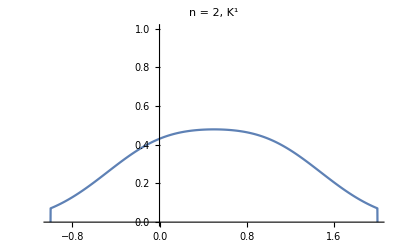
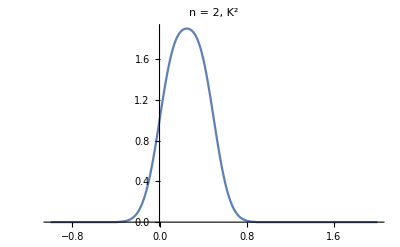
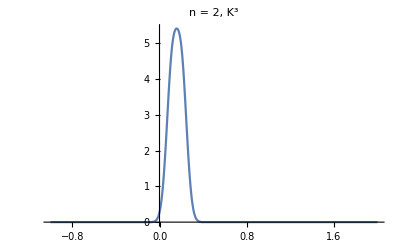
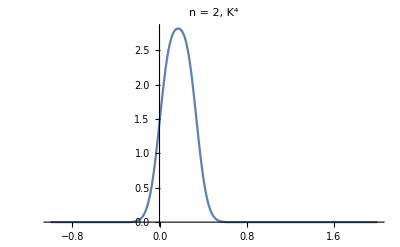
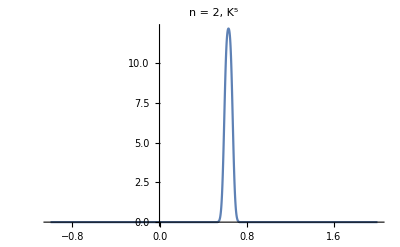
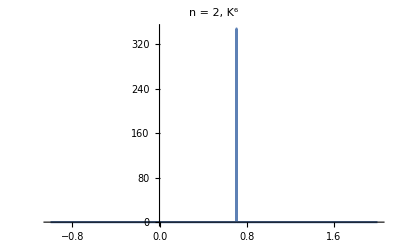
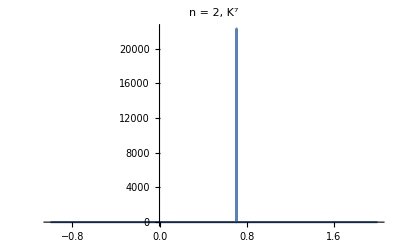
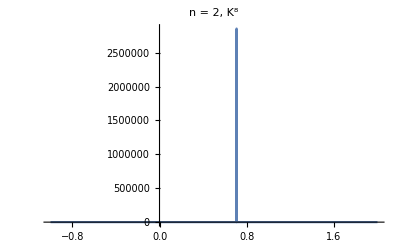
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
saveG2= Grid[{{SmoothHistogram[KsdCoeff2[[1,2]],PlotRange->{{-1,2},{0,1}},PlotLabel->"n = 2, K^1"],SmoothHistogram[KsdCoeff2[[2,2]],PlotLabel->"n = 2, K^2",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff2[[3,2]],PlotLabel->"n = 2, K^3",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff2[[4,2]],PlotLabel->"n = 2, K^4",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff2[[5,2]],PlotLabel->"n = 2, K^5",PlotRange->{{-1,2},All}]},{SmoothHistogram[KsdCoeff2[[6,2]],PlotLabel->"n = 2, K^6",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff2[[7,2]],PlotLabel->"n = 2, K^7",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff2[[8,2]],PlotLabel->"n = 2, K^8",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff2[[9,2]],PlotLabel->"n = 2, K^9",PlotRange->{{-1,2},All}]}},Spacings->{0.5,0.5}]
```

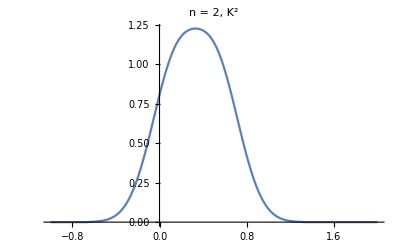
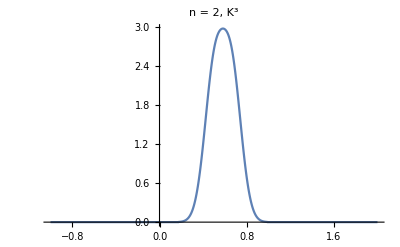
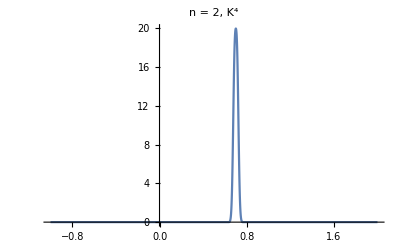
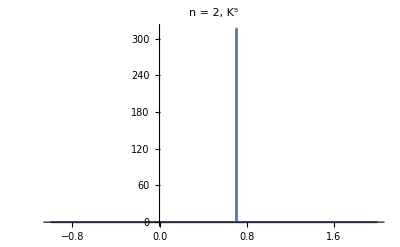
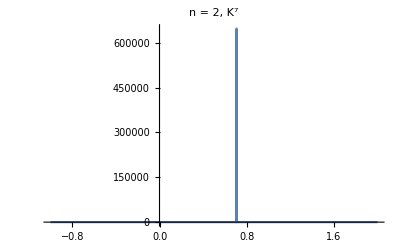
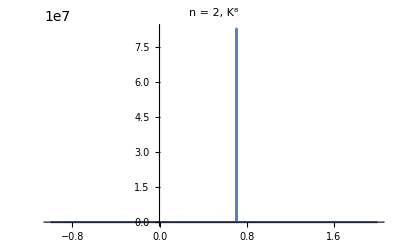
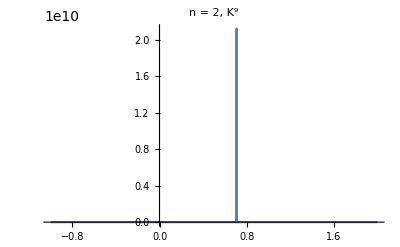
```mathematica
{{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}, {□, -Graphics-, -Graphics-, -Graphics-, }}
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
□ | -Graphics- | -Graphics- | -Graphics- |

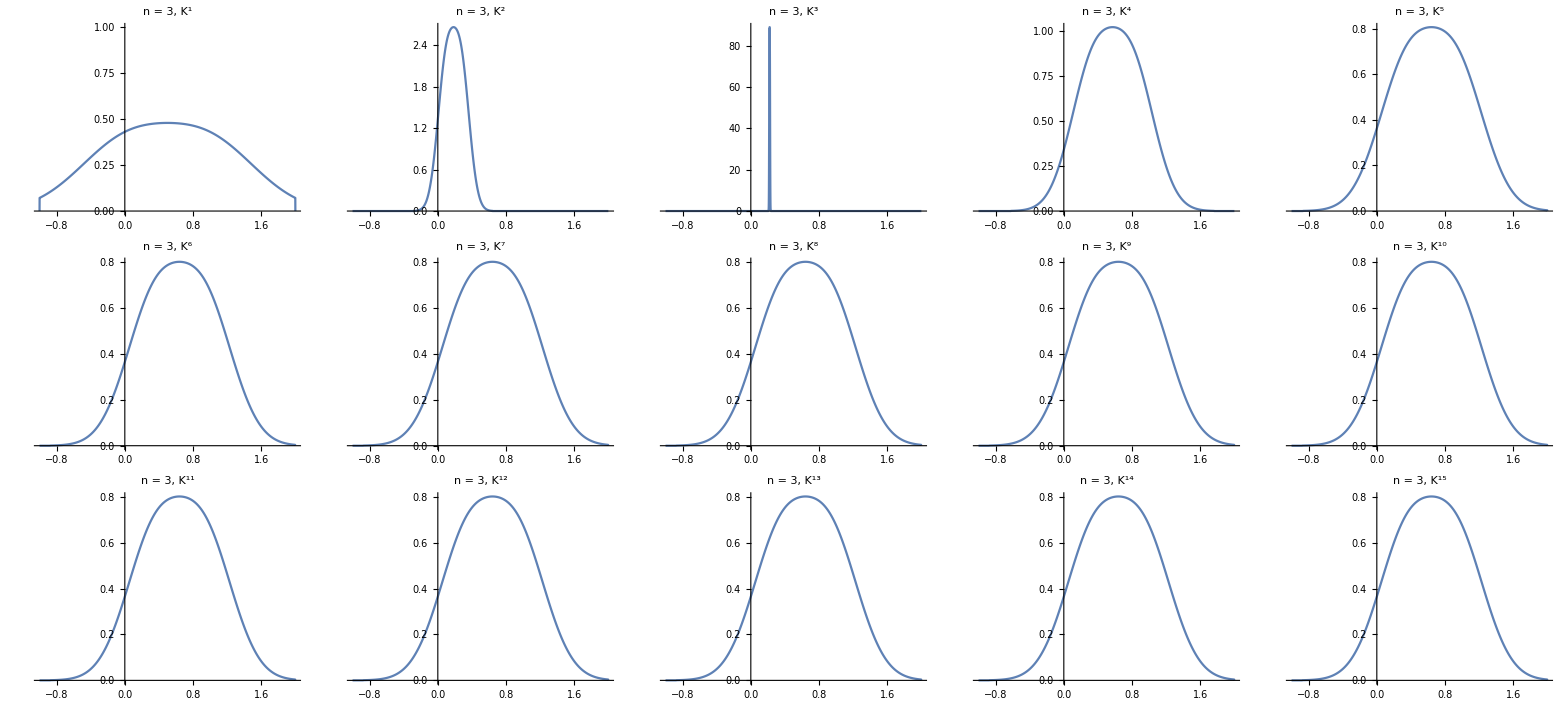

```mathematica
saveG3= Grid[{{SmoothHistogram[KsdCoeff3[[1,2]],PlotRange->{{-1,2},{0,1}},PlotLabel->"n = 3, K^1"],SmoothHistogram[KsdCoeff3[[2,2]],PlotLabel->"n = 3, K^2",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff3[[3,2]],PlotLabel->"n = 3, K^3",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff3[[4,2]],PlotLabel->"n = 3, K^4",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff3[[5,2]],PlotLabel->"n = 3, K^5",PlotRange->{{-1,2},All}]},{SmoothHistogram[KsdCoeff3[[6,2]],PlotLabel->"n = 3, K^6",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff3[[7,2]],PlotLabel->"n = 3, K^7",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff3[[8,2]],PlotLabel->"n = 3, K^8",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff3[[9,2]],PlotLabel->"n = 3, K^9",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff3[[10,2]],PlotLabel->"n = 3, K^10",PlotRange->{{-1,2},All}]},{SmoothHistogram[KsdCoeff3[[11,2]],PlotLabel->"n = 3, K^11",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff3[[12,2]],PlotLabel->"n = 3, K^12",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff3[[13,2]],PlotLabel->"n = 3, K^13",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff3[[14,2]],PlotLabel->"n = 3, K^14",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff3[[15,2]],PlotLabel->"n = 3, K^15",PlotRange->{{-1,2},All}]}},Spacings->{0.5,0.5}]
```

```mathematica
KsdCoeff3[[15,2]]
```

{0.939879,0.341506}

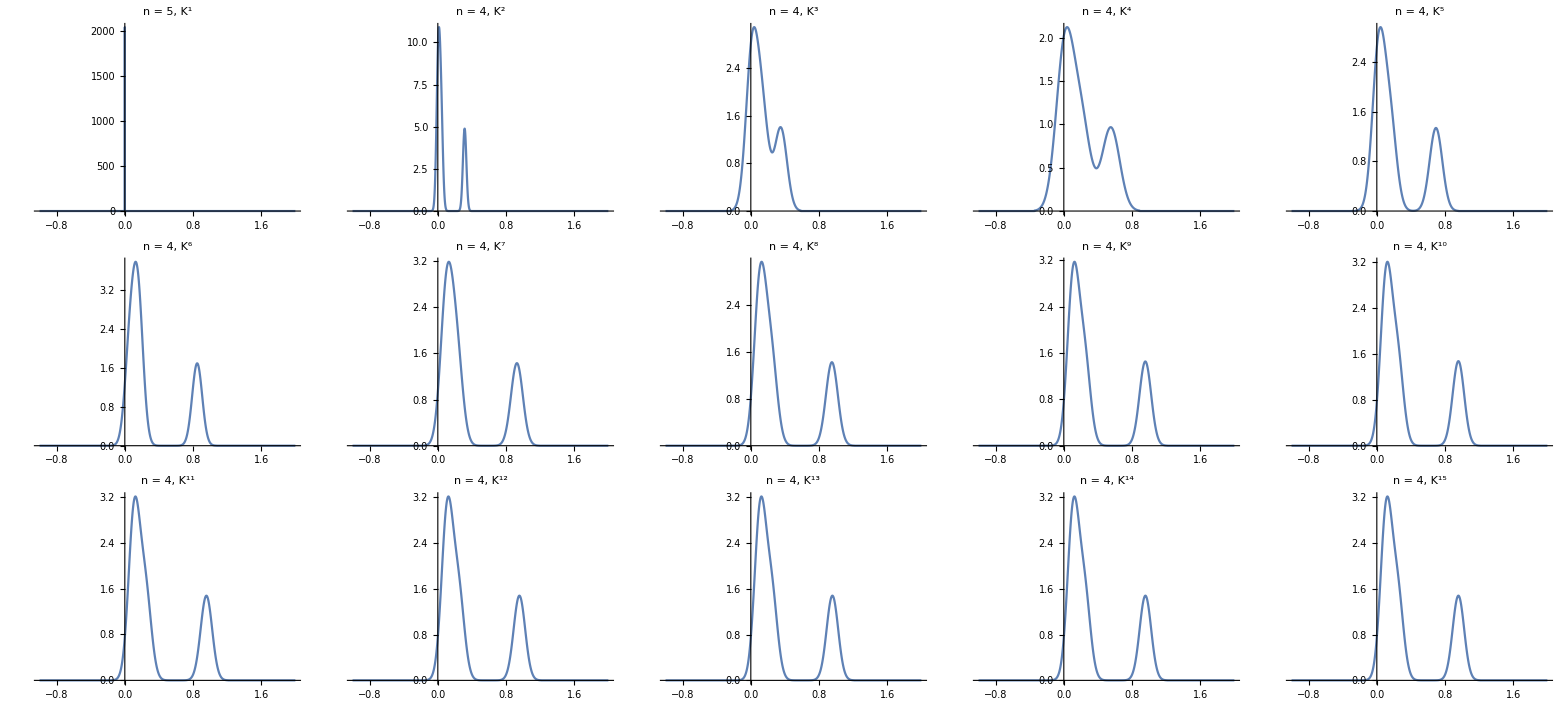

```mathematica
saveG4= Grid[{{SmoothHistogram[KsdCoeff4[[1,2]],PlotRange->{{-1,2},All},PlotLabel->"n = 5, K^1"],SmoothHistogram[KsdCoeff4[[2,2]],PlotLabel->"n = 4, K^2",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff4[[3,2]],PlotLabel->"n = 4, K^3",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff4[[4,2]],PlotLabel->"n = 4, K^4",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff4[[5,2]],PlotLabel->"n = 4, K^5",PlotRange->{{-1,2},All}]},{SmoothHistogram[KsdCoeff4[[6,2]],PlotLabel->"n = 4, K^6",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff4[[7,2]],PlotLabel->"n = 4, K^7",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff4[[8,2]],PlotLabel->"n = 4, K^8",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff4[[9,2]],PlotLabel->"n = 4, K^9",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff4[[10,2]],PlotLabel->"n = 4, K^10",PlotRange->{{-1,2},All}]},{SmoothHistogram[KsdCoeff4[[11,2]],PlotLabel->"n = 4, K^11",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff4[[12,2]],PlotLabel->"n = 4, K^12",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff4[[13,2]],PlotLabel->"n = 4, K^13",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff4[[14,2]],PlotLabel->"n = 4, K^14",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff4[[15,2]],PlotLabel->"n = 4, K^15",PlotRange->{{-1,2},All}]}},Spacings->{0.5,0.5}]
```

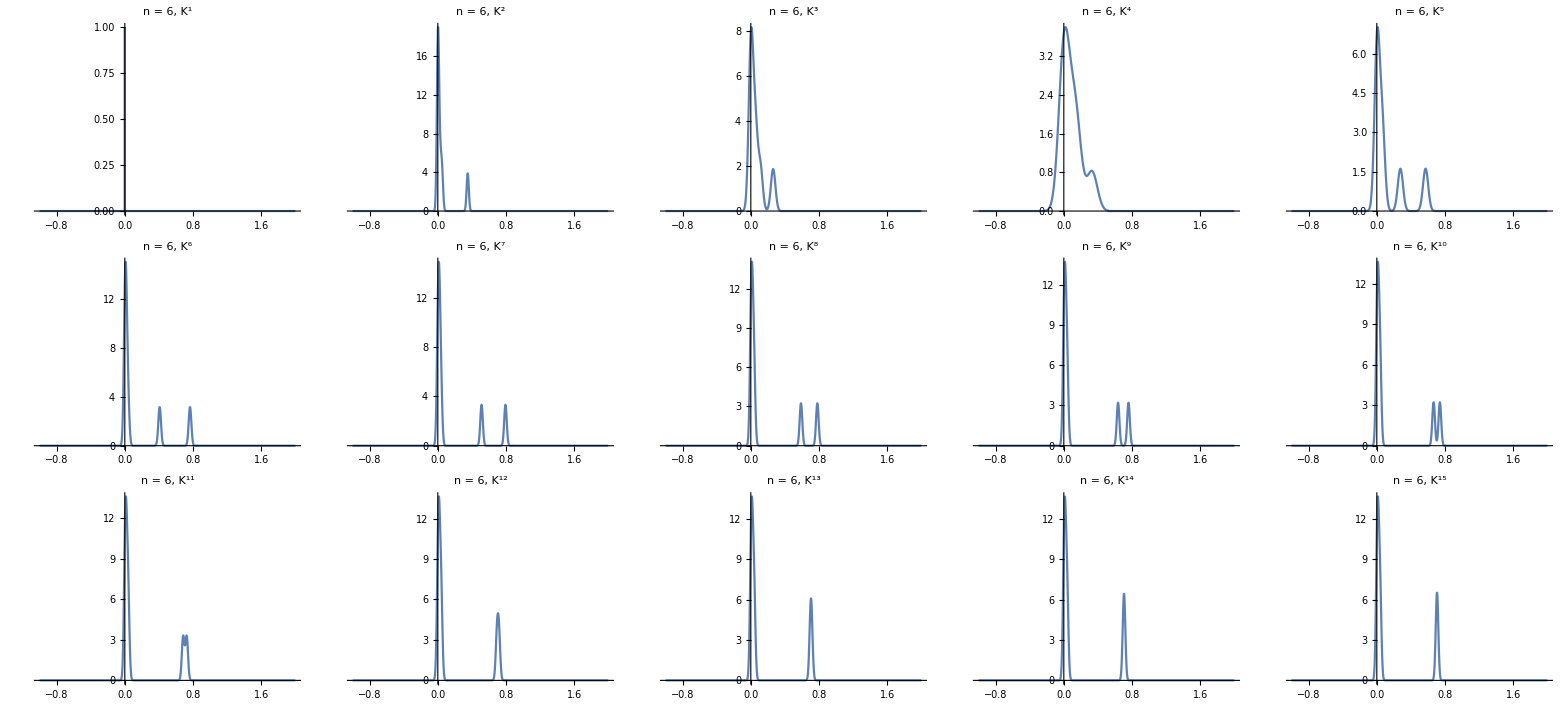

```mathematica
saveG6= Grid[{{SmoothHistogram[KsdCoeff6[[1,2]],PlotRange->{{-1,2},{0,1}},PlotLabel->"n = 6, K^1"],SmoothHistogram[KsdCoeff6[[2,2]],PlotLabel->"n = 6, K^2",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff6[[3,2]],PlotLabel->"n = 6, K^3",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff6[[4,2]],PlotLabel->"n = 6, K^4",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff6[[5,2]],PlotLabel->"n = 6, K^5",PlotRange->{{-1,2},All}]},{SmoothHistogram[KsdCoeff6[[6,2]],PlotLabel->"n = 6, K^6",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff6[[7,2]],PlotLabel->"n = 6, K^7",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff6[[8,2]],PlotLabel->"n = 6, K^8",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff6[[9,2]],PlotLabel->"n = 6, K^9",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff6[[10,2]],PlotLabel->"n = 6, K^10",PlotRange->{{-1,2},All}]},{SmoothHistogram[KsdCoeff6[[11,2]],PlotLabel->"n = 6, K^11",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff6[[12,2]],PlotLabel->"n = 6, K^12",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff6[[13,2]],PlotLabel->"n = 6, K^13",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff6[[14,2]],PlotLabel->"n = 6, K^14",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff6[[15,2]],PlotLabel->"n = 6, K^15",PlotRange->{{-1,2},All}]}},Spacings->{0.5,0.5}]
```

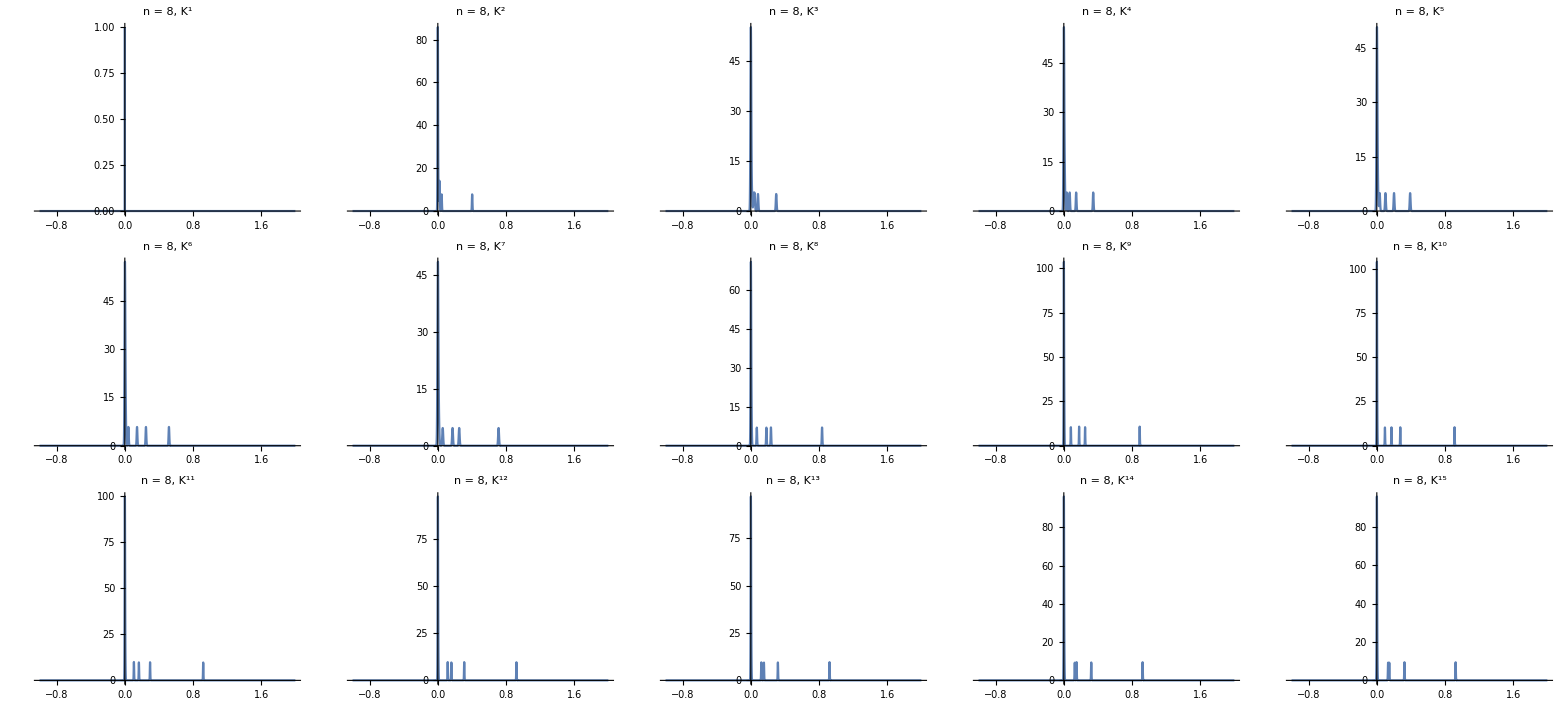

```mathematica
saveG8= Grid[{{SmoothHistogram[KsdCoeff8[[1,2]],PlotRange->{{-1,2},{0,1}},PlotLabel->"n = 8, K^1"],SmoothHistogram[KsdCoeff8[[2,2]],PlotLabel->"n = 8, K^2",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff8[[3,2]],PlotLabel->"n = 8, K^3",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff8[[4,2]],PlotLabel->"n = 8, K^4",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff8[[5,2]],PlotLabel->"n = 8, K^5",PlotRange->{{-1,2},All}]},{SmoothHistogram[KsdCoeff8[[6,2]],PlotLabel->"n = 8, K^6",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff8[[7,2]],PlotLabel->"n = 8, K^7",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff8[[8,2]],PlotLabel->"n = 8, K^8",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff8[[9,2]],PlotLabel->"n = 8, K^9",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff8[[10,2]],PlotLabel->"n = 8, K^10",PlotRange->{{-1,2},All}]},{SmoothHistogram[KsdCoeff8[[11,2]],PlotLabel->"n = 8, K^11",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff8[[12,2]],PlotLabel->"n = 8, K^12",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff8[[13,2]],PlotLabel->"n = 8, K^13",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff8[[14,2]],PlotLabel->"n = 8, K^14",PlotRange->{{-1,2},All}],SmoothHistogram[KsdCoeff8[[15,2]],PlotLabel->"n = 8, K^15",PlotRange->{{-1,2},All}]}},Spacings->{0.5,0.5}]
```

#### Graph

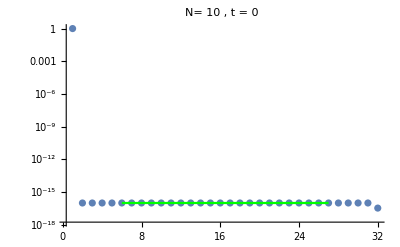
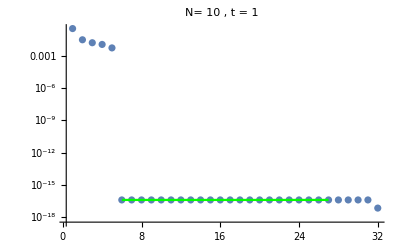
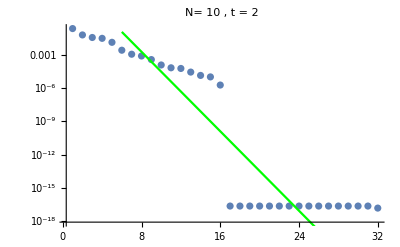
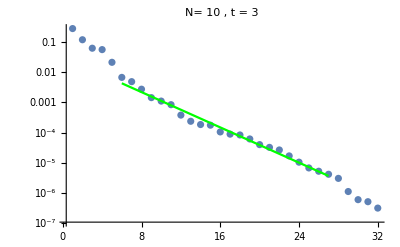
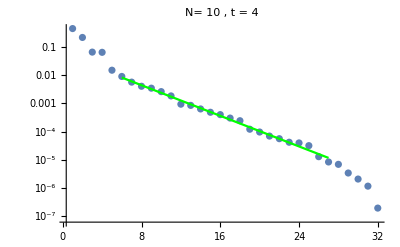
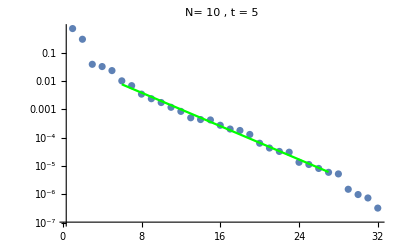
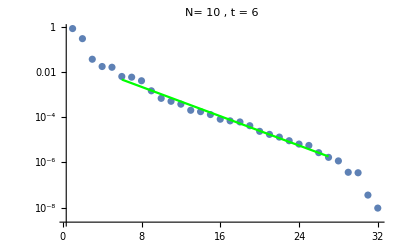
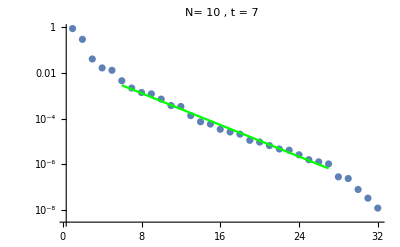

```mathematica
MGSPPlotAnimateHelper[10]
```

#### Animation

```mathematica
MGSPSCTabPlotAnimateTab1 = Table[0,Length[NList]];
For [i=1,i≤ Length[NList],i++,MGSPSCTabPlotAnimateTab1[[i]]=ListAnimate[MGSPPlotAnimateHelper[NList[[i]]]]];
```

```mathematica
MGSPSCTabPlotAnimateTab1[[9]]
```

#### Slope Evaluation

```mathematica
MGSPSCTabPlotSlopeTab1 = Table[0,Length[NList]];
For [i=1,i≤ Length[NList],i++,MGSPSCTabPlotSlopeTab1[[i]]=ListPlot[MGSPPlotSlopeHelper[NList[[i]]],PlotLabel-> StringJoin["N = ",ToString[NList[[i]]]],PlotRange->Automatic]];
```

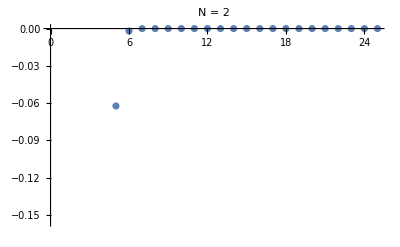
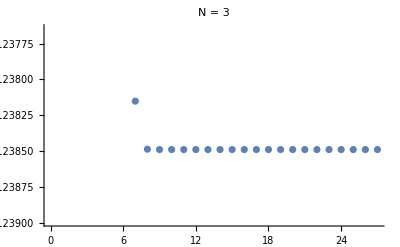
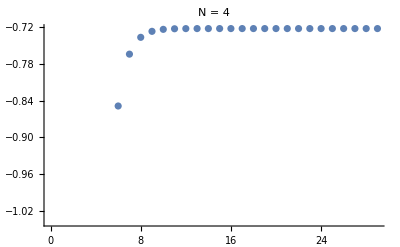
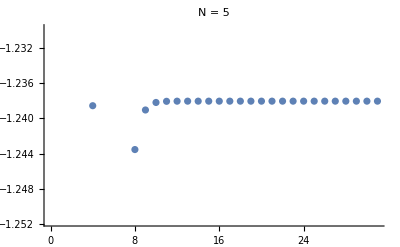
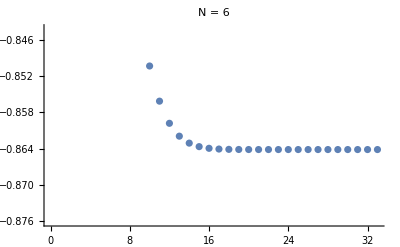
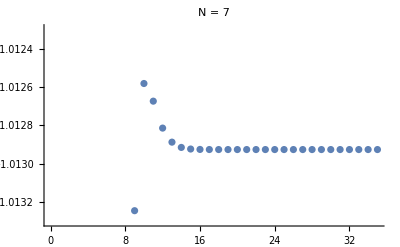
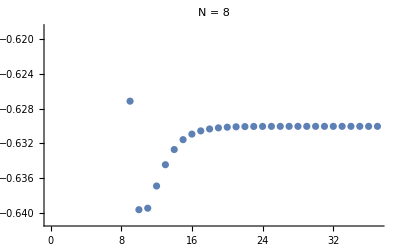
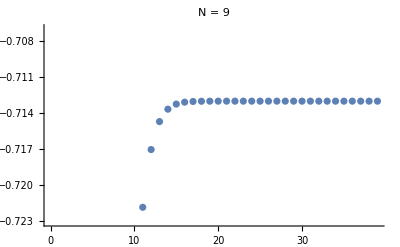

```mathematica
MGSPSCTabPlotSlopeTab1
```

### Δ=2 Trail 2

#### Data

```mathematica
Clear[SDTabPlotDTab ,KsdCoeff2,KsdCoeff3,KsdCoeff4,KsdCoeff5,KsdCoeff6,KsdCoeff7,KsdCoeff8,KsdCoeff9,KsdCoeff10];
```

```mathematica
KsdCoeff2={{0,{0.9999999999999998,1.0148937564738637*10^-17}},{1,{0.40006213712381977,0.07280225166142386}},{2,{0.41149940826201536,0.12619303760890666}},{3,{0.6644783408280673,0.5817244877580862}},{4,{0.70848066703192,0.7026242711557149}},{5,{0.7071923985141757,0.7070089845658796}},{6,{0.707108208173357,0.7071053423057582}},{7,{0.7071067923798909,0.7071067699903002}},{8,{0.707106781230277,0.7071067811428177}},{9,{0.7071067811866328,0.7071067811864621}},{10,{0.7071067811865477,0.7071067811865475}},{11,{0.7071067811865476,0.7071067811865476}},{12,{0.7071067811865476,0.7071067811865476}},{13,{0.7071067811865476,0.7071067811865476}},{14,{0.7071067811865476,0.7071067811865476}},{15,{0.7071067811865476,0.7071067811865476}},{16,{0.7071067811865476,0.7071067811865476}},{17,{0.7071067811865476,0.7071067811865476}},{18,{0.7071067811865476,0.7071067811865476}},{19,{0.7071067811865476,0.7071067811865476}},{20,{0.7071067811865476,0.7071067811865476}},{21,{0.7071067811865476,0.7071067811865476}},{22,{0.7071067811865476,0.7071067811865476}},{23,{0.7071067811865476,0.7071067811865476}},{24,{0.7071067811865476,0.7071067811865476}}};
KsdCoeff3={{0,{1.0,1.4204096045516745*10^-16}},{1,{0.36826304330589066,0.0806674684985248}},{2,{0.5277425593512214,0.22482155141484209}},{3,{0.9076895131518555,0.371510505255421}},{4,{0.9269070254295969,0.37509183853749034}},{5,{0.9270897267764922,0.3748391128295892}},{6,{0.927093625602629,0.3748298402222706}},{7,{0.9270936856679391,0.3748296919863428}},{8,{0.9270936861389057,0.37482969082154666}},{9,{0.9270936861407489,0.3748296908169868}},{10,{0.9270936861407526,0.37482969081697776}},{11,{0.9270936861407524,0.37482969081697776}},{12,{0.9270936861407524,0.37482969081697776}},{13,{0.9270936861407524,0.37482969081697776}},{14,{0.9270936861407523,0.3748296908169777}},{15,{0.9270936861407524,0.37482969081697776}},{16,{0.9270936861407524,0.3748296908169777}},{17,{0.9270936861407524,0.37482969081697776}},{18,{0.9270936861407524,0.3748296908169777}},{19,{0.9270936861407523,0.3748296908169776}},{20,{0.9270936861407523,0.3748296908169778}},{21,{0.9270936861407522,0.37482969081697765}},{22,{0.9270936861407523,0.3748296908169776}},{23,{0.9270936861407523,0.3748296908169776}},{24,{0.9270936861407523,0.3748296908169777}},{25,{0.9270936861407522,0.37482969081697765}},{26,{0.9270936861407522,0.37482969081697776}}};
KsdCoeff4={{0,{1.0,8.899748340608046*10^-17,4.955236788299376*10^-18,5.728250708745847*10^-19}},{1,{0.4952340526147398,0.10046367280165217,0.022851333137088408,0.005133056150217748}},{2,{0.41367347088943895,0.23888872078444215,0.02309708284968067,0.014237010588650243}},{3,{0.41982286343632674,0.26875468406273073,0.016738712703629772,0.009165504286668317}},{4,{0.535353171948078,0.1793244736264194,0.01772790100428463,0.0066716035122967665}},{5,{0.7538183925305625,0.15013793500625353,0.10181511018019855,0.03862551854392686}},{6,{0.9034806020485501,0.21188177744362843,0.12772464575940667,0.07964748412834863}},{7,{0.9466225589545338,0.23881606679028075,0.12001218480089235,0.10064271504186033}},{8,{0.9552161858083391,0.24367025113170993,0.11479764690191514,0.10836382543076692}},{9,{0.9565394467626547,0.24430909207254828,0.1126840761896653,0.11084266502729634}},{10,{0.956692373011273,0.24437331019375336,0.11201252105903413,0.11155463987778706}},{11,{0.9567055350069235,0.24437825234211147,0.11183478822762072,0.11173574262800447}},{12,{0.9567063809517368,0.2443785432431764,0.11179469161821146,0.11177605085066152}},{13,{0.9567064216972575,0.24437855632475367,0.1117869024543658,0.11178385003391877}},{14,{0.9567064231719864,0.24437855677362577,0.11178559386708434,0.1117851589792607}},{15,{0.9567064232121735,0.24437855678536335,0.11178540338258061,0.1117853494734297}},{16,{0.956706423212999,0.24437855678559678,0.11178537933527145,0.11178537352093597}},{17,{0.9567064232130116,0.24437855678560036,0.11178537670091507,0.11178537615529538}},{18,{0.9567064232130116,0.24437855678560036,0.11178537645037945,0.11178537640583101}},{19,{0.9567064232130119,0.24437855678560047,0.11178537642968754,0.11178537642652288}},{20,{0.9567064232130111,0.24437855678560033,0.11178537642820299,0.11178537642800736}},{21,{0.9567064232130112,0.2443785567856003,0.11178537642811043,0.11178537642809991}},{22,{0.9567064232130111,0.24437855678560014,0.11178537642810538,0.11178537642810486}},{23,{0.9567064232130105,0.24437855678560017,0.11178537642810513,0.1117853764281051}},{24,{0.9567064232130106,0.24437855678560017,0.11178537642810513,0.11178537642810513}},{25,{0.9567064232130101,0.2443785567856002,0.1117853764281051,0.11178537642810507}},{26,{0.9567064232130104,0.24437855678559994,0.11178537642810508,0.11178537642810507}},{27,{0.9567064232130101,0.24437855678560005,0.11178537642810506,0.11178537642810506}},{28,{0.9567064232130097,0.24437855678559992,0.11178537642810503,0.111785376428105}}};
KsdCoeff5={{0,{1.0,9.651576848064427*10^-17,3.6943621121455027*10^-17,6.985394158374177*10^-18}},{1,{0.4257348251300773,0.057899057683851785,0.030521677555025307,0.006390871032008417}},{2,{0.46109637877193155,0.16224843663798516,0.051942080312144055,0.009562864800222266}},{3,{0.7414011551928134,0.3353900151079803,0.05338811657152694,0.014491862393850868}},{4,{0.8874631034227425,0.36514578442608775,0.06807705631272377,0.03275910541448159}},{5,{0.9278034075335819,0.3445814084298608,0.08156079246735395,0.04094003694275462}},{6,{0.9373605174174419,0.33208728748423544,0.08753006517733679,0.04386386532957613}},{7,{0.9393654933364181,0.32784417830712015,0.08937706239598286,0.044729430086035644}},{8,{0.9397439378727924,0.3267834191534419,0.08982239659012282,0.04493745234929508}},{9,{0.9398089475175483,0.32657674398809666,0.08990851372228144,0.04497783564157626}},{10,{0.9398186226770886,0.3265446797341133,0.08992191284670485,0.04498414227573101}},{11,{0.9398198156314765,0.3265406831043406,0.08992359024803101,0.044984933750143154}},{12,{0.9398199352072435,0.32654028149484204,0.08992375934149112,0.04498501365411822}},{13,{0.9398199449012192,0.32654024891570904,0.08992377308428787,0.044985020153482005}},{14,{0.939819945536356,0.32654024678070404,0.08992377398578236,0.04498502058000454}},{15,{0.9398199455699926,0.32654024666762205,0.08992377403355349,0.044985020602611094}},{16,{0.9398199455714331,0.3265402466627789,0.08992377403559967,0.04498502060357952}},{17,{0.9398199455714826,0.3265402466626113,0.08992377403567052,0.044985020603613056}},{18,{0.9398199455714837,0.3265402466626066,0.08992377403567253,0.04498502060361392}},{19,{0.9398199455714836,0.3265402466626065,0.08992377403567264,0.044985020603613965}},{20,{0.9398199455714833,0.3265402466626061,0.08992377403567252,0.04498502060361395}},{21,{0.9398199455714827,0.32654024666260595,0.08992377403567259,0.04498502060361395}},{22,{0.9398199455714824,0.326540246662606,0.08992377403567248,0.04498502060361395}},{23,{0.9398199455714823,0.3265402466626058,0.08992377403567244,0.044985020603613916}},{24,{0.9398199455714816,0.3265402466626059,0.08992377403567242,0.04498502060361384}},{25,{0.9398199455714814,0.3265402466626057,0.08992377403567246,0.04498502060361384}},{26,{0.9398199455714817,0.32654024666260556,0.08992377403567238,0.04498502060361385}},{27,{0.9398199455714811,0.3265402466626054,0.0899237740356723,0.04498502060361389}},{28,{0.9398199455714807,0.32654024666260545,0.08992377403567227,0.04498502060361388}},{29,{0.9398199455714804,0.32654024666260545,0.0899237740356723,0.044985020603613896}},{30,{0.93981994557148,0.3265402466626053,0.08992377403567227,0.04498502060361381}}};
KsdCoeff6={{0,{0.9999999999999999,9.704614823761053*10^-17,3.169272036505806*10^-17,1.5224489236281805*10^-17,1.0930744679575642*10^-17,7.04055969277642*10^-18,4.919203590850711*10^-19,1.100764844497748*10^-19}},{1,{0.46412956487556434,0.06338402113830494,0.040950059885458065,0.019720446517442786,0.007090643139524742,2.214256749740586*10^-17,8.212342328709952*10^-18,4.7300133824122654*10^-18}},{2,{0.4041569501105379,0.13662434927494035,0.09010805820663909,0.06510607890173724,0.011313839917625449,0.001160359369487503,0.00021594171841165976,2.6387014768626812*10^-05}},{3,{0.528585435514279,0.24424640456320168,0.12577102641036694,0.06738219642729125,0.005996523225171082,0.002601555313109536,0.0009891745572154376,0.000441995786853493}},{4,{0.6928514322192416,0.3755127006016515,0.0817661240719378,0.041240904074080466,0.008089130708737808,0.004484876397054044,0.0009361879346651675,3.44854950961978*10^-05}},{5,{0.7625214761520617,0.5063567704863796,0.048754803016913706,0.029837815791040962,0.012126012861062987,0.0067135385998579045,0.0023990044990801866,0.0022301077523967333}},{6,{0.7654606313305685,0.597180770185935,0.04146105635743757,0.03204557541255895,0.01518157584370037,0.009743512724111954,0.004060367169297419,0.002898322896049129}},{7,{0.7500215453253177,0.6462257114907931,0.03983926883929527,0.03507369261409202,0.014840872446385496,0.011450425005526961,0.004243998952144687,0.003285287972714061}},{8,{0.7348306812866555,0.6719951735669883,0.03921757606862503,0.03656683501167776,0.01433817435273604,0.01233290703139218,0.004139140566937693,0.0035110183510441957}},{9,{0.7235878647881078,0.6865820584041935,0.038829411707214385,0.03731352369565442,0.01397758468157753,0.012811410139683099,0.004028310226051667,0.003649294513231356}},{10,{0.7160841538067497,0.6952170091344737,0.03856206680113771,0.037714593628148,0.013741555559903813,0.013086763344823995,0.003950165890974939,0.0037349189166548764}},{11,{0.7114309264216623,0.7002627722458393,0.03838771738779883,0.03793510316894088,0.013595778144324508,0.013245721607906812,0.0039014324419452454,0.00378601775198214}},{12,{0.7087389040738271,0.7030842210431445,0.03828319568449363,0.03805412536010787,0.013511424411629658,0.013334225081821997,0.00387333404324227,0.0038148723072300218}},{13,{0.7072839483250072,0.7045779166636059,0.03822551318444876,0.03811589989614047,0.01346581426228687,0.013381019542503007,0.0038582044959488537,0.0038302254620685727}},{14,{0.7065479362894216,0.7053242812957984,0.038196005586740155,0.038146439364500385,0.013442739974364815,0.01340439640721331,0.003850570723666749,0.003837918551980673}},{15,{0.7061987584876607,0.7056759188503546,0.038181927825509665,0.03816074932548584,0.013431794340834318,0.013415411024295313,0.003846954640206183,0.0038415486466576564}},{16,{0.706043141241135,0.7058320555229018,0.03817563708222605,0.03816708669857574,0.013426916910097165,0.013420302483959985,0.0038453443948031326,0.003843161835825528}},{17,{0.705977909562962,0.7058973847340257,0.038172996967307304,0.03816973517291275,0.013424872603067222,0.013422349336478671,0.003844669690991498,0.003843837089927247}},{18,{0.7059521681017791,0.7059231424887487,0.0381719546050202,0.03817077887345994,0.013424065938465535,0.013423156413282115,0.0038444034940372453,0.003844103378449452}},{19,{0.7059425994273117,0.7059327135860785,0.03817156705628595,0.038171166613561736,0.01342376609337841,0.013423456317955057,0.0038443045512515264,0.003844202334803962}},{20,{0.7059392473972464,0.70593606593697,0.03817143128236328,0.038171302411932395,0.013423661055457272,0.013423561363566466,0.0038442698915660007,0.003844236996280719}},{21,{0.7059381404015559,0.7059371729705052,0.03817138644225891,0.03817134725482751,0.013423626367307692,0.013423596052602467,0.0038442584454930814,0.0038442484425643504}},{22,{0.7059377956718217,0.7059375177042186,0.03817137247845968,0.03817136121891155,0.0134236155650945,0.013423606854906829,0.003844254881087979,0.0038442520069915482}},{23,{0.7059376944210034,0.7059376189554104,0.03817136837712941,0.03817136532026785,0.013423612392371949,0.013423610027637884,0.00384425383418589,0.0038442530538957092}},{24,{0.7059376663677568,0.7059376470086889,0.03817136724078556,0.03817136645661378,0.013423611513315954,0.01342361090669447,0.0038442535441241834,0.0038442533439575935}},{25,{0.7059376590344547,0.7059376543419942,0.03817136694373785,0.038171366753661756,0.013423611283524966,0.013423611136485542,0.0038442534683001657,0.0038442534197816306}},{26,{0.7059376572255878,0.7059376561508631,0.03817136687046663,0.03817136682693309,0.01342361122684368,0.013423611193166884,0.0038442534495970577,0.003844253438484745}},{27,{0.7059376568045168,0.7059376565719351,0.03817136685341043,0.0381713668439893,0.013423611213649305,0.0134236112063613,0.003844253445243312,0.0038442534428384943}},{28,{0.7059376567120058,0.7059376566644464,0.038171366849663116,0.038171366847736685,0.013423611210750449,0.0134236112092602,0.0038442534442867803,0.003844253443795034}},{29,{0.7059376566928215,0.7059376566836324,0.038171366848886,0.038171366848513855,0.013423611210149317,0.013423611209861328,0.0038442534440884172,0.0038442534439934025}},{30,{0.7059376566890665,0.7059376566873882,0.03817136684873385,0.03817136684866588,0.013423611210031581,0.013423611209979014,0.003844253444049587,0.0038442534440322382}},{31,{0.7059376566883729,0.7059376566880826,0.03817136684870587,0.03817136684869407,0.01342361121000986,0.013423611210000819,0.0038442534440424124,0.0038442534440394187}},{32,{0.705937656688252,0.705937656688205,0.03817136684870095,0.03817136684869911,0.013423611210006113,0.013423611210004564,0.003844253444041163,0.0038442534440406738}}};
KsdCoeff7={{0,{1.0000000000000002,1.3004869112717207*10^-16,4.418167945235783*10^-17,2.895394248390357*10^-17,1.8264152248786537*10^-17,1.0614846817436854*10^-17,3.3210620760465746*10^-18,1.9121538834536*10^-18}},{1,{0.35771145736751586,0.04912403020977802,0.018115940097414313,0.010474405750430585,0.003287823472481378,3.0771125582411063*10^-17,2.2682362084756327*10^-17,9.444652192954873*10^-18}},{2,{0.22222754867398398,0.11749284664701565,0.049860658808048686,0.03474771269064352,0.006137274701550094,0.0025450979272698343,0.0009325473492981655,0.0007134280907648156}},{3,{0.2709755227443101,0.21321364766345002,0.10406604394110926,0.08343518840229658,0.007914815677593143,0.0026646614800189695,0.0022378108557779587,0.0016545773220134645}},{4,{0.3670683810650615,0.21266864756320827,0.1257067667104095,0.07887110181195034,0.01154426957238131,0.009446834128418504,0.002148819172129629,0.0018610441165752298}},{5,{0.5037610918969808,0.20802049314990328,0.08909932983569717,0.052907013995279036,0.019911057999156687,0.016889662372771178,0.0029342231579859994,0.0020610087183171566}},{6,{0.7072240532563352,0.1967328078835138,0.10382539638025741,0.04499562337645425,0.013404559409989867,0.009186260833954477,0.0033306729752887983,0.0026177873922384374}},{7,{0.8630396282247372,0.266197182090865,0.11970481232725,0.048753884399177695,0.011665698635937399,0.003988335657273108,0.002586522162408631,0.0011823400624958358}},{8,{0.9121568292419804,0.34280301273792846,0.1012332491966424,0.047032241490500476,0.012358180761488608,0.0039177733320122365,0.0028433138545675015,0.0012227341121834492}},{9,{0.9176276916416943,0.37548647018086034,0.09223355455974275,0.044548075677602585,0.013392304320965597,0.004328006386964674,0.002990130559965551,0.001240974443133308}},{10,{0.916227891195979,0.38693263157615715,0.08875768802197403,0.04325761227856757,0.013927036070804425,0.004535442190768942,0.0030873155303723634,0.0012654298759765985}},{11,{0.9152139795291266,0.39060113241874306,0.0875337899456193,0.04275822871910286,0.014127995899860689,0.00461065385501081,0.003130250188369295,0.001277395842987983}},{12,{0.9148396797863896,0.39168511890178476,0.08714449499141769,0.04259409936057441,0.014192883670808449,0.004634155906816987,0.003145464631078387,0.001281735124139076}},{13,{0.9147309258990054,0.3919777917155276,0.08703356196922919,0.04254663921823595,0.01421152654517165,0.004640715725834592,0.0031501073360409096,0.0012830688699453047}},{14,{0.9147036759991621,0.3920495104219523,0.0870052758334297,0.04253443089555123,0.0142163166677332,0.004642361515470576,0.0031513512602359497,0.0012834274254752485}},{15,{0.9146976069223935,0.39206540566171727,0.08699881768601307,0.0425316263747856,0.01421741767508652,0.004642732807499872,0.0031516458504051215,0.0012835125197230971}},{16,{0.9146963929141011,0.3920685862305107,0.08699749653171517,0.04253105008558562,0.014217644106339935,0.004642808101444288,0.003151707741397805,0.001283530423700216}},{17,{0.914696174178414,0.392069160111483,0.08699725426542146,0.04253094406972821,0.014217685791159795,0.004642821821521325,0.0031517193076259914,0.0012835337730553143}},{18,{0.9146961386734161,0.3920692533880418,0.08699721443278503,0.042530926599734724,0.01421769266388975,0.0046428240673072425,0.003151721234475719,0.0012835343314278672}},{19,{0.9146961334849797,0.3920692670324796,0.08699720855964496,0.042530924019907886,0.014217693679169979,0.0046428243974276865,0.0031517215211224222,0.0012835344145332153}},{20,{0.9146961328029447,0.3920692688273237,0.08699720778295023,0.04253092367838985,0.014217693813605712,0.0046428244409956465,0.0031517215592537784,0.0012835344255917938}},{21,{0.9146961327223518,0.39206926903950706,0.08699720769081268,0.04253092363784961,0.014217693829566528,0.004642824446157193,0.0031517215637943915,0.0012835344269088885}},{22,{0.9146961327137956,0.3920692690620395,0.08699720768100701,0.04253092363353339,0.014217693831266035,0.004642824446706037,0.0031517215642787593,0.0012835344270494132}},{23,{0.9146961327129798,0.39206926906418854,0.08699720768007066,0.042530923633121144,0.014217693831428381,0.004642824446758437,0.003151721564325091,0.0012835344270628523}},{24,{0.9146961327129097,0.3920692690643724,0.08699720767999047,0.04253092363308585,0.014217693831442299,0.0046428244467629255,0.0031517215643290693,0.0012835344270640046}},{25,{0.9146961327129045,0.39206926906438666,0.08699720767998424,0.04253092363308314,0.014217693831443345,0.004642824446763272,0.0031517215643293776,0.0012835344270640948}},{26,{0.9146961327129044,0.3920692690643873,0.08699720767998383,0.042530923633082994,0.014217693831443407,0.004642824446763288,0.0031517215643294028,0.0012835344270641033}},{27,{0.9146961327129037,0.39206926906438744,0.08699720767998385,0.042530923633082966,0.014217693831443423,0.0046428244467632915,0.003151721564329388,0.0012835344270641046}},{28,{0.9146961327129037,0.39206926906438755,0.08699720767998388,0.042530923633082945,0.014217693831443435,0.004642824446763291,0.003151721564329405,0.0012835344270641076}},{29,{0.9146961327129037,0.3920692690643877,0.08699720767998387,0.042530923633083015,0.014217693831443426,0.0046428244467633046,0.0031517215643294128,0.0012835344270641063}},{30,{0.9146961327129034,0.39206926906438777,0.08699720767998384,0.04253092363308302,0.014217693831443418,0.0046428244467632985,0.003151721564329411,0.0012835344270641059}},{31,{0.9146961327129032,0.39206926906438755,0.08699720767998378,0.042530923633083056,0.014217693831443423,0.0046428244467632985,0.0031517215643294184,0.0012835344270641035}},{32,{0.9146961327129032,0.3920692690643878,0.08699720767998384,0.042530923633083015,0.014217693831443409,0.004642824446763292,0.0031517215643294015,0.0012835344270641094}},{33,{0.9146961327129027,0.3920692690643879,0.08699720767998385,0.04253092363308304,0.014217693831443418,0.004642824446763299,0.003151721564329405,0.001283534427064108}},{34,{0.9146961327129026,0.3920692690643878,0.08699720767998384,0.04253092363308312,0.014217693831443409,0.004642824446763309,0.0031517215643294136,0.0012835344270641078}}};
KsdCoeff8={{0,{1.0,1.0021320263092245*10^-16,3.089376704800625*10^-17,2.8732526935833744*10^-17,2.1592140952279195*10^-17,1.882742996328542*10^-17,1.3391823457127778*10^-17,9.201475455822237*10^-18,6.771374499444273*10^-18,4.138280496976185*10^-18,2.8557138243906176*10^-18,1.74030830778647*10^-18,1.178889109510598*10^-18,2.378525783190631*10^-19,6.890179835675549*10^-20,3.541888263156471*10^-20}},{1,{0.40122988693681244,0.04400204041782121,0.024101627521113944,0.014425947589709038,0.007715286376876676,3.3251943835525957*10^-17,2.8092442082443685*10^-17,1.9616894096522295*10^-17,1.7823434162190978*10^-17,1.2991458812942386*10^-17,9.250847018976359*10^-18,4.720072726198695*10^-18,4.118182661622038*10^-18,1.5002118934957571*10^-18,8.35650604695981*10^-19,2.663380227583591*10^-19}},{2,{0.277247600994365,0.09189632045969125,0.04307212154562005,0.03785427783901378,0.018120418739445258,0.003655052236822397,0.0013944154469561962,0.0006998316695402783,0.00026438878721693563,9.477617805615413*10^-05,8.821947906464785*10^-05,2.659927857679859*10^-05,1.3023900389306706*10^-05,5.901680134486144*10^-06,1.673740485230029*10^-06,3.631597024748393*10^-07}},{3,{0.3677219753371256,0.17980894458841143,0.08505338332272554,0.03975442242083615,0.02283035680742925,0.00819368066149868,0.004123778397317423,0.003495666858133649,0.0013676205860949971,0.0008533313441386345,0.0008109909474001006,0.0002813751466490336,0.0001941245020327553,0.00012134083334238242,5.152384474030275*10^-05,1.3345944813390185*10^-05}},{4,{0.5062801495662635,0.3237301750789712,0.09725848740624028,0.03947785729490946,0.011414606461990964,0.005237857421324937,0.005091048703404374,0.0043755473756848205,0.0018773040966993235,0.0015423754550000135,0.001260906604319685,0.000891835361126793,0.0004568978273556038,0.00016935357611409216,7.975481237463446*10^-05,2.8280099170248047*10^-05}},{5,{0.5772205608910385,0.40016916242984724,0.09114185000004196,0.05292106446228377,0.008296176757290132,0.005799526802296292,0.004669518920813524,0.0027819394847657898,0.0014518476446721885,0.0011702831247768326,0.0007987139470546588,0.00031980057294621946,0.00015195436339010855,8.890032390934328*10^-05,2.403167024601362*10^-05,1.4062512534964914*10^-05}},{6,{0.6710947489856963,0.36576213944586405,0.09479737551930713,0.06997217984107278,0.00944109899276171,0.00471458792471829,0.0038343936335000664,0.0027284768548498125,0.0019459483221965148,0.0011301255357568602,0.0004533315471144808,0.00033037796517384983,0.00022397940548268502,9.666012388744455*10^-05,7.320271563931857*10^-05,2.8242745474508124*10^-05}},{7,{0.7733189695151138,0.3128612322693784,0.12151829422562999,0.07546577193683263,0.009299856886239853,0.0037202196702558134,0.0031002570628151076,0.0025829059596560217,0.0015623014929521536,0.0007658693064976113,0.0003951253613424909,0.0003583931088085614,0.00017889232224800895,0.00012510716116583592,4.812210139959873*10^-05,3.727547053579296*10^-05}},{8,{0.8536106597249826,0.286578333992373,0.14967892408070935,0.08578089085691314,0.007680693750362104,0.003312503365698037,0.002787124918226627,0.0022151995531697146,0.000987866652304344,0.0005714575189959902,0.0003962687958572766,0.0002842069032310933,0.0001660757059073757,8.47399558947188*10^-05,4.705688924070286*10^-05,2.317141204417897*10^-05}},{9,{0.8979195205672076,0.28968809694600606,0.1618390316373612,0.09868888267019431,0.006824325491991199,0.003162910864617161,0.002555305224121918,0.002218364312091115,0.0007073521084253323,0.0005425055750009111,0.00042679155713804434,0.00025527812027670386,0.00014729281445017967,7.345298713071712*10^-05,4.037214452187276*10^-05,1.982132543667512*10^-05}},{10,{0.9157012110334037,0.30266072425873985,0.16111177841042554,0.10999238266472047,0.006731423173548924,0.0030303460238242977,0.0025792396192254635,0.0023414077610191693,0.0006273613541879812,0.0005651098603923383,0.00044740625660029593,0.00027074969865477204,0.00013392222891428826,7.704670754336206*10^-05,3.622291154071308*10^-05,2.0734707196542475*10^-05}},{11,{0.9214752862835909,0.31305670449047546,0.15668136240797084,0.11870150613435239,0.006806701982259109,0.002941640253949746,0.0026697977539041954,0.0024522351965439114,0.0006258993309125148,0.0005924960203890408,0.0004394630388302923,0.00029518820205228744,0.00012567541933620018,8.404610904387957*10^-05,3.3891750653648464*10^-05,2.260887598682343*10^-05}},{12,{0.9232585266737855,0.31933287998189686,0.1521262231102135,0.1251618367180572,0.0068714776079540395,0.0028789481389236895,0.0027384386980108576,0.0025369377483361495,0.0006352866871206082,0.0006126146612787833,0.0004257046285319156,0.0003156704990822575,0.00011987490320572087,9.041398988009688*10^-05,3.230040293420013*10^-05,2.432381302606022*10^-05}},{13,{0.9239156340110445,0.3227180714706485,0.1483508210310864,0.1298538611037255,0.00690899676548654,0.0028316794887774687,0.002777848928002182,0.0025983808115537343,0.0006408353208325553,0.0006251623487508275,0.00041472090063005213,0.00033003800827578544,0.00011552729420910523,9.532820781517084*10^-05,3.1117398421572495*10^-05,2.56499412682445*10^-05}},{14,{0.9242335734523661,0.3244150092923444,0.14547679146214226,0.1331786717221604,0.006928217963588744,0.0027989256020817675,0.0027952910581249134,0.002641485547742685,0.0006429368690713734,0.0006324263438866019,0.0004074961920911008,0.00033897109487038545,0.00011230975941372926,9.888056256205018*10^-05,3.0244196880037295*10^-05,2.660953075809108*10^-05}},{15,{0.9244072541392607,0.3252125873754625,0.14340275976754255,0.13546917242888754,0.006937379608327466,0.0028075061879340732,0.0027705773992307667,0.0026708997993632384,0.0006432994462453036,0.0006364877460980037,0.0004034211523403159,0.00034386484966155453,0.00011001134613675122,0.00010134801032324456,2.9621156314284213*10^-05,2.7276472928416322*10^-05}},{16,{0.9244999899699479,0.325564744920958,0.14196957849442368,0.13700142022112788,0.006941484075423377,0.002811637381814072,0.002752843324942205,0.002690436073764317,0.0006430045435086799,0.0006387301012641788,0.0004014355304119237,0.0003462201610286493,0.00010843139070657468,0.00010300620648978147,2.9193144399391563*10^-05,2.772487006417905*10^-05}},{17,{0.9245459975471999,0.3257109156377438,0.14101727410665746,0.1379965133563306,0.006943214881489156,0.0028133463420259553,0.002741000494784094,0.0027030590904549433,0.0006425699207389132,0.0006399687512372536,0.0004005808153570934,0.0003472319764267003,0.00010738503653191777,0.00010408638065913658,2.8909795013748804*10^-05,2.8017050498465753*10^-05}},{18,{0.9245670255881399,0.32576798208496194,0.14040735678772387,0.13862382000748527,0.0069439018727180165,0.0028140100476879153,0.0027333893197992796,0.0027109885729680637,0.0006421934947788765,0.0006406571971863451,0.00040024694727714696,0.000347628657631732,0.00010671637679815443,0.00010476876057227306,2.872876714608093*10^-05,2.8201667653167205*10^-05}},{19,{0.9245759007374058,0.32578894776947037,0.14003022329815773,0.13900759898184498,0.006944158545182038,0.002814252510431401,0.002728671859761365,0.0027158281483305497,0.0006419227903506828,0.0006410418225304135,0.0004001263309476202,0.0003477729061149302,0.00010630353596455578,0.00010518683302785291,2.86170140312156*10^-05,2.8314791717453234*10^-05}},{20,{0.9245793730726934,0.3257961991421313,0.13980481280930648,0.1392353979102883,0.006944248827829927,0.0028143358837617576,0.002725847812767218,0.002718696245625927,0.0006417471611652816,0.0006412566037200211,0.000400085625035574,0.0003478219803443091,0.0001060570223743648,0.00010543522276227554,2.8550290381667895*10^-05,2.8382007787754356*10^-05}},{21,{0.9245806365097351,0.32579856101053833,0.13967446436991426,0.13936655389097508,0.006944278731181826,0.002814362879098476,0.0027242130997692316,0.00272034590347031,0.0006416408534288999,0.0006413755817070556,0.00040007273440717,0.00034783766071979456,0.00010591455780923301,0.00010557832033540314,2.851173159069528*10^-05,2.842073296618826*10^-05}},{22,{0.9245810651172756,0.3257992856641124,0.13960148659625493,0.1394397885832263,0.006944288059824996,0.0028143711119867202,0.002723297307853464,0.002721266465377874,0.0006415798020589651,0.0006414404951040967,0.0004000688967873563,0.0003478423740954457,0.00010583482648485179,0.00010565825265555752,2.8490152521140086*10^-05,2.8442364941146208*10^-05}},{23,{0.9245812009386846,0.32579949514298245,0.13956190859339448,0.1394794435185408,0.006944290801291764,0.002814373477455057,0.002722800461974729,0.0027217647438936214,0.0006415462260142463,0.0006414751801776976,0.00040006782192365966,0.0003478437078869346,0.00010579159543696764,0.00010570154377927398,2.8478452346049223*10^-05,2.8454080949779014*10^-05}},{24,{0.9245812412028339,0.32579955220755735,0.13954110854775803,0.13950026525098752,0.006944291560368174,0.0028143741178802114,0.0027225392906107732,0.0027220263202457364,0.0006415284469348296,0.0006414932593477935,0.0004000675385904464,0.00034784406333520794,0.00010576887845050629,0.00010572427767143224,2.847230421022309*10^-05,2.8460233546712614*10^-05}},{25,{0.9245812523821383,0.32579956685898503,0.13953051238848727,0.13951086716639052,0.00694429175842405,0.0028143742812905955,0.0027224062261528435,0.0027221594924789418,0.000641519353846529,0.0006415024289637263,0.0004000674682873772,0.0003478441525610776,0.00010575730656785922,0.00010573585403390031,2.8469172405147302*10^-05,2.846336653529274*10^-05}},{26,{0.9245812552919292,0.32579957040500956,0.13952527876229728,0.13951610223132,0.006944291807125727,0.002814374320592663,0.0027223404990234013,0.002722225246613104,0.0006415148535159142,0.0006415069476895939,0.0004000674518649208,0.00034784417366202875,0.0001057515912344577,0.0001057415704853149,2.846762561557329*10^-05,2.8464913620549437*10^-05}},{27,{0.9245812560024715,0.3257995712141156,0.1395227720662764,0.13951860926603593,0.006944291818413255,0.0028143743295038896,0.0027223090172967114,0.0027222567347116736,0.0006415126958686977,0.0006415091095052097,0.00040006744825318245,0.0003478441783638964,0.00010574885387508001,0.00010574430810750465,2.8466884781462727*10^-05,2.8465654524237532*10^-05}},{28,{0.9245812561653536,0.32579957138818344,0.13952160765877908,0.13951977374863708,0.006944291820879247,0.002814374331408842,0.0027222943931863685,0.0027222713602380296,0.0006415116931135122,0.0006415101131509642,0.0004000674475052832,0.00034784417935122065,0.00010574758233306351,0.00010574557970772098,2.8466540653771717*10^-05,2.8465998667350953*10^-05}},{29,{0.9245812562004225,0.32579957142349525,0.13952108301848587,0.1395202984046192,0.006944291821387096,0.002814374331792846,0.002722287804029469,0.0027222779496913234,0.0006415112412048427,0.0006415105652390595,0.0004000674473594257,0.00034784417954655025,0.00010574700942467204,0.00010574615262826,2.8466385602983326*10^-05,2.846615372135975*10^-05}},{30,{0.9245812562075173,0.32579957143025035,0.1395208537137538,0.1395205277124389,0.006944291821485706,0.0028143743318658136,0.0027222849240922773,0.0027222808296869486,0.0006415110436684191,0.000641510762809589,0.0004000674473326376,0.0003478441795829879,0.0001057467590239764,0.00010574640303134738,2.8466317835046437*10^-05,2.8466221489930182*10^-05}},{31,{0.924581256208866,0.3257995714314687,0.13952075648494724,0.13952062494181752,0.006944291821503799,0.0028143743318789043,0.0027222837029513623,0.0027222820508387194,0.0006415109599060094,0.000641510846578072,0.00040006744732797635,0.0003478441795893479,0.00010574665285026617,0.0001057465092054916,2.84662891004105*10^-05,2.846625022468353*10^-05}},{32,{0.9245812562091071,0.3257995714316765,0.13952071648687533,0.13952066493998955,0.006944291821506922,0.002814374331881188,0.0027222832005968953,0.002722282553195085,0.0006415109254470649,0.0006415108810380604,0.000400067447327279,0.00034784417959051237,0.00010574660917245575,0.00010574655288338332,2.8466277279536847*10^-05,2.846626204557768*10^-05}},{33,{0.9245812562091476,0.32579957143170934,0.13952070052170448,0.13952068090517675,0.006944291821507418,0.0028143743318814855,0.002722283000082789,0.002722282753709503,0.0006415109116927328,0.0006415108947925589,0.0004000674473271375,0.0003478441795906126,0.00010574659173852312,0.0001057465703173235,2.8466272561253784*10^-05,2.8466266763864086*10^-05}},{34,{0.9245812562091529,0.32579957143171406,0.13952069433835226,0.13952068708853133,0.0069442918215074185,0.002814374331881507,0.0027222829224231334,0.002722282831369196,0.0006415109063656108,0.0006415109001197194,0.00040006744732711615,0.00034784417959064816,0.00010574658498632075,0.00010574657706953118,2.846627073385067*10^-05,2.8466268591267698*10^-05}},{35,{0.9245812562091535,0.3257995714317145,0.13952069201447356,0.13952068941241022,0.006944291821507425,0.002814374331881462,0.002722282893236447,0.0027222828605558943,0.0006415109043635373,0.0006415109021217771,0.00040006744732709956,0.0003478441795906226,0.00010574658244864982,0.0001057465796072007,2.8466270047060863*10^-05,2.846626927805752*10^-05}},{36,{0.9245812562091534,0.32579957143171456,0.13952069116692778,0.13952069025995584,0.00694429182150748,0.002814374331881539,0.002722282882591712,0.002722282871200628,0.0006415109036333423,0.0006415109028519619,0.00040006744732713013,0.0003478441795906782,0.00010574658152313015,0.00010574658053272027,2.8466269796580603*10^-05,2.846626952853775*10^-05}}};
KsdCoeff9={{0,{1.0,1.4671398409901597*10^-16,2.796819723720119*10^-17,2.444764958918377*10^-17,2.194255386728122*10^-17,1.5918713980519728*10^-17,9.027921489360421*10^-18,7.207935947534273*10^-18,6.363411154994791*10^-18,5.121438809625458*10^-18,4.6852262007763354*10^-18,3.11144908675842*10^-18,2.530974221769252*10^-18,1.5392397836346377*10^-18,6.5426029613861275*10^-19,2.961108405000098*10^-19}},{1,{0.36267476676216004,0.03771022822624477,0.020518087055699716,0.010453342028373695,0.007046998250224646,2.4884719415241746*10^-17,2.163181372832044*10^-17,1.6795141578767603*10^-17,1.1093815502061589*10^-17,6.991220247575029*10^-18,5.607667384542296*10^-18,3.631979234654577*10^-18,2.79296334043104*10^-18,2.7014718086120673*10^-18,2.5673352949103362*10^-18,8.11136139943069*10^-19}},{2,{0.20722036278312425,0.05646525789126111,0.042864278826267095,0.021158836380434434,0.01400205760973999,0.002342122593649048,0.000848272892019054,0.0006296249151912395,0.00030544904805104964,0.00013897110949501182,7.959912932507251*10^-05,3.0204618096469312*10^-05,7.6223712279096736*10^-06,5.343658908570408*10^-06,2.9317434522158777*10^-06,4.3570212039575357*10^-07}},{3,{0.2522971744965558,0.09822792871270057,0.06222288705985864,0.03811040929229453,0.020457983330918323,0.006087568424424059,0.0037241519080438517,0.002809987693899291,0.002060652278319773,0.0013326426755730992,0.000634500073743815,0.00035991773466744387,0.00014267058957998833,0.00013505706496367098,8.674377144364241*10^-05,7.378908191763262*10^-05}},{4,{0.4285587884873387,0.1661053191065941,0.06017312112341581,0.05134947664128686,0.021518546334586656,0.011322216339217199,0.007528050548208187,0.006273619531824564,0.004499196301484154,0.002792916837872752,0.0021007060144194447,0.001473596967938653,0.000704974159781565,0.0004421370415972494,0.0003159545901235459,0.000117921274759219}},{5,{0.6789963706051795,0.2135568766399494,0.05902740136468619,0.042334502563607566,0.0302719888371957,0.013867775513407834,0.008003810452302322,0.006541332031717807,0.0034244762045901335,0.0026382482863539793,0.001150252539993302,0.0009085774041403423,0.0008272919041263524,0.00036085013780828016,0.0002486545490634221,9.258003070851594*10^-05}},{6,{0.858989897709568,0.22791869528671038,0.076967127934767,0.03372655499984363,0.021951611826539517,0.008291697310051247,0.004596386451412793,0.003906520769886815,0.0018132213240772974,0.0010239784066294138,0.0007717136337204001,0.0004508341070620902,0.00028429698268717677,0.00018422292982113418,0.0001189229658297894,3.290054077806501*10^-05}},{7,{0.9313131255523952,0.23574711046046173,0.09593300859170804,0.031602213776643885,0.006721129991999213,0.0038204611535090013,0.0025350116347336443,0.0011934014054071226,0.0009321888831446975,0.0007173011504406801,0.0004046837980113191,0.00020206401645894674,0.00012726935838043162,0.00010333728256551849,3.2517250731561477*10^-05,2.04272824480733*10^-05}},{8,{0.9519402048878423,0.24838627503475882,0.10296863493352847,0.03185979718789397,0.00809742901134197,0.002128331553183843,0.0017641729584760436,0.0013940540933890249,0.0004832746838274384,0.0003270483428325209,0.00022191848645010598,0.00010694052881040766,8.085246937179617*10^-05,4.942487515520776*10^-05,2.8307452998610914*10^-05,1.869296716591015*10^-05}},{9,{0.9560442191557021,0.26034719254216837,0.10498637989272398,0.032135950496201375,0.011775021892811061,0.003285037692303579,0.001901004288594128,0.0014280804584645946,0.0005434836269564317,0.0004023087593289694,0.0001357816294075059,9.796670858164811*10^-05,3.9718670400474705*10^-05,2.7338880768123692*10^-05,1.55495995817517*10^-05,4.4309942392754614*10^-06}},{10,{0.955963982754072,0.26858224406192027,0.10536520726839464,0.03230977891161852,0.013755023997040152,0.003934945479166001,0.0019857943357646335,0.0016162652477830072,0.0005787932450332493,0.00047432591156725803,0.00015277487762990505,8.997808414794261*10^-05,4.533044456011637*10^-05,2.5930371818063166*10^-05,1.0575782152675856*10^-05,2.90358352941624*10^-06}},{11,{0.9552597768628285,0.2733273526189442,0.10523384404682956,0.03237523074453365,0.014725695678749038,0.004258606233572051,0.00204333477066826,0.001724679363669938,0.0005965883119831934,0.0005145444066506158,0.0001625416528703184,9.310879076897786*10^-05,4.9272592241076945*10^-05,2.6847423781483598*10^-05,1.0738768942591407*10^-05,2.9381315125645058*10^-06}},{12,{0.9547465033873209,0.2757481286658562,0.10500745044580835,0.03237458419806483,0.015177957439878265,0.004409135755699483,0.0020768916587429504,0.001773332129393458,0.0006051979400261963,0.0005338157144183816,0.00016708014275218652,9.549907240637715*10^-05,5.1284460034225156*10^-05,2.7507839383113657*10^-05,1.1145673812186932*10^-05,3.050333743585164*10^-06}},{13,{0.954476206006747,0.276870863268502,0.1048274998688872,0.03235256341376279,0.015376283621798758,0.004474577463627699,0.0020925538180541076,0.001793040009531937,0.0006088151347728635,0.0005421185240839927,0.00016894630147071816,9.663962223200626*10^-05,5.216486852185542*10^-05,2.7819841440332933*10^-05,1.1369021322264622*10^-05,3.112811586932758*10^-06}},{14,{0.9543556803302727,0.2773508546343232,0.10471768356113134,0.03233236301416053,0.015457523005177403,0.004501093780812312,0.0020986775731824427,0.0018004275425165487,0.0006101268307618933,0.0005453833780570811,0.00016963594671279026,9.707693431409634*10^-05,5.250728254562734*10^-05,2.793854983948626*10^-05,1.1461949499774088*10^-05,3.138990985551627*10^-06}},{15,{0.954307688452482,0.2775414641896653,0.10466096914250723,0.032319820631343116,0.015488550147800912,0.004511104261146632,0.002100755691500825,0.0018029880240231565,0.0006105384499063096,0.0005465647218793625,0.00016986584044081677,9.721899376833203*10^-05,5.262776140458369*10^-05,2.7976710039376722*10^-05,1.1494858691044841*10^-05,3.1483177932725736*10^-06}},{16,{0.9542901935923972,0.2776120781404373,0.10463523312313064,0.03231351105274038,0.015499613848956083,0.004514631768123039,0.002101377279724544,0.0018038072119593383,0.0006106487586539724,0.0005469604118579585,0.00016993491440374638,9.725840794366336*10^-05,5.266649795471539*10^-05,2.7987114237912*10^-05,1.1505154784419645*10^-05,3.1512557785895706*10^-06}},{17,{0.9542842779232236,0.2776365430441208,0.10462477210792762,0.03231077723185921,0.015503306051992837,0.004515795045560354,0.0021015412041754736,0.0018040492307820311,0.0006106727618993079,0.0005470837028983378,0.00016995352985186502,9.72674953478511*10^-05,5.267794715890705*10^-05,2.7989430791347008*10^-05,1.150804140540257*10^-05,3.1520869329538666*10^-06}},{18,{0.9542824092041259,0.27764448094813593,0.10462091894596168,0.032309726966617776,0.015504461860096776,0.004516154952031634,0.0021015787337721266,0.0018041153653359176,0.0006106762672900123,0.0005471195913765317,0.00016995797940940762,9.726905679218609*10^-05,5.268107029509307*10^-05,2.7989791527392362*10^-05,1.1508768718043653*10^-05,3.152299072149318*10^-06}},{19,{0.9542818556167014,0.2776468947101947,0.10461962295160807,0.03230936333958041,0.015504801834289934,0.004516259630265418,0.002101585862633505,0.0018041321188536786,0.0006106761658434427,0.0005471293879753999,0.00016995889990782298,9.72691528237423*10^-05,5.2681858995242184*10^-05,2.798979449414883*10^-05,1.1508932493214886*10^-05,3.152347791162361*10^-06}},{20,{0.9542817015324967,0.27764758280248847,0.10461922274278655,0.03230924872601536,0.015504895900304608,0.004516288290423312,0.0021015868309535793,0.0018041360639154487,0.0006106758472876712,0.0005471319042811329,0.00016995905507014253,9.726908621262172*10^-05,5.268204392083057*10^-05,2.798976885839246*10^-05,1.150896492383523*10^-05,3.152357756141893*10^-06}},{21,{0.9542816612050816,0.27764776670348706,0.10461910882015853,0.03230921561458564,0.015504920394327527,0.0045162956827216735,0.002101586848571026,0.0018041369301602043,0.0006106756965127383,0.0005471325142112464,0.00016995907223903346,9.726904711592883*10^-05,5.268208430333577*10^-05,2.7989756007185378*10^-05,1.1508970360290301*10^-05,3.152359530179529*10^-06}},{22,{0.9542816512793837,0.27764781277730227,0.10461907883511837,0.03230920680492095,0.015504926396880175,0.004516297479278411,0.002101586802955286,0.001804137108178259,0.0006106756451234985,0.0005471326540446705,0.0001699590715001163,9.726903290478132*10^-05,5.268209254553843*10^-05,2.7989751543246495*10^-05,1.1508971052238663*10^-05,3.1523597902195735*10^-06}},{23,{0.9542816489826399,0.2776478235956334,0.10461907152014398,0.032309204638657225,0.015504927780810114,0.004516297890569357,0.0021015867827323944,0.0018041371425622497,0.0006106756304685359,0.0005471326844114783,0.00016995907036828272,9.726902872844206*10^-05,5.2682094124361206*10^-05,2.7989750258555324*10^-05,1.1508971087326837*10^-05,3.152359816219029*10^-06}},{24,{0.9542816484832654,0.27764782597566906,0.10461906986298622,0.03230920414503214,0.015504928080826841,0.004516297979213151,0.002101586776623861,0.0018041371488330437,0.0006106756267928384,0.0005471326906618682,0.00016995906995209738,9.726902766317991*10^-05,5.2682094409507936*10^-05,2.7989749934658507*10^-05,1.150897107282283*10^-05,3.1523598158227923*10^-06}},{25,{0.9542816483813052,0.2776478264661238,0.1046190695138263,0.032309204040579256,0.015504928141938587,0.0045162979971851095,0.0021015867750991736,0.0018041371499180195,0.0006106756259630148,0.0005471326918809387,0.0001699590698395344,9.726902742021724*10^-05,5.268209445830535*10^-05,2.7989749861299806*10^-05,1.1508971066274734*10^-05,3.1523598147612186*10^-06}},{26,{0.9542816483617692,0.2776478265607666,0.10461906944531948,0.032309204020020806,0.015504928153626316,0.004516298000609724,0.002101586774765798,0.0018041371500968346,0.0006106756257922097,0.0005471326921060285,0.00016995906981386334,9.726902736986631*10^-05,5.268209446624908*10^-05,2.7989749846178858*10^-05,1.1508971064486341*10^-05,3.152359814412027*10^-06}},{27,{0.9542816483582578,0.2776478265778643,0.10461906943279012,0.03230920401625226,0.015504928155723586,0.004516298001222525,0.0021015867747002097,0.0018041371501249697,0.0006106756257599266,0.0005471326921453173,0.0001699590698086908,9.726902736028977*10^-05,5.2682094467485844*10^-05,2.798974984331113*10^-05,1.1508971064092415*10^-05,3.152359814329267*10^-06}},{28,{0.9542816483576663,0.27764782658075504,0.10461906943065251,0.032309204015608196,0.015504928156076443,0.004516298001325414,0.002101586774688502,0.0018041371501292525,0.0006106756257542881,0.0005471326921517886,0.00016995906980774592,9.726902735863925*10^-05,5.268209446767326*10^-05,2.7989749842806356*10^-05,1.150897106401778*10^-05,3.1523598143130755*10^-06}},{29,{0.954281648357572,0.2776478265812127,0.10461906943031196,0.0323092040155055,0.015504928156132053,0.004516298001341583,0.002101586774686583,0.0018041371501298653,0.0006106756257533672,0.0005471326921527927,0.000169959069807594,9.726902735834034*10^-05,5.268209446770538*10^-05,2.798974984272485*10^-05,1.150897106400427*10^-05,3.152359814309867*10^-06}},{30,{0.9542816483575574,0.2776478265812803,0.10461906943026127,0.03230920401549021,0.015504928156140305,0.0045162980013439885,0.0021015867746862686,0.0018041371501299553,0.0006106756257532371,0.000547132692152936,0.000169959069807569,9.72690273583067*10^-05,5.26820944677035*10^-05,2.7989749842711038*10^-05,1.1508971064000873*10^-05,3.1523598143096043*10^-06}},{31,{0.954281648357555,0.27764782658128956,0.10461906943025413,0.032309204015488056,0.015504928156141408,0.0045162980013443215,0.0021015867746862382,0.0018041371501299726,0.0006106756257532262,0.0005471326921529588,0.00016995906980757418,9.726902735829576*10^-05,5.268209446769958*10^-05,2.7989749842716242*10^-05,1.1508971064001584*10^-05,3.1523598143094845*10^-06}},{32,{0.9542816483575544,0.27764782658129056,0.10461906943025323,0.03230920401548781,0.015504928156141531,0.004516298001344366,0.0021015867746862187,0.001804137150129967,0.0006106756257531951,0.0005471326921529621,0.000169959069807566,9.726902735829675*10^-05,5.2682094467700604*10^-05,2.798974984271387*10^-05,1.1508971064001982*10^-05,3.1523598143094675*10^-06}},{33,{0.9542816483575535,0.2776478265812904,0.10461906943025306,0.03230920401548775,0.015504928156141577,0.004516298001344361,0.0021015867746862283,0.0018041371501299696,0.0006106756257531897,0.0005471326921529619,0.00016995906980758134,9.726902735829573*10^-05,5.268209446770076*10^-05,2.7989749842711695*10^-05,1.1508971064001454*10^-05,3.152359814309456*10^-06}},{34,{0.9542816483575531,0.2776478265812904,0.10461906943025293,0.03230920401548775,0.01550492815614149,0.004516298001344358,0.002101586774686243,0.0018041371501299754,0.0006106756257531936,0.000547132692152961,0.0001699590698075777,9.726902735830173*10^-05,5.2682094467700746*10^-05,2.7989749842708012*10^-05,1.150897106400183*10^-05,3.152359814309406*10^-06}},{35,{0.9542816483575522,0.2776478265812901,0.10461906943025294,0.03230920401548775,0.015504928156141531,0.004516298001344355,0.0021015867746862252,0.0018041371501299744,0.0006106756257531992,0.0005471326921529617,0.0001699590698075642,9.726902735831224*10^-05,5.268209446770054*10^-05,2.798974984271326*10^-05,1.150897106400262*10^-05,3.152359814309557*10^-06}},{36,{0.9542816483575519,0.2776478265812901,0.10461906943025286,0.032309204015487744,0.015504928156141537,0.004516298001344336,0.0021015867746862313,0.0018041371501299685,0.0006106756257532018,0.0005471326921529655,0.0001699590698075783,9.726902735830335*10^-05,5.268209446770182*10^-05,2.7989749842713314*10^-05,1.1508971064002714*10^-05,3.152359814309441*10^-06}},{37,{0.9542816483575509,0.2776478265812901,0.10461906943025272,0.03230920401548773,0.015504928156141481,0.004516298001344319,0.0021015867746862317,0.0018041371501299737,0.0006106756257532019,0.000547132692152965,0.0001699590698075583,9.726902735830444*10^-05,5.268209446770096*10^-05,2.7989749842715503*10^-05,1.1508971064001642*10^-05,3.152359814309553*10^-06}},{38,{0.9542816483575509,0.2776478265812899,0.10461906943025281,0.03230920401548773,0.015504928156141552,0.00451629800134433,0.002101586774686254,0.0018041371501299852,0.0006106756257531953,0.000547132692152965,0.00016995906980757418,9.726902735831435*10^-05,5.268209446770077*10^-05,2.7989749842714934*10^-05,1.150897106400276*10^-05,3.1523598143095247*10^-06}}};
KsdCoeff10={{0,{0.9999999999999997,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,9.618831433383946*10^-17,2.6042003169217962*10^-17}},{1,{0.3664795290105456,0.031210902432489154,0.018204795675865082,0.01074334843171744,0.004833109508889791,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,3.540897855816002*10^-17,1.552737417635077*10^-17}},{2,{0.23923208494033302,0.05509081757755494,0.04909634323636573,0.026698562925418227,0.01068807835281385,0.002742663259135641,0.0015154851324810882,0.000777262506672484,0.00050568120014362,0.0001124639990091499,7.83450428938164*10^-05,4.760373431411278*10^-05,3.990818263323271*10^-05,2.541685513942887*10^-05,1.1692334074319272*10^-05,6.371037516949542*10^-06,1.999156766142766*10^-17,1.999156766142766*10^-17,1.999156766142766*10^-17,1.999156766142766*10^-17,1.999156766142766*10^-17,1.999156766142766*10^-17,1.999156766142766*10^-17,1.999156766142766*10^-17,1.999156766142766*10^-17,1.999156766142766*10^-17,1.999156766142766*10^-17,1.999156766142766*10^-17,1.999156766142766*10^-17,1.999156766142766*10^-17,1.999156766142766*10^-17,8.416968685604183*10^-18}},{3,{0.31532876020706674,0.10530409213736724,0.07911195738227299,0.04586125681011966,0.023629242986241063,0.008167638670435039,0.0038370478760557684,0.0027063379039092453,0.0015760220510427124,0.0011069255364700608,0.000886369176185778,0.0007780437664451918,0.0002556037764870914,0.00016797174839791145,0.00014678622009680408,0.00011686514039250509,9.196282777146238*10^-05,6.984662353473724*10^-05,4.076470238029697*10^-05,3.097594394044565*10^-05,2.1887002692645703*10^-05,1.91486756397981*10^-05,1.5897916477185216*10^-05,1.3326403467060794*10^-05,8.878305142323375*10^-06,6.782382457499421*10^-06,4.094522015224556*10^-06,1.711423083346501*10^-06,1.2950669695152396*10^-06,5.449727762247726*10^-07,2.99974351269061*10^-07,1.1815217813322581*10^-08}},{4,{0.5049760188024974,0.190255675660994,0.0913278562894705,0.04910200791417361,0.024941419337420546,0.011770635388294917,0.005655779333628329,0.0032387831864852746,0.0028496663253939946,0.0020694974601381242,0.0017652852047294674,0.0008998216360208365,0.0006860021440643108,0.0005043271606535207,0.0004389591328170224,0.00029536411682708273,0.0002286978339075857,0.00018863220883511754,9.369497522133171*10^-05,7.8906242977371*10^-05,6.0222347193417124*10^-05,4.156745085281627*10^-05,3.2529373783312685*10^-05,1.910663450111536*10^-05,1.5297994156619572*10^-05,1.2532793796564982*10^-05,7.36902478266181*10^-06,5.875313001092161*10^-06,3.4978953137765656*10^-06,2.5518675063301054*10^-06,1.4258202047568186*10^-06,8.24933759641872*10^-07}},{5,{0.7213921736467291,0.30955596607010466,0.09399455292699427,0.05354440320344789,0.012524629410748328,0.009120349380000118,0.005654792019539743,0.0030377465189817218,0.00196914320761922,0.0013912622326425856,0.0011365102582972955,0.000864334708350925,0.0005876339678924634,0.0004790371306117289,0.0002884880372381436,0.00024742774232402233,0.00017607515760330469,0.00010474072775612231,6.485065787673999*10^-05,4.312975257575466*10^-05,2.5454616602863624*10^-05,1.7215139533549327*10^-05,1.5135316866339482*10^-05,1.055388323112561*10^-05,7.843436837184655*10^-06,7.380241564626851*10^-06,4.808218408541967*10^-06,2.530170094364477*10^-06,1.8309014379557756*10^-06,1.196604283537967*10^-06,7.266399968244741*10^-07,2.928357748593304*10^-07}},{6,{0.8146764083879005,0.402432858987659,0.08998453491459894,0.05072441552492468,0.01621025838183457,0.006973956267051606,0.0031287115882595025,0.0018677460676563297,0.0011962609187408442,0.0005240052009548414,0.0004135008566740864,0.00023381226896336999,0.00020748174903831233,0.0001563986340249307,0.00010751766403109081,7.009641867572522*10^-05,4.614981594512609*10^-05,3.2534862809586646*10^-05,2.4863053413626108*10^-05,1.63505955483588*10^-05,9.518924210248846*10^-06,7.5773414031271056*10^-06,6.5775796494886615*10^-06,3.554960733862788*10^-06,2.3424878102245227*10^-06,2.012969153763762*10^-06,1.7596947974842813*10^-06,6.567523020891412*10^-07,2.951740759886623*10^-07,1.1656383395486522*10^-07,6.0909161393000196*10^-09,3.868958840913655*10^-09}},{7,{0.8309712091836169,0.46661443996531227,0.08292350786413236,0.04867895884468933,0.02294784104541981,0.009418083172988008,0.005309755240973629,0.0026560079146057875,0.0008657836750267805,0.0004980510649303816,0.00023088515908653776,9.318662169759728*10^-05,6.577428379641192*10^-05,6.229763129670417*10^-05,4.445698689342221*10^-05,2.5962992748048105*10^-05,1.9003870035923434*10^-05,1.3890075091365635*10^-05,9.070429309079883*10^-06,7.359388425926792*10^-06,4.556880242907478*10^-06,4.178873312302283*10^-06,2.971058117045397*10^-06,2.146763660069821*10^-06,1.3186699316882213*10^-06,9.861955558457517*10^-07,3.1550002544156576*10^-07,1.4794240351454456*10^-07,8.609938511007253*10^-08,3.8212444038772166*10^-08,6.044961784110423*10^-09,1.735087794963687*10^-09}},{8,{0.8239238102809926,0.5149332086281577,0.07734665525024206,0.04990669627583087,0.0266520807597641,0.012506725088330038,0.006913355218317407,0.0035677648159109076,0.0009385474793265008,0.000569570270435471,0.00022463059482076295,0.00012584836311897615,8.057537409564813*10^-05,5.6992772458633705*10^-05,5.23119141596351*10^-05,2.999422973225188*10^-05,2.3964813329722378*10^-05,1.197882983221815*10^-05,6.2490297047106886*10^-06,5.7983909569588795*10^-06,3.6046809580596973*10^-06,2.50765935757946*10^-06,1.882771956705133*10^-06,1.6587860608559545*10^-06,6.683689009549289*10^-07,6.655443254200575*10^-07,4.4760604543048493*10^-07,1.8426256421351683*10^-07,1.263393905436392*10^-07,4.924981250659729*10^-08,3.400968739492285*10^-08,1.3198801693743682*10^-08}},{9,{0.8106778403387458,0.552630067025723,0.07417101100846393,0.0527195133661709,0.027587357481220855,0.015011022112284129,0.007622749479042125,0.004229577178261913,0.0008759147945233775,0.0005891311529131201,0.00028892000372363595,0.00016679479718580665,8.742662701280951*10^-05,7.015313241424125*10^-05,5.844456171328945*10^-05,4.497189125029855*10^-05,2.1815094755191253*10^-05,1.2486354448832327*10^-05,7.765304814351547*10^-06,5.3730716221053066*10^-06,3.909300353155556*10^-06,3.7087482112429776*10^-06,2.2240870556397896*10^-06,2.2212098320351295*10^-06,1.0404799196135415*10^-06,1.0098981948659684*10^-06,6.310982745535247*10^-07,3.0851736255203093*10^-07,1.7239876574200592*10^-07,8.330289815557846*10^-08,4.6258499476768025*10^-08,2.2333872508568973*10^-08}},{10,{0.796089365376519,0.5824483075625532,0.07262730383427624,0.055499289238492414,0.027442813840984567,0.016865822464351105,0.007784397403209956,0.004708877886101853,0.0008281410811123892,0.0006133446483943623,0.0003099113908551152,0.00019689211950714642,8.879053749670958*10^-05,7.647597774539951*10^-05,5.996993802616786*10^-05,5.364149347063218*10^-05,1.973655860997474*10^-05,1.3948743130735556*10^-05,8.259581086084107*10^-06,5.138325922773238*10^-06,4.658264287247933*10^-06,4.224443910208293*10^-06,2.5441857342874176*10^-06,2.2676336765406436*10^-06,1.320742115087474*10^-06,1.3188594357650036*10^-06,7.353021070142791*10^-07,3.8950697295377675*10^-07,1.9885865416364802*10^-07,1.0490907568214393*10^-07,5.33196934993107*10^-08,2.8120554963797926*10^-08}},{11,{0.7817894658022465,0.60648800775339,0.07182610795523012,0.057886958565190494,0.02696892284348238,0.018251877708271885,0.007701691315100498,0.005075213747805508,0.0008045165519906402,0.0006376414227749858,0.0003115679517067988,0.00021648649996327225,8.875819651955437*10^-05,7.762326210729419*10^-05,6.22042548582115*10^-05,5.907389192399664*10^-05,1.8659795581107855*10^-05,1.516663074859998*10^-05,8.281697325881577*10^-06,5.572208699515299*10^-06,4.808252106776732*10^-06,4.397761496050033*10^-06,2.6044740253833653*10^-06,2.2517394497011995*10^-06,1.5333455674871992*10^-06,1.5062620384338003*10^-06,7.567918707064211*10^-07,4.433185938153477*10^-07,2.0417508971077213*10^-07,1.1931483936115042*10^-07,5.473549166057673*10^-08,3.1980360624409575*10^-08}},{12,{0.7684399690995938,0.6262380602223447,0.0712515842443736,0.05989416639805334,0.02641414700296564,0.01932836833780057,0.007536537243377028,0.005369949122977518,0.000792060018783225,0.0006590065731025099,0.0003074916804057965,0.00023004312411809555,8.741549783805685*10^-05,7.767196970769886*10^-05,6.467213844137752*10^-05,6.283131339196189*10^-05,1.818968783270624*10^-05,1.5940432470507095*10^-05,8.219561645935513*10^-06,6.023325493498014*10^-06,4.817027206620392*10^-06,4.490872217730845*10^-06,2.564905435394503*10^-06,2.2305639530982735*10^-06,1.6844948635782516*10^-06,1.6345806668281078*10^-06,7.460469126924184*10^-07,4.824380862284737*10^-07,2.0111045213999496*10^-07,1.298238357086942*10^-07,5.391062793298915*10^-08,3.479682102236883*10^-08}},{13,{0.7563597547824167,0.6426148347236079,0.0707079481630156,0.06155745692028303,0.02586841107481273,0.020191437844900507,0.007358252412192877,0.005613641116670593,0.0007833941402859887,0.0006771403281079256,0.0003021120092475532,0.0002401608200001733,8.565758641631179*10^-05,7.737928273650251*10^-05,6.705302304109889*10^-05,6.555795980362843*10^-05,1.8003087575750417*10^-05,1.641885110893528*10^-05,8.128246351518452*10^-06,6.364036434658899*10^-06,4.826117296141287*10^-06,4.555533388149399*10^-06,2.5012616075086533*10^-06,2.206528684489949*10^-06,1.796895759207716*10^-06,1.7291133233230362*10^-06,7.265161203372199*10^-07,5.130214436718863*10^-07,1.9577161152644025*10^-07,1.3805773847969536*10^-07,5.247801839745802*10^-08,3.700387183914974*10^-08}},{14,{0.7457151341667401,0.6561605583265437,0.07015925528014273,0.06290959159314528,0.025368155311713658,0.02089233108314424,0.007192959695194855,0.00581597504108185,0.0007759862269110095,0.0006921077448088684,0.0002968426198215643,0.00024807992530851867,8.394599115877243*10^-05,7.691411160018598*10^-05,6.91882700011965*10^-05,6.758094291215351*10^-05,1.791869115753793*10^-05,1.6732161334745895*10^-05,8.024671163998386*10^-06,6.626393057144654*10^-06,4.828882417538886*10^-06,4.606726265124771*10^-06,2.438080114417128*10^-06,2.180203166296075*10^-06,1.8843012770596078*10^-06,1.8018011915568314*10^-06,7.066040718405016*10^-07,5.378237262843588*10^-07,1.9036343799115636*10^-07,1.4474361068080702*10^-07,5.102749688450634*10^-08,3.879612879452681*10^-08}},{15,{0.7365728764750478,0.667239447435089,0.06962478678547715,0.0639868436264692,0.024928782703143398,0.021459800766400628,0.007049253957959601,0.005982307100651718,0.0007692787081019651,0.0007041487274411782,0.0002921334849958072,0.00025438139791539516,8.243603558273468*10^-05,7.63731246440727*10^-05,7.098864338034311*10^-05,6.91169000737238*10^-05,1.7859731555986358*10^-05,1.6952437234705334*10^-05,7.920364814673666*10^-06,6.831137537121678*10^-06,4.8251788140608555*10^-06,4.647728994088143*10^-06,2.3821156294347882*10^-06,2.15345146998075*10^-06,1.9537306369511856*10^-06,1.8585063380414692*10^-06,6.889009346754199*10^-07,5.580653658417111*10^-07,1.8556531300129014*10^-07,1.5020401006875281*10^-07,4.9740796936035017*10^-08,4.0259946383656156*10^-08}},{16,{0.7289171648650123,0.6761566452758527,0.06913192886204245,0.06482905967241506,0.02455558579509852,0.0219137338523119,0.0069289056014793515,0.006116811279674413,0.0007632977447169496,0.0007136260217511267,0.0002881131710662942,0.0002593806768061944,8.116410165521826*10^-05,7.582746486455475*10^-05,7.24502818095982*10^-05,7.02877726137605*10^-05,1.7804451284015725*10^-05,1.7113573657520077*10^-05,7.82330673082269*10^-06,6.990593940089577*10^-06,4.81754138974693*10^-06,4.679748961194874*10^-06,2.3348414534737235*10^-06,2.1281991460958476*10^-06,2.0089375829444334*10^-06,1.9025872221152613*10^-06,6.740154468315807*10^-07,5.744193940153615*10^-07,1.8153478951872318*10^-07,1.5461768208613028*10^-07,4.86600193571465*10^-08,4.144319402283523*10^-08}},{17,{0.7226636621944398,0.6832058085586299,0.06870012271871404,0.06547635753463543,0.024247835095670352,0.02227106036371524,0.0068309172694424715,0.006223561215000958,0.0007581495988024673,0.0007209478542050856,0.0002847906941267848,0.000263298886440841,8.012479865725815*10^-05,7.532393211367827*10^-05,7.36083891559574*10^-05,7.117240983203464*10^-05,1.775116507077169*10^-05,1.7232671219387292*10^-05,7.738160996151257*10^-06,7.113468086904562*10^-06,4.808391902544534*10^-06,4.704072664931492*10^-06,2.296119696795132*10^-06,2.1057864757939905*10^-06,2.0523783564666477*10^-06,1.9364590589912436*10^-06,6.619029702252083*10^-07,5.874133511138119*10^-07,1.7825699521080833*10^-07,1.5812566025207789*10^-07,4.778112080045147*10^-08,4.238365757600746*10^-08}},{18,{0.7176776147119858,0.6886760215490333,0.0683381045248485,0.0659661321837688,0.02400088026533204,0.0225474854707347,0.006753076367434855,0.006306677681708222,0.0007538790995020854,0.0007265117577725165,0.0002821206411634673,0.00026632198161941734,7.929692980633008*10^-05,7.488779392832028*10^-05,7.450783118034845*10^-05,7.18327197126418*10^-05,1.7702610141476938*10^-05,1.732033393183385*10^-05,7.666874893406836*10^-06,7.206843083651405*10^-06,4.799361419465255*10^-06,4.722141667311648*10^-06,2.2652190610755332*10^-06,2.087505869069858*10^-06,2.085395052224332*10^-06,1.962118729407703*10^-06,6.522955113371106*10^-07,5.975457808310171*10^-07,1.7565810099912514*10^-07,1.6086179472342953*10^-07,4.708427963607676*10^-08,4.311720802306598*10^-08}},{19,{0.7137940979227663,0.6928433913639598,0.06804583697726316,0.06633131095253127,0.023807702162025348,0.022757578320208548,0.006692646972585092,0.006370176917036778,0.0007504552862427715,0.0007306752392642431,0.0002800294855141914,0.0002686155414800173,7.865283090175103*10^-05,7.519344690259612*10^-05,7.452803867970529*10^-05,7.231956538651808*10^-05,1.7660994514545044*10^-05,1.738426235664176*10^-05,7.609453858728126*10^-06,7.276756957771426*10^-06,4.791338834564165*10^-06,4.735334667487818*10^-06,2.2411488322777194*10^-06,2.111748640655994*10^-06,2.0714544284834316*10^-06,1.981274201793083*10^-06,6.448479942267596*10^-07,6.052975217922156*10^-07,1.7364404656367006*10^-07,1.6295546943887405*10^-07,4.654426192976645*10^-08,4.3678524424258287*10^-08}},{20,{0.7108369304176069,0.6959608515217367,0.06781751549141549,0.06659972271094759,0.023660181704866567,0.02291446390152884,0.006646756502987897,0.006417790019951622,0.0007477932746537624,0.0007337445745342883,0.0002784309715007728,0.0002703260586044198,7.81628538989305*10^-05,7.570662251480617*10^-05,7.42428742715638*10^-05,7.267417500274415*10^-05,1.7627122340771193*10^-05,1.7430385342384464*10^-05,7.564703488775834*10^-06,7.328326206890379*10^-06,4.784685060379529*10^-06,4.744834578075667*10^-06,2.22282517815187*10^-06,2.130935890562283*10^-06,2.0594485381747813*10^-06,1.9953669369721832*10^-06,6.391991987477603*10^-07,6.111166937766001*10^-07,1.7211673237103557*10^-07,1.645274209877844*10^-07,4.613475701571717*10^-08,4.40999708881551*10^-08}},{21,{0.7086338385973349,0.6982511450618827,0.06764429159789317,0.06679419606426225,0.023550072371027762,0.023029573992502016,0.006612641418432,0.0064528368541189466,0.0007457803396109499,0.0007359737028516454,0.00027723688214635074,0.0002715799314670435,7.779812132761247*10^-05,7.608384740487637*10^-05,7.402435300421232*10^-05,7.292927993016972*10^-05,1.760069640327674*10^-05,1.7463291830462118*10^-05,7.5308262457935955*10^-06,7.3657942274598815*10^-06,4.7794366041426596*10^-06,4.751592372445661*10^-06,2.2091800873007376*10^-06,2.145043981888956*10^-06,2.0503269938454685*10^-06,2.005584380265775*10^-06,6.350039135286156*10^-07,6.154040088571654*10^-07,1.7098258097154356*10^-07,1.6568570748640363*10^-07,4.5830670345796214*10^-08,4.441051472916262*10^-08}},{22,{0.7070269552348563,0.6999037425167389,0.06751630982908838,0.06693303906763969,0.023469663869930716,0.023112557948901317,0.006587799989133861,0.006478164096119297,0.0007442965903144146,0.0007375681033337495,0.00027636434543766727,0.00027248324653702117,7.753227200620775*10^-05,7.635618185915359*10^-05,7.386179078802023*10^-05,7.311042745725192*10^-05,1.7580797390249656*10^-05,1.7486495915438324*10^-05,7.505843039544301*10^-06,7.3926016002693514*10^-06,4.775457096918565*10^-06,4.756343515708185*10^-06,2.19923254299524*10^-06,2.155230171531937*10^-06,2.0435847821118823*10^-06,2.012882531683686*10^-06,6.319513103285184*10^-07,6.18504540720569*10^-07,1.7015742747759402*10^-07,1.6652344224730895*10^-07,4.560943324810677*10^-08,4.463511808099087*10^-08}},{23,{0.7058788479908216,0.7010749497220167,0.0674240389776962,0.06703066481050973,0.023412168437650493,0.023171332842427724,0.006570073308864485,0.006496135003042387,0.0007432285878890036,0.0007386907333242291,0.0002757401556327621,0.00027312272148827753,7.734242560170284*10^-05,7.654927473517972*10^-05,7.37440343159479*10^-05,7.323729134430711*10^-05,1.7566263443003524*10^-05,1.750265558351777*10^-05,7.4878574417274954*10^-06,7.411481258914626*10^-06,4.772537377029223*10^-06,4.759643703796591*10^-06,2.1921283901243754*10^-06,2.1624529211128437*10^-06,2.03872349025358*10^-06,2.0180159637398566*10^-06,6.29774204077557*10^-07,6.207057155653794*10^-07,1.695689741604242*10^-07,1.6711821923500027*10^-07,4.545166013347179*10^-08,4.4794583270875486*10^-08}},{24,{0.7050748744784224,0.7018901774772024,0.06735901972604094,0.06709823121777231,0.023371887539817022,0.023212226968185198,0.006557671662435983,0.006508655053236264,0.0007424768582103852,0.0007394684827670084,0.0002753027043678739,0.0002735674962466803,7.720953894519126*10^-05,7.66837289345473*10^-05,7.366078942929556*10^-05,7.332484199876814*10^-05,1.755593105638169*10^-05,1.7513759450733034*10^-05,7.475198119718377*10^-06,7.424563388153119*10^-06,4.770455433782827*10^-06,4.761906626570098*10^-06,2.1871556510872526*10^-06,2.167482515334514*10^-06,2.0352982192627067*10^-06,2.021569776113056*10^-06,6.28251717589565*10^-07,6.222398587643489*10^-07,1.6915748020384333*10^-07,1.675327784512104*10^-07,4.534133285937639*10^-08,4.4905730791499176*10^-08}},{25,{0.7045228684751461,0.7024474710592379,0.06731418586424232,0.06714423422981586,0.02334422285040744,0.02324017525548448,0.006549162559680481,0.00651721952531371,0.00074195890367,0.0007399983966035644,0.00027500219266486485,0.00027387139370741245,7.711832824188883*10^-05,7.677566980614696*10^-05,7.360326372169964*10^-05,7.338433201764835*10^-05,1.7548763546825913*10^-05,1.752128022954664*10^-05,7.466476281056789*10^-06,7.433478176092965*10^-06,4.769008257734049*10^-06,4.7634368713770106*10^-06,2.1837425201886686*10^-06,2.170921945397488*10^-06,2.0329366425019485*10^-06,2.0239899420739982*10^-06,6.272074085677074*10^-07,6.232896134484223*10^-07,1.688752369169934*10^-07,1.6781645491437294*10^-07,4.526565968117946*10^-08,4.4981787502326365*10^-08}},{26,{0.704151127275622,0.7028216083918356,0.06728390550842203,0.06717503250265076,0.02332558930674585,0.02325893536881053,0.006543435031873418,0.006522972032145147,0.0007416092641746982,0.0007403533410580014,0.0002747997488815959,0.0002740753480631122,7.705691813251589*10^-05,7.68374080788891*10^-05,7.35643554285591*10^-05,7.34241051555379*10^-05,1.754390312266308*10^-05,1.752629677368025*10^-05,7.460589243395794*10^-06,7.439450195026775*10^-06,4.768025548119422*10^-06,4.764456378227531*10^-06,2.1814445954423923*10^-06,2.1732316098215245*10^-06,2.0313418728585706*10^-06,2.0256104848245684*10^-06,6.265046259394324*10^-07,6.239948504729461*10^-07,1.6868530185487447*10^-07,1.680070364297622*10^-07,4.521473565091278*10^-08,4.503288453993272*10^-08}},{27,{0.7039055101155014,0.7030682730317439,0.0672638600503736,0.0671952994134651,0.023313276579497628,0.023271302615969644,0.0065396520437083425,0.006526765893221558,0.0007413778846718014,0.0007405869919300643,0.00027466596200742874,0.0002742097854092969,7.70163502145407*10^-05,7.6878118321179*10^-05,7.35385739912949*10^-05,7.345025412040696*10^-05,1.7540676900241257*10^-05,1.752958959105298*10^-05,7.456693743026847*10^-06,7.443381822368295*10^-06,4.767372647034905*10^-06,4.765125012668685*10^-06,2.179926611495406*10^-06,2.1747546516168046*10^-06,2.03028626849013*10^-06,2.0266770322985005*10^-06,6.2604051148216*10^-07,6.244600323072085*10^-07,1.6855987162091716*10^-07,1.6813274801021593*10^-07,4.518110623145545*10^-08,4.506658925896198*10^-08}},{28,{0.703746251847828,0.7032279730931593,0.06725084615376653,0.06720840471764718,0.023305292603438,0.02327930926075678,0.006537199738557904,0.006529222765403313,0.000741227702834305,0.0007407381125631539,0.00027457920346909926,0.0002742968143214114,7.699004921455992*10^-05,7.690447889297547*10^-05,7.352182598994951*10^-05,7.346715289179141*10^-05,1.753857868035212*10^-05,1.7531715233296128*10^-05,7.4541654707043604*10^-06,7.445924920464711*10^-06,4.766947761493395*10^-06,4.765556392126056*10^-06,2.1789424946259732*10^-06,2.1757408718917583*10^-06,2.0296010157353326*10^-06,2.027366770297371*10^-06,6.2573968152658*10^-07,6.247613102079258*10^-07,1.6847857104407185*10^-07,1.6821416674613536*10^-07,4.515930854277916*10^-08,4.5088418573316925*10^-08}},{29,{0.7036448943112478,0.7033295104275278,0.06724255691977321,0.0672167303772468,0.023300211196482568,0.023284399766596218,0.006535639258358902,0.006530785096946623,0.0007411320581930695,0.0007408341318107905,0.0002745239831105896,0.0002743521431705159,7.69733117862197*10^-05,7.692124038821227*10^-05,7.351115418536155*10^-05,7.347788440782854*10^-05,1.753724068821256*10^-05,1.753306412711897*10^-05,7.452555410702197*10^-06,7.447540854350329*10^-06,4.766676710600273*10^-06,4.7658300307203745*10^-06,2.1783162340123334*10^-06,2.1763679769351544*10^-06,2.029164574239996*10^-06,2.027804986578357*10^-06,6.255482666823643*10^-07,6.249529064837316*10^-07,1.684268407196713*10^-07,1.682659449618202*10^-07,4.5145439010555145*10^-08,4.5102300924530505*10^-08}},{30,{0.7035815670150635,0.7033929083369356,0.06723737521342903,0.06722192609860485,0.023297036344044567,0.02328757814498317,0.0065346643890128965,0.00653176069064104,0.0007410722750810987,0.0007408940592465858,0.00027448948040287156,0.00027438668790721356,7.696285500787765*10^-05,7.693170655204093*10^-05,7.35044814954991*10^-05,7.34845799303517*10^-05,1.7536403683613392*10^-05,1.753390531621031*10^-05,7.451549078560276*10^-06,7.4485494333589175*10^-06,4.766507105252304*10^-06,4.766000631668492*10^-06,2.1779249805817536*10^-06,2.176759557650651*10^-06,2.0288917636507534*10^-06,2.0280784752128226*10^-06,6.25428690539907*10^-07,6.250725535509943*10^-07,1.683945251188143*10^-07,1.6829827929788753*10^-07,4.513677480562068*10^-08,4.511097014452706*10^-08}},{31,{0.7035427194160973,0.70343178270082,0.06723419552098242,0.0672251109979248,0.023295088750366368,0.02328952705790452,0.006534066405579263,0.006532358947634667,0.0007410355920223142,0.0007409307959956257,0.00027446831448380324,0.0002744078695468943,7.695644063941883*10^-05,7.693812445384827*10^-05,7.350038627401895*10^-05,7.348868358224036*10^-05,1.7535889831349342*10^-05,1.7534420719437443*10^-05,7.450931609715161*10^-06,7.449167732157669*10^-06,4.766402963928766*10^-06,4.76610514286389*10^-06,2.1776849814120044*10^-06,2.17699967930365*10^-06,2.0287243629813294*10^-06,2.0282461260101294*10^-06,6.253553448133876*10^-07,6.251459260454189*10^-07,1.6837470339761654*10^-07,1.6831810809379578*10^-07,4.513146036250363*10^-08,4.5116286481491455*10^-08}},{32,{0.7035193190210286,0.7034551928876592,0.0672322798136023,0.06722702857335414,0.02329391558968323,0.02329070069519965,0.006533706218080142,0.006532719234866182,0.0007410134919303177,0.00074095291537506,0.00027445556472472797,0.0002744206249837814,7.695257695534864*10^-05,7.694198942214325*10^-05,7.349791875750775*10^-05,7.349115410455407*10^-05,1.753558015750816*10^-05,1.75347309483711*10^-05,7.4505596170298704*10^-06,7.44954002086994*10^-06,4.766340196362138*10^-06,4.766168043123009*10^-06,2.1775404193587833*10^-06,2.1771442856171773*10^-06,2.0286235096915863*10^-06,2.0283470684009297*10^-06,6.253111667762824*10^-07,6.251901138332441*10^-07,1.6836276427989034*10^-07,1.6833004979044839*10^-07,4.512825934104939*10^-08,4.511948819333422*10^-08}},{33,{0.703505476746755,0.7034690386197794,0.06723114646233751,0.06722816257184423,0.023293221618663307,0.02329139483249349,0.006533493158714404,0.006532932329333721,0.0007410004175808388,0.0007409659964158336,0.0002744480226764702,0.00027442816901227565,7.695029146912955*10^-05,7.694427535902264*10^-05,7.34964588739029*10^-05,7.349261502316981*10^-05,1.7535396920181436*10^-05,1.7534914377585874*10^-05,7.450339550396562*10^-06,7.449760189500989*10^-06,4.76630305369086*10^-06,4.766205231766548*10^-06,2.1774549069162216*10^-06,2.1772298134918895*10^-06,2.028563844917426*10^-06,2.0284067638273*10^-06,6.25285034724887*10^-07,6.252162493136328*10^-07,1.6835570209830154*10^-07,1.6833711287958674*10^-07,4.512636588513193*10^-08,4.512138189222174*10^-08}},{34,{0.7034974350033347,0.7034770815419715,0.06723048799011053,0.06722882126064385,0.02329281845299692,0.02329179805417766,0.006533369382889745,0.006533056117086129,0.000740992821536729,0.0007409735947018166,0.00027444364106751784,0.0002744325512881915,7.694896371763167*10^-05,7.694560326321956*10^-05,7.34956106618921*10^-05,7.349346357933224*10^-05,1.753529044924567*10^-05,1.7535020912556298*10^-05,7.450211695413819*10^-06,7.449888078382985*10^-06,4.766281470908167*10^-06,4.7662268299331635*10^-06,2.1774052287176245*10^-06,2.1772794969176713*10^-06,2.0285291803236205*10^-06,2.028441438605162*10^-06,6.252698535401947*10^-07,6.252314316631569*10^-07,1.6835159938836892*10^-07,1.6834121589788118*10^-07,4.51252658992401*10^-08,4.5122481960669746*10^-08}},{35,{0.7034928464068936,0.7034816705263487,0.06723011225255184,0.06722919706819591,0.02329258840805531,0.023292028117345508,0.006533298757492712,0.006533126746396529,0.0007409884871127287,0.0007409779298514036,0.0002744411409293676,0.00027443505164328,7.694820611123479*10^-05,7.694636091957746*10^-05,7.349512664659204*10^-05,7.349394770520604*10^-05,1.753522969117428*10^-05,1.753508169129626*10^-05,7.450138739801368*10^-06,7.449961044886851*10^-06,4.766269154309929*10^-06,4.766239151501628*10^-06,2.1773768826665233*10^-06,2.1773078446266832*10^-06,2.0285094001455037*10^-06,2.02846122205119*10^-06,6.252611913278945*10^-07,6.252400942600203*10^-07,1.6834925842871096*10^-07,1.6834355695869528*10^-07,4.512463825980529*10^-08,4.512310962718836*10^-08}},{36,{0.7034902747028042,0.703484242353699,0.06722990166353816,0.0672294076790588,0.023292459478220087,0.023292157052908005,0.006533259175348705,0.00653316632978026,0.0007409860578154354,0.0007409803593753092,0.0002744397397121344,0.00027443645292865625,7.694778150823129*10^-05,7.694678553836613*10^-05,7.349485536868056*10^-05,7.349421901740499*10^-05,1.7535195637023716*10^-05,1.753511575187146*10^-05,7.4500978507650085*10^-06,7.4500019373279936*10^-06,4.766262250914828*10^-06,4.766246056448672*10^-06,2.1773609960892384*10^-06,2.1773237317561295*10^-06,2.0284983140292724*10^-06,2.028472309180155*10^-06,6.252563365922791*10^-07,6.252449491240289*10^-07,1.6834794643672024*10^-07,1.6834486898276147*10^-07,4.5124286498974833*10^-08,4.5123461396598195*10^-08}},{37,{0.7034888589246314,0.7034856581696843,0.06722978572828624,0.06722952362089869,0.02329238849963059,0.023292228033235714,0.006533237384610381,0.006533188120897818,0.0007409847204213219,0.0007409816968379482,0.0002744389683118159,0.0002744372243496842,7.694754775572884*10^-05,7.694701929568568*10^-05,7.349470602167039*10^-05,7.349436837466667*10^-05,1.7535176888879*10^-05,1.7535134501953975*10^-05,7.4500753403167394*10^-06,7.450024448738225*10^-06,4.766258450295031*10^-06,4.766249857536763*10^-06,2.177352250223489*10^-06,2.1773324778117776*10^-06,2.0284922108224775*10^-06,2.028478412690785*10^-06,6.252536639585548*10^-07,6.252476217876563*10^-07,1.6834722416074537*10^-07,1.6834559126853196*10^-07,4.5124092848110185*10^-08,4.512365505008708*10^-08}},{38,{0.7034880932896923,0.7034864238158245,0.06722972303152444,0.06722958631957926,0.02329235011532318,0.023292266418052557,0.006533225600479211,0.0065331999051410185,0.0007409839971713149,0.0007409824201079605,0.00027443855114822727,0.00027443764151931417,7.694742134550015*10^-05,7.694714570733119*10^-05,7.349462525588793*10^-05,7.349444914345469*10^-05,1.7535166749937704*10^-05,1.7535144641437483*10^-05,7.450063166890062*10^-06,7.450036622476156*10^-06,4.766256394921362*10^-06,4.766251913045895*10^-06,2.1773475205379014*10^-06,2.177337207511161*10^-06,2.028488910266938*10^-06,2.028481713333498*10^-06,6.252522186357745*10^-07,6.252490671175139*10^-07,1.6834683356418458*10^-07,1.683459818679774*10^-07,4.512398812448107*10^-08,4.5123759774491325*10^-08}},{39,{0.7034876865487453,0.7034868305599739,0.06722968972395642,0.06722961962768703,0.023292329723796662,0.023292286809723457,0.0065332193402071175,0.006533206165445063,0.0007409836129459795,0.0007409828043389008,0.0002744383295315035,0.00027443786313777045,7.694735419055166*10^-05,7.694721286268518*10^-05,7.349458234911855*10^-05,7.349449205103922*10^-05,1.753516136361*10^-05,1.753515002793688*10^-05,7.450056699762061*10^-06,7.450043089660357*10^-06,4.766255302998551*10^-06,4.766253005008472*10^-06,2.177345007932122*10^-06,2.1773397201293754*10^-06,2.028487156853464*10^-06,2.028483466772214*10^-06,6.252514508157283*10^-07,6.252498349394251*10^-07,1.6834662606142*10^-07,1.6834618937138802*10^-07,4.5123932490503226*10^-08,4.5123815408690265*10^-08}},{40,{0.7034874742734826,0.7034870428361207,0.06722967234093384,0.06722963701085632,0.023292319081603022,0.023292297451956483,0.006533216073016909,0.006533209432644068,0.0007409834124211855,0.0007409830048652285,0.0002744382138712691,0.00027443797879845964,7.694731914286595*10^-05,7.694724791048062*10^-05,7.349455995631131*10^-05,7.349451444408618*10^-05,1.753515855251547*10^-05,1.7535152839068503*10^-05,7.450053324653577*10^-06,7.450046464838653*10^-06,4.766254733127674*10^-06,4.766253574889543*10^-06,2.1773436966123604*10^-06,2.1773410314484796*10^-06,2.0284862417572166*10^-06,2.0284843818744426*10^-06,6.252510500982329*10^-07,6.252502356596186*10^-07,1.683465177673283*10^-07,1.683462976659449*10^-07,4.512390345554492*10^-08,4.5123844443709426*10^-08}}};
```

#### /Set

```mathematica
SDTabPlotDTab = {KsdCoeff2,KsdCoeff3,KsdCoeff4,KsdCoeff5,KsdCoeff6,KsdCoeff7,KsdCoeff8,KsdCoeff9,KsdCoeff10};
SDTabPlotDTab [[1]]
```

{{0,{1.,1.01489×10^-17}},{1,{0.400062,0.0728023}},{2,{0.411499,0.126193}},{3,{0.664478,0.581724}},{4,{0.708481,0.702624}},{5,{0.707192,0.707009}},{6,{0.707108,0.707105}},{7,{0.707107,0.707107}},{8,{0.707107,0.707107}},{9,{0.707107,0.707107}},{10,{0.707107,0.707107}},{11,{0.707107,0.707107}},{12,{0.707107,0.707107}},{13,{0.707107,0.707107}},{14,{0.707107,0.707107}},{15,{0.707107,0.707107}},{16,{0.707107,0.707107}},{17,{0.707107,0.707107}},{18,{0.707107,0.707107}},{19,{0.707107,0.707107}},{20,{0.707107,0.707107}},{21,{0.707107,0.707107}},{22,{0.707107,0.707107}},{23,{0.707107,0.707107}},{24,{0.707107,0.707107}}}

#### Graph

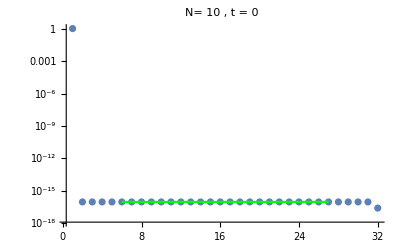
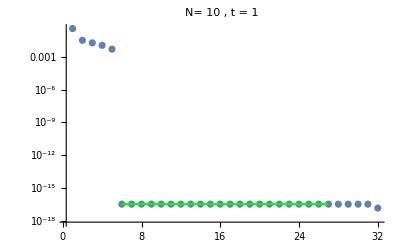
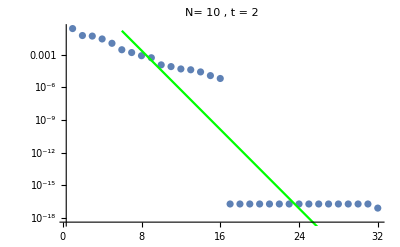
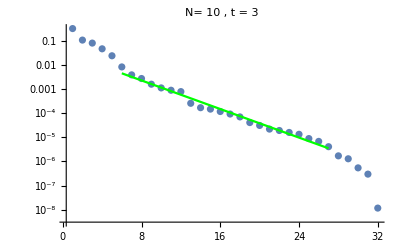
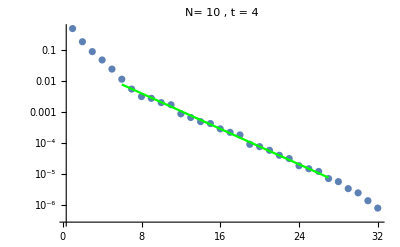
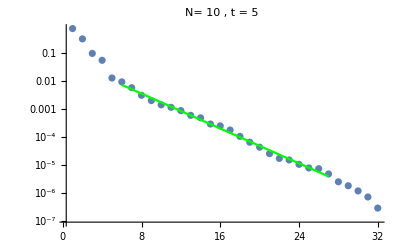
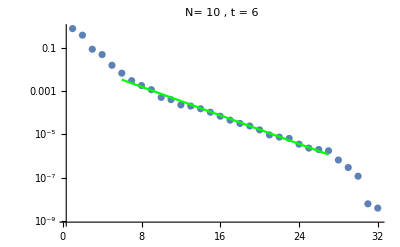
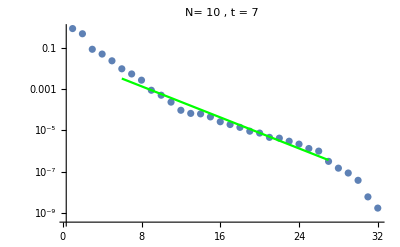

```mathematica
MGSPPlotAnimateHelper[10]
```

#### Animation

```mathematica
MGSPSCTabPlotAnimateTab1 = Table[0,Length[NList]];
For [i=1,i≤ Length[NList],i++,MGSPSCTabPlotAnimateTab1[[i]]=ListAnimate[MGSPPlotAnimateHelper[NList[[i]]]]];
```

```mathematica
MGSPSCTabPlotAnimateTab1[[9]]
```

#### Slope Evaluation

```mathematica
MGSPSCTabPlotSlopeTab1 = Table[0,Length[NList]];
For [i=1,i≤ Length[NList],i++,MGSPSCTabPlotSlopeTab1[[i]]=ListPlot[MGSPPlotSlopeHelper[NList[[i]]],PlotLabel-> StringJoin["N = ",ToString[NList[[i]]]],PlotRange->Automatic]];
```

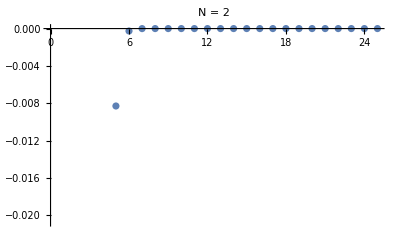
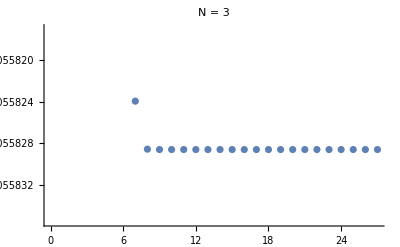
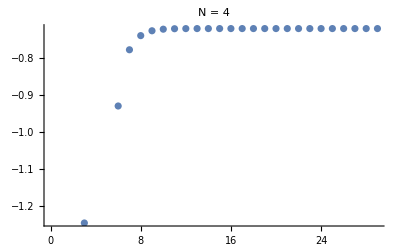
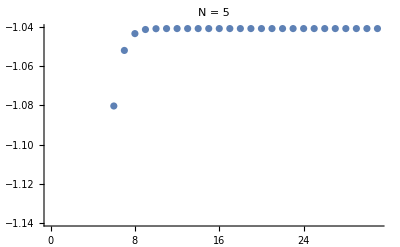
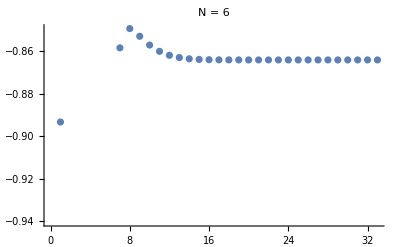
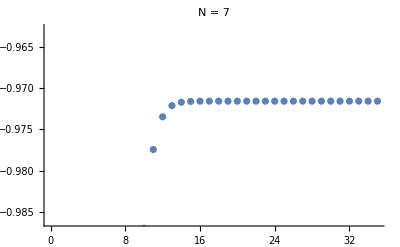
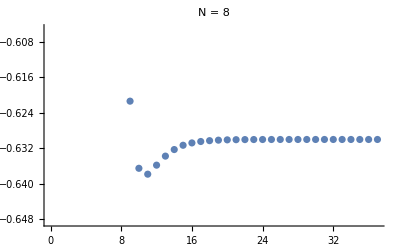
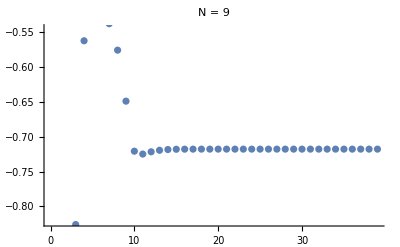
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MGSPSCTabPlotSlopeTab1
```

### Δ=2 Comparison

```mathematica
Table[Show[MGSPSCTabPlotSlopeTab1[[i]],MGSPSCTabPlotSlopeTab[[i]],PlotRange-> Automatic],{i,1,Length[NList]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Δ=5 Trail 1

#### Data

```mathematica
Clear[KsdCoeff2,KsdCoeff3,KsdCoeff4,KsdCoeff5,KsdCoeff6,KsdCoeff7,KsdCoeff8,KsdCoeff9,KsdCoeff10];
```

```mathematica
KsdCoeff2={{0,{0.9999999999999998,2.820299667693477*10^-17}},{1,{0.5839119282645963,0.0020152107943527454}},{2,{0.741411508710439,0.23465278838718867}},{3,{0.7462988249552894,0.5088221599271618}},{4,{0.7289991741997753,0.660560676950699}},{5,{0.712718287167317,0.6997831237634105}},{6,{0.7079370999455009,0.7062171666531516}},{7,{0.7071878418792088,0.7070246745361163}},{8,{0.7071123046232436,0.7071012483369796}},{9,{0.7071070487284948,0.7071065136013809}},{10,{0.7071067904366005,0.7071067719363929}},{11,{0.7071067814149693,0.707106780958125}},{12,{0.7071067811905765,0.7071067811825182}},{13,{0.707106781186598,0.7071067811864965}},{14,{0.7071067811865478,0.7071067811865468}},{15,{0.7071067811865474,0.7071067811865474}},{16,{0.7071067811865471,0.7071067811865471}},{17,{0.7071067811865472,0.7071067811865472}},{18,{0.7071067811865471,0.7071067811865471}},{19,{0.7071067811865471,0.7071067811865471}},{20,{0.7071067811865472,0.7071067811865472}},{21,{0.7071067811865471,0.7071067811865471}},{22,{0.7071067811865471,0.7071067811865471}},{23,{0.7071067811865471,0.7071067811865471}},{24,{0.7071067811865471,0.7071067811865471}}};
KsdCoeff3={{0,{0.9999999999999998,8.295578190909635*10^-17}},{1,{0.590832199455585,0.17781799805108744}},{2,{0.6017761203263672,0.4493343995813736}},{3,{0.8218775762783701,0.5320325337971461}},{4,{0.8469135973338703,0.5312329615047365}},{5,{0.8475775807293282,0.5306700101767419}},{6,{0.8475905396623682,0.5306508040510993}},{7,{0.8475907121095044,0.5306505297702464}},{8,{0.8475907133343972,0.5306505278140105}},{9,{0.8475907133388677,0.5306505278068694}},{10,{0.847590713338876,0.5306505278068561}},{11,{0.847590713338876,0.530650527806856}},{12,{0.8475907133388763,0.5306505278068563}},{13,{0.8475907133388761,0.5306505278068563}},{14,{0.8475907133388761,0.5306505278068563}},{15,{0.8475907133388761,0.5306505278068562}},{16,{0.8475907133388758,0.5306505278068561}},{17,{0.8475907133388759,0.530650527806856}},{18,{0.847590713338876,0.530650527806856}},{19,{0.8475907133388759,0.5306505278068556}},{20,{0.847590713338876,0.5306505278068556}},{21,{0.8475907133388758,0.5306505278068557}},{22,{0.8475907133388757,0.5306505278068556}},{23,{0.8475907133388759,0.5306505278068555}},{24,{0.8475907133388757,0.5306505278068555}},{25,{0.8475907133388757,0.5306505278068554}},{26,{0.8475907133388757,0.5306505278068554}}};
KsdCoeff4={{0,{1.0000000000000002,2.0036286134557135*10^-17,1.0355440661397585*10^-17,9.808416995310436*10^-19}},{1,{0.4251998809731529,0.06048057879262422,0.02974604297195164,0.00045533849328352753}},{2,{0.43691605537286904,0.0831766100449767,0.06628306649651848,0.0038013760787143323}},{3,{0.6441663439037344,0.16297126609704374,0.07359908913383689,0.015496436597291602}},{4,{0.8227348032875037,0.18649793240157683,0.07995374269202275,0.01903367881336318}},{5,{0.8590084206551708,0.11801408333624648,0.0810790911498395,0.012290946373366918}},{6,{0.8702548170208179,0.0810420686035937,0.02017614976282586,0.002200545700954139}},{7,{0.881358903972317,0.09093155825707785,0.08049653096771321,0.009661220277982833}},{8,{0.8897745925820262,0.2030044100099571,0.07905860735890652,0.022272322688864584}},{9,{0.8934187909299967,0.2991450693139522,0.0764789505839739,0.03410479851260424}},{10,{0.8940193393696008,0.3667732141712977,0.07313764372627465,0.043772797687507886}},{11,{0.8941983136674531,0.4054784683426128,0.06976870375115964,0.0507473842068551}},{12,{0.8947265068720447,0.4239125746578554,0.06694992264792979,0.055324496449371006}},{13,{0.8952832200689247,0.43148702188807864,0.06489160392980858,0.058136799280155936}},{14,{0.8956424697825982,0.43425410929861197,0.06353326271520016,0.05978503866411126}},{15,{0.8958176831373763,0.43516889357306526,0.06270508901213957,0.06071428538161418}},{16,{0.8958882433732207,0.43544489783989276,0.062232296779591675,0.06121921375652089}},{17,{0.8959127220984849,0.4355211761485878,0.061977489876682834,0.06148336363126324}},{18,{0.8959202023180947,0.43554051598105276,0.06184718384727455,0.06161615662343001}},{19,{0.8959222413754646,0.4355450178461483,0.061783747085192665,0.06168019991045571}},{20,{0.895922741064902,0.43554598035868064,0.06175428658606688,0.06170979599626242}},{21,{0.8959228517094461,0.43554616942951196,0.06174121790193911,0.061722892472318956}},{22,{0.8959228739242332,0.43554620356045787,0.06173567578288127,0.06172843981618916}},{23,{0.8959228779787238,0.43554620922363646,0.06173342776073407,0.06173068873943387}},{24,{0.8959228786526844,0.43554621008746613,0.061732555280580095,0.06173156136218362}},{25,{0.895922878754865,0.4355462102086115,0.06173223120686784,0.06173188545660439}},{26,{0.8959228787690109,0.4355462102242338,0.06173211598331202,0.061732000682920556}},{27,{0.8959228787708012,0.4355462102260863,0.06173207676329302,0.06173203990327736}},{28,{0.8959228787710083,0.4355462102262887,0.06173206398146072,0.061732052685147636}}};
KsdCoeff5={{0,{1.0,8.836905124853558*10^-17,1.6598918089938083*10^-17,4.438025980937078*10^-18}},{1,{0.5388563675530316,0.09548443180259131,0.02929816428969717,0.01318289501235038}},{2,{0.5300502799721002,0.2084888185173817,0.04828240669893004,0.02934275595364271}},{3,{0.7593635166663747,0.3010145340569825,0.07359477957861642,0.030578816439811165}},{4,{0.9070371300279756,0.33588847784558284,0.07826884745257108,0.030946967392254048}},{5,{0.9342368910503706,0.3401499099513355,0.07703303182852735,0.03080617569499315}},{6,{0.9363785617747225,0.3408350004787791,0.07641453657903047,0.030784704857630022}},{7,{0.9364012480437476,0.34113821557371216,0.07628392191849945,0.03079725356302384}},{8,{0.9363775701541357,0.34122111506219166,0.07626353393255994,0.030802199484149445}},{9,{0.936372650781218,0.3412355544458125,0.076260848152745,0.03080312224707153}},{10,{0.93637202139532,0.3412373469759289,0.07626054780346146,0.030803236033200607}},{11,{0.9363719623403677,0.3412375143984178,0.0762605201364153,0.03080324622454899}},{12,{0.9363719580884508,0.3412375264621133,0.07626051808927477,0.030803246912830897}},{13,{0.9363719578498868,0.34123752714038497,0.07626051796913448,0.03080324694840768}},{14,{0.9363719578393948,0.3412375271702939,0.07626051796356773,0.030803246949820933}},{15,{0.9363719578390316,0.34123752717133093,0.07626051796336437,0.030803246949863982}},{16,{0.9363719578390209,0.34123752717135925,0.07626051796335845,0.03080324694986498}},{17,{0.9363719578390212,0.3412375271713599,0.07626051796335831,0.030803246949865005}},{18,{0.9363719578390212,0.3412375271713599,0.07626051796335828,0.030803246949864988}},{19,{0.9363719578390212,0.34123752717135997,0.07626051796335831,0.030803246949864978}},{20,{0.936371957839021,0.34123752717135986,0.07626051796335831,0.030803246949864978}},{21,{0.936371957839021,0.34123752717136013,0.07626051796335821,0.03080324694986498}},{22,{0.9363719578390212,0.34123752717136013,0.07626051796335824,0.03080324694986501}},{23,{0.9363719578390212,0.3412375271713602,0.07626051796335825,0.030803246949865005}},{24,{0.9363719578390205,0.34123752717136,0.07626051796335835,0.030803246949865033}},{25,{0.9363719578390204,0.34123752717136024,0.07626051796335827,0.030803246949865016}},{26,{0.9363719578390208,0.3412375271713602,0.07626051796335825,0.030803246949865033}},{27,{0.9363719578390212,0.3412375271713603,0.07626051796335831,0.030803246949865016}},{28,{0.9363719578390214,0.34123752717136024,0.07626051796335825,0.03080324694986503}},{29,{0.9363719578390212,0.34123752717136013,0.07626051796335824,0.03080324694986503}},{30,{0.9363719578390214,0.34123752717136024,0.0762605179633583,0.030803246949865047}}};
KsdCoeff6={{0,{1.0,7.529140434412638*10^-17,3.365566997938092*10^-17,1.4907890222021287*10^-17,1.1762026605426188*10^-17,4.648983757975273*10^-18,8.03378160880604*10^-19,2.648839246007607*10^-19}},{1,{0.4388068090608761,0.08051121684937851,0.020550713389651278,0.004150113978066346,0.002946102255228636,1.1062234386884644*10^-17,4.4129767945722086*10^-18,7.370289753837244*10^-19}},{2,{0.33791394069310404,0.12772409731816464,0.023272356956408134,0.0071637461420822595,0.006294300200411353,0.0001311623681522526,0.00010412590700728323,1.4949102615273165*10^-05}},{3,{0.3656386468721153,0.21195452971621515,0.028182547085167396,0.009254005203261568,0.005198560269848826,0.001057252365368618,0.00018342594742419506,8.530309422640753*10^-05}},{4,{0.4552547932685666,0.3768324676100177,0.025855386423271995,0.025325150119276624,0.005018837637410965,0.0018556066213482598,0.000621929497455731,0.00027663292502097645}},{5,{0.6796989229153558,0.5124288594444588,0.05166905313500586,0.03892491638573274,0.006618599535740886,0.004012686997579519,0.0006780695296759492,0.0004075767626872992}},{6,{0.7510433013745893,0.549888132127662,0.06203686414933646,0.04539752315717166,0.0066647493806828335,0.004747529407421247,0.0006741063923273849,0.0004797497204940704}},{7,{0.7569457748479168,0.5430180236548442,0.06373999302450357,0.045714151782486015,0.006563279855285139,0.004789573644261136,0.0006631867841697232,0.0004840298980197667}},{8,{0.757259237825565,0.5290098456134513,0.06402054313440111,0.044710444437383666,0.006536452980707135,0.004691578795771588,0.0006603909269949419,0.0004741378317129975}},{9,{0.7585834705033749,0.5125196313899916,0.0642163060532284,0.043371605906451734,0.006537873635929789,0.004556970401229264,0.0006605133670419532,0.0004605407766634503}},{10,{0.7614621539877126,0.49369707420964315,0.06453507758647543,0.04182580665441578,0.006554623331511935,0.004400104910355441,0.0006621889097097769,0.0004446936289094033}},{11,{0.7660969686078726,0.472142261191145,0.06502616897366359,0.04005841446998056,0.006585557559462108,0.004220181938431006,0.0006652941197192504,0.00042651649065628995}},{12,{0.7726963687879925,0.44727986113014995,0.06572339947314075,0.03802615438366419,0.006631774952623267,0.00401278316117146,0.0006699375757270528,0.00040556297901518114}},{13,{0.7814662585607229,0.4183909134255582,0.06666562069478732,0.035672614249173895,0.0066946568543526375,0.003771837422108618,0.0006762563335897065,0.0003812193677566063}},{14,{0.792573034630556,0.38460921715246205,0.06790195211776176,0.032929418629796925,0.006775249401798224,0.003489852008804625,0.0006843523423883128,0.0003527280791921513}},{15,{0.80608347854174,0.3449327458434098,0.06949876150451638,0.02971673143385093,0.006873718790445225,0.0031579388582713987,0.000694236340079023,0.0003191902977789001}},{16,{0.8218708623952758,0.2982840695571421,0.07155689861832859,0.025946421011053062,0.00698858885680089,0.0027660845147380745,0.0007057488055373015,0.0002795931766432559}},{17,{0.8394819810987513,0.24367622687030546,0.07426024368489072,0.021530703651375462,0.007115710696050762,0.00230399494219181,0.0007184513020692605,0.00023289513853911207}},{18,{0.857978016260814,0.1806006357414351,0.07802713893245748,0.01639974066120115,0.0072471361609671575,0.0017629114674236493,0.0007315006728879057,0.00017820936095037706}},{19,{0.8758026353616006,0.10996000806551211,0.08405405551740529,0.010531059860346095,0.007370557318985903,0.0011387363599898428,0.0007435530755046566,0.00011511972467798936}},{20,{0.8907910264181017,0.09664171364715488,0.03690337426103051,0.007471430247177491,0.00398980329514901,0.0007527934905660655,0.00043630982876317946,4.411332890055489*10^-05}},{21,{0.9004691667649807,0.13100089413251617,0.020917899931040238,0.007555055040869972,0.0030171484568798975,0.0007572105219315044,0.000326499555932267,3.3005680687761155*10^-05}},{22,{0.9027050415052432,0.20019373649990105,0.04635357431036488,0.010416101946017092,0.007371366967269083,0.0011176498633866624,0.0007551548643297548,0.00011299950290120684}},{23,{0.8965077974371174,0.2838160526460889,0.054709094162834815,0.01738357642799429,0.0073507926606518415,0.0018954237279459561,0.0007459947708434541,0.00019165108792027397}},{24,{0.8825100853699261,0.3655351947805414,0.05743320723989959,0.023837149992177446,0.007209231416231679,0.0026182011894026434,0.0007304763401615734,0.0002647515578977057}},{25,{0.862770412797979,0.43854113105066855,0.05787761472154779,0.029458033770428355,0.007016562784897399,0.0032548197229738344,0.0007105040987187134,0.0003291479175627435}},{26,{0.8400152503105552,0.5001390128357581,0.0572609084293997,0.03412466204327435,0.006801240184209447,0.0037900374613595964,0.0006884707601990582,0.00038329606349244344}},{27,{0.8168087989505438,0.5500107986972056,0.056178804562704576,0.03785459774977804,0.0065860856760333346,0.00422349202680858,0.0006665578031806138,0.00042715629402413863}},{28,{0.7950458534137411,0.589203649873195,0.05496206269618009,0.04075246013441211,0.006387040912295893,0.004564751061808361,0.0006463293172744409,0.0004616934542101349}},{29,{0.7758344935721756,0.6193599777941443,0.053791950013989544,0.04295881174827973,0.00621296376849886,0.004827946409337899,0.0006286585653283278,0.0004883346624589619}},{30,{0.7596235928289348,0.6422174374958691,0.05275697101017025,0.04461514753617043,0.006067032414530665,0.005027922453651618,0.0006138549103862601,0.0005085798713728345}},{31,{0.7464108984880111,0.6593519796360784,0.051889162129815744,0.04584619704526471,0.005948645874238926,0.0051781669831177735,0.0006018505480718337,0.0005237925133738086}},{32,{0.7359344422322985,0.6720841290210199,0.05118852593966989,0.04675422324737025,0.005855093119061223,0.005290029147088467,0.0005923669533479836,0.0005351202359934184}}};
KsdCoeff7={{0,{0.9999999999999998,1.0452392593307525*10^-16,3.1486846614942976*10^-17,2.115610003635929*10^-17,1.6492339058316035*10^-17,1.6215346564115385*10^-17,7.062462955345527*10^-18,4.644820887438211*10^-18}},{1,{0.4641578502604803,0.06906077194668868,0.016813652239755433,0.008632195746210481,0.0052741242193467775,3.807219007976616*10^-17,2.2045641405229868*10^-17,1.309164007862644*10^-17}},{2,{0.3595367754049772,0.11007980212148327,0.027644287952250202,0.022345402782962962,0.009784202856586516,0.0042172574252764446,0.0009614027474343414,0.0005828711850897556}},{3,{0.5241700514354866,0.11482908233687919,0.04473412124412219,0.03539750406268981,0.010533147241198285,0.007726665131154957,0.002421674905411041,0.0009305884222680399}},{4,{0.7751587129335676,0.10662790353923841,0.05414686714439842,0.020617785704075284,0.006622818219904402,0.005433619481910982,0.001801402924538312,0.0008697517753230434}},{5,{0.9333988559828149,0.11220874055016093,0.05110066975704289,0.007348128991130718,0.004893702888378373,0.0024426599078057835,0.0004780718182622045,0.0002727577589101567}},{6,{0.9813456227818099,0.11798913965506816,0.05104457478672563,0.008042381013505037,0.006125401776014651,0.000808363021209235,0.0004437123546134618,4.6060231208581404*10^-05}},{7,{0.9897857065387188,0.12163773700543483,0.050882478341420574,0.007852973975098486,0.006237053833968796,0.0007881222992455795,0.0005358183194982953,5.447042400734066*10^-05}},{8,{0.9908346165308339,0.12357233690937218,0.05036849267048977,0.007532518428170279,0.006258767065245208,0.0007561497005166793,0.0005368911288957057,5.4599186987673904*10^-05}},{9,{0.990906393467731,0.12439132385500222,0.050015544761597336,0.007390486873341483,0.0062480490217623474,0.0007419481187967297,0.0005270013942133285,5.3658548054293226*10^-05}},{10,{0.9908954901891899,0.12467201612410493,0.049863875129306304,0.007342335656937247,0.006240030095884042,0.000737141056147567,0.0005227233497203065,5.325337127714996*10^-05}},{11,{0.9908894138281871,0.12475171220140453,0.04981527517366185,0.0073286908271458845,0.00623701689581244,0.0007357806751654948,0.0005214207514363512,5.3130064095854344*10^-05}},{12,{0.9908877593508723,0.1247707792403969,0.04980285582165988,0.007325405938399253,0.006236193424432699,0.0007354533430478648,0.0005210980812131769,5.3099494267052926*10^-05}},{13,{0.9908874123770668,0.12477466794061837,0.04980023350663827,0.00732472895029883,0.006236013835086174,0.0007353858836706671,0.0005210307648669209,5.309311179626176*10^-05}},{14,{0.9908873513497434,0.12477534932754714,0.049799766195358836,0.007324608825691529,0.00623598130755835,0.0007353739109586806,0.000521018768807086,5.3091973947048353*10^-05}},{15,{0.9908873421202076,0.12477545243351687,0.0497996949915535,0.00732459039425619,0.006235976310836821,0.0007353720732791044,0.0005210169280285929,5.30917993301273*10^-05}},{16,{0.9908873409106305,0.12477546595076895,0.0497996856427763,0.007324587941185008,0.006235975652123686,0.0007353718285990615,0.0005210166835818613,5.3091776144802423*10^-05}},{17,{0.9908873407729144,0.12477546748916148,0.04979968458033062,0.007324587657402005,0.006235975577110487,0.0007353718002804762,0.0005210166554029997,5.309177347276841*10^-05}},{18,{0.9908873407592792,0.12477546764132996,0.049799684475562836,0.007324587628828506,0.006235975569705154,0.0007353717974277435,0.0005210166525780525,5.309177320498515*10^-05}},{19,{0.990887340758104,0.12477546765442031,0.04979968446658702,0.0073245876263223755,0.006235975569070217,0.0007353717971773991,0.0005210166523315255,5.3091773181597885*10^-05}},{20,{0.9908873407580154,0.12477546765539994,0.04979968446591841,0.007324587626130778,0.006235975569022922,0.0007353717971582532,0.0005210166523126691,5.3091773179861556*10^-05}},{21,{0.9908873407580095,0.12477546765546381,0.04979968446587518,0.007324587626118014,0.006235975569019825,0.0007353717971569779,0.0005210166523114993,5.309177317972051*10^-05}},{22,{0.9908873407580087,0.12477546765546732,0.04979968446587274,0.007324587626117262,0.006235975569019672,0.0007353717971569011,0.0005210166523114038,5.309177317971104*10^-05}},{23,{0.990887340758008,0.12477546765546749,0.04979968446587263,0.007324587626117208,0.0062359755690196755,0.000735371797156897,0.0005210166523114141,5.3091773179746116*10^-05}},{24,{0.9908873407580081,0.1247754676554674,0.04979968446587252,0.007324587626117234,0.006235975569019655,0.0007353717971568948,0.0005210166523113075,5.3091773179752546*10^-05}},{25,{0.990887340758007,0.12477546765546733,0.04979968446587259,0.007324587626117219,0.006235975569019676,0.0007353717971568967,0.0005210166523113747,5.309177317973483*10^-05}},{26,{0.990887340758007,0.12477546765546728,0.04979968446587255,0.007324587626117218,0.006235975569019662,0.0007353717971568954,0.0005210166523113943,5.30917731797232*10^-05}},{27,{0.9908873407580061,0.12477546765546724,0.04979968446587255,0.007324587626117217,0.006235975569019647,0.000735371797156895,0.0005210166523113741,5.3091773179737056*10^-05}},{28,{0.9908873407580056,0.12477546765546717,0.04979968446587252,0.0073245876261172176,0.0062359755690196885,0.0007353717971568956,0.0005210166523113672,5.3091773179729975*10^-05}},{29,{0.9908873407580053,0.12477546765546713,0.049799684465872546,0.0073245876261171985,0.006235975569019653,0.0007353717971568935,0.0005210166523113882,5.309177317973435*10^-05}},{30,{0.9908873407580051,0.12477546765546706,0.04979968446587258,0.007324587626117201,0.0062359755690196495,0.0007353717971568935,0.0005210166523114445,5.3091773179720745*10^-05}},{31,{0.9908873407580043,0.12477546765546708,0.049799684465872567,0.007324587626117204,0.00623597556901965,0.0007353717971568945,0.0005210166523114187,5.309177317973253*10^-05}},{32,{0.990887340758004,0.12477546765546699,0.049799684465872546,0.007324587626117205,0.006235975569019662,0.0007353717971568973,0.0005210166523114227,5.309177317973537*10^-05}},{33,{0.9908873407580034,0.12477546765546695,0.04979968446587252,0.007324587626117198,0.006235975569019646,0.0007353717971568935,0.0005210166523114304,5.3091773179740166*10^-05}},{34,{0.9908873407580031,0.1247754676554669,0.04979968446587248,0.0073245876261171915,0.006235975569019634,0.0007353717971568924,0.0005210166523114088,5.309177317971569*10^-05}}};
KsdCoeff8={{0,{0.9999999999999997,8.91954581355506*10^-17,2.1819959691692084*10^-17,1.9271355769280896*10^-17,1.8605120617100127*10^-17,1.7139084111847627*10^-17,1.1810832154794307*10^-17,8.934965225473625*10^-18,7.077511143951987*10^-18,5.8301521938849825*10^-18,4.452896171836532*10^-18,3.296583339183259*10^-18,1.7858529002939775*10^-18,8.838822600132406*10^-19,5.162017787694066*10^-19,3.16728722541858*10^-19}},{1,{0.4866406416912442,0.04959541335871949,0.02415942478391077,0.0016314294309128991,0.0015626733869533594,4.096731972132531*10^-17,2.544859676834185*10^-17,2.045108493873012*10^-17,1.2530327880698253*10^-17,8.670177889686146*10^-18,6.732621136665662*10^-18,4.323502290065653*10^-18,2.9360141770899457*10^-18,1.5407026292499202*10^-18,8.918833342036275*10^-19,3.3943496257948144*10^-19}},{2,{0.4032437584613944,0.1036919474469495,0.03136683920880859,0.007658271983285419,0.004702959388332212,0.002888369141205081,0.0015087253192527595,0.0003647866981104106,0.00021404111787598834,0.00015510828621621739,3.628296478225282*10^-05,2.8034123377930627*10^-05,1.1800372326160182*10^-05,3.297340493080796*10^-06,2.562935699613176*10^-06,3.200656220512829*10^-07}},{3,{0.5063646352023835,0.21186136773404612,0.03793472561316585,0.02092910478619851,0.010022652039747067,0.003581359140416573,0.0011382979914846894,0.0008701955577820628,0.00035884329273585684,0.00021610710728382483,0.00012965047118294014,8.123022960990182*10^-05,4.513047203037647*10^-05,2.5496010064607457*10^-05,1.562966098195526*10^-05,6.755797214871547*10^-06}},{4,{0.6778708483195041,0.3637949685673877,0.047378974051325344,0.04018438314457143,0.004644311703400739,0.0024852916219241603,0.0013645500204732739,0.0008613178462252071,0.0005085303644889965,0.00023847116649154028,0.00010110414842426749,5.911643408835849*10^-05,3.778847758915371*10^-05,2.5266176253328435*10^-05,4.765744112057079*10^-06,2.4865214693879734*10^-06}},{5,{0.7966862495419362,0.48027978805156774,0.06921793913837522,0.049998554733789016,0.004470541131946211,0.00278790753541056,0.0005140532532772815,0.0003462652171869143,0.0001793340473194108,0.00011173053237272487,2.8057897371235204*10^-05,1.8186451859471167*10^-05,1.0471219105532971*10^-05,4.094554550453625*10^-06,3.2956897411364915*10^-07,2.7684504933638106*10^-07}},{6,{0.8310818832005545,0.5247828695532905,0.07769944503455989,0.05551206743125923,0.005482817996903538,0.003526713385882945,0.0005333622210853642,0.00042772100744569455,0.00031417749051318526,0.00017483340101335457,3.5130233561486365*10^-05,1.843268893531891*10^-05,3.922395658428224*10^-06,9.253442952293547*10^-07,3.970844322614661*10^-07,9.194008914355197*10^-08}},{7,{0.8353387197582499,0.5366156338014251,0.07946359902367651,0.057199012339036966,0.005456636186369237,0.0035177510891520624,0.0005563024373949663,0.000546441934665514,0.0003529006644288582,0.0003279868055230946,5.258698868654358*10^-05,3.463771670852371*10^-05,5.324009321027729*10^-06,3.4735212600918314*10^-06,5.378468974745957*10^-07,3.508677180703121*10^-07}},{8,{0.8346096086137422,0.5404738048454938,0.07959395958491759,0.057754569586489654,0.005373559606082707,0.0034879760968921226,0.0005927537632393104,0.0005506127800802415,0.00037137990591677613,0.0003526878510777364,5.6641763558074626*10^-05,4.02084401121472*10^-05,5.729191693669611*10^-06,4.0649679423481754*10^-06,5.787734042519146*10^-07,4.1064830739104*10^-07}},{9,{0.8332503210342577,0.5429200618169903,0.07942007782885593,0.05809407693738972,0.005340072240865422,0.0034876777961396033,0.0005972510912030945,0.0005504515209734876,0.00037844852005535445,0.00035314928592045623,5.7122185738419294*10^-05,4.1273388916832397*10^-05,5.777981208134472*10^-06,4.174227110370374*10^-06,5.837024037396717*10^-07,4.2168745896942455*10^-07}},{10,{0.8317176526161826,0.5452728362719943,0.079185479351899,0.05841695418568987,0.005324945475609104,0.003499448123832398,0.0005964834181234355,0.0005496800706327457,0.0003802936298160851,0.0003545095633379859,5.701334034498941*10^-05,4.158419112736716*10^-05,5.767004524275923*10^-06,4.205779652580282*10^-06,5.82593553569412*10^-07,4.248750723599402*10^-07}},{11,{0.8300753514531222,0.5477357327127264,0.07892844676559653,0.05875629655945644,0.005313727239591329,0.0035149061950346607,0.0005950515970378192,0.0005490233541237693,0.00038176695005638585,0.0003562095526612039,5.682645639080652*10^-05,4.183646363258133*10^-05,5.748091724494167*10^-06,4.231308492017783*10^-06,5.806829393436302*10^-07,4.274540531094925*10^-07}},{12,{0.8283540592988166,0.5503075474314685,0.07865514025789469,0.05911451364794793,0.005302951226313877,0.0035316896244425933,0.0005934947618711281,0.000548425448929677,0.00038328915382578515,0.0003580524078031116,5.6622431484752416*10^-05,4.210062775433492*10^-05,5.727436985437159*10^-06,4.258034641123576*10^-06,5.78596343020008*10^-07,4.301539823731815*10^-07}},{13,{0.8265758841434571,0.5529596217366072,0.07836753904495641,0.05948940914112171,0.005291998437494433,0.0035491234884759584,0.0005918693517124714,0.0005478517909770826,0.00038484428730448935,0.00035997635038539965,5.6407585319717205*10^-05,4.237787957492777*10^-05,5.705685453350233*10^-06,4.286084818325929*10^-06,5.763989445403176*10^-07,4.329876674119967*10^-07}},{14,{0.8247594469134568,0.5556629004997761,0.07806730306796371,0.059878258084449514,0.005280830648980106,0.0035669185011288724,0.0005901896175440202,0.0005473008195768461,0.00038640434244670735,0.0003619537237564541,5.6183395323210555*10^-05,4.2665695203196265*10^-05,5.682987927515623*10^-06,4.315204007806579*10^-06,5.741059793446969*10^-07,4.359293463296371*10^-07}},{15,{0.8229221696775488,0.5583898623218312,0.07775615806186538,0.06027830666627331,0.0052695232379951105,0.0035848734934400715,0.0005884675488654976,0.0005467798661133133,0.0003879475680358112,0.00036396496964865216,5.595111825249721*10^-05,4.2961869285083224*10^-05,5.6594719323206494*10^-06,4.345169188984777*10^-06,5.717303306170012*10^-07,4.38956489211261*10^-07}},{16,{0.8210809610527002,0.561114217282885,0.07743588842589205,0.060686827831134986,0.005258173771195364,0.003602811505288131,0.0005867153848778651,0.0005462976864962953,0.0003894550515429794,0.00036599272562131465,5.571207416890563*10^-05,4.326435155701835*10^-05,5.635271170841198*10^-06,4.375772998662781*10^-06,5.692855054936955*10^-07,4.4204814784608127*10^-07}},{17,{0.8192522240057445,0.5638109803067958,0.07710831130824682,0.061101145751261306,0.005246882413153319,0.0036205674777741908,0.0005849454043171179,0.0005458626040624627,0.00039090971061799554,0.00036802064074746256,5.546761981502891*10^-05,4.357115769870592*10^-05,5.610522999263705*10^-06,4.406814731841128*10^-06,5.667853800989494*10^-07,4.45184046631525*10^-07}},{18,{0.8174516465781894,0.5664567732248419,0.07677525613767125,0.06151866234264979,0.005235746541069038,0.003637987572001197,0.0005831696810606173,0.0005454819457183578,0.000392296323296918,0.00037003328332108293,5.521912355940107*10^-05,4.3880365239800284*10^-05,5.585365926152095*10^-06,4.43809993594921*10^-06,5.642439469510402*10^-07,4.483445415896786*10^-07}},{19,{0.8156939405711966,0.5690301695661483,0.0764385460680081,0.0619368834322832,0.0052248582684413835,0.0036549309029850954,0.00058139989965178,0.0005451617662819132,0.00039360176500417046,0.0003720162793622705,5.496794868753874*10^-05,4.41901285527389*10^-05,5.559937927642656*10^-06,4.469441930263574*10^-06,5.61675144766433*10^-07,4.515107738643938*10^-07}},{20,{0.8139925817120095,0.5715120116063206,0.07609997976627832,0.06235344255242602,0.005214302603008448,0.0036712715203173563,0.0005796471948710416,0.0005449066621708556,0.00039481523271345275,0.0003739564776552754,5.471543921370084*10^-05,4.449869573722897*10^-05,5.53437501252693*10^-06,4.500663515054829*10^-06,5.590927135024158*10^-07,4.546648423830812*10^-07}},{21,{0.8123595725010354,0.5738856744813778,0.07576131344141748,0.06276612158470173,0.005204155844642792,0.0036869001204116853,0.0005779220047873866,0.0005447196457830536,0.00039592840134690534,0.0003758420944039706,5.446290639337758*10^-05,4.480442381106354*10^-05,5.508809857576134*10^-06,4.531598509219567*10^-06,5.565100564953322*10^-07,4.5778995919166665*10^-07}},{22,{0.8108052409146693,0.5761372649119981,0.07542424341648254,0.06317286792787578,0.005194484213759346,0.0037017253441898644,0.0005762339385563755,0.0005446020830662658,0.0003969354959632118,0.00037766282604920876,5.421161576094605*10^-05,4.51057914464432*10^-05,5.483370495998595*10^-06,4.562093039759804*10^-06,5.539401079662422*10^-07,4.6087057972070334*10^-07}},{23,{0.8093380855679924,0.5782557463999405,0.0750903896227962,0.06357180804142137,0.005185342767275718,0.0037156745966121446,0.0005745916628582227,0.0005445536986716554,0.0003978332748228098,0.0003794099265040293,5.396277489886341*10^-05,4.540140905818251*10^-05,5.458179080021653*10^-06,4.592006563598733*10^-06,5.513952080160794*10^-07,4.6389250601163155*10^-07}},{24,{0.8079646757523873,0.5802329858733244,0.07476128038566336,0.06396125733188718,0.005176774659097796,0.0037286943536098934,0.0005730028108287455,0.0005445726489101591,0.00039862092526550866,0.0003810762473045903,5.3717522199850995*10^-05,4.569002620386588*10^-05,5.433350743918053*10^-06,4.621212617696776*10^-06,5.488869877656131*10^-07,4.6684296249555495*10^-07}},{25,{0.8066896119175839,0.5820637201998659,0.07443833883460925,0.06433972644740563,0.005168810785805038,0.003740749945470181,0.0005714739165543171,0.0005446556574751289,0.0003992998803275267,0.0003826562405608299,5.3476916862033494*10^-05,4.5970536338063834*10^-05,5.408992591788845*10^-06,4.649599301726426*10^-06,5.464262671021437*10^-07,4.697106447547747*10^-07}},{26,{0.805515548666124,0.5837454448397698,0.07412287121913241,0.06470592413298312,0.005161469835645267,0.00375182483080494,0.0005700103771106222,0.0005447982040286815,0.00039987356920168494,0.0003841459259024446,5.3241930322886376*10^-05,4.624197902818554*10^-05,5.385202830710068*10^-06,4.67706950420936*10^-06,5.440229671075791*10^-07,4.7248574236781736*10^-07}},{27,{0.8044432784677784,0.5852782308936544,0.07381605734860194,0.06505875687390743,0.00515475873355482,0.0037619194011781695,0.0005686164428611055,0.0005449947520390152,0.0004003471184693743,0.00038554282391080764,5.301343928709813*10^-05,4.650353979524316*10^-05,5.362070065015583*10^-06,4.7035408886046105*10^-06,5.416860387684918*10^-07,4.751599375054888*10^-07}},{28,{0.8034718704864925,0.5866644805285449,0.0735189433060366,0.06539732561479207,0.005148673449534233,0.0037710493808829695,0.0005672952353974677,0.0005452390001540794,0.00040072702309440494,0.00038684585974072124,5.2792220456785916*10^-05,4.675454778701692*10^-05,5.339672762465*10^-06,4.728945660415563*10^-06,5.394234090468143*10^-07,4.777263814036497*10^-07}},{29,{0.8025988555673712,0.5879086338402227,0.07323243651390679,0.06572091988640107,0.00514320011517386,0.0037792439066696775,0.0005660487912102408,0.000545524141048416,0.00040102080634435346,0.00038805524168461324,5.25789470157346*10^-05,4.699447152543324*10^-05,5.318078897565793*10^-06,4.753230139724157*10^-06,5.372419448496037*10^-07,4.801796511807765*10^-07}},{30,{0.8018204459225159,0.5890168423011578,0.07295730315937528,0.06602900970137979,0.005138316375906205,0.0037865433862135436,0.0005648781280281507,0.0005458431129317548,0.00040123668627175857,0.00038917232023507204,5.237418687022204*10^-05,4.722291299077584*10^-05,5.297345772158074*10^-06,4.77635416583019*10^-06,5.351474349047266*10^-07,4.825156896939205*10^-07}},{31,{0.8011317766280817,0.589996624843793,0.07269416791975114,0.06632123559411299,0.005133992896362446,0.0037929972403561133,0.0005637833298532465,0.0005461888313812994,0.00040138326355244685,0.0003901994336978552,5.2178402598483117*10^-05,4.743960031738328*10^-05,5.2775200083644855*10^-06,4.798290361779569*10^-06,5.331445890501618*10^-07,4.84731731240676*10^-07}},{32,{0.8005271557879193,0.5908565222929308,0.07244351586898766,0.06659739718060217,0.005130194933691367,0.003798661632295345,0.000562763646110205,0.0005465543923586642,0.00040146924186581156,0.00039113974656012333,5.1991953018447*10^-05,4.764437937595324*10^-05,5.2586377046244415*10^-06,4.8190232867075935*10^-06,5.312370539972215*10^-07,4.868262159276939*10^-07}},{33,{0.8000003110555747,0.5916057644030855,0.07220569639480146,0.06685744060341742,0.005126883898439682,0.003803597277614323,0.0005618176000561332,0.0005469332406952041,0.0004015031881411868,0.0003919970866230359,5.181509624466233*10^-05,4.783720451052749*10^-05,5.24072474172184*10^-06,4.838548503184136*10^-06,5.294274442470356*10^-07,4.887986954522524*10^-07}},{34,{0.7995446219264641,0.5922539614222364,0.07198092891471503,0.06710144520664758,0.0051240188332668385,0.0038078674139146564,0.0005609431016566187,0.0005473193015569205,0.00040149333633017074,0.0003927757863931677,5.16479940771374*10^-05,4.801812868341592*10^-05,5.223797222717035*10^-06,4.856871585308971*10^-06,5.277173865343402*10^-07,4.906497328986959*10^-07}},{35,{0.7991533295217449,0.5928108292154046,0.07176931014868357,0.06732960975863427,0.005121557754474004,0.003811535989949862,0.0005601375604885903,0.0005477070751413404,0.0004014474352081463,0.0003934805334520488,5.149071754192037*10^-05,4.8187293262355214*10^-05,5.207862028467104*10^-06,4.874007091357719*10^-06,5.261075759475672*10^-07,4.923807989531622*10^-07}},{36,{0.7988197181652936,0.5932859538820691,0.07157082268597606,0.06754223850834143,0.005119458817961267,0.0038146661138022033,0.0005593979948172803,0.000548091696962383,0.000401372638227246,0.00039411623356382206,5.134325338968671*10^-05,4.8344917660135*10^-05,5.192917468966795*10^-06,4.8899775224298635*10^-06,5.245978417293771*10^-07,4.939941667044431*10^-07}}};
KsdCoeff9={{0,{0.9999999999999999,1.8469891304316892*10^-16,4.3467652002453204*10^-17,2.2196881159386247*10^-17,1.409840194740225*10^-17,1.2429345744047566*10^-17,1.0810001661025148*10^-17,9.994499947497027*10^-18,9.134278788903541*10^-18,7.4187361372096*10^-18,5.410009897116591*10^-18,4.89920569791421*10^-18,2.805239702949904*10^-18,2.116148204514999*10^-18,1.1243584286074895*10^-18,1.0335505095529114*10^-18}},{1,{0.41594349509254397,0.05505681465266327,0.020276582810489722,0.005710925024733198,0.004755152899899188,4.226986895997536*10^-17,1.9523025605240315*10^-17,1.738490209163109*10^-17,1.2590669494265063*10^-17,1.0364238711722024*10^-17,7.44230938373225*10^-18,5.3873869347488646*10^-18,3.966133666795468*10^-18,3.431154692037683*10^-18,2.2872350315104513*10^-18,2.2265205576945164*10^-18}},{2,{0.29476630121288905,0.0782423439459525,0.02362340257124184,0.011761239001958907,0.008552336915836881,0.004512247617437097,0.0008921777578962405,0.0003717620049408667,0.00029786708558382497,0.0001261012018911871,9.621975579334433*10^-05,6.408163233555108*10^-05,2.7827264954736085*10^-05,6.9666260542432935*10^-06,1.5760873050364837*10^-06,3.7716271325133905*10^-07}},{3,{0.315050072892815,0.11284811158176979,0.030254580659853265,0.014389210021698672,0.013822538832966235,0.006501150449318048,0.0016986219542850837,0.0013592636877186389,0.0009728716814585404,0.0007487476904640583,0.0006386311447823639,0.0005767400156526217,0.00014707401870870082,7.019833132171141*10^-05,5.293829568029104*10^-05,1.3793778666418023*10^-05}},{4,{0.4073585486417207,0.15935598531720935,0.03660069193059173,0.02102560984319952,0.01499110001980612,0.011091581720802296,0.002996636738525294,0.0024555632018953047,0.001550544934694689,0.0010950853640165422,0.0008705723675784605,0.000704434788545078,0.00032773180891075354,0.0003014349608554325,6.72280930865016*10^-05,4.981768534033521*10^-05}},{5,{0.5591754683324722,0.22566414703081183,0.045168398032658236,0.021549926192285265,0.018966156022747916,0.011514213673473668,0.0032947551239325646,0.002395586415495268,0.001988208956177486,0.0010354408934993553,0.0004959432041715608,0.0002851139399141746,0.000212704923340602,0.00020649154386782287,6.839224255217532*10^-05,2.689533850112681*10^-05}},{6,{0.7309232771889097,0.2969505999313962,0.0610947997395698,0.025937248966421033,0.01104925448886121,0.010535336746242106,0.0019804320722620985,0.0011694521923983137,0.0011027740701823085,0.0009115354042183335,0.00018178584275521211,0.0001036390652557869,8.824322884294462*10^-05,4.7253915368826564*10^-05,1.0097096071894733*10^-05,5.986763943247122*10^-06}},{7,{0.8584836108076331,0.3454446466335495,0.0791154329429614,0.031972041990548546,0.009520208985133083,0.004460827463595934,0.0009607712677995706,0.0007533958925088001,0.0004538442500208813,0.0002732064260054728,0.0001202394983451092,7.030681420655805*10^-05,2.781737097234402*10^-05,1.197871551224862*10^-05,2.7653442152377037*10^-06,2.9135805316001004*10^-07}},{8,{0.9092661409469351,0.36255877691617355,0.08730475723121328,0.03489672658556626,0.008168860864729906,0.0032254014405118264,0.0008241090097612912,0.0005849232076177196,0.00032503632343962915,0.00023116177042315284,5.618130596838953*10^-05,2.2267344029055266*10^-05,1.0436827554200954*10^-05,2.6745201006958876*10^-06,1.0620378397819536*10^-06,2.706706718508856*10^-07}},{9,{0.9221279387995612,0.36606559685025075,0.08961529015863617,0.03587969017670811,0.007653221399947295,0.003012157051643901,0.0007713991240417894,0.000589621565652211,0.000303117733967442,0.00022857391262703203,5.709700873221142*10^-05,2.2352309203947354*10^-05,5.957241061096142*10^-06,2.448847825818003*10^-06,6.020119667496615*10^-07,2.4758601659179996*10^-07}},{10,{0.924730787866633,0.3665052791769736,0.09017800987072969,0.036193063716303826,0.007518309549579109,0.0029665610507580227,0.0007577264335424428,0.000592663515052547,0.00029845239964656025,0.00023159953558850188,5.756961347426416*10^-05,2.2815909981333163*10^-05,6.07115634383648*10^-06,2.4191935055591782*10^-06,6.135865805522671*10^-07,2.4450991374140605*10^-07}},{11,{0.925194570947003,0.36650243102988583,0.09031968519601119,0.03629783534831435,0.0074875632552290705,0.0029570220907300794,0.0007546451722772388,0.000593134031784322,0.0002974693242080824,0.00023344505779240312,5.7674714134685*10^-05,2.3065864033157613*10^-05,6.0658392559328384*10^-06,2.4238564048779908*10^-06,6.130313916865783*10^-07,2.449591894577318*10^-07}},{12,{0.9252698248295836,0.366478269266402,0.09035938672367101,0.03633350063949235,0.007480325740048451,0.002954962351540748,0.0007539237437984864,0.0005932701716891154,0.0002972538767808613,0.00023416741764059512,5.7707896256582434*10^-05,2.3161976658795457*10^-05,6.061598337051549*10^-06,2.4272806114531344*10^-06,6.12594538928608*10^-07,2.4529843651468575*10^-07}},{13,{0.9252813345923636,0.36646797456758945,0.09037134583959507,0.036345220964277905,0.007478429786537501,0.0029544665690663793,0.0007537341249195653,0.0005933488131195558,0.00029720132576349564,0.00023440708690211878,5.7722152516535656*10^-05,2.3193893033774374*10^-05,6.060366508572705*10^-06,2.4285355513657984*10^-06,6.124671415945101*10^-07,2.4542311947557736*10^-07}},{14,{0.9252831083630829,0.3664647481312351,0.09037492774244729,0.036348812521131355,0.007477904009008463,0.00295433631692553,0.0007536811555867125,0.0005933852468898771,0.0002971874339075117,0.00023447895198966973,5.772775664861741*10^-05,2.3203501019272214*10^-05,6.060091247995161*10^-06,2.4289170310524112*10^-06,6.124384040835546*10^-07,2.454610307659975*10^-07}},{15,{0.9252834082180942,0.3664638715910034,0.09037593737833585,0.03634982214487709,0.007477761263842383,0.002954301722389679,0.000753666678410931,0.0005933982424054418,0.00029718374033617536,0.0002344986762752508,5.772960978196992*10^-05,2.3206147801975107*10^-05,6.060038161188566*10^-06,2.4290210251716545*10^-06,6.124327755148884*10^-07,2.454713627108304*10^-07}},{16,{0.9252834655876002,0.3664636547356355,0.09037619859163556,0.03635008080628566,0.007477725009765822,0.0029542929579109744,0.0007536629838432346,0.0005934020575060494,0.0002971828054258662,0.00023450363266098025,5.7730133900606977*10^-05,2.3206814920909898*10^-05,6.060028805082973*10^-06,2.4290469016602433*10^-06,6.1243176146877*10^-07,2.4547393264029276*10^-07}},{17,{0.9252834773846358,0.36646360508716574,0.09037626009064965,0.03635014106983201,0.007477716555113122,0.0029542908989268674,0.0007536621195361182,0.0005934030196753039,0.00029718258608719993,0.00023450477117874084,5.773026353959468*10^-05,2.3206968547590526*10^-05,6.060027228247491*10^-06,2.429052801705607*10^-06,6.124315859550494*10^-07,2.454745184406571*10^-07}},{18,{0.9252834798118853,0.3664635945474055,0.09037627324017014,0.03635015383230898,0.0074777147565877645,0.0029542904555617732,0.0007536619353124313,0.0005934032332408995,0.0002971825389166735,0.000234505009929641,5.773029201750316*10^-05,2.3207000831674065*10^-05,6.060026964364698*10^-06,2.4290540343511444*10^-06,6.124315558263186*10^-07,2.4547464082212016*10^-07}},{19,{0.9252834802887084,0.366463592480229,0.0903762757939407,0.03635015628949671,0.00747771440831191,0.0029542903684367404,0.0007536618995952619,0.0005934032755417836,0.0002971825296575715,0.00023450505559022327,5.773029762730216*10^-05,2.320700701727305*10^-05,6.060026919737655*10^-06,2.4290542700326147*10^-06,6.124315506426701*10^-07,2.454746642119112*10^-07}},{20,{0.92528348037602,0.36646359210739465,0.09037627624471788,0.03635015671972352,0.007477714346947392,0.00295429035283691,0.0007536618932974576,0.0005934032830795349,0.00029718252800133406,0.00023450506354833888,5.773029862421856*10^-05,2.320700809715673*10^-05,6.060026912192253*10^-06,2.4290543111879843*10^-06,6.124315497608699*10^-07,2.454746682944618*10^-07}},{21,{0.9252834803907445,0.3664635920457967,0.09037627631708141,0.03635015678824798,0.00747771433710888,0.0029542903502931027,0.0007536618922872849,0.0005934032842938689,0.00029718252773149604,0.00023450506481173723,5.7730298784644444*10^-05,2.320700826886312*10^-05,6.060026910952511*10^-06,2.429054317768285*10^-06,6.124315496163674*10^-07,2.454746689437685*10^-07}},{22,{0.9252834803930151,0.3664635920364994,0.09037627632765113,0.03635015679817906,0.007477714335673225,0.002954290349915358,0.0007536618921398357,0.0005934032844712669,0.00029718252769145894,0.00023450506499437363,5.773029880806836*10^-05,2.320700829372559*10^-05,6.060026910760165*10^-06,2.429054318715017*10^-06,6.124315495941062*10^-07,2.454746690382676*10^-07}},{23,{0.9252834803933349,0.3664635920352187,0.09037627632905634,0.036350156799489025,0.007477714335482507,0.002954290349864273,0.0007536618921202444,0.000593403284494803,0.00029718252768604823,0.00023450506501841871,5.7730298811169253*10^-05,2.3207008297002882*10^-05,6.060026910732488*10^-06,2.429054318853571*10^-06,6.124315495909404*10^-07,2.4547466906165387*10^-07}},{24,{0.9252834803933746,0.3664635920350573,0.09037627632922637,0.03635015679964624,0.007477714335459432,0.0029542903498579647,0.0007536618921178737,0.0005934032844976434,0.00029718252768538183,0.00023450506502130266,5.7730298811549754*10^-05,2.3207008297402712*10^-05,6.06002691072884*10^-06,2.4290543188567106*10^-06,6.124315495905241*10^-07,2.4547466905926524*10^-07}},{25,{0.9252834803933798,0.36646359203503875,0.09037627632924505,0.03635015679966339,0.007477714335456892,0.0029542903498572686,0.0007536618921176128,0.0005934032844979563,0.00029718252768530745,0.000234505065021615,5.773029881158906*10^-05,2.3207008297437173*10^-05,6.060026910728381*10^-06,2.4290543188511528*10^-06,6.124315495904777*10^-07,2.454746690550967*10^-07}},{26,{0.9252834803933797,0.3664635920350364,0.09037627632924691,0.03635015679966505,0.007477714335456639,0.0029542903498571875,0.0007536618921175867,0.000593403284497988,0.0002971825276852994,0.00023450506502164522,5.7730298811609575*10^-05,2.3207008297442174*10^-05,6.060026910728358*10^-06,2.4290543188589997*10^-06,6.124315495904761*10^-07,2.454746690479371*10^-07}},{27,{0.9252834803933785,0.36646359203503587,0.09037627632924697,0.036350156799665204,0.007477714335456616,0.0029542903498571815,0.0007536618921175829,0.0005934032844979916,0.0002971825276852973,0.00023450506502164308,5.773029881159663*10^-05,2.3207008297448537*10^-05,6.060026910728363*10^-06,2.4290543188525406*10^-06,6.124315495904733*10^-07,2.4547466905705903*10^-07}},{28,{0.9252834803933776,0.3664635920350356,0.09037627632924691,0.03635015679966523,0.007477714335456599,0.0029542903498571806,0.0007536618921175827,0.0005934032844979887,0.00029718252768529666,0.00023450506502164836,5.773029881159499*10^-05,2.320700829744515*10^-05,6.06002691072834*10^-06,2.4290543188600657*10^-06,6.12431549590473*10^-07,2.454746690500764*10^-07}},{29,{0.9252834803933769,0.3664635920350352,0.09037627632924682,0.036350156799665155,0.0074777143354566,0.0029542903498571763,0.0007536618921175819,0.0005934032844979861,0.00029718252768529813,0.00023450506502164405,5.7730298811599695*10^-05,2.320700829744639*10^-05,6.060026910728305*10^-06,2.429054318855962*10^-06,6.12431549590468*10^-07,2.454746690517804*10^-07}},{30,{0.9252834803933769,0.3664635920350346,0.09037627632924679,0.036350156799665065,0.007477714335456589,0.002954290349857173,0.0007536618921175811,0.0005934032844979863,0.00029718252768529797,0.00023450506502164478,5.773029881159452*10^-05,2.3207008297445186*10^-05,6.06002691072831*10^-06,2.429054318849695*10^-06,6.124315495904673*10^-07,2.45474669051824*10^-07}},{31,{0.9252834803933754,0.36646359203503426,0.09037627632924672,0.036350156799665,0.007477714335456579,0.0029542903498571645,0.0007536618921175807,0.000593403284497986,0.00029718252768529666,0.0002345050650216457,5.7730298811588325*10^-05,2.3207008297447476*10^-05,6.060026910728305*10^-06,2.4290543188585097*10^-06,6.124315495904736*10^-07,2.454746690473998*10^-07}},{32,{0.9252834803933754,0.3664635920350339,0.09037627632924664,0.036350156799664954,0.00747771433545658,0.0029542903498571706,0.0007536618921175799,0.0005934032844979876,0.000297182527685297,0.00023450506502164373,5.7730298811594234*10^-05,2.320700829744213*10^-05,6.060026910728305*10^-06,2.4290543188576546*10^-06,6.12431549590467*10^-07,2.4547466905714993*10^-07}},{33,{0.9252834803933746,0.3664635920350334,0.09037627632924657,0.03635015679966497,0.007477714335456569,0.002954290349857162,0.0007536618921175799,0.0005934032844979882,0.0002971825276852964,0.00023450506502164657,5.773029881159222*10^-05,2.3207008297445227*10^-05,6.06002691072832*10^-06,2.4290543188650047*10^-06,6.124315495904688*10^-07,2.4547466905746836*10^-07}},{34,{0.9252834803933739,0.36646359203503276,0.09037627632924648,0.03635015679966493,0.007477714335456569,0.0029542903498571585,0.0007536618921175791,0.0005934032844979878,0.00029718252768529607,0.00023450506502164506,5.7730298811596124*10^-05,2.3207008297444725*10^-05,6.0600269107282925*10^-06,2.429054318865597*10^-06,6.124315495904663*10^-07,2.4547466905539986*10^-07}},{35,{0.9252834803933733,0.3664635920350322,0.09037627632924641,0.03635015679966482,0.007477714335456554,0.0029542903498571507,0.0007536618921175779,0.0005934032844979849,0.0002971825276852949,0.00023450506502164007,5.773029881159741*10^-05,2.3207008297441198*10^-05,6.0600269107282925*10^-06,2.4290543188507953*10^-06,6.124315495904658*10^-07,2.4547466905212237*10^-07}},{36,{0.9252834803933724,0.36646359203503204,0.09037627632924641,0.0363501567996648,0.007477714335456569,0.0029542903498571576,0.0007536618921175789,0.0005934032844979854,0.00029718252768529504,0.00023450506502164248,5.773029881159459*10^-05,2.3207008297448205*10^-05,6.060026910728276*10^-06,2.4290543188538154*10^-06,6.124315495904691*10^-07,2.454746690518426*10^-07}},{37,{0.9252834803933724,0.3664635920350312,0.09037627632924633,0.03635015679966478,0.007477714335456549,0.0029542903498571494,0.0007536618921175775,0.0005934032844979844,0.00029718252768529363,0.00023450506502164123,5.773029881159735*10^-05,2.3207008297441523*10^-05,6.060026910728286*10^-06,2.4290543188496594*10^-06,6.124315495904689*10^-07,2.4547466905430295*10^-07}},{38,{0.925283480393371,0.36646359203503065,0.09037627632924626,0.036350156799664676,0.007477714335456549,0.0029542903498571424,0.0007536618921175767,0.0005934032844979857,0.00029718252768529433,0.00023450506502164465,5.7730298811594024*10^-05,2.3207008297442306*10^-05,6.060026910728297*10^-06,2.429054318843488*10^-06,6.12431549590468*10^-07,2.454746690550601*10^-07}}};
KsdCoeff10={{0,{1.0000000000000002,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,9.771280940175545*10^-17,3.428300227013762*10^-17}},{1,{0.43660861601504053,0.04538235602915042,0.016910916632808554,0.003390342774572645,0.002710625330052553,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,4.236889481335044*10^-17,1.535935187919015*10^-17}},{2,{0.28719267678565064,0.0711312164845764,0.020583920068940872,0.00957087813406432,0.005374765862632411,0.003626526633178143,0.00097549131469818,0.0003211091976393634,0.000277798227314304,0.0001476930340282045,4.7147669363378135*10^-05,3.341003303937225*10^-05,2.4026795170796257*10^-05,1.2070124663947396*10^-05,9.098627492521914*10^-06,3.147091260516509*10^-06,2.6100984866778658*10^-17,2.6100984866778658*10^-17,2.6100984866778658*10^-17,2.6100984866778658*10^-17,2.6100984866778658*10^-17,2.6100984866778658*10^-17,2.6100984866778658*10^-17,2.6100984866778658*10^-17,2.6100984866778658*10^-17,2.6100984866778658*10^-17,2.6100984866778658*10^-17,2.6100984866778658*10^-17,2.6100984866778658*10^-17,2.6100984866778658*10^-17,2.6100984866778658*10^-17,7.953237229637583*10^-18}},{3,{0.29376421266223135,0.1105644108203433,0.028879160621378894,0.015939250655993296,0.009078247124317783,0.007928066128912822,0.0012568682503756553,0.001136237479729118,0.0006261170284932185,0.0004253184396177608,0.00028945776308513264,0.00021393780650088372,0.00015204771476820577,4.799288512793886*10^-05,3.493954293980534*10^-05,2.97895022126956*10^-05,2.370872535573397*10^-05,1.6313496632251445*10^-05,1.531488932876088*10^-05,1.0712984787206519*10^-05,7.345927144637931*10^-06,6.096522491378467*10^-06,5.144132015075031*10^-06,2.7519550446261594*10^-06,1.8824543617731868*10^-06,1.409624821718173*10^-06,8.372578226070015*10^-07,4.796728651991329*10^-07,3.0748786221664057*10^-07,1.4921705744345338*10^-07,8.676467268886286*10^-08,2.949631012685641*10^-09}},{4,{0.354260141207992,0.18050510326024716,0.05175985355681268,0.01807230570889776,0.00817200042294739,0.00651101295903635,0.003273699058277586,0.0012764160782295078,0.001085626412905094,0.0006626412110387934,0.0004166723346732928,0.00032389760035945444,0.00027299578513375076,0.0001802300624434416,0.00014838760259142954,8.083040516830057*10^-05,5.028726356795161*10^-05,4.4110298099946206*10^-05,3.616083340782718*10^-05,2.1897033064623143*10^-05,1.7739994154821285*10^-05,1.6068490238445483*10^-05,1.0688182241069656*10^-05,5.642369779147501*10^-06,5.111551688228388*10^-06,3.783503372582827*10^-06,2.291128885627884*10^-06,1.924210610966394*10^-06,1.2425870114665972*10^-06,7.792461147934882*10^-07,2.2059219460230529*10^-07,1.5460946782231542*10^-07}},{5,{0.3686940260348906,0.29185066812405447,0.05915531838951248,0.03214172749777759,0.00742890703408463,0.0028938297417450496,0.0024285679545704626,0.0022822037853766903,0.0012385963935150192,0.0007093823595656135,0.0004718070803927253,0.00040113830075618194,0.0002888505231806185,0.00021465819292646208,0.00011709419386301771,9.211751669298668*10^-05,6.49816118635238*10^-05,4.8295411800633955*10^-05,3.381851356492651*10^-05,1.5191706510261748*10^-05,1.2853290921402049*10^-05,9.420785577328416*10^-06,6.519945911947558*10^-06,3.413250171816873*10^-06,2.811448713868567*10^-06,1.8419273197460736*10^-06,1.2498437664971442*10^-06,1.007850934304048*10^-06,6.95378184846042*10^-07,3.96050405616499*10^-07,1.3841067568031563*10^-07,1.4465599234656104*10^-09}},{6,{0.4975987422767668,0.31664551650013467,0.054078252312634384,0.04587043763334754,0.008047229336649909,0.0055272562421593095,0.001844801350695722,0.001413547649505703,0.0006455854883880876,0.0005969886673459081,0.0005338460432381313,0.000214702017777736,0.00015619743630602875,0.00010905555300919815,8.423397418940591*10^-05,5.172891669340348*10^-05,2.673921038096137*10^-05,1.5161616048514111*10^-05,1.468393045912554*10^-05,6.789906543092198*10^-06,5.4675177459483*10^-06,4.235230415617432*10^-06,2.8172482313066167*10^-06,1.883149567404832*10^-06,6.363809873399583*10^-07,5.510625687434271*10^-07,2.8147589538077465*10^-07,8.128139823728136*10^-08,6.969376752382267*10^-08,4.503214148965443*10^-08,4.45999436701779*10^-09,1.95265236625503*10^-09}},{7,{0.7727298222058535,0.22865575147029218,0.08036133030057468,0.028446197308061444,0.008757321062125702,0.005010201870939039,0.0011984916727230542,0.0009453242952369093,0.0008002033900192288,0.00033589220016487254,0.00016352960071702196,0.00011593585301392723,0.00010719148322374911,6.512223624190582*10^-05,3.1510516916404085*10^-05,1.910785222070605*10^-05,9.56554085657994*10^-06,8.282806549796502*10^-06,6.1375348383018525*10^-06,2.8723743471600427*10^-06,1.977756868696247*10^-06,1.1839340443652843*10^-06,6.536784826104883*10^-07,4.436058403219766*10^-07,3.8262976289571814*10^-07,1.762109480126484*10^-07,6.27965327942566*10^-08,5.8842013985302314*10^-08,4.706628164554655*10^-08,3.660768173980093*10^-08,5.928274715618973*10^-09,3.763522734289942*10^-09}},{8,{0.9288171215883247,0.17048468994803587,0.09232029925268315,0.01827099214979337,0.010047330882140864,0.0022269312743677236,0.0010267166392535834,0.0005840997954271913,0.0005140979741943134,0.0002293807451870139,6.435971322572572*10^-05,5.2807400011459236*10^-05,5.033568936586734*10^-05,1.3041969882188059*10^-05,7.883341353803321*10^-06,7.24559662047531*10^-06,2.9879248667885805*10^-06,2.1507475093894046*10^-06,1.6493207320722685*10^-06,7.239591622472155*10^-07,4.819071046421683*10^-07,4.305919756611042*10^-07,3.280219002848877*10^-07,1.3704613376126393*10^-07,5.5525842951148814*10^-08,4.881371514986467*10^-08,3.270442209215553*10^-08,1.4605655659952072*10^-08,5.671810019273142*10^-09,3.750906715526983*10^-09,1.4805658424232282*10^-09,3.86200215864045*10^-10}},{9,{0.9685814054659658,0.15624612415873232,0.09492609067491757,0.015562741368623964,0.009961320387416173,0.0016256115726239234,0.001007384132527706,0.000500207869018477,0.00019583670654987933,0.00016433545104056302,6.296502475827517*10^-05,4.861133960529915*10^-05,1.9296180054574294*10^-05,7.1016877245917195*10^-06,5.827279501537841*10^-06,4.686646345026513*10^-06,2.0331939472081885*10^-06,6.479743032393269*10^-07,6.28892780962238*10^-07,4.7552308234825174*10^-07,2.054383202859785*10^-07,6.384204128747429*10^-08,6.205433076479286*10^-08,4.3174831330727135*10^-08,6.28126114860628*10^-09,4.3347779886019855*10^-09,1.3320145927666818*10^-09,4.3343215468998016*10^-10,1.3197918217874892*10^-10,4.378080351529543*10^-11,1.419374057959536*10^-11,1.4568450278445913*10^-12}},{10,{0.9762169979960976,0.1520813942636913,0.0963367097663019,0.015041364784334186,0.009804086805474298,0.0015453282480096101,0.0009905540652645217,0.0005270914000074827,0.00015613557760402197,9.739698578948195*10^-05,6.495954032948756*10^-05,5.194392751379214*10^-05,9.793394466159723*10^-06,9.617243914647196*10^-06,6.563447865562333*10^-06,5.20696305096688*10^-06,9.897941828304407*10^-07,9.69647583724489*10^-07,6.487071056938509*10^-07,5.259703011822193*10^-07,9.845135395834524*10^-08,9.795503423522392*10^-08,6.553649859839705*10^-08,6.54628361512569*10^-08,1.03300817921498*10^-08,9.946731712363915*10^-09,6.613043840018763*10^-09,1.0441509749409873*10^-09,6.680500644303346*10^-10,1.055228289052792*10^-10,6.748675809281754*10^-11,1.0660013849564304*10^-11}},{11,{0.9777016812494012,0.148562804136752,0.09710587483688218,0.014755903255217638,0.009744014400694813,0.0015139395646576982,0.0009842902893931892,0.0005511520453911077,0.00015296257698837847,8.535735230778817*10^-05,6.26406922918426*10^-05,5.4735492991109*10^-05,9.471491435403218*10^-06,8.479623602293826*10^-06,6.328891291098188*10^-06,5.499697505071635*10^-06,9.5699891237333*10^-07,8.511285277675263*10^-07,6.204628801284706*10^-07,5.555518960816706*10^-07,9.598554062787029*10^-08,8.597581623189033*10^-08,6.274988613367907*10^-08,6.267115432034348*10^-08,9.714829943502754*10^-09,9.697829641781421*10^-09,6.338129519905424*10^-09,9.815464151955457*10^-10,6.402882736189505*10^-10,9.915817294643872*10^-11,6.468225817993741*10^-11,1.0017011547296157*10^-11}},{12,{0.9780908760086855,0.14441866508497048,0.097492946465313,0.014391361136947998,0.009725959499441758,0.0014771945834250325,0.0009823984250926414,0.000564036645933735,0.0001492512938395741,8.342106651789827*10^-05,6.15858543056711*10^-05,5.6221661173234566*10^-05,9.280340791887905*10^-06,8.315903735469255*10^-06,6.2221095689136285*10^-06,5.651358101181677*10^-06,9.376485384797197*10^-07,8.346934287200387*10^-07,6.088277163495428*10^-07,5.708740834913145*10^-07,9.444314001424717*10^-08,8.431561288470764*10^-08,6.15614813470881*10^-08,6.149186802929701*10^-08,9.551282404527892*10^-09,9.542058215379371*10^-09,6.217743397119448*10^-09,9.6501615245152*10^-10,6.281255174416404*10^-10,9.748752993567824*10^-11,6.345356896254062*10^-11,9.848241560788727*10^-12}},{13,{0.978340935867694,0.1396381613187646,0.09770517555626217,0.013940975214188982,0.009721847213165824,0.0014315088823356646,0.0009819553831263053,0.0005701410948216513,0.0001446360033070743,8.137534976654662*10^-05,6.128917191509391*10^-05,5.6937804004311235*10^-05,9.060222754824404*10^-06,8.12718270720318*10^-06,6.192024185518691*10^-06,5.724543942483378*10^-06,9.153951346821476*10^-07,8.15829982218855*10^-07,6.055688554911588*10^-07,5.782681810736142*10^-07,9.242664540819238*10^-08,8.241022567142474*10^-08,6.12202528273518*10^-08,6.11611190537346*10^-08,9.348002467700756*10^-09,9.338369357589554*10^-09,6.183122149646575*10^-09,9.44482476468908*10^-10,6.246269189878485*10^-10,9.54132561787235*10^-11,6.310013757049141*10^-11,9.638697409086603*10^-12}},{14,{0.9786152448509045,0.13434073170484703,0.097851201276165,0.013428135451998837,0.00972237197809135,0.0013791191578926365,0.0009819937977020618,0.0005732209086674109,0.00013934296548646363,7.867535708512675*10^-05,6.122584370799011*10^-05,5.731340885994834*10^-05,8.764746984624739*10^-06,7.866866000889858*10^-06,6.185557827927466*10^-06,5.763099864582192*10^-06,8.855330412931571*10^-07,7.897401055960669*10^-07,6.048407173828272*10^-07,5.821637534420657*10^-07,8.95461672696233*10^-08,7.97748280692326*10^-08,6.114178877031912*10^-08,6.108668695829764*10^-08,9.056842240498391*10^-09,9.047362436067207*10^-09,6.17510707131287*10^-09,9.150671906130986*10^-10,6.238167371553176*10^-10,9.244169109987776*10^-11,6.301829207549174*10^-11,9.338508357829176*10^-12}},{15,{0.9789282729591378,0.12860068887822118,0.09798004356772064,0.012867038865921776,0.009724563175130917,0.0013216327793255577,0.0009822042381867077,0.0005752024173807884,0.00013353481737684797,7.554712673566378*10^-05,6.122380786691196*10^-05,5.756763428347368*10^-05,8.418329611526654*10^-06,7.561446858917659*10^-06,6.185296822691722*10^-06,5.789321990240382*10^-06,8.505259310064115*10^-07,7.591042931989181*10^-07,6.047819444363638*10^-07,5.848132924034114*10^-07,8.610801462610434*10^-08,7.668020810901332*10^-08,6.113331413251242*10^-08,6.108005718815567*10^-08,8.709145581860871*10^-09,8.69999829513531*10^-09,6.174180251444106*10^-09,8.799384356235466*10^-10,6.23722846815144*10^-10,8.889292718494424*10^-11,6.30088069543267*10^-11,8.98001036133898*10^-12}},{16,{0.979272937919851,0.12244992137943611,0.09811198466151627,0.012263670272799232,0.00972743278068527,0.0012597539349051114,0.0009824836194379932,0.000576931942494826,0.00012728281095223122,7.212311372942387*10^-05,6.123828174248969*10^-05,5.779694080222107*10^-05,8.03745090488048*10^-06,7.2257746591357396*10^-06,6.186703830558773*10^-06,5.813049562325485*10^-06,8.120375142776012*10^-07,7.254257247466298*10^-07,6.049050778553117*10^-07,5.872108553261243*10^-07,8.230624259814967*10^-08,7.327822100233278*10^-08,6.114375514332317*10^-08,6.10918158552581*10^-08,8.324642806126717*10^-09,8.315891182365047*10^-09,6.175165402954824*10^-09,8.410904914263298*10^-10,6.23822158900319*10^-10,8.49684411994592*10^-11,6.30188392974142*10^-11,8.58355671964678*10^-12}},{17,{0.979641125691958,0.11589937738255021,0.0982550848501386,0.01162003791798898,0.009730625538961557,0.0011937221690293868,0.0009827948512713932,0.0005787612182150261,0.00012061118466891028,6.84540433085346*10^-05,6.125782434126674*10^-05,5.804163967602184*10^-05,7.628755141668882*10^-06,6.86545645118945*10^-06,6.1886174569772805*10^-06,5.838405087124231*10^-06,7.707385962667728*10^-07,6.892721226864774*10^-07,6.050843099581212*10^-07,5.897729510266799*10^-07,7.821760878057441*10^-08,6.962621974491973*10^-08,6.115980016705948*10^-08,6.110918862003593*10^-08,7.911119316589793*10^-09,7.902799266084485*10^-09,6.176711209708373*10^-09,7.993102579385482*10^-10,6.2397810179454*10^-10,8.07477294668971*10^-11,6.303459250673529*10^-11,8.15717819692045*10^-12}},{18,{0.9800251886415144,0.10895206043120827,0.09841287966769129,0.010936610819642242,0.009733986235805073,0.0011235949544495928,0.0009831217393721629,0.0005808525205812541,0.0001135257551978306,6.455630876707667*10^-05,6.127920088809753*10^-05,5.8320581829769616*10^-05,7.194418849749709*10^-06,6.482239857800019*10^-06,6.190708004488288*10^-06,5.867324893808906*10^-06,7.268489521837673*10^-07,6.50820586748328*10^-07,6.052845457417141*10^-07,5.926952212844979*10^-07,7.386637578058081*10^-08,6.574209560084599*10^-08,6.117766958925428*10^-08,6.112860174991285*10^-08,7.471034201161281*10^-09,7.46317476441221*10^-09,6.1784329628305414*10^-09,7.54846274486009*10^-10,6.241517878092731*10^-10,7.62559004132091*10^-11,6.305213810334436*10^-11,7.703411258918149*10^-12}},{19,{0.9804173795601735,0.10160874621609219,0.09858760227670986,0.010213355966354754,0.009737417595853908,0.0010493702041491236,0.0009834541360901237,0.0005833165958283495,0.00010602631312704317,6.130124037114674*10^-05,6.043460630950743*10^-05,5.864681045707717*10^-05,6.735065138748693*10^-06,6.192854737456371*10^-06,6.076543078283531*10^-06,5.901156082809996*10^-06,6.804315499008792*10^-07,6.101136552937388*10^-07,6.054940607010857*10^-07,5.961137808588851*10^-07,6.925842387129819*10^-08,6.163014607324804*10^-08,6.119603711765844*10^-08,6.114885314633979*10^-08,7.004983369635162*10^-09,6.997611925607682*10^-09,6.1801948712808366*10^-09,7.077587634817475*10^-10,6.243294844681112*10^-10,7.149903793156427*10^-11,6.307008880992094*10^-11,7.2228705042363875*10^-12}},{20,{0.9808095031041695,0.09878144321573606,0.093870206660448,0.009740835037061399,0.009450116212768365,0.0009837831936261208,0.0009710307044429452,0.0005862740077209107,9.811111825982818*10^-05,6.132328638878414*10^-05,5.903447140085012*10^-05,5.6090390420507006*10^-05,6.250883058940013*10^-06,6.194988181066145*10^-06,5.941362906282845*10^-06,5.648390887343064*10^-06,6.31505564483292*10^-07,6.057072685670376*10^-07,6.001765844899617*10^-07,5.671540375853695*10^-07,6.439417810173581*10^-08,6.121419454259283*10^-08,6.116936209702342*10^-08,5.7290645003922453*10^-08,6.513009993407902*10^-09,6.506153614968144*10^-09,6.181923707533687*10^-09,6.580520805840224*10^-10,6.245037792709164*10^-10,6.647758205887766*10^-11,6.308769579656003*10^-11,6.715600385688526*10^-12}},{21,{0.9811927875378601,0.09899708101872381,0.08573812435263468,0.00974415332019961,0.008646737467355784,0.000984099947650742,0.0008885588216568536,0.0005898913654907991,8.977838725032886*10^-05,6.134480455062081*10^-05,5.950281516497362*10^-05,5.1524691531421546*10^-05,6.197048805839953*10^-06,5.989937571952451*10^-06,5.741998868550995*10^-06,5.197718185741142*10^-06,6.059203392857996*10^-07,6.050849319203676*10^-07,5.800838708922146*10^-07,5.21935334009294*10^-07,6.123156429763647*10^-08,6.118972314133563*10^-08,5.92727779747783*10^-08,5.272294600817937*10^-08,6.183559213490272*10^-09,5.995026974484847*10^-09,5.98871275027659*10^-09,6.246685650394963*10^-10,6.057174138199475*10^-10,6.310434209238144*10^-11,6.119064258963474*10^-11,6.1815109742192664*10^-12}},{22,{0.9815578459485184,0.09923801108918816,0.07721563354047381,0.009747283092628229,0.0078031149822205235,0.000984394930671599,0.0008019416602159856,0.0005944208506215963,8.102681519181442*10^-05,6.136534000034139*10^-05,6.008042886297489*10^-05,4.673905390526903*10^-05,6.198976413509802*10^-06,6.049839470783949*10^-06,5.208597477694593*10^-06,4.724460575531077*10^-06,6.111378446940816*10^-07,6.061303673925495*10^-07,5.261853210789161*10^-07,4.7445119658716855*10^-07,6.12475743169274*10^-08,6.120962046404839*10^-08,5.3893297880222276*10^-08,4.792640788613426*10^-08,6.1850412932824385*10^-09,5.450940563839817*10^-09,5.445195643512616*10^-09,6.248177417983117*10^-10,5.507452772570317*10^-10,6.311941144469289*10^-11,5.563726122838754*10^-11,5.620505462316517*10^-12}},{23,{0.9818946689783223,0.09950888457470504,0.06830785274724574,0.009750130333364365,0.006919219347934563,0.0009846580795946026,0.0007111737917351873,0.0006002667476523913,7.185585143271345*10^-05,6.138511881589526*10^-05,6.0811747272146917*10^-05,4.173595536235967*10^-05,6.200707595685472*10^-06,6.125724269528684*10^-06,4.650975827523353*10^-06,4.228582186654536*10^-06,6.188057280494916*10^-07,6.063357192127099*10^-07,4.6984015908082936*10^-07,4.2469813198546384*10^-07,6.12616293513227*10^-08,6.122886188202762*10^-08,4.825510640087908*10^-08,4.2900677777012864*10^-08,6.186306991350525*10^-09,4.88068674056949*10^-09,4.875538310204452*10^-09,6.249449049125336*10^-10,4.931291875301139*10^-10,6.313225680804621*10^-11,4.981678300185956*10^-11,5.032517684212399*10^-12}},{24,{0.9821926313179284,0.09981595912377371,0.05902258894823764,0.009752596715081767,0.005995124065569648,0.0009848787238776182,0.0006162600439520754,0.0006081190933456645,6.22659813368739*10^-05,6.178097422214972*10^-05,6.139534695265541*10^-05,3.651915063306601*10^-05,6.225394675997252*10^-06,6.202175224552238*10^-06,4.069586719658421*10^-06,3.710087384388416*10^-06,6.288769424998327*10^-07,6.065371965153443*10^-07,4.110944886032642*10^-07,3.726766602689303*10^-07,6.127310716774749*10^-08,6.124749546095427*10^-08,4.235800448539135*10^-08,3.764580820097391*10^-08,6.187289992686683*10^-09,4.284245193372088*10^-09,4.2797204297117696*10^-09,6.250432818655148*10^-10,4.3286707665822475*10^-10,6.31421939435602*10^-11,4.372899898613415*10^-11,4.417526534304388*10^-12}},{25,{0.9824405080753673,0.10016774704221942,0.049371409576267844,0.009754580442946078,0.005031050089087799,0.0009850455990208413,0.000619255835745857,0.0005172199713902331,6.311107540135049*10^-05,6.141118801177*10^-05,5.2259177900233873*10^-05,3.10940898380289*10^-05,6.363056093202585*10^-06,6.20330844871595*10^-06,3.4650932283127746*10^-06,3.1690292387911665*10^-06,6.427867190561371*10^-07,6.067406219572114*10^-07,3.50015839481683*10^-07,3.1839211729358187*10^-07,6.128136175088627*10^-08,6.126607051071489*10^-08,3.620231475358074*10^-08,3.216233808132369*10^-08,6.187920867010791*10^-09,3.6616483503740523*10^-09,3.6577743633511575*10^-09,6.251057301738097*10^-10,3.699622044532041*10^-10,6.314850118123086*10^-11,3.7374238479530275*10^-11,3.7755652784567825*10^-12}},{26,{0.9826265010621689,0.10057597664979616,0.03937151499079535,0.00975597760201447,0.004027461571758807,0.0009851468732634543,0.0006363290238910263,0.00041409748302945106,6.50972658324068*10^-05,6.142108764212577*10^-05,4.1839874309385026*10^-05,2.5468500679976026*10^-05,6.5677391617687755*10^-06,6.204032843768438*10^-06,2.8384458168647427*10^-06,2.6055182807404755*10^-06,6.634680685263116*10^-07,6.069630245724174*10^-07,2.867010862623142*10^-07,2.6185541489333895*10^-07,6.128626539214694*10^-08,6.128572990464177*10^-08,2.9788962847501708*10^-08,2.6451369462826586*10^-08,6.188127865387097*10^-09,3.012989598862664*10^-09,3.009793365411944*10^-09,6.251247534168239*10^-10,3.0442398904662503*10^-10,6.315042097260255*10^-11,3.0753452904045136*10^-11,3.106730029813604*10^-12}},{27,{0.9827382759947189,0.10105705187701408,0.02904982599890189,0.009756684260461914,0.0029853420351457017,0.0009851701858741271,0.0006658654559561675,0.00030698872404927394,6.842989748362432*10^-05,6.142646756072388*10^-05,3.101778053838304*10^-05,1.9653244829953375*10^-05,6.909985042824977*10^-06,6.2042706492903135*10^-06,2.1909972059022402*10^-06,2.019733536798585*10^-06,6.980477086972427*10^-07,6.072500059415818*10^-07,2.2128830576294945*10^-07,2.0308383132850663*10^-07,6.131265794181468*10^-08,6.128554145549305*10^-08,2.3119558978520664*10^-08,2.0514647163209824*10^-08,6.18783897664071*10^-09,2.3384315223653808*10^-09,2.3359398121541395*10^-09,6.250925275815749*10^-10,2.3626883918439335*10^-10,6.314716236601681*10^-11,2.3868299885585168*10^-11,2.411188242597147*10^-12}},{28,{0.9827630117750222,0.10163431967494639,0.018456385502945052,0.009756599826741548,0.0019073624979763476,0.0009851026976863465,0.0007292729041689612,0.00019616045652668337,7.536294014590762*10^-05,6.142691273229372*10^-05,1.981984251291634*10^-05,1.3663647272040268*10^-05,7.6190733053454205*10^-06,6.203941085192939*10^-06,1.5246792841816888*10^-06,1.4119409725102043*10^-06,7.696891962150639*10^-07,6.077383052007075*10^-07,1.5397519797438589*10^-07,1.42101858604025*10^-07,6.135912696373251*10^-08,6.128013479861077*10^-08,1.6196480495082816*10^-08,1.435464367831874*10^-08,6.186988803288438*10^-09,1.6382142329092408*10^-09,1.6364535243739812*10^-09,6.25000940348196*10^-10,1.6552099613539754*10^-10,6.313790429807248*10^-11,1.6721228305174977*10^-11,1.6891873039756775*10^-12}},{29,{0.9826874629629192,0.1023416726906447,0.009755632645096025,0.007761896485420148,0.0009849311548902528,0.0009566487089031275,0.0008077252577121915,9.954010913374597*10^-05,8.305136177814337*10^-05,6.142197729150759*10^-05,1.0083275763515531*10^-05,8.39140093168511*10^-06,7.521822790734981*10^-06,6.202960751817565*10^-06,1.018646775210844*10^-06,8.422826582005108*10^-07,7.825488648638096*10^-07,6.090076024304976*10^-07,8.504864264383866*10^-08,7.894215807338898*10^-08,6.148498148251556*10^-08,6.126888125235501*10^-08,9.022954630052212*10^-09,7.974651966358993*10^-09,6.185555824688544*10^-09,9.126637079494474*10^-10,9.116600946787913*10^-10,6.248416697257892*10^-10,9.221337621070778*10^-11,6.312179973946156*10^-11,9.315563408346467*10^-12,9.410631322874297*10^-13}},{30,{0.9824980364082702,0.10322938881278687,0.009753709904245232,0.004599816878722658,0.000984641967020111,0.00048285284185167505,0.00027672169667052857,6.141139840204647*10^-05,4.953544033076851*10^-05,2.904071780303133*10^-05,6.201244119403372*10^-06,5.004880988341146*10^-06,2.9584615203942984*10^-06,1.26725489036016*10^-06,6.195353404825499*10^-07,2.9889086587310315*10^-07,1.4791016764527873*10^-07,1.3291286144484433*10^-07,6.256975454494506*10^-08,6.125122500760904*10^-08,1.4933025097312565*10^-08,1.3647392311723737*10^-08,6.1843430833842695*10^-09,1.6031394601158193*10^-09,1.3788923460099865*10^-09,6.246070301053812*10^-10,1.6219999156215212*10^-10,1.6197902884324193*10^-10,6.309798075025054*10^-11,1.6388400003551967*10^-11,1.6555905934059486*10^-12,1.67248640236717*10^-13}},{31,{0.9821808827969267,0.10437371155278613,0.015247071195157,0.009750796620019979,0.001618630781608961,0.000984221299870425,0.000324676479284504,0.00016650972633719193,6.139536250315373*10^-05,3.4457155855773944*10^-05,1.6824026755759975*10^-05,6.1987041115158065*10^-06,5.09379435651581*10^-06,3.505441790299282*10^-06,5.996176730852822*10^-07,5.526527558508187*10^-07,5.399935056969636*10^-07,3.541467593859699*10^-07,6.122675282447966*10^-08,6.051782371824014*10^-08,5.572572678724015*10^-08,5.373434729474268*10^-08,6.179095512930682*10^-09,6.057791576385228*10^-09,5.427361388413935*10^-09,6.242840287303106*10^-10,6.126548450578348*10^-10,6.120679725004558*10^-10,6.306556448982483*10^-11,6.190120766149283*10^-11,6.253363831010333*10^-12,6.317181053708762*10^-13}},{32,{0.9817220035781543,0.10589245148368687,0.026387762940725805,0.009746935830712355,0.0028429133967478835,0.0009836551837855178,0.0004234396955045845,0.00029259517752884654,6.137513916873806*10^-05,4.5595856316864314*10^-05,2.9563841096260357*10^-05,1.1439201773554984*10^-05,6.1952527852488565*10^-06,4.658184131403344*10^-06,1.2514279230147758*10^-06,1.228266075828253*10^-06,6.027033874802558*10^-07,4.706249740733034*10^-07,1.2593304515593725*10^-07,1.231328167640963*10^-07,6.11953255039174*10^-08,6.082112004796763*10^-08,1.3953585712891837*10^-08,1.2437578312881478*10^-08,6.175351130510918*10^-09,1.4112693867570777*10^-09,1.409850473255858*10^-09,6.238695884193974*10^-10,1.425916674989544*10^-10,6.302366020862426*10^-11,1.440485675253219*10^-11,1.4551862179687972*10^-12}},{33,{0.9811073733810461,0.10796902805684906,0.03738194583022073,0.009742345482557632,0.004107836019981274,0.000982929637403929,0.00046254208515055304,0.0004229543323463568,6.135503127549138*10^-05,5.078445926068345*10^-05,4.2736708380427164*10^-05,1.768913737919578*10^-05,6.190802108740374*10^-06,5.220845919682407*10^-06,1.9536689044360148*10^-06,1.9133071180340708*10^-06,6.032152451180662*10^-07,5.275025519629879*10^-07,1.944705198764488*10^-07,1.9414028225708213*10^-07,6.11573513136309*10^-08,6.086078592923475*10^-08,2.207682455786892*10^-08,1.9643665597947076*10^-08,6.170321966145298*10^-09,2.2328959896094555*10^-09,2.2306215431310107*10^-09,6.233521362138406*10^-10,2.2560746254421082*10^-10,6.297137722543415*10^-11,2.279125934410716*10^-11,2.30238502952594*10^-12}},{34,{0.9803230775938155,0.11088317269649785,0.04789314174601911,0.009737697062791149,0.005406894078615361,0.0009820308065018855,0.0005570673357720507,0.00048316511879378305,6.135059797846869*10^-05,5.6284356989894194*10^-05,5.4471946300784884*10^-05,2.3682571938412684*10^-05,6.185264833790858*10^-06,5.6526397402166105*10^-06,2.6809724156161913*10^-06,2.5497686480419645*10^-06,6.03199423527809*10^-07,5.711757997678946*10^-07,2.6764462765283665*10^-07,2.580425684226681*10^-07,6.111442990703635*10^-08,6.084102172989213*10^-08,3.041885826480141*10^-08,2.7035272363368877*10^-08,6.16413860500338*10^-09,3.0766650105887398*10^-09,3.0735125050852992*10^-09,6.227231659289412*10^-10,3.108607476596257*10^-10,6.290783386589992*10^-11,3.140369735074876*10^-11,3.1724180581380323*10^-12}},{35,{0.9793554642772002,0.11502767179569023,0.05750071466146334,0.009735159304187422,0.006735125203841348,0.0009809451170745358,0.0006945825683894001,0.0004957291103057132,7.017958186541691*10^-05,6.145021648647323*10^-05,5.786540129249256*10^-05,2.9195536314540522*10^-05,6.178555458193783*10^-06,6.091741329711515*10^-06,3.4288771464490806*10^-06,3.1116536512944607*10^-06,6.156058563793752*10^-07,6.030070889441457*10^-07,3.425118362118854*10^-07,3.146536685616374*10^-07,6.107114363932192*10^-08,6.07920936232009*10^-08,3.896970147777384*10^-08,3.4597971807366286*10^-08,6.1567489176327795*10^-09,3.9415800691374265*10^-09,3.937528071976936*10^-09,6.219741695697632*10^-10,3.9825087241753966*10^-10,6.283216730545551*10^-11,4.023200290571613*10^-11,4.064258140480479*10^-12}},{36,{0.9781913090213142,0.12085036361876178,0.06573348281059553,0.009744632673918315,0.008080323696545249,0.0009796594412292594,0.0008353220664020025,0.0005039845557795455,8.44000996037748*10^-05,6.282520194733977*10^-05,6.043933612991545*10^-05,3.3967984696278234*10^-05,6.604704479154577*10^-06,6.170591268840143*10^-06,4.194394848019975*10^-06,3.5734875294721473*10^-06,6.675098114034647*10^-07,6.028692417972554*10^-07,4.188240394005787*10^-07,3.6120661082597574*10^-07,6.1041414959991*10^-08,6.072297472746294*10^-08,4.7717713103861984*10^-08,4.230688689458095*10^-08,6.148080931946319*10^-09,4.826514690605953*10^-09,4.82154299396919*10^-09,6.210969079930842*10^-10,4.876640417126091*10^-10,6.274354422367819*10^-11,4.9264680242217664*10^-11,4.976743968162748*10^-12}},{37,{0.9768179907494282,0.12866475036204747,0.07225463109037705,0.009894015683744787,0.00931230625386643,0.000979062071596826,0.0009781612738582299,0.0005096508266506409,9.892373604236915*10^-05,6.72525758589442*10^-05,6.077866022185617*10^-05,3.780524472991884*10^-05,7.218473295562951*10^-06,6.161293452835202*10^-06,4.976023264765175*10^-06,3.925641107353074*10^-06,7.295957897870263*10^-07,6.034017786326501*10^-07,4.958827555810772*10^-07,3.9670366557325274*10^-07,6.10825346988725*10^-08,6.064175391611002*10^-08,5.6645341603045995*10^-08,5.0092660113007604*10^-08,6.138060946886013*10^-09,5.7302105378559124*10^-09,5.724300251655126*10^-09,6.200835404145745*10^-10,5.789731368856584*10^-10,6.264117213819815*10^-11,5.848888762387899*10^-11,5.9085782622668094*10^-12}},{38,{0.975223675844049,0.13845111738304977,0.07705936358531501,0.011006285660079133,0.009605702748894766,0.0011255703624885583,0.0009764389174288433,0.0005136150359376126,0.00011372708957205021,7.295577647232327*10^-05,6.075579939038314*10^-05,4.069089850228698*10^-05,7.928576571371385*10^-06,6.150588259912057*10^-06,5.772417062855593*10^-06,4.18071211876023*10^-06,8.01402098924477*10^-07,6.101233344512476*10^-07,5.680567660344095*10^-07,4.2241577235412956*10^-07,6.576989950481518*10^-08,6.172815189228981*10^-08,6.051845940534106*10^-08,5.740847819579188*10^-08,6.651277445982539*10^-09,6.644411505414496*10^-09,6.1266180259366665*10^-09,6.720377189337593*10^-10,6.189267454601096*10^-10,6.78904376689573*10^-11,6.252431124611726*10^-11,6.85832780605792*10^-12}},{39,{0.9733975073473592,0.14988965259340922,0.08044139265211415,0.012422837145390388,0.009616576673740112,0.0012745986018037317,0.0009744816716084135,0.0005163805215427286,0.0001287850880840397,7.952452475655976*10^-05,6.066861430972729*10^-05,4.277560538226023*10^-05,8.715498151794173*10^-06,6.5821900418623406*10^-06,6.1384081955044595*10^-06,4.3620773696070665*10^-06,8.809562253229516*10^-07,6.654524759091081*10^-07,5.927962302184349*10^-07,4.407007620884041*10^-07,7.502805708959301*10^-08,6.72306245602873*10^-08,6.040171288847909*10^-08,5.998775380729283*10^-08,7.588195447089997*10^-09,7.580357925630281*10^-09,6.11368754538239*10^-09,7.667042329131308*10^-10,6.176198424809108*10^-10,7.74538180012198*10^-11,6.239228656118465*10^-11,7.824425531026169*10^-12}},{40,{0.9713297954021451,0.16257160496480474,0.08278168235409504,0.013881275224747159,0.00960462109116634,0.0014258807255074538,0.0009722800238561448,0.0005182534710710426,0.0001440708578338912,8.673725365364165*10^-05,6.0550742129365835*10^-05,4.426387370903919*10^-05,9.559110774567314*10^-06,7.4038732547643915*10^-06,6.124693220172602*10^-06,4.491484505655916*10^-06,9.66228313611916*10^-07,7.451515001507068*10^-07,5.941935914280303*10^-07,4.537499304521783*10^-07,8.44305397566987*10^-08,7.527314555380445*10^-08,6.02645117427575*10^-08,6.013205114154757*10^-08,8.539318942244524*10^-09,8.53049596910703*10^-09,6.099211217551797*10^-09,8.628064291795076*10^-10,6.161569126471623*10^-10,8.716223379855904*10^-11,6.224450009783823*10^-11,8.805174815497151*10^-12}}};
```

#### /Set

```mathematica
SDTabPlotDTab = {KsdCoeff2,KsdCoeff3,KsdCoeff4,KsdCoeff5,KsdCoeff6,KsdCoeff7,KsdCoeff8,KsdCoeff9,KsdCoeff10};
SDTabPlotDTab [[1]]
```

{{0,{1.,2.8203×10^-17}},{1,{0.583912,0.00201521}},{2,{0.741412,0.234653}},{3,{0.746299,0.508822}},{4,{0.728999,0.660561}},{5,{0.712718,0.699783}},{6,{0.707937,0.706217}},{7,{0.707188,0.707025}},{8,{0.707112,0.707101}},{9,{0.707107,0.707107}},{10,{0.707107,0.707107}},{11,{0.707107,0.707107}},{12,{0.707107,0.707107}},{13,{0.707107,0.707107}},{14,{0.707107,0.707107}},{15,{0.707107,0.707107}},{16,{0.707107,0.707107}},{17,{0.707107,0.707107}},{18,{0.707107,0.707107}},{19,{0.707107,0.707107}},{20,{0.707107,0.707107}},{21,{0.707107,0.707107}},{22,{0.707107,0.707107}},{23,{0.707107,0.707107}},{24,{0.707107,0.707107}}}

#### Graph

```mathematica
MGSPPlotAnimateHelper[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Animation

```mathematica
MGSPSCTabPlotAnimateTab1 = Table[0,Length[NList]];
For [i=1,i≤ Length[NList],i++,MGSPSCTabPlotAnimateTab1[[i]]=ListAnimate[MGSPPlotAnimateHelper[NList[[i]]]]];
```

```mathematica
MGSPSCTabPlotAnimateTab1[[9]]
```

#### Slope Evaluation

```mathematica
MGSPSCTabPlotSlopeTab1 = Table[0,Length[NList]];
For [i=1,i≤ Length[NList],i++,MGSPSCTabPlotSlopeTab1[[i]]=ListPlot[MGSPPlotSlopeHelper[NList[[i]]],PlotLabel-> StringJoin["N = ",ToString[NList[[i]]]]]];
```

```mathematica
MGSPSCTabPlotSlopeTab1
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Δ=5 Trail 2 For Latex

#### Data

```mathematica
Clear[KsdCoeff2,KsdCoeff3,KsdCoeff4,KsdCoeff5,KsdCoeff6,KsdCoeff7,KsdCoeff8,KsdCoeff9,KsdCoeff10];
```

```mathematica
KsdCoeff2={{0,{0.9999999999999998,1.6675440324291103*10^-17}},{1,{0.5448202466118703,0.16321915302332646}},{2,{0.6317788709859726,0.003149124968168932}},{3,{0.6806087461822962,0.31436550341888564}},{4,{0.7271619587300019,0.5999966993258823}},{5,{0.7164232214781192,0.6913427372143232}},{6,{0.7086674248929005,0.705321753137295}},{7,{0.7072635193013335,0.7069460843254889}},{8,{0.7071175181577507,0.7070960085893512}},{9,{0.7071073016391052,0.7071062605704138}},{10,{0.7071067991820676,0.7071067631906437}}};
KsdCoeff4={{0,{0.9999999999999998,5.626480430065324*10^-17,7.005408239179707*10^-18,3.436557528849372*10^-18}},{1,{0.7202259013534397,0.08425501750057504,0.03407311301835773,0.010638509511280371}},{2,{0.7438985570350582,0.1375849920101512,0.06555537838901918,0.014780897366029302}},{3,{0.8921086675806736,0.14560267254046386,0.08248242198837828,0.015119976373285965}},{4,{0.9302427876173053,0.18021214116993411,0.08401120203039472,0.019439294424148865}},{5,{0.9238102530882969,0.23859249088927106,0.08144337291202666,0.026396353243727563}},{6,{0.9142091507978655,0.2987945709111735,0.07854170161116249,0.033940386877750556}},{7,{0.9060932113469925,0.3501061673885516,0.07542604271420987,0.04105858308484375}},{8,{0.9004310870583297,0.3877548248471,0.07229395673933904,0.04715661078482408}},{9,{0.8973221089814171,0.41159085015658253,0.06941859404209628,0.051953943750846485}},{10,{0.8960624172532694,0.42471679774611104,0.06701226003565944,0.05546060879717407}},{11,{0.8957474899800988,0.4310968357438524,0.06516370644836555,0.05787156638172172}},{12,{0.8957623918393329,0.4338747952725622,0.0638481030122079,0.05944614553656723}},{13,{0.8958334064716533,0.4349700588314188,0.06297332525819828,0.06042906962897183}},{14,{0.8958833808440871,0.43536362575986004,0.06242623752362792,0.06101728594502434}},{15,{0.895908045738901,0.43549297091589895,0.06210280905611602,0.06135499541616106}},{16,{0.8959179945818292,0.4355319214729847,0.06192140109889512,0.06154093770412845}},{17,{0.895921446524713,0.43554267994640017,0.061824606791764374,0.06163904971101683}},{18,{0.895922501354188,0.435545407255384,0.06177538117989008,0.06168862603203471}},{19,{0.8959227888897823,0.43554604208473074,0.06175148826210227,0.061712604478637044}},{20,{0.895922859352656,0.4355461778119473,0.06174040942135142,0.0617237024389285}}};
KsdCoeff6={{0,{1.0,3.9597467482481986*10^-17,3.3170640995126825*10^-17,2.154634569264499*10^-17,1.0973859030588333*10^-17,4.9412764540172385*10^-18,1.841245265622096*10^-18,2.6282662642837414*10^-19}},{1,{0.45717150218245267,0.08845437903313258,0.017590386426320503,0.0024370225137237186,0.001445304021844623,5.79633503305726*10^-17,2.212367922006952*10^-17,1.927809231223337*10^-18}},{2,{0.3650067333250535,0.1291169765203842,0.026490749482002134,0.013457736009084242,0.007303066904118939,0.0034279708215930772,0.00030390165285445504,6.907287322262926*10^-05}},{3,{0.45825244604024445,0.17302760001014986,0.04496727981293798,0.02218672433072945,0.006740890364728619,0.0034900262570830495,0.0003263721866634508,0.000126353241265683}},{4,{0.7128215024172637,0.22675458806049012,0.06384091730122712,0.010040196675555845,0.003519989898072074,0.001672750980736284,0.00022566680914618136,0.000134475700654653}},{5,{0.89697017743998,0.2825548091041668,0.06556349597823133,0.018545726552620517,0.00729697030136318,0.0020678542468013923,0.0007359343367009867,0.0002090802213376674}},{6,{0.9293473310952808,0.31331019107616404,0.061602753074251955,0.02067224517913618,0.0077722104023732405,0.002218304309312141,0.0007877009512908666,0.00022428334928427528}},{7,{0.9242890581981398,0.33844237813488365,0.059644653254359824,0.021888279509333915,0.007606568656424799,0.0023854743645474207,0.0007710063568522872,0.00024119928332868708}},{8,{0.9143991004830266,0.3645707447113849,0.05927830571543783,0.023685412737056023,0.007482236544519527,0.0025967896188799264,0.0007582264064347305,0.0002625812434157971}},{9,{0.9031826640978596,0.3921381754737187,0.059287226492055915,0.025788330823125236,0.007372527907802176,0.0028358881959687225,0.0007468887282684616,0.00028676761676056694}},{10,{0.8909324769410844,0.42070643392611407,0.0592052141010072,0.02800063784606392,0.00725853763666176,0.0030869061547951055,0.0007351497219871819,0.00031215948631799787}},{11,{0.8777664763553681,0.44964601133733967,0.05893825276069999,0.030231354964706282,0.007137125908554314,0.003341061506346385,0.00072269872706891,0.00033787016509885103}},{12,{0.8638607292826049,0.47830080028137933,0.058495033283683544,0.03242327143420532,0.00700938420438504,0.003592212646554421,0.0007096403883894693,0.00036327881299503384}},{13,{0.8494528564530539,0.5060608449725291,0.05790715897992327,0.03453040695742086,0.006877524679205339,0.003835181566229207,0.0006961920753181501,0.00038786169905496455}},{14,{0.8348252067293358,0.5324034867603356,0.05721158000365735,0.036515048911550566,0.00674417646621898,0.004065589929974197,0.0006826144717523816,0.0004111758107433573}},{15,{0.8202816728038499,0.5569188400282529,0.05644588662845108,0.038348606607316454,0.00661210560806684,0.004279996229955022,0.000669183200670669,0.00043287277272236976}},{16,{0.8061220875397767,0.5793215770153032,0.05564574811882476,0.04001222563282116,0.0064839881595714546,0.004475992561205357,0.0006561656434500198,0.00045270866741397024}},{17,{0.7926184329070494,0.5994496919059622,0.05484298088754968,0.04149649835587412,0.006362210960274291,0.004652202301007799,0.0006438005935862255,0.0004705438375970244}},{18,{0.7799963302609874,0.6172526055735138,0.05406419596929011,0.04280037504975188,0.006248721241018472,0.004808188341404586,0.0006322828973383815,0.00048633364434584787}},{19,{0.7684237237314981,0.6327722673696639,0.05333007895025925,0.04392956585177447,0.0061449392479808445,0.004944300384287802,0.0006217545054386486,0.0005001130583598762}},{20,{0.758007001349813,0.6461211485838082,0.052655274204587654,0.044894746989764346,0.006051734556533345,0.00506149343156133,0.0006123019936636502,0.0005119783301390416}},{21,{0.748793506059045,0.6574603958390977,0.052048765905859995,0.04570982986718374,0.005969456111762664,0.0051611450844115635,0.0006039595368640267,0.0005220685293963592}},{22,{0.740778677841738,0.6669803577944227,0.05151460523982292,0.046390462198857264,0.005898000403866054,0.005244890804357156,0.0005967157540911632,0.0005305488903767893}},{23,{0.7339159040212325,0.6748846187304454,0.05105282786145122,0.04695284037337663,0.0058369011700802505,0.005314487356434591,0.0005905227414068592,0.0005375969980435566}},{24,{0.7281273704535642,0.6813778156140077,0.050660426847988015,0.04741284202797889,0.005785426121803075,0.005371707415163996,0.0005853058232601215,0.0005433921189579705}},{25,{0.7233146112946864,0.6866569642939299,0.05033228050344236,0.04778544418112176,0.005742669795427094,0.0054182635513107666,0.0005809729181537033,0.0005481074994038965}},{26,{0.7193678997797055,0.6909057467470592,0.05006197041212378,0.04808437246451244,0.005707635470350399,0.005455757355716892,0.0005774228036457835,0.0005519052041789463}},{27,{0.7161740174245059,0.6942911363083828,0.04984245655774504,0.04832192406225784,0.005679302459658409,0.0054856486765584925,0.0005745519060318459,0.000554932990073214}},{28,{0.7136222458708569,0.6969617787312891,0.04966660038570565,0.0485089135338111,0.005656677660847054,0.005509240170340209,0.0005722595013534983,0.0005573227300254014}},{29,{0.7116086389905935,0.6990476390352253,0.049527543148602485,0.048654701003869184,0.005638832030859467,0.0055276730550705136,0.0005704513942264233,0.000559189972873405}},{30,{0.7100387644030992,0.7006605263999818,0.0494189567628752,0.04876727262033341,0.005624923730996974,0.005541930758419396,0.0005690422504559801,0.0005606343044186775}},{31,{0.708829170753475,0.701895201026451,0.04933518918004792,0.04885335194072341,0.005614210226656029,0.005552847893119381,0.000567956814071862,0.000561740249927483}},{32,{0.7079078576116214,0.7028308407448849,0.04927132739393627,0.04891852750890596,0.005606051775697724,0.005561122599950794,0.0005671302545709743,0.0005625785194709385}},{33,{0.7072140140508085,0.7035327016016557,0.04922319992077859,0.04896738652668651,0.005599908627616794,0.005567330773039168,0.000566507878958804,0.0005632074453951096}},{34,{0.7066972622161979,0.7040538491800512,0.04918733790293838,0.049003647679593976,0.005595333987493623,0.005571941047621588,0.000566044416133435,0.0005636744981741716}},{35,{0.7063166029252865,0.7044368699459069,0.04916091064935733,0.04903028832910356,0.0055919644529296925,0.005575329716437038,0.0005657030462453075,0.0005640177958819062}}};
KsdCoeff8={{0,{1.0,1.1312592902997284*10^-16,3.60193642726355*10^-17,3.001632289431716*10^-17,2.02240473337154*10^-17,1.5937694252998435*10^-17,1.1201430566500347*10^-17,9.614568758344237*10^-18,8.120772924133882*10^-18,5.5081769183930506*10^-18,4.05328461771052*10^-18,2.623981136986162*10^-18,1.2567381658469828*10^-18,3.2789278066005397*10^-19,1.5826067333343233*10^-19,4.7046018588771255*10^-20}},{1,{0.47580115507290094,0.05837744985836578,0.016105638018318335,0.005403167955025991,0.004115823403652517,3.075365950405114*10^-17,2.4440051334404936*10^-17,1.5518209663503248*10^-17,1.2286143848902399*10^-17,9.895630575460727*10^-18,6.878043861067941*10^-18,4.098410852782323*10^-18,2.280961585487773*10^-18,1.0717147624586744*10^-18,8.72485723009622*10^-19,9.185098998136149*10^-20}},{2,{0.3187350736982772,0.10310169064517122,0.017384022570617868,0.010712679145446035,0.008920778929845663,0.003400435572455371,0.0005251659011362291,0.00044322601685226477,0.0003559357724295878,0.00011610814964728707,3.755995871349379*10^-05,2.522223727413346*10^-05,1.0430222244409137*10^-05,4.672663742874375*10^-06,1.7004051157227343*10^-06,2.9812597245675387*10^-07}},{3,{0.29478139774058293,0.157658980964679,0.026156141354329903,0.017575252983346064,0.010067462010057567,0.006088786168095691,0.0021444483687866576,0.0006964534202811592,0.0005546665218365139,0.00040605623113999594,0.0003015405852409342,0.0001636579338090673,0.00013914021733662005,6.408407012572385*10^-05,2.1495041973948965*10^-05,6.518507099377812*10^-06}},{4,{0.379174608893699,0.170764090544558,0.06494531046724482,0.019133511092773954,0.011424510292625756,0.004225691155108599,0.0040719759072993305,0.001350630002513245,0.0010841308286964567,0.0008425648715390113,0.00032212231598844335,0.00011965750785643765,6.220822014653795*10^-05,4.364194092878329*10^-05,8.234637937188402*10^-06,6.575089434269766*10^-07}},{5,{0.5037755679545622,0.24262082796040796,0.07284562980620089,0.015743217486814138,0.011701011362287973,0.008713008257531091,0.0013410810627415082,0.0012498525177341445,0.0007661513532908248,0.0004934018743555572,6.801958742375147*10^-05,4.8405555158473325*10^-05,4.4104979216571486*10^-05,1.0678623488182671*10^-05,2.1885761907860443*10^-07,3.5069679519337846*10^-08}},{6,{0.6589693204603343,0.3725459155536476,0.0598351333634323,0.030253141897961345,0.011645693175517877,0.002079967253998905,0.0012823254223120343,0.0004844243051972985,0.00020103105249240548,0.00015789058495964205,4.7003842725157124*10^-05,3.832590076828392*10^-05,1.4453385439035291*10^-05,6.7558426222397285*10^-06,5.605007879824938*10^-08,2.950970523724409*10^-08}},{7,{0.7879014481689343,0.44787300872479224,0.07479721811836809,0.043196643572549064,0.0075068552643816925,0.00312526566002728,0.0007660820930180104,0.0004994061731253306,0.0003439949572766091,0.00031591814161518306,4.7306019482643245*10^-05,3.398812645281341*10^-05,5.517556201353118*10^-06,3.170016519163755*10^-06,5.479208551682018*10^-07,3.213253651725248*10^-07}},{8,{0.8390158668196673,0.4645935702688856,0.08335150825638533,0.046705066861679474,0.006209204566852219,0.003308708517415737,0.0006259872319493937,0.000589146027474427,0.0003674364662637795,0.0003332363704821847,5.837719867561735*10^-05,3.685982838114544*10^-05,5.95569257289093*10^-06,3.7376438764852744*10^-06,6.01601134229845*10^-07,3.776589777060228*10^-07}},{9,{0.8529628670537596,0.46179788061985266,0.0856465919237456,0.04675137323974802,0.00599929218898973,0.0032358757525373294,0.0006224683768656788,0.0006041545724551518,0.00035533668271507435,0.0003256818676267599,6.227329842720849*10^-05,3.5853649615976914*10^-05,6.3012009020396335*10^-06,3.627613199023101*10^-06,6.365606294193815*10^-07,3.6646945606281174*10^-07}},{10,{0.8570558138904043,0.4546833565110325,0.08622997920260372,0.04606824295400722,0.005967575792350438,0.003164417889047909,0.0006322594883659047,0.0006008583197752193,0.0003461228992955689,0.0003184449068407799,6.337262201251772*10^-05,3.494959471804821*10^-05,6.406475033003338*10^-06,3.5341036238908016*10^-06,6.47190076149206*10^-07,3.57020560824906*10^-07}},{11,{0.8593349448847305,0.4463481471039954,0.0864850893798551,0.04522681051085419,0.005971659219532301,0.003101183590913353,0.0006355071795612523,0.0006012544524513837,0.0003387330335995305,0.000312072010305663,6.37157641059584*10^-05,3.420546339317494*10^-05,6.44049800073141*10^-06,3.4585895251209608*10^-06,6.506264473939141*10^-07,3.493917307299153*10^-07}},{12,{0.8616116565772611,0.43718699494572827,0.08671157888819192,0.04430162988188756,0.005987198535573685,0.0030374687951036715,0.0006374550467248453,0.0006028233898429546,0.0003316731724655759,0.00030565836194472603,6.390884703451341*10^-05,3.3495149430412255*10^-05,6.459934071510185*10^-06,3.3867373680318626*10^-06,6.525898192263853*10^-07,3.4213308947714*10^-07}},{13,{0.8642335836496797,0.42715617708319703,0.08696620545075483,0.043289867428171314,0.006008418649529059,0.0029692521351632768,0.0006393404350905737,0.0006049698978569821,0.000324255610212883,0.0002987934008837832,6.409114856098512*10^-05,3.27500769712271*10^-05,6.478304889073135*10^-06,3.3114051829078*10^-06,6.544456020062645*10^-07,3.345229266465682*10^-07}},{14,{0.8672636772049214,0.41617278113253053,0.08725945059423473,0.042182329677999904,0.006033830472740336,0.0028949659910833953,0.0006414416561814667,0.0006075410422818892,0.0003162144097353057,0.00029131818651291903,6.429342191195618*10^-05,3.194268611987414*10^-05,6.498677688486375*10^-06,3.229777944223323*10^-06,6.565036098219588*10^-07,3.262768346896634*10^-07}},{15,{0.8707150299017308,0.40415625830540197,0.08759338609075704,0.04097049259052313,0.006063181319345424,0.0028138257954193,0.0006438228481198774,0.0006105108768811548,0.0003074358280797122,0.0002831535533641709,6.452261229817035*10^-05,3.106118924378671*10^-05,6.521755941140589*10^-06,3.140659156482495*10^-06,6.588349097516098*10^-07,3.1727393710077714*10^-07}},{16,{0.8745898990845326,0.3910240577307598,0.0879682635819362,0.03964585529191452,0.006096573858520164,0.002725228647470026,0.0006464970987440966,0.0006138898715640415,0.00029784662846222014,0.00027423883657185633,6.478006082194913*10^-05,3.0098082949922517*10^-05,6.547674735623537*10^-06,3.043289189652444*10^-06,6.614531481201495*10^-07,3.0743749397533696*10^-07}},{17,{0.8788847212929328,0.37668809582834323,0.08838357214501083,0.038199405268985485,0.006134220807317383,0.002628580109517369,0.0006494631399599887,0.0006176997766929225,0.0002873794737349825,0.0002645142790651202,6.506555859816959*10^-05,2.9046502051233305*10^-05,6.576410241003517*10^-06,2.936973595095972*10^-06,6.643559146986081*10^-07,2.9669735080130976*10^-07}},{18,{0.8835895753800296,0.36105402586134594,0.08883810304249735,0.03662148765233018,0.006176393289104489,0.0025232539240446863,0.0006527128528672977,0.0006219683361019625,0.00027596439620086526,0.0002539169426369476,6.537818059025248*10^-05,2.7899310442211097*10^-05,6.607864861776656*10^-06,2.82099062669326*10^-06,6.675333460585814*10^-07,2.849805955342984*10^-07}},{19,{0.888686526866342,0.34402182724283364,0.08932980541318844,0.0349018477392364,0.006223428054201731,0.0024085883714488826,0.0006562317615974132,0.0006267300166146956,0.0002635274781104528,0.00024238033461942082,6.571635369030062*10^-05,2.6648953402361365*10^-05,6.641874077843096*10^-06,2.694576196032959*10^-06,6.709688165123846*10^-07,2.7221003863468486*10^-07}},{20,{0.8941475441683103,0.32548718293788753,0.08985557819277211,0.03302976182652261,0.006275762305216657,0.002283893866655315,0.0006599978382339292,0.0006320295465633213,0.00024999148377702216,0.0002298351711913028,6.60777439123968*10^-05,2.5287514043255933*10^-05,6.6781945479369045*10^-06,2.5569295555399752*10^-06,6.746377357986864*10^-07,2.583047871603928*10^-07}},{21,{0.8999321243334537,0.30534364422214466,0.09041102886149607,0.030994248496481542,0.006333999551874866,0.0021484667759277365,0.0006639798340513021,0.0006379286006625478,0.00023527731197712823,0.00021621076693767303,6.645909684162246*10^-05,2.380685306763504*10^-05,6.716487117412815*10^-06,2.4072274213976886*10^-06,6.785058316188473*10^-07,2.431816714763292*10^-07}},{22,{0.905984711192382,0.2834857567871613,0.09099021081878143,0.028784376396814377,0.006399028221567213,0.00200160946226562,0.0006681354231152246,0.0006445178295786295,0.00021930615818783306,0.00020143704991202037,6.685606459646613*10^-05,2.2198819291032142*10^-05,6.756297911505576*10^-06,2.244645254477722*10^-06,6.825272381981115*10^-07,2.2675739507932599*10^-07}},{23,{0.9122320324174217,0.2598133852174528,0.09158535289397522,0.026389692290599502,0.006472239386912504,0.0018426576439382063,0.0006724092918047105,0.00065193892967549,0.0002020024909034216,0.00018544731021196773,6.72630376375778*10^-05,2.0455541176392124*10^-05,6.797038937971212*10^-06,2.068386734132484*10^-06,6.866425342741181*10^-07,2.0895151207945686*10^-07}},{24,{0.9185805603255957,0.23423751531927123,0.09218660193937131,0.023800797790283667,0.006555941829652463,0.0016710162387303848,0.0006767313322208572,0.0006604267037269015,0.00018329797357886368,0.00016818179845897336,6.767300650139031*10^-05,1.856981265121722*10^-05,6.837969839327604*10^-06,1.8777227670443188*10^-06,6.907768952881422*10^-07,1.8969036792858664*10^-07}},{25,{0.92491440175383,0.20668788706152666,0.09278180950408048,0.021010110813190628,0.0066541984097934145,0.0014862045503816364,0.0006810151653937194,0.0006703938110446414,0.00016313643216926465,0.0001495922575184254,6.807749609925223*10^-05,1.653558342321724*10^-05,6.878183129780984*10^-06,1.6720410650777187*10^-06,6.948385936448491*10^-07,1.6891210784814265*10^-07}},{26,{0.9310940356484556,0.17712304324313363,0.09335640495093825,0.018012871578318396,0.006774649318395551,0.001287910958461448,0.0006851573011924254,0.0006826155517267535,0.00014147989093772306,0.00012964739784395801,6.846665128737198*10^-05,1.4348556348706693*10^-05,6.91659609828833*10^-06,1.450906551599749*10^-06,6.987181635210158*10^-07,1.4657277916845727*10^-07}},{27,{0.9369564256423668,0.14554426438772622,0.09389340820887251,0.014808543075565167,0.006932955310707199,0.0010760561464248223,0.0006986803658819559,0.0006890373190552549,0.00011831556782039497,0.00010833920509412247,6.88296422208932*10^-05,1.200688130297244*10^-05,6.951953417207288*10^-06,1.2141315307402115*10^-06,7.022886249515381*10^-07,1.226534199402568*10^-07}},{28,{0.9423171086611516,0.11201862460272187,0.09437364257798071,0.011403138583059795,0.007165522352770741,0.0008508624358195595,0.0007222809120705366,0.000692519504296747,9.366352848627287*10^-05,8.568979255684616*10^-05,6.915584769302122*10^-05,9.511915755055102*10^-06,6.982845283243706*10^-06,9.618526079293652*10^-07,7.054072122139446*10^-07,9.716782957667921*10^-08}},{29,{0.946974856011826,0.09477620722973126,0.07673606740837356,0.007815009500411597,0.007576170805306107,0.000763955316793159,0.0006954563669506152,0.0006129258104001977,6.943852592768257*10^-05,6.758445093266044*10^-05,6.175828708745637*10^-05,7.007747085318047*10^-06,6.868997385580045*10^-06,7.079190411329031*10^-07,6.946088356927961*10^-07,7.017046328081714*10^-08}},{30,{0.9507193691031539,0.09507925511162678,0.04028095036821006,0.008598334131603456,0.004102499575223399,0.0008677986859234258,0.0006976943666622983,0.00036329283288247114,6.969075594141773*10^-05,4.0186677218418995*10^-05,3.664699757227539*10^-05,7.0250937036716095*10^-06,4.088146314294593*10^-06,7.096630408627656*10^-07,4.134127504594649*10^-07,4.176360832045059*10^-08}},{31,{0.95334216322887,0.09526109043320605,0.014313249204514107,0.006957055997818002,0.001452386395894929,0.000705559530799748,0.0006990819362555313,0.00010366220911430372,7.010316567972041*10^-05,1.1631473069572421*10^-05,1.0506017526963883*10^-05,7.033520189874301*10^-06,1.1845893493777687*10^-06,7.10480235907907*10^-07,1.1980343440774577*10^-07,1.2102744469789924*10^-08}},{32,{0.9546502958945383,0.09530154950541433,0.0441186895887679,0.004507782222030311,0.0035410137493036443,0.0006994795296174405,0.00035697013152547017,0.00016610958886039892,6.853325063173127*10^-05,1.7864576791077323*10^-05,1.646771768792917*10^-05,7.02937729019747*10^-06,1.8210133239208442*10^-06,7.102240856954981*10^-07,1.8413065594722452*10^-07,1.860114991118753*10^-08}},{33,{0.9544819563756795,0.09518356417135258,0.08388113160168824,0.008581222807712589,0.004978680034939328,0.0006987709515175164,0.0005019697426034404,0.0004394115872814475,6.912491841421187*10^-05,4.8031670858451156*10^-05,4.402365747540883*10^-05,7.015783793896603*10^-06,4.902759503981366*10^-06,7.08772109116476*10^-07,4.957706262948451*10^-07,5.0083510444437754*10^-08}},{34,{0.952722273701697,0.12508599353101615,0.09489474099419352,0.012811360312861519,0.005440830194972949,0.0007162830127278999,0.0006968747496572384,0.0005487663472982607,7.855309035428928*10^-05,7.187818444916446*10^-05,6.896877782694566*10^-05,8.030178760290524*10^-06,6.988829778667632*10^-06,8.12035715506135*10^-07,7.060375354193339*10^-07,8.203311433401193*10^-08}},{35,{0.9493172115535622,0.16653733551213448,0.09442874108258743,0.017079091958089702,0.0056485624437426565,0.0009930106041559294,0.0006937541027361585,0.0005699562447091008,0.00010907708378196204,9.971475111159392*10^-05,6.861657867577545*10^-05,1.1169417286967182*10^-05,6.94870489401205*10^-06,1.1295027525722294*10^-06,7.019793749715652*10^-07,1.1410414771996237*10^-07}},{36,{0.9442833060053597,0.20758973965575744,0.0937862356350848,0.021320782056635772,0.005749440978124788,0.001266242644057013,0.0006894235719611724,0.000580412806829448,0.00013923263418063697,0.00012720304283831687,6.81152517795162*10^-05,1.42848477650869*10^-05,6.895571658833268*10^-06,1.4445690180560117*10^-06,6.966092463099614*10^-07,1.459326582659084*10^-07}},{37,{0.937711399798585,0.24769875150523135,0.09297525433688293,0.02548302884179782,0.00579265197890293,0.0015326836949800106,0.0006839513927058077,0.0005851026655035676,0.00016864791080099483,0.00015401574011201155,6.748289357610974*10^-05,1.7340948989065736*10^-05,6.8301000758468055*10^-06,1.753642297523865*10^-06,6.899936255510987*10^-07,1.771557546327311*10^-07}},{38,{0.929763415446682,0.2863760598843488,0.09201083539647567,0.029518159152671027,0.0057998582947944135,0.00178924084745369,0.000677456650017522,0.0005862204529417911,0.0001969691235423037,0.00017984603711995736,6.673538332311975*10^-05,2.0304231775210675*10^-05,6.753466262173715*10^-06,2.053335639861833*10^-06,6.82250879225643*10^-07,2.0743128127198894*10^-07}},{39,{0.9206623883749463,0.32319522511183646,0.09091400673915664,0.03338480917733383,0.005782745258169848,0.002033173281594196,0.000670101556454551,0.0005849569204548181,0.00022387745691982306,0.00020442330204022434,6.589056869666308*10^-05,2.3144971980185077*10^-05,6.667279191402631*10^-06,2.3406426289099227*10^-06,6.73543345037512*10^-07,2.3645552466382343*10^-07}},{40,{0.9106771274343185,0.35780382198638294,0.08971024488093352,0.03704914110925766,0.0057487302376678685,0.00226220903394641,0.0006620798957236694,0.0005820747286043529,0.0002491021574258652,0.00022752505866358496,6.496851503872396*10^-05,2.5838546669645677*10^-05,6.573465916295651*10^-06,2.613072540052777*10^-06,6.64065591056422*10^-07,2.6397686708655187*10^-07}},{41,{0.9001036635643426,0.3899321227673015,0.088427638911254,0.04048569094805696,0.005703142190750476,0.002474615859514563,0.0006536032778782494,0.0005781283392786517,0.00027242867943502995,0.00024898420627847694,6.399065187801731*10^-05,2.8366246571038637*10^-05,6.474135057150242*10^-06,2.8687325475410755*10^-06,6.540305728801678*10^-07,2.898040913787577*10^-07}},{42,{0.8892459000338906,0.41939581336474285,0.08709501270202392,0.04367758314184596,0.005650131583471358,0.00266922395162508,0.0006448870360360328,0.0005735555879973902,0.0002937018221483934,0.00026869126920293896,6.297860834679131*10^-05,3.0715533637114355*10^-05,6.371437924770378*10^-06,3.106353824133108*10^-06,6.436555821261346*10^-07,3.1380901762057086*10^-07}},{43,{0.8783975971687132,0.44609292647616156,0.08574022927128981,0.046616119005100154,0.005593066771140883,0.002845406627341169,0.0006361373867816986,0.0005687169052505818,0.0003128247368917605,0.0002865922502780728,6.195307908611333*10^-05,3.287980046987328*10^-05,6.267443888991802*10^-06,3.3252672660014728*10^-06,6.331496456386103*10^-07,3.359240508790423*10^-07}},{44,{0.867827186899597,0.46999641669247216,0.08438883396633051,0.049299873825812204,0.00553470990953756,0.0030030304150414962,0.0006275410013098701,0.0005639114484743543,0.0003297553178016003,0.0003026831800891265,6.093289604222833*10^-05,3.48577489264773*10^-05,6.164041407549139*10^-06,3.525340702278082*10^-06,6.227035219693836*10^-07,3.561358380648996*10^-07}},{45,{0.8577661712538183,0.491144230564901,0.083063111864115,0.051733487682173514,0.005477297849060666,0.0031423877956978266,0.000619257567153182,0.0005593825531596759,0.00034450166005011286,0.0003170026430269959,5.993438394518919*10^-05,3.6652530905368*10^-05,6.0628700448924875*10^-06,3.7068920468100762*10^-06,6.124828309059335*10^-07,3.7447649442499957*10^-07}}};
KsdCoeff10={{0,{1.0,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,9.688096225517923*10^-17,2.878361454668018*10^-17}},{1,{0.42259618453845854,0.04715776700902752,0.014241641932667314,0.005367315377256789,0.004332552571844483,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,4.0482698033424196*10^-17,2.3951525553557797*10^-17}},{2,{0.25799138473761696,0.07347774051474937,0.019533466276447392,0.010689887176124943,0.008911984654836076,0.003715902273225588,0.0007813018695548044,0.0005575600581085124,0.0003935535582036214,7.961467846557983*10^-05,7.140775925172702*10^-05,6.858261045984245*10^-05,1.944236653054761*10^-05,1.272587670808517*10^-05,8.392807854665818*10^-06,3.643294881422088*10^-06,2.196991649536814*10^-17,2.196991649536814*10^-17,2.196991649536814*10^-17,2.196991649536814*10^-17,2.196991649536814*10^-17,2.196991649536814*10^-17,2.196991649536814*10^-17,2.196991649536814*10^-17,2.196991649536814*10^-17,2.196991649536814*10^-17,2.196991649536814*10^-17,2.196991649536814*10^-17,2.196991649536814*10^-17,2.196991649536814*10^-17,2.196991649536814*10^-17,6.3096924100432746*10^-18}},{3,{0.24340226780065718,0.11442869158818508,0.0256332124954341,0.02278549875202617,0.014953436698958317,0.006194274375368978,0.0015904670376164867,0.001329678310951156,0.000823986113238048,0.0007801426080799624,0.000671931272197799,0.000398906895864716,0.00021035399994564458,8.99143624635135*10^-05,7.634806274301762*10^-05,4.7756153296497635*10^-05,4.488819459525184*10^-05,3.363583892611453*10^-05,2.335398443800237*10^-05,1.3230120194819477*10^-05,1.1272144805622352*10^-05,7.823873324724239*10^-06,6.042452634719019*10^-06,4.671333945072458*10^-06,4.032269178890484*10^-06,3.374284678678165*10^-06,1.8543280991988162*10^-06,1.1818163094523974*10^-06,3.241254584624727*10^-07,2.5478564382879717*10^-07,7.266988513749734*10^-08,6.481225238103904*10^-08}},{4,{0.3330346960093979,0.1872808559998559,0.03926359742625276,0.028933976435957597,0.01415673521273818,0.008251250843370174,0.004984967024553633,0.0036450639575825766,0.0010761669716111302,0.0009914078330570655,0.000834373174700494,0.0006352775525066167,0.0005360567507052091,0.0003672475452494932,0.00030685443795470436,0.00023109460093864568,0.00013933643126409626,9.082604615385456*10^-05,6.104579540577209*10^-05,3.474390960766229*10^-05,2.5853746344652934*10^-05,2.435845169001495*10^-05,1.8905945193370786*10^-05,1.752355934952685*10^-05,1.0888598231309667*10^-05,7.918126259049629*10^-06,7.1112285141047954*10^-06,5.0861445946024506*10^-06,2.1408654990258176*10^-06,1.5532742976162189*10^-06,8.842261762299299*10^-07,7.705075854196625*10^-07}},{5,{0.5517132638880702,0.27600369089464744,0.03281197016937411,0.023024589407315523,0.01650130749897006,0.010540017053309439,0.005959054435463688,0.00414676207907379,0.0023356466235123666,0.0014854732661825527,0.0012638900221439255,0.0010118547091496446,0.00037563806750810617,0.00035972815457658815,0.00018275867972647125,0.00017379791229105024,0.0001126636590182498,8.056364858099981*10^-05,5.803569882696806*10^-05,3.4398120165465135*10^-05,2.8524525257396094*10^-05,2.1382466690120193*10^-05,1.1464492221262446*10^-05,1.0396392456764332*10^-05,9.573632913394059*10^-06,4.7418341155856075*10^-06,3.945180749415777*10^-06,2.6337472296676635*10^-06,2.2128855498625523*10^-06,1.741188641925935*10^-06,8.906864014322884*10^-07,4.453162422244266*10^-07}},{6,{0.7685109785062413,0.3257397895447116,0.04708406885838176,0.02152594759034452,0.012637618301065424,0.010617966358512343,0.002368375314920037,0.0022564538119962275,0.0015879088288331764,0.00118377854438566,0.0010258784264859594,0.0009263940520854001,0.00021978721123234364,0.00019452132818771284,0.0001240754453728741,9.790893260061911*10^-05,3.570269186528225*10^-05,1.972056020607593*10^-05,1.7493140521274968*10^-05,1.2442012195969788*10^-05,8.350512136962963*10^-06,4.027287960707082*10^-06,2.198766824014792*10^-06,1.9177501475574927*10^-06,1.8706980314457971*10^-06,1.2930128289514144*10^-06,7.682838036885294*10^-07,3.2498282880893153*10^-07,1.3030342358470483*10^-07,5.246158077633614*10^-08,9.258285523767939*10^-09,5.790346843388832*10^-10}},{7,{0.8777291925674187,0.33843027046100704,0.07390648848014993,0.029182623484380176,0.009412548344826807,0.003032140763134543,0.0015663515797664914,0.0009385601270810255,0.0005911601473196919,0.00040976811863386263,0.0003094875274731145,0.00029511610703938744,0.00014492760914707357,6.11287663475745*10^-05,3.8954187846790105*10^-05,2.7816349866484883*10^-05,1.2317719622444515*10^-05,7.818245533753823*10^-06,4.581523098061322*10^-06,3.486424029278266*10^-06,2.5072401953233317*10^-06,1.2477098748349572*10^-06,7.976757761096278*10^-07,4.484709198141777*10^-07,4.000973807964629*10^-07,3.4956621503561896*10^-07,2.4377354351946287*10^-07,4.1275824579111663*10^-08,2.038354896372245*10^-08,2.305714156855316*10^-09,1.4445523123646973*10^-09,1.6643250611807693*10^-10}},{8,{0.91562669856192,0.34002496321186676,0.08633766863845513,0.03225603151238507,0.009220131077613805,0.0030291141763125378,0.0009320977855510341,0.0003622171520115213,0.00030519659898957857,0.000243881645809605,0.0002015827692572457,0.00011775009555757034,3.480849184895834*10^-05,2.332659356485954*10^-05,1.9708765157362063*10^-05,1.1841751351003179*10^-05,3.4507136996703496*10^-06,2.380725809975768*10^-06,1.739495953574486*10^-06,1.0694424851643887*10^-06,3.482420408543854*10^-07,2.405866931093808*10^-07,1.7407922068682184*10^-07,1.1044813668739838*10^-07,1.0991046738368906*10^-07,3.588191422661859*10^-08,1.1113922891566908*10^-08,3.4455178772670784*10^-09,1.1571006007677407*10^-09,3.8117308529619557*10^-10,1.168600913022436*10^-10,3.842755406573164*10^-11}},{9,{0.9261104478067558,0.33885372873888164,0.09019257806710579,0.033040579544087526,0.009238630344768425,0.0033131331673929955,0.0009333674347504317,0.0004885936650984277,0.00033462720235359985,0.00019059919024136488,6.806933056443484*10^-05,4.762091696978757*10^-05,1.859374336872597*10^-05,6.9873442036138985*10^-06,5.04924814916871*10^-06,1.8715578920709093*10^-06,1.4157537481982862*10^-06,7.269292709836962*10^-07,5.106590126313787*10^-07,1.8902955114753692*10^-07,1.484153677362456*10^-07,7.351128014162025*10^-08,5.1431981085527416*10^-08,1.3872097806286485*10^-08,6.5506568388783615*10^-09,4.1917876989452965*10^-09,1.3991883034443804*10^-09,5.520771946455909*10^-10,4.997358774934823*10^-10,5.780278387224384*10^-11,5.0814580070324774*10^-11,5.833813935877873*10^-12}},{10,{0.9288106123453667,0.33650270551384864,0.09121683315484409,0.033051190934236904,0.009251603303611775,0.0033715792386312606,0.0009346295322939878,0.0005197952788296267,0.0003406258642352235,0.00018988397764624584,5.944709200831758*10^-05,5.1062429010751735*10^-05,1.897992390020625*10^-05,1.8648959814228085*10^-05,6.006626920106776*10^-06,5.131860572090866*10^-06,1.917156807660025*10^-06,1.8726152583230388*10^-06,5.884879370972508*10^-07,5.183960942025461*10^-07,1.891602751565635*10^-07,1.8913845089912492*10^-07,5.960949454018461*10^-08,5.9448252208960816*10^-08,1.9185304256840874*10^-08,1.9108118782075575*10^-08,6.0215165888286155*10^-09,1.9383991136929216*10^-09,6.083172820127646*10^-10,1.9582605237410606*10^-10,6.145254594199222*10^-11,1.9782456768644948*10^-11}},{11,{0.9297627422908201,0.3334191253976944,0.09152009138909303,0.03281638748492078,0.009255800679140442,0.0033602704870842968,0.0009350349349920885,0.0005281974391924847,0.0003395024982766787,0.0001896232066624462,5.8417951204008124*10^-05,5.200679629908568*10^-05,2.0824199817208138*10^-05,1.8671373196180757*10^-05,5.902664572705639*10^-06,5.222524726576808*10^-06,2.104180019862978*10^-06,1.8739494593120515*10^-06,5.781026103344622*10^-07,5.275497112952544*10^-07,2.0867880864784937*10^-07,1.8929465550455108*10^-07,5.847440045182862*10^-08,5.839778186164805*10^-08,2.1105577194037723*10^-08,2.108321681576295*10^-08,5.906865065891733*10^-09,2.132364729950122*10^-09,5.967222921556265*10^-10,2.154151779422867*10^-10,6.028120091205358*10^-11,2.1761354768735883*10^-11}},{12,{0.9304640367003517,0.3298229487634308,0.09166066312746386,0.0324863940501845,0.009259688069048864,0.0033294202804362997,0.0009354185227610867,0.0005308324460877757,0.00033638957773969444,0.00018818468530754488,5.832306226725453*10^-05,5.2306460673204536*10^-05,2.0901732012825645*10^-05,1.8543782682048782*10^-05,5.893048895021463*10^-06,5.252537561069085*10^-06,2.1120063083166737*10^-06,1.8611673960460688*10^-06,5.770081044139173*10^-07,5.305813752235549*10^-07,2.0979069709796557*10^-07,1.8800351257921174*10^-07,5.834977272950761*10^-08,5.8286530554833646*10^-08,2.1217862545429857*10^-08,2.119578264858337*10^-08,5.894228420850656*10^-09,2.1437164580086087*10^-09,5.954442844380619*10^-10,2.1656192556374062*10^-10,6.015209442242695*10^-11,2.187719979331767*10^-11}},{13,{0.9312214673672324,0.32582429855619194,0.091768774869801,0.032103905291008386,0.009265589137205626,0.003291077189228185,0.0009360097163940834,0.0005320285341512758,0.00033251658554393803,0.00018614645477611059,5.833372163342226*10^-05,5.244301176832022*10^-05,2.071321462820845*10^-05,1.834947720516499*10^-05,5.894106508178682*10^-06,5.26637215668486*10^-06,2.0929535303125013*10^-06,1.8416832619921475*10^-06,5.770218604919348*10^-07,5.319789993665379*10^-07,2.0802851679824052*10^-07,1.8603536746860922*10^-07,5.834850824846121*10^-08,5.828756953337249*10^-08,2.103985261033726*10^-08,2.101781199724149*10^-08,5.894068392042585*10^-09,2.125736134162755*10^-09,5.954278439551021*10^-10,2.1474554348065175*10^-10,6.015043331376743*10^-11,2.1693707939982996*10^-11}},{14,{0.9320813324015769,0.32146977740717947,0.09187557635359643,0.031682306526506,0.009273294656273658,0.0032482018653855445,0.0009367849871451155,0.0005328610629516289,0.0003281850147109894,0.00018377279070264205,5.837198847159828*10^-05,5.253738797344661*10^-05,2.0457718130805992*10^-05,1.8119756230683557*10^-05,5.8979597160714905*10^-06,5.275947766768226*10^-06,2.067134336930533*10^-06,1.8186353988353258*10^-06,5.773515475081043*10^-07,5.329463778251837*10^-07,2.055347440041697*10^-07,1.8370722653362252*10^-07,5.838108185028879*10^-08,5.832065362511651*10^-08,2.0787715570305625*10^-08,2.0765885496735893*10^-08,5.897336913175484*10^-09,2.1002642548247167*10^-09,5.95757955550362*10^-10,2.121723384064682*10^-10,6.018378127851246*10^-11,2.1433761416957752*10^-11}},{15,{0.9330447877123976,0.31677433756707646,0.09198974994119992,0.03122596348654013,0.00928234530075172,0.0032016177257275275,0.0009376967327405019,0.0005336216615491218,0.00032347855341823695,0.00018115890297777746,5.8425415760012725*10^-05,5.2623115828220266*10^-05,2.0169470504479957*10^-05,1.786568947073889*10^-05,5.903347026403555*10^-06,5.2846416483345506*10^-06,2.0380060914365815*10^-06,1.7931400443378707*10^-06,5.778489689590793*10^-07,5.338246753936855*10^-07,2.0269508551135715*10^-07,1.8113185079684468*10^-07,5.843100836272571*10^-08,5.837072134166158*10^-08,2.050054615005537*10^-08,2.047900143979866*10^-08,5.902361997583121*10^-09,2.071251989592002*10^-09,5.962655584349101*10^-10,2.092414723696819*10^-10,6.023505954825644*10^-11,2.1137683788806312*10^-11}},{16,{0.9341082515187642,0.3117389059180099,0.092114083874688,0.03073600153159257,0.009292483507235487,0.0031515465384040005,0.0009387184042978439,0.0005344053566072234,0.00031841973158181045,0.00017833734095277625,5.848833479624529*10^-05,5.271130642857911*10^-05,1.9856570692815925*10^-05,1.759108211207417*10^-05,5.909693590182908*10^-06,5.293583039342779*10^-06,2.006386829730499*10^-06,1.7655817716094378*10^-06,5.784455256990331*10^-07,5.347279755311896*10^-07,1.996045015617632*10^-07,1.7834809046871178*10^-07,5.849104994842402*10^-08,5.843080634201398*10^-08,2.0187982612517264*10^-08,2.0166762338256984*10^-08,5.908409120567481*10^-09,2.039673761680193*10^-09,5.968764186201855*10^-10,2.0605138672315258*10^-10,6.029676893442446*10^-11,2.08154196577501*10^-11}},{17,{0.9352684884254965,0.30635860577947943,0.09224947748029572,0.03021230045821532,0.009303593952575968,0.003098007936963434,0.0009398381431925119,0.000535245748824679,0.00031301056744395376,0.00017531693499486906,5.8558245399900295*10^-05,5.280594963850318*10^-05,1.9521125455233396*10^-05,1.7297012281583876*10^-05,5.916745893006743*10^-06,5.303178955552937*10^-06,1.9724893331732063*10^-06,1.7360698719021818*10^-06,5.7911177615158*10^-07,5.356973992478897*10^-07,1.9628862908404208*10^-07,1.7536698669897427*10^-07,5.855814693159047*10^-08,5.849792066709252*10^-08,1.9852629119674837*10^-08,1.9831760915130202*10^-08,5.915167833543201*10^-09,2.005792910734556*10^-09,5.975591655587628*10^-10,2.0262868564964432*10^-10,6.036574035897629*10^-11,2.046965659321527*10^-11}},{18,{0.9365224607926015,0.3006262026670856,0.09239616771199405,0.029654263478199622,0.009315619426991075,0.00304094958001112,0.0009410500873647434,0.0005361543885216123,0.0003072457819347012,0.0001720974871302444,5.863417573867228*10^-05,5.2908485039452744*10^-05,1.916342013169607*10^-05,1.698352771936205*10^-05,5.9244053640392676*10^-06,5.313576905957143*10^-06,1.9363424006837628*10^-06,1.7046095309655064*10^-06,5.798365959797034*10^-07,5.367478501256856*10^-07,1.9275170292761448*10^-07,1.721890637604758*10^-07,5.8631147816343654*10^-08,5.857093511296214*10^-08,1.9494917376153958*10^-08,1.947442573949335*10^-08,5.9225212670698835*10^-09,1.9696531218588746*10^-09,5.983019901388681*10^-10,1.9897778264525815*10^-10,6.044078085642873*10^-11,2.0100840449264988*10^-11}},{19,{0.9378669300746759,0.2945334305227757,0.09255416119901658,0.029061109439100778,0.009328519662211378,0.0029802931041142135,0.0009423501272937746,0.000537135173243574,0.00030111745931837283,0.00016867553306678702,5.871569442476847*10^-05,5.3019482088643794*10^-05,1.8783147356713657*10^-05,1.665030673622931*10^-05,5.932628214798514*10^-06,5.324835887206544*10^-06,1.8979149608048701*10^-06,1.6711686031937742*10^-06,5.806152841797616*10^-07,5.378852895773528*10^-07,1.8899099263076333*10^-07,1.688110746587903*10^-07,5.870956725239294*10^-08,5.8649372070770606*10^-08,1.911457211979184*10^-08,1.9094481081169854*10^-08,5.930420112937392*10^-09,1.931226597790381*10^-09,5.990999100898584*10^-10,1.9509586967444535*10^-10,6.052138711408436*10^-11,1.9708687556862732*10^-11}},{20,{0.9392982516867167,0.28807147383775383,0.09272338461297128,0.028431976547440632,0.009342255978329586,0.002915949786079417,0.0009437343239044485,0.0005381896711054318,0.0002946166349727925,0.00016504646155576392,5.880251251616204*10^-05,5.313925948102833*10^-05,1.8379808475495286*10^-05,1.6296899468622567*10^-05,5.941385090839917*10^-06,5.336989511805802*10^-06,1.857156619302996*10^-06,1.6357019995041108*10^-06,5.814448696273812*10^-07,5.39113114652417*10^-07,1.850015351479525*10^-07,1.6522846483957558*10^-07,5.8793099374551495*10^-08,5.8732929305458326*10^-08,1.8711091559839075*10^-08,1.8691425478424397*10^-08,5.938833258052807*10^-09,1.8904626376066367*10^-09,5.999497817979781*10^-10,1.9097782485937193*10^-10,6.060724156175668*10^-11,1.9292680501179128*10^-11}},{21,{0.940812271819679,0.28123115142237376,0.09290373334815041,0.02776595773061726,0.009356786144829052,0.0028478256393274256,0.0009451983791455195,0.0005393189342654428,0.00028773381184046576,0.00016120522305963528,5.889435416724641*10^-05,5.3268096809244525*10^-05,1.7952839281370642*10^-05,1.5922807687751056*10^-05,5.950647956082675*10^-06,5.350067608487117*10^-06,1.8140103600959574*10^-06,1.59815975654905*10^-06,5.823226001398785*10^-07,5.404343403410502*10^-07,1.8077760965049027*10^-07,1.6143618735710322*10^-07,5.888146122495544*10^-08,5.8821326672193455*10^-08,1.8283897070395678*10^-08,1.8264680857937126*10^-08,5.947731901444078*10^-09,1.8473027724906846*10^-09,6.008486952521335*10^-10,1.8661774157883486*10^-10,6.06980502282572*10^-11,1.885222259202481*10^-11}},{22,{0.9424042581865686,0.2740030105415643,0.09309508695821264,0.027062114214386167,0.009372062565955859,0.0027758231939120723,0.0009467374492425323,0.0005405240944866104,0.00028045914067755575,0.0001571465578459712,5.899091831837318*10^-05,5.340630599080852*10^-05,1.7501647756954775*10^-05,1.552750979679705*10^-05,5.960386205654405*10^-06,5.3641035403487935*10^-06,1.7684163576878712*10^-06,1.5584895632271365*10^-06,5.832455014913471*10^-07,5.418523389601108*10^-07,1.7631317155530113*10^-07,1.574289581065386*10^-07,5.897434697407544*10^-08,5.891426134804232*10^-08,1.7832377228174756*10^-08,1.78136364157211*10^-08,5.957084907044777*10^-09,1.8016852180807402*10^-09,6.017935045027235*10^-10,1.820093782599379*10^-10,6.079349530754337*10^-11,1.8386683302643445*10^-11}},{23,{0.9440688388491949,0.26637740304005614,0.09329731566177339,0.026319483398192733,0.009388031402963345,0.0026998423920897036,0.0009483460544873483,0.0005418066043693594,0.00027278251063041784,0.00015286508365833516,5.909186650180458*10^-05,5.3554262484273475*10^-05,1.7025626793535234*10^-05,1.5110469734010804*10^-05,5.970565425776192*10^-06,5.3791374353942916*10^-06,1.72031326225178*10^-06,1.516637659157774*10^-06,5.842102430656234*10^-07,5.433711665891781*10^-07,1.7160198930481544*10^-07,1.5320134658638932*10^-07,5.907141390198369*10^-08,5.9011394196636136*10^-08,1.7355901682950646*10^-08,1.7337662447377998*10^-08,5.966857377631924*10^-09,1.7535462765868303*10^-09,6.027806835588366*10^-10,1.7714630003417247*10^-10,6.089322060139102*10^-11,1.7895412578920674*10^-11}},{24,{0.9457999415219652,0.25834456618056256,0.09351028588774568,0.025537085996087318,0.009404631923043584,0.002619781333482114,0.0009500180122692553,0.000543168413049557,0.00026469362453796337,0.00014835535109583033,5.919681724038697*10^-05,5.3712429644240334*10^-05,1.652416098783589*10^-05,1.4671142012811284*10^-05,5.981146821010275*10^-06,5.395218730876907*10^-06,1.6696388866573885*10^-06,1.4725493420284827*10^-06,5.852130816495527*10^-07,5.449958201479191*10^-07,1.6663770882288482*10^-07,1.4874782714915327*10^-07,5.9172276423305765*10^-08,5.911234397690939*10^-08,1.6853827679720505*10^-08,1.6836116857568935*10^-08,5.977010043719226*10^-09,1.7028209960825822*10^-09,6.038062646177578*10^-10,1.720219453212216*10^-10,6.099682527961796*10^-11,1.7377747567861065*10^-11}},{25,{0.9475907318026832,0.2498947156430667,0.09373386757792622,0.024713933870836733,0.009421795891765712,0.0025355370742431863,0.0009517463743762247,0.0005446121704778641,0.00025618207967285396,0.00014361189735754505,5.930534190932814*10^-05,5.3881387152561665*10^-05,1.599663273792715*10^-05,1.4208976323066313*10^-05,5.992086788350942*10^-06,5.412409150266429*10^-06,1.616330822416357*10^-06,1.4261694301595868*10^-06,5.86249823104518*10^-07,5.467325383736827*10^-07,1.6141390652712512*10^-07,1.4406282572782993*10^-07,5.9276501915796106*10^-08,5.921668340192581*10^-08,1.6325505431254455*10^-08,1.630835051914824*10^-08,5.987498833915068*10^-09,1.6494437124765378*10^-09,6.048657946358448*10^-10,1.6662968063507714*10^-10,6.110385949251256*10^-11,1.6833018148678903*10^-11}},{26,{0.9494335506034363,0.24101815403021273,0.09396794461050657,0.023849038995344535,0.009439446972465631,0.002447006538268551,0.0009535233646987323,0.0005461415017593305,0.00024723745979967585,0.00013862930670182266,5.941696088935609*10^-05,5.4061868455089455*10^-05,1.5442428989467334*10^-05,1.372342258125471*10^-05,6.003336518818013*10^-06,5.430786620938264*10^-06,1.5603271223777386*10^-06,1.3774427700628705*10^-06,5.873157886505006*10^-07,5.485891975102052*10^-07,1.5592414618311123*10^-07,1.3914077110539076*10^-07,5.938360691668087*10^-08,5.932393565125501*10^-08,1.577028385272029*10^-08,1.575371301360177*10^-08,5.998274480779063*10^-09,1.5933486302064062*10^-09,6.059542954616265*10^-10,1.6096285915962312*10^-10,6.12138203434475*10^-11,1.626055285864547*10^-11}},{27,{0.9513198516682185,0.23170539741453364,0.09421242959801884,0.022941423726599793,0.009457500133879946,0.002354087562324185,0.0009553403173434967,0.0005477613874824746,0.00023784944076339065,0.00013340228041264872,5.9531139818345076*10^-05,5.4254811537273254*10^-05,1.4860949035441804*10^-05,1.3213936672917935*10^-05,6.014841606264258*10^-06,5.450450582520783*10^-06,1.501567088838072*10^-06,1.3263148135650743*10^-06,5.884057833945882*10^-07,5.505758479407187*10^-07,1.501620433785339*10^-07,1.3397615321363466*10^-07,5.9493053436562385*10^-08,5.9433571050996605*10^-08,1.518751709513883*10^-08,1.517155914663556*10^-08,6.0092821360747924*10^-09,1.5344704810593425*10^-09,6.070662249053418*10^-10,1.5501488738238456*10^-10,6.132614795619745*10^-11,1.565968561674816*10^-11}},{28,{0.9532401403907528,0.22194732257016186,0.09446728462868824,0.02199013251855221,0.009475861077872183,0.0022566800886429854,0.0009571876162108238,0.0005494786976959,0.0002280079109777542,0.00012792571795190646,5.964728597785695*10^-05,5.446142876250957*10^-05,1.4251613579760586*10^-05,1.2679986982881385*10^-05,6.02654166608043*10^-06,5.471529280972149*10^-06,1.4399921903819551*10^-06,1.2727322741906877*10^-06,5.895140683303217*10^-07,5.52705451199148*10^-07,1.4412133897106753*10^-07,1.285635894354621*10^-07,5.9604245415356434*10^-08,5.9545004092586627*10^-08,1.457657196693225*10^-08,1.4561256364622694*10^-08,6.020460996631548*10^-09,1.4727452745649386*10^-09,6.081954389118577*10^-10,1.4877930085899952*10^-10,6.144022165330712*10^-11,1.5029763381570643*10^-11}},{29,{0.9551839154280788,0.21173533795794916,0.09473255007874488,0.020994245182264372,0.009494425703807518,0.002154687516220302,0.0009590546375143263,0.0005513029507182301,0.0002177031079486798,0.00012219481094199742,5.9764744913755245*10^-05,5.4683304233921345*10^-05,1.3613875261385826*10^-05,1.2121061773960043*10^-05,6.038369972398278*10^-06,5.494189927675417*10^-06,1.3755471262332418*10^-06,1.2166438689022508*10^-06,5.906343371405995*10^-07,5.5499490659706*10^-07,1.377959822177736*10^-07,1.228978995328256*10^-07,5.9716525414952*10^-08,5.965759090393446*10^-08,1.3936836343745314*10^-08,1.3922193161508417*10^-08,6.031743950684052*10^-09,1.4081111475324828*10^-09,6.09335155680299*10^-10,1.422498500406508*10^-10,6.155535633163366*10^-11,1.4370154821011415*10^-11}},{30,{0.9571396148961354,0.20106158220466142,0.09500838445089221,0.019952891788757813,0.00951307963003704,0.0020480182205843554,0.0009609296970378616,0.0005532474073294846,0.0002069257718204743,0.00011620515190946731,5.988279742215025*10^-05,5.4922531669969024*10^-05,1.2947230869698011*10^-05,1.1536677460935279*10^-05,6.0502531249628995*10^-06,5.518653072395714*10^-06,1.3081810619332101*10^-06,1.1580011500141606*10^-06,5.917597004278975*10^-07,5.574665036491727*10^-07,1.3118022420592637*10^-07,1.1697418967941441*10^-07,5.982917167480587*10^-08,5.977062740885047*10^-08,1.3267728617577366*10^-08,1.3253788505124989*10^-08,6.043057254407567*10^-09,1.3405093184083058*10^-09,6.104779228691971*10^-10,1.354205967143049*10^-10,6.167079914901601*10^-11,1.3680260051861374*10^-11}},{31,{0.959094569238888,0.18991915483386754,0.09529511941056143,0.018865269294860276,0.009531697797168018,0.0019365872501621762,0.0009628000042331439,0.0005553306770606032,0.00019566731676558458,0.00010995286019372325,6.0000657062688636*10^-05,5.5181913316466725*10^-05,1.2251235543274431*10^-05,1.0926387813033448*10^-05,6.062110758889365*10^-06,5.545213318777694*10^-06,1.2378490658442287*10^-06,1.0967594306396903*10^-06,5.928826812359193*10^-07,5.60150015410115*10^-07,1.24268721890647*10^-07,1.1078794594612896*10^-07,5.994139568316243*10^-08,5.98833485309023*10^-08,1.2568708214713999*10^-08,1.2555502358643794*10^-08,6.054320252744947*10^-09,1.2698851505708052*10^-09,6.116155892148528*10^-10,1.2828602135766189*10^-10,6.178572665692897*10^-11,1.2959521490898338*10^-11}},{32,{0.961034963175834,0.17830238558547118,0.09559333600732026,0.017730659954949952,0.009550144182644573,0.001820318205414216,0.0009646516255738095,0.0005575791279097604,0.00018392002084165014,0.00010343472818059335,6.0117468398995386*10^-05,5.546525332650024*10^-05,1.1525519341587014*10^-05,1.0289794101847809*10^-05,6.07385531249437*10^-06,5.574269845632239*10^-06,1.164513786346502*10^-06,1.032878805521134*10^-06,5.9399522649795*10^-07,5.630857826535774*10^-07,1.1705665303927792*10^-07,1.0433513741750384*10^-07,6.005234044602699*10^-08,5.999492892399055*10^-08,1.183928722479062*10^-08,1.1826847286459301*10^-08,6.0654451607878824*10^-09,1.1961893265917523*10^-09,6.127392820942147*10^-10,1.2084114182784835*10^-10,6.189924253405212*10^-11,1.2207435838632217*10^-11}},{33,{0.9629458094420662,0.16620715118390797,0.09590397083348509,0.016548451565282996,0.009568271661915973,0.0016991453049757246,0.0009664694598888959,0.0005600305967975154,0.0001716772347440659,9.664839221360738*10^-05,6.0232306216857855*10^-05,5.5777801993728784*10^-05,1.076980673518559*10^-05,9.626556189667338*10^-06,6.0853918703327134*10^-06,5.60637256684514*10^-06,1.088147424954738*10^-06,9.663252668167527*10^-07,5.950887422032001*10^-07,5.663293782990862*10^-07,1.0953984193663874*10^-07,9.761232890253924*10^-08,6.016107966886212*10^-08,6.010448595921713*10^-08,1.107904311339297*10^-08,1.1067401157511439*10^-08,6.0763369221158474*10^-09,1.1193791329629694*10^-09,6.138393927802483*10^-10,1.1308164311112243*10^-10,6.201037609519647*10^-11,1.1423567190263553*10^-11}},{34,{0.9648109373241043,0.15363125255025065,0.09622846517371467,0.015318159581479016,0.009585922058577043,0.0015730156419585823,0.0009682372286842706,0.0005627402843540693,0.00015893360977241555,8.959253447778644*10^-05,6.034417605045901*10^-05,5.612694982764241*10^-05,9.983939815502235*10^-06,8.93640452718759*10^-06,6.096618100376225*10^-06,5.642294153475665*10^-06,1.0087340871235235*10^-06,8.970719118807801*10^-07,5.961541644645188*10^-07,5.699588850743588*10^-07,1.0171489556349523*10^-07,9.061680293625068*10^-08,6.02666181066009*10^-08,6.021108612926296*10^-08,1.0287632493496578*10^-08,1.0276820901643806*10^-08,6.086893164510994*10^-09,1.0394198514729763*10^-09,6.149055712567543*10^-10,1.0500401789349569*10^-10,6.211808176812101*10^-11,1.0607561234965009*10^-11}},{35,{0.9666129992425029,0.14057487240221203,0.0965689770503441,0.01403945117446355,0.009602926435199211,0.0014418916353231912,0.0009699374847041005,0.0005657904786126772,0.00014568534550614363,8.226712536862317*10^-05,6.0452016494579706*10^-05,5.65233535482584*10^-05,9.167906452780605*10^-06,8.219152999322095*10^-06,6.107424305799979*10^-06,5.683146690932806*10^-06,9.262726359048933*10^-07,8.25100236863579*10^-07,5.971820872755585*10^-07,5.740866832518538*10^-07,9.357934943545095*10^-08,8.334669045189558*10^-08,6.036789338743471*10^-08,6.031375688646753*10^-08,9.464805873984179*10^-09,9.454857242920495*10^-09,6.0970042752112066*10^-09,9.56286249388103*10^-10,6.159267327012216*10^-10,9.660571710126427*10^-11,6.222123974608702*10^-11,9.759160463748737*10^-12}},{36,{0.9683334988136592,0.12704114518810627,0.09692868725659873,0.012712171394829592,0.00961910568982777,0.0013057536906084435,0.0009715516421601102,0.0005693073406802435,0.0001319304586314738,7.46737212969282*10^-05,6.055470412599091*10^-05,5.698284786581557*10^-05,8.321875360305138*10^-06,7.4747125241216245*10^-06,6.117693612963594*10^-06,5.730579392132412*10^-06,8.407802482159358*10^-07,7.504015065218789*10^-07,5.981629845823879*10^-07,5.78879428371381*10^-07,8.513182188045091*10^-08,7.58011091490795*10^-08,6.046377968449428*10^-08,6.041150762526188*10^-08,8.610423263076434*10^-09,8.601370286368862*10^-09,6.106553621773404*10^-09,8.699641559285226*10^-10,6.168910777610009*10^-10,8.788530915124592*10^-11,6.231865803493384*10^-11,8.878220257747161*10^-12}},{37,{0.9699528439082863,0.1130368927443253,0.09731224923772457,0.011336371923269322,0.009634271543660807,0.0011646031134234802,0.0009730600321347433,0.0005734915387938912,0.00011766907730159751,6.6815842253353*10^-05,6.065106291134351*10^-05,5.7529877640965874*10^-05,7.4462412971621595*10^-06,6.703105279293829*10^-06,6.127302317665009*10^-06,5.787132855939193*10^-06,7.522970037993925*10^-07,6.729781867630236*10^-07,5.990876006948261*10^-07,5.845938461063348*10^-07,7.637217499215848*10^-08,6.798030819849347*10^-08,6.055309371000375*10^-08,6.050336707367134*10^-08,7.724470445238881*10^-09,7.716345776552434*10^-09,6.115417945686715*10^-09,7.804521069795285*10^-10,6.177861288732941*10^-10,7.884264611675007*10^-11,6.240907611809175*10^-11,7.964725672926185*10^-12}},{38,{0.9714504281801397,0.09857361916287297,0.09772646509483643,0.009912343731445167,0.009648228040048426,0.0010184654013253123,0.0009744419866121178,0.000578678165418224,0.00010290377371563984,6.073988448278838*10^-05,5.869947000557917*10^-05,5.8204102814924415*10^-05,6.541685922936998*10^-06,6.136120411435286*10^-06,5.904479412220876*10^-06,5.856919557548472*10^-06,6.608920706735323*10^-07,5.999476684541542*10^-07,5.928454229342356*10^-07,5.916454883838283*10^-07,6.730167993913262*10^-08,6.063460366913705*10^-08,6.05884529842733*10^-08,5.988581756262403*10^-08,6.8070756952531996*10^-09,6.799911796162651*10^-09,6.123467967284123*10^-09,6.877630338950193*10^-10,6.18598784800504*10^-10,6.947903432122795*10^-11,6.249117045918204*10^-11,7.018808674831603*10^-12}},{39,{0.9728047443302117,0.09818132775659486,0.08366893849234838,0.009660773737854098,0.008440657390535103,0.0009756759543731262,0.0008673942777756614,0.000585464766527348,8.763997164694852*10^-05,6.081999729148339*10^-05,5.9074276199175*10^-05,5.0333737798944864*10^-05,6.14401230827103*10^-06,5.9470530159981586*10^-06,5.6092640199052375*10^-06,5.079124111817326*10^-06,6.007531310882407*10^-07,6.00737333443504*10^-07,5.666724824845805*10^-07,5.100325440543188*10^-07,6.070704209283391*10^-08,6.066611203781909*10^-08,5.792318357337958*10^-08,5.152059993073445*10^-08,6.130569262517026*10^-09,5.8585266236171804*10^-09,5.852355593567374*10^-09,6.193153954637704*10^-10,5.91925965635272*10^-10,6.256356204744532*10^-11,5.979740629508108*10^-11,6.0407655093912175*10^-12}},{40,{0.9739935319643679,0.09869167584539484,0.0683487869122346,0.009671704904313442,0.0069222223843715,0.0009767396515733024,0.0007114775920561599,0.0005950188980099938,7.1886542435581*10^-05,6.089113268218175*10^-05,6.027043887615471*10^-05,4.173193856082103*10^-05,6.150837789593782*10^-06,6.071027191559117*10^-06,4.650532788707509*10^-06,4.227485065584774*10^-06,6.132802056338989*10^-07,6.01456301203096*10^-07,4.697963270585639*10^-07,4.2458457293788144*10^-07,6.076912399467152*10^-08,6.073623269719628*10^-08,4.824127269723999*10^-08,4.288920322604413*10^-08,6.136583534098572*10^-09,4.879286780261972*10^-09,4.8741401672568425*10^-09,6.199218589353411*10^-10,4.929877065633561*10^-10,6.262482616399457*10^-11,4.9802490271407143*10^-11,5.031073825305918*10^-12}},{41,{0.9749939622646218,0.09927991110123045,0.05265124490197531,0.009680820264840016,0.005358405368447995,0.0009776102491732244,0.0006099481908235036,0.0005508490833176203,6.208414801018198*10^-05,6.094620326992213*10^-05,5.565699330223851*10^-05,3.291308763219182*10^-05,6.258148589500346*10^-06,6.156453181145622*10^-06,3.667757640352855*10^-06,3.350180864284074*10^-06,6.3218772835029*10^-07,6.021179285028139*10^-07,3.7049379642877426*10^-07,3.3656372713039396*10^-07,6.081957283343687*10^-08,6.080005804851397*10^-08,3.826243167649094*10^-08,3.399791212579952*10^-08,6.1413706186132744*10^-09,3.87001157717582*10^-09,3.865920173738028*10^-09,6.20403742286766*10^-10,3.910144453548091*10^-10,6.26735045048265*10^-11,3.9500972731361753*10^-11,3.990409093314178*10^-12}},{42,{0.9757828608016639,0.09998063060334712,0.03663453638036249,0.00968792842443534,0.003751388076958514,0.0009782645984872322,0.0006374559100667061,0.0003857242367123732,6.527967050581363*10^-05,6.099289585211555*10^-05,3.897308931362708*10^-05,2.3904498503357422*10^-05,6.587395634221315*10^-06,6.160712769849137*10^-06,2.664259841516397*10^-06,2.448022989379634*10^-06,6.654550464538942*10^-07,6.027751134002274*10^-07,2.691029020694547*10^-07,2.460509133215747*10^-07,6.086280992614322*10^-08,6.085715893178319*10^-08,2.7995188458375755*10^-08,2.485489871462817*10^-08,6.144792601873932*10^-09,2.831563021015193*10^-09,2.8285566462303847*10^-09,6.207464284308898*10^-10,2.8609324395797424*10^-10,6.270811973814651*10^-11,2.8901648786579864*10^-11,2.9196598016778317*10^-12}},{43,{0.9763369686565984,0.1008488481272176,0.02040323702672639,0.009692860404666145,0.0021060613424009594,0.0009786794949454818,0.0007071488862456973,0.00021659163571743486,7.299108467973906*10^-05,6.102541497675142*10^-05,2.18841837485101*10^-05,1.4746329526832859*10^-05,7.3773320585706034*10^-06,6.163470461311468*10^-06,1.6450376098124662*10^-06,1.5220524436028352*10^-06,7.45266156063255*10^-07,6.036386443264674*10^-07,1.6613379517479003*10^-07,1.5314726855858158*10^-07,6.094576621998059*10^-08,6.088075984191903*10^-08,1.7450243639978174*10^-08,1.5470376837888257*10^-08,6.146727852104382*10^-09,1.7650227028395371*10^-09,1.763129967130853*10^-09,6.209352969644034*10^-10,1.7833335011107058*10^-10,6.272719249815029*10^-11,1.801555481774768*10^-11,1.8199408505604974*10^-12}},{44,{0.976633240597135,0.10197518923257368,0.00969549322986123,0.004463682617965589,0.0012111135622543084,0.0009788319787315065,0.0004656888307025018,0.00012633828851067532,6.104376726472417*10^-05,4.784470892935071*10^-05,1.2817342922091766*10^-05,6.164581669629183*10^-06,5.500879131655527*10^-06,4.834127645882422*10^-06,1.2948714602201516*10^-06,6.179267246687994*10^-07,6.062668505154941*10^-07,5.737168194450713*10^-07,6.239106701279458*10^-08,6.120843827081708*10^-08,6.088946382455606*10^-08,5.79760100639836*10^-08,6.640576939364372*10^-09,6.147197529706466*10^-09,5.856776247505988*10^-09,6.717024346209174*10^-10,6.70950491524882*10^-10,6.209560427761308*10^-10,6.786727265627014*10^-11,6.272926072530536*10^-11,6.856077076370231*10^-12,6.92604526206307*10^-13}},{45,{0.9766491773935779,0.10351491572373403,0.012870281028599006,0.009695800864828545,0.0013627826620861193,0.0009786996692894862,0.0002805559047007131,0.0001401675995348745,6.104850899670798*10^-05,2.9699252157446546*10^-05,1.4162411648743793*10^-05,6.163905420666877*10^-06,3.7515627892770215*10^-06,3.0192645899017545*10^-06,5.938504116381149*10^-07,4.0449034914073483*10^-07,3.96648598808417*10^-07,3.0502724604563823*10^-07,6.088276867019635*10^-08,5.993789067545258*10^-08,4.078353307325368*10^-08,3.931725834887683*10^-08,6.144284199651624*10^-09,4.418472606528267*10^-09,3.971018830689399*10^-09,6.207927624159289*10^-10,4.4684806629900317*10^-10,4.464336986395058*10^-10,6.271290115613843*10^-11,4.514844286768798*10^-11,4.560969966580365*10^-12,4.607515849623541*10^-13}},{46,{0.9763631875139209,0.10574354920880893,0.028774633317448506,0.009693985228503673,0.003112537024125051,0.0009782611288438818,0.0004328187092026523,0.00032037502631683084,6.104312183005393*10^-05,4.6790494477041965*10^-05,3.237080573180828*10^-05,1.2814567142907744*10^-05,6.161306638334116*10^-06,4.786062381857078*10^-06,1.4033311399124181*10^-06,1.3797320473517622*10^-06,5.996931214224639*10^-07,4.835503753828615*10^-07,1.4103758899158876*10^-07,1.385528284552273*10^-07,6.086102200217859*10^-08,6.051502019673166*10^-08,1.570916214690287*10^-08,1.3995213827058546*10^-08,6.14138941953413*10^-09,1.5888371283124768*10^-09,1.5872330059974813*10^-09,6.204355899263686*10^-10,1.60532800993604*10^-10,6.267675264693888*10^-11,1.621730183508271*10^-11,1.6382803759980433*10^-12}},{47,{0.9757549714838875,0.10915387186675776,0.0439150679880296,0.009690902856258229,0.004904245542270901,0.0009774962481190975,0.000505175435707925,0.00047449449985310915,6.104320083160438*10^-05,5.2932827174852276*10^-05,5.1039705392864634*10^-05,2.1429006088729246*10^-05,6.156658571067903*10^-06,5.471738140628318*10^-06,2.4006562790372322*10^-06,2.312990105022407*10^-06,6.002383842288822*10^-07,5.528788348037033*10^-07,2.3951691782060986*10^-07,2.3421115804606874*10^-07,6.082658705781543*10^-08,6.054990159087064*10^-08,2.721131418920581*10^-08,2.4193979755578517*10^-08,6.135877039386006*10^-09,2.7522311370154983*10^-09,2.7494159425263158*10^-09,6.198693476441364*10^-10,2.7808036257666025*10^-10,6.261954089076562*10^-11,2.8092164683248852*10^-11,2.837885287873672*10^-12}},{48,{0.9748059202429918,0.114559259703976,0.05735181016219676,0.00969007813591815,0.006721443011754221,0.0009763866454951293,0.0006931840081255598,0.0004935637318627797,7.003827981619056*10^-05,6.116925753306846*10^-05,5.7641362154401946*10^-05,2.9127995950983117*10^-05,6.149845303452609*10^-06,6.069654959900391*10^-06,3.4228875390163673*10^-06,3.1039664222660257*10^-06,6.13374729205986*10^-07,6.002116516229704*10^-07,3.4191389880133327*10^-07,3.138741259528624*10^-07,6.078778291748481*10^-08,6.050976612887622*10^-08,3.890225740044592*10^-08,3.453757591425998*10^-08,6.128130697604039*10^-09,3.9347593153804*10^-09,3.930714196925563*10^-09,6.190830415576741*10^-10,3.9756172304684713*10^-10,6.254010396259215*10^-11,4.016238381466026*10^-11,4.057225186589341*10^-12}},{49,{0.9734995170018121,0.12294832025905925,0.06804015859396188,0.009718731759673372,0.008531353032606315,0.0009749160690175026,0.000883925331406265,0.0005041253078372078,8.931103171348657*10^-05,6.395623010302402*10^-05,6.041410469016539*10^-05,3.533767251544078*10^-05,6.788617563024386*10^-06,6.140764286464294*10^-06,4.460218250262011*10^-06,3.699239228840984*10^-06,6.861186485748513*10^-07,6.003204138779079*10^-07,4.451722075979501*10^-07,3.738781639591946*10^-07,6.077862013504895*10^-08,6.043210746985387*10^-08,5.075598173355262*10^-08,4.496873469643103*10^-08,6.118088910067867*10^-09,5.133923499586037*10^-09,5.128632283484415*10^-09,6.180665762109025*10^-10,5.187245011735191*10^-10,6.243741801172875*10^-11,5.240246317192584*10^-11,5.293724454978612*10^-12}},{50,{0.9718217305549034,0.13477414756883394,0.075477654470175,0.010559058562625113,0.009546957482586507,0.0010769023366182886,0.0009730707891432316,0.00051051528439048,0.00010880962523861149,7.085369026727851*10^-05,6.052944563279736*10^-05,3.975647336899912*10^-05,7.675093899492569*10^-06,6.129328809910628*10^-06,5.509283032705176*10^-06,4.096398049301221*10^-06,7.757733688323184*10^-07,6.036737252763175*10^-07,5.460279707326228*10^-07,4.1391237641244593*10^-07,6.277042298980065*10^-08,6.109481078574873*10^-08,6.03007071827795*10^-08,5.51668140149223*10^-08,6.347013236934838*10^-09,6.34046292507082*10^-09,6.105676804679999*10^-09,6.412948638457889*10^-10,6.168114413739179*10^-10,6.47847396513623*10^-11,6.231062232322652*10^-11,6.54458855333358*10^-12}},{51,{0.9697613868803587,0.14947584940321257,0.08017563017822965,0.01239368482707654,0.00958081223002198,0.0012716325675796042,0.0009708399690008765,0.0005144904464944701,0.00012848540369602505,7.931075020385298*10^-05,6.044217985862413*10^-05,4.263738632975403*10^-05,8.69276637666797*10^-06,6.567346944578819*10^-06,6.115470334944704*10^-06,4.3476707529910325*10^-06,8.786585797529863*10^-07,6.6387740459664*10^-07,5.9064803840139*10^-07,4.3924490217336816*10^-07,7.485925774096126*10^-08,6.7071234463676*10^-08,6.01759944433094*10^-08,5.977053974254877*10^-08,7.571126251626634*10^-09,7.563306319461447*10^-09,6.0908325600740575*10^-09,7.649795933619712*10^-10,6.153109687918164*10^-10,7.727959188391323*10^-11,6.215904290052202*10^-11,7.806825116751399*10^-12}},{52,{0.9673105053037421,0.16608059417935134,0.08305595873087336,0.014284332084699513,0.009566254194865313,0.0014676176454159304,0.0009682159984145504,0.0005168988851822205,0.00014828803376645052,8.874309283631096*10^-05,6.0301978941158677*10^-05,4.447567954914975*10^-05,9.792860276842795*10^-06,7.63166752677971*10^-06,6.099140597403114*10^-06,4.507814070681602*10^-06,9.898538967439885*10^-07,7.67667589984763*10^-07,5.920384307767379*10^-07,4.5539410506160044*10^-07,8.703922425274025*10^-08,7.754688336620052*10^-08,6.001201417787898*10^-08,5.991331246112558*10^-08,8.803194138882297*10^-09,8.794097854828935*10^-09,6.073511621282603*10^-09,8.894686830501548*10^-10,6.135605466963779*10^-10,8.98557024884296*10^-11,6.19822136891862*10^-11,9.077270443858792*10^-12}},{53,{0.9644645856386869,0.18382120934817045,0.08483345756584479,0.01618802092339614,0.009541193952395426,0.0016643421018021425,0.0009651947781057007,0.0005182006823629669,0.00016816544188604928,9.875678313338646*10^-05,6.012751510876469*10^-05,4.5665679978083033*10^-05,1.0941473657056518*10^-05,8.699426509061163*10^-06,6.080313400595895*10^-06,4.612425519192415*10^-06,1.1059421605655572*10^-06,8.740719617536493*10^-07,5.908970854943661*10^-07,4.659457240751385*10^-07,9.926690729175952*10^-08,8.829392213287251*10^-08,5.982108932514655*10^-08,5.979443851008054*10^-08,1.0040012923709228*10^-08,1.0029636831149764*10^-08,6.053691441936219*10^-09,1.014438424396216*10^-09,6.115577990506822*10^-10,1.0248036986973346*10^-10,6.177989457371921*10^-11,1.0352621001951947*10^-11}},{54,{0.9612228336147773,0.20221665766900718,0.08593579615144739,0.018095194108625253,0.009510028407174605,0.0018612767305833159,0.0009617759414170073,0.000518668112740552,0.00018806416187685463,0.00010910431308957311,5.992397238607945*10^-05,4.644848286274643*10^-05,1.2117865718120642*10^-05,9.7677371695766*10^-06,6.058986013936869*10^-06,4.6818354545553706*10^-06,1.224832455166521*10^-06,9.809450017895638*10^-07,5.89085771766936*10^-07,4.729478229932227*10^-07,1.1150906800671012*10^-07,9.908911502006829*10^-08,5.960802669501554*10^-08,5.960425264938827*10^-08,1.1278277895070135*10^-08,1.1266622033692608*10^-08,6.031372493046754*10^-09,1.1395549262175375*10^-09,6.093027242230146*10^-10,1.1511986375835828*10^-10,6.155208534054976*10^-11,1.1629469341115801*10^-11}},{55,{0.9575883135856355,0.22097157683766738,0.08660449947835701,0.019999426608337548,0.009473982771443715,0.0020578837369578428,0.0009579630026182711,0.000518474094071434,0.00020792985759990223,0.00011963230616344783,5.969357060833951*10^-05,4.696332988379861*10^-05,1.3308898671665048*10^-05,1.083367027643362*10^-05,6.035180110573581*10^-06,4.727649034452077*10^-06,1.34519969975596*10^-06,1.0877241367286987*10^-06,5.868790670936355*10^-07,4.775698390331403*10^-07,1.237322849952409*10^-07,1.0987504247652762*10^-07,5.938212068650968*10^-08,5.9362162795909147*10^-08,1.2514621912935527*10^-08,1.250168988107665*10^-08,6.006579464948127*10^-09,1.264477984821601*10^-09,6.067977866316219*10^-10,1.2773981614644306*10^-10,6.129903491183134*10^-11,1.290434358998472*10^-11}},{56,{0.9535680199315766,0.23989324554778008,0.08697860103247927,0.021895010235350735,0.009433585539620367,0.002253622771086604,0.0009537634233074568,0.0005177354505356952,0.00022770793339979128,0.00013023962163492936,5.9437704847101014*10^-05,4.7292262489956956*10^-05,1.4505517845109613*10^-05,1.1894286693051425*10^-05,6.008942190364588*10^-06,4.756768763627759*10^-06,1.4661301660721314*10^-06,1.1940366775564656*10^-06,5.843618125626082*10^-07,4.805075520001868*10^-07,1.3590300742748212*10^-07,1.206139241675572*10^-07,5.912524067176445*10^-08,5.9095538208432316*10^-08,1.3745656200196476*10^-08,1.373145516674629*10^-08,5.979361744019802*10^-09,1.3888652052501012*10^-09,6.040479559743498*10^-10,1.4030563771918785*10^-10,6.102124531315015*10^-11,1.417374951448228*10^-11}},{57,{0.9491728616191247,0.2588451278157586,0.08714174987473097,0.02377652448830728,0.009389160464426801,0.002447957392069357,0.0009491885914965735,0.0005165357775301845,0.0002473441875483619,0.00014085381958783128,5.915757402492565*10^-05,4.748579780161186*10^-05,1.570091788416917*10^-05,1.2946672700006153*10^-05,5.9803434529756945*10^-06,4.773514353790409*10^-06,1.5869368097639725*10^-06,1.2995595677973991*10^-06,5.815734314528061*10^-07,4.821965215269117*10^-07,1.479879133319044*10^-07,1.3127308222072683*10^-07,5.884129022146292*10^-08,5.88052550172325*10^-08,1.4968012488133463*10^-08,1.4952553159960592*10^-08,5.949793294075095*10^-09,1.5123762594321637*10^-09,6.010606912042807*10^-10,1.527829479557551*10^-10,6.071947003641198*10^-11,1.5434213973145134*10^-11}},{58,{0.944417557879696,0.2777228597829381,0.0871468774543712,0.02563875682625982,0.00934096929821549,0.002640361654896874,0.0009442537114949395,0.0005149382704735816,0.00026678547793963705,0.0001514189681996045,5.885440619640602*10^-05,4.75766107364426*10^-05,1.6889614901365672*10^-05,1.3987975998270398*10^-05,5.949479110438804*10^-06,4.780729666094274*10^-06,1.7070658160192982*10^-06,1.4039920927010012*10^-06,5.78539050674816*10^-07,4.829235701659578*10^-07,1.5995431194590826*10^-07,1.4182212157658989*10^-07,5.853274045036708*10^-08,5.84923780909755*10^-08,1.617838529522441*10^-08,1.61616818380179*10^-08,5.917971960114335*10^-09,1.6346771578581502*10^-09,5.978458676547307*10^-10,1.651380064718656*10^-10,6.039470668555302*10^-11,1.6682328510911324*10^-11}},{59,{0.9393204466986576,0.2964418572674431,0.08702922133535596,0.027476712717254076,0.009289262548385892,0.002830326570643936,0.0009389776064468505,0.0005129932596670404,0.0002859803749102068,0.0001618893522683294,5.852954569999861*10^-05,4.758688319912552*10^-05,1.8066971760655396*10^-05,1.5015440942185428*10^-05,5.916467149783902*10^-06,4.7803789484871925*10^-06,1.826048776102287*10^-06,1.5070500125145734*10^-06,5.752789434258372*10^-07,4.828868501310202*10^-07,1.7177054526634348*10^-07,1.52232321039487*10^-07,5.820158714212511*10^-08,5.8158167165421565*10^-08,1.7373573092599276*10^-08,1.73556430120951*10^-08,5.884018213313894*10^-09,1.7554444089099202*10^-09,5.944156489995775*10^-10,1.773381337757171*10^-10,6.00481840328593*10^-11,1.791479180591848*10^-11}},{60,{0.9339032115126422,0.31493080173367594,0.0868134270699638,0.029285652445837397,0.009234299207286393,0.003017366222839427,0.0009333824390943203,0.0005107427863823267,0.00030487977929520164,0.0001722261741426981,5.818448331288772*10^-05,4.7532381850372805*10^-05,1.922895129954714*10^-05,1.6026441799613158*10^-05,5.881446580771376*10^-06,4.773881276234241*10^-06,1.9434778231528367*10^-06,1.6084653676786256*10^-06,5.718119857121317*10^-07,4.822295451756171*10^-07,1.83406369803911*10^-07,1.6247660815147714*10^-07,5.7849697396622805*10^-08,5.780406945546452*10^-08,1.8550517148606977*10^-08,1.8531381124759835*10^-08,5.848073379925949*10^-09,1.874368943702227*10^-09,5.90784307365856*10^-10,1.8935210699987084*10^-10,5.968134385137619*10^-11,1.9128449724216265*10^-11}}};
```

#### /Set

```mathematica
SDTabPlotDTab = {KsdCoeff2,KsdCoeff3,KsdCoeff4,KsdCoeff5,KsdCoeff6,KsdCoeff7,KsdCoeff8,KsdCoeff9,KsdCoeff10};
SDTabPlotDTab [[9]]
```

{{0,{1.,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,9.6881×10^-17,2.87836×10^-17}},{1,{0.422596,0.0471578,0.0142416,0.00536732,0.00433255,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,4.04827×10^-17,2.39515×10^-17}},{2,{0.257991,0.0734777,0.0195335,0.0106899,0.00891198,0.0037159,0.000781302,0.00055756,0.000393554,0.0000796147,0.0000714078,0.0000685826,0.0000194424,0.0000127259,8.39281×10^-6,3.64329×10^-6,2.19699×10^-17,2.19699×10^-17,2.19699×10^-17,2.19699×10^-17,2.19699×10^-17,2.19699×10^-17,2.19699×10^-17,2.19699×10^-17,2.19699×10^-17,2.19699×10^-17,2.19699×10^-17,2.19699×10^-17,2.19699×10^-17,2.19699×10^-17,2.19699×10^-17,6.30969×10^-18}},{3,{0.243402,0.114429,0.0256332,0.0227855,0.0149534,0.00619427,0.00159047,0.00132968,0.000823986,0.000780143,0.000671931,0.000398907,0.000210354,0.0000899144,0.0000763481,0.0000477562,0.0000448882,0.0000336358,0.000023354,0.0000132301,0.0000112721,7.82387×10^-6,6.04245×10^-6,4.67133×10^-6,4.03227×10^-6,3.37428×10^-6,1.85433×10^-6,1.18182×10^-6,3.24125×10^-7,2.54786×10^-7,7.26699×10^-8,6.48123×10^-8}},{4,{0.333035,0.187281,0.0392636,0.028934,0.0141567,0.00825125,0.00498497,0.00364506,0.00107617,0.000991408,0.000834373,0.000635278,0.000536057,0.000367248,0.000306854,0.000231095,0.000139336,0.000090826,0.0000610458,0.0000347439,0.0000258537,0.0000243585,0.0000189059,0.0000175236,0.0000108886,7.91813×10^-6,7.11123×10^-6,5.08614×10^-6,2.14087×10^-6,1.55327×10^-6,8.84226×10^-7,7.70508×10^-7}},{5,{0.551713,0.276004,0.032812,0.0230246,0.0165013,0.01054,0.00595905,0.00414676,0.00233565,0.00148547,0.00126389,0.00101185,0.000375638,0.000359728,0.000182759,0.000173798,0.000112664,0.0000805636,0.0000580357,0.0000343981,0.0000285245,0.0000213825,0.0000114645,0.0000103964,9.57363×10^-6,4.74183×10^-6,3.94518×10^-6,2.63375×10^-6,2.21289×10^-6,1.74119×10^-6,8.90686×10^-7,4.45316×10^-7}},{6,{0.768511,0.32574,0.0470841,0.0215259,0.0126376,0.010618,0.00236838,0.00225645,0.00158791,0.00118378,0.00102588,0.000926394,0.000219787,0.000194521,0.000124075,0.0000979089,0.0000357027,0.0000197206,0.0000174931,0.000012442,8.35051×10^-6,4.02729×10^-6,2.19877×10^-6,1.91775×10^-6,1.8707×10^-6,1.29301×10^-6,7.68284×10^-7,3.24983×10^-7,1.30303×10^-7,5.24616×10^-8,9.25829×10^-9,5.79035×10^-10}},{7,{0.877729,0.33843,0.0739065,0.0291826,0.00941255,0.00303214,0.00156635,0.00093856,0.00059116,0.000409768,0.000309488,0.000295116,0.000144928,0.0000611288,0.0000389542,0.0000278163,0.0000123177,7.81825×10^-6,4.58152×10^-6,3.48642×10^-6,2.50724×10^-6,1.24771×10^-6,7.97676×10^-7,4.48471×10^-7,4.00097×10^-7,3.49566×10^-7,2.43774×10^-7,4.12758×10^-8,2.03835×10^-8,2.30571×10^-9,1.44455×10^-9,1.66433×10^-10}},{8,{0.915627,0.340025,0.0863377,0.032256,0.00922013,0.00302911,0.000932098,0.000362217,0.000305197,0.000243882,0.000201583,0.00011775,0.0000348085,0.0000233266,0.0000197088,0.0000118418,3.45071×10^-6,2.38073×10^-6,1.7395×10^-6,1.06944×10^-6,3.48242×10^-7,2.40587×10^-7,1.74079×10^-7,1.10448×10^-7,1.0991×10^-7,3.58819×10^-8,1.11139×10^-8,3.44552×10^-9,1.1571×10^-9,3.81173×10^-10,1.1686×10^-10,3.84276×10^-11}},{9,{0.92611,0.338854,0.0901926,0.0330406,0.00923863,0.00331313,0.000933367,0.000488594,0.000334627,0.000190599,0.0000680693,0.0000476209,0.0000185937,6.98734×10^-6,5.04925×10^-6,1.87156×10^-6,1.41575×10^-6,7.26929×10^-7,5.10659×10^-7,1.8903×10^-7,1.48415×10^-7,7.35113×10^-8,5.1432×10^-8,1.38721×10^-8,6.55066×10^-9,4.19179×10^-9,1.39919×10^-9,5.52077×10^-10,4.99736×10^-10,5.78028×10^-11,5.08146×10^-11,5.83381×10^-12}},{10,{0.928811,0.336503,0.0912168,0.0330512,0.0092516,0.00337158,0.00093463,0.000519795,0.000340626,0.000189884,0.0000594471,0.0000510624,0.0000189799,0.000018649,6.00663×10^-6,5.13186×10^-6,1.91716×10^-6,1.87262×10^-6,5.88488×10^-7,5.18396×10^-7,1.8916×10^-7,1.89138×10^-7,5.96095×10^-8,5.94483×10^-8,1.91853×10^-8,1.91081×10^-8,6.02152×10^-9,1.9384×10^-9,6.08317×10^-10,1.95826×10^-10,6.14525×10^-11,1.97825×10^-11}},{11,{0.929763,0.333419,0.0915201,0.0328164,0.0092558,0.00336027,0.000935035,0.000528197,0.000339502,0.000189623,0.000058418,0.0000520068,0.0000208242,0.0000186714,5.90266×10^-6,5.22252×10^-6,2.10418×10^-6,1.87395×10^-6,5.78103×10^-7,5.2755×10^-7,2.08679×10^-7,1.89295×10^-7,5.84744×10^-8,5.83978×10^-8,2.11056×10^-8,2.10832×10^-8,5.90687×10^-9,2.13236×10^-9,5.96722×10^-10,2.15415×10^-10,6.02812×10^-11,2.17614×10^-11}},{12,{0.930464,0.329823,0.0916607,0.0324864,0.00925969,0.00332942,0.000935419,0.000530832,0.00033639,0.000188185,0.0000583231,0.0000523065,0.0000209017,0.0000185438,5.89305×10^-6,5.25254×10^-6,2.11201×10^-6,1.86117×10^-6,5.77008×10^-7,5.30581×10^-7,2.09791×10^-7,1.88004×10^-7,5.83498×10^-8,5.82865×10^-8,2.12179×10^-8,2.11958×10^-8,5.89423×10^-9,2.14372×10^-9,5.95444×10^-10,2.16562×10^-10,6.01521×10^-11,2.18772×10^-11}},{13,{0.931221,0.325824,0.0917688,0.0321039,0.00926559,0.00329108,0.00093601,0.000532029,0.000332517,0.000186146,0.0000583337,0.000052443,0.0000207132,0.0000183495,5.89411×10^-6,5.26637×10^-6,2.09295×10^-6,1.84168×10^-6,5.77022×10^-7,5.31979×10^-7,2.08029×10^-7,1.86035×10^-7,5.83485×10^-8,5.82876×10^-8,2.10399×10^-8,2.10178×10^-8,5.89407×10^-9,2.12574×10^-9,5.95428×10^-10,2.14746×10^-10,6.01504×10^-11,2.16937×10^-11}},{14,{0.932081,0.32147,0.0918756,0.0316823,0.00927329,0.0032482,0.000936785,0.000532861,0.000328185,0.000183773,0.000058372,0.0000525374,0.0000204577,0.0000181198,5.89796×10^-6,5.27595×10^-6,2.06713×10^-6,1.81864×10^-6,5.77352×10^-7,5.32946×10^-7,2.05535×10^-7,1.83707×10^-7,5.83811×10^-8,5.83207×10^-8,2.07877×10^-8,2.07659×10^-8,5.89734×10^-9,2.10026×10^-9,5.95758×10^-10,2.12172×10^-10,6.01838×10^-11,2.14338×10^-11}},{15,{0.933045,0.316774,0.0919897,0.031226,0.00928235,0.00320162,0.000937697,0.000533622,0.000323479,0.000181159,0.0000584254,0.0000526231,0.0000201695,0.0000178657,5.90335×10^-6,5.28464×10^-6,2.03801×10^-6,1.79314×10^-6,5.77849×10^-7,5.33825×10^-7,2.02695×10^-7,1.81132×10^-7,5.8431×10^-8,5.83707×10^-8,2.05005×10^-8,2.0479×10^-8,5.90236×10^-9,2.07125×10^-9,5.96266×10^-10,2.09241×10^-10,6.02351×10^-11,2.11377×10^-11}},{16,{0.934108,0.311739,0.0921141,0.030736,0.00929248,0.00315155,0.000938718,0.000534405,0.00031842,0.000178337,0.0000584883,0.0000527113,0.0000198566,0.0000175911,5.90969×10^-6,5.29358×10^-6,2.00639×10^-6,1.76558×10^-6,5.78446×10^-7,5.34728×10^-7,1.99605×10^-7,1.78348×10^-7,5.8491×10^-8,5.84308×10^-8,2.0188×10^-8,2.01668×10^-8,5.90841×10^-9,2.03967×10^-9,5.96876×10^-10,2.06051×10^-10,6.02968×10^-11,2.08154×10^-11}},{17,{0.935268,0.306359,0.0922495,0.0302123,0.00930359,0.00309801,0.000939838,0.000535246,0.000313011,0.000175317,0.0000585582,0.0000528059,0.0000195211,0.000017297,5.91675×10^-6,5.30318×10^-6,1.97249×10^-6,1.73607×10^-6,5.79112×10^-7,5.35697×10^-7,1.96289×10^-7,1.75367×10^-7,5.85581×10^-8,5.84979×10^-8,1.98526×10^-8,1.98318×10^-8,5.91517×10^-9,2.00579×10^-9,5.97559×10^-10,2.02629×10^-10,6.03657×10^-11,2.04697×10^-11}},{18,{0.936522,0.300626,0.0923962,0.0296543,0.00931562,0.00304095,0.00094105,0.000536154,0.000307246,0.000172097,0.0000586342,0.0000529085,0.0000191634,0.0000169835,5.92441×10^-6,5.31358×10^-6,1.93634×10^-6,1.70461×10^-6,5.79837×10^-7,5.36748×10^-7,1.92752×10^-7,1.72189×10^-7,5.86311×10^-8,5.85709×10^-8,1.94949×10^-8,1.94744×10^-8,5.92252×10^-9,1.96965×10^-9,5.98302×10^-10,1.98978×10^-10,6.04408×10^-11,2.01008×10^-11}},{19,{0.937867,0.294533,0.0925542,0.0290611,0.00932852,0.00298029,0.00094235,0.000537135,0.000301117,0.000168676,0.0000587157,0.0000530195,0.0000187831,0.0000166503,5.93263×10^-6,5.32484×10^-6,1.89791×10^-6,1.67117×10^-6,5.80615×10^-7,5.37885×10^-7,1.88991×10^-7,1.68811×10^-7,5.87096×10^-8,5.86494×10^-8,1.91146×10^-8,1.90945×10^-8,5.93042×10^-9,1.93123×10^-9,5.991×10^-10,1.95096×10^-10,6.05214×10^-11,1.97087×10^-11}},{20,{0.939298,0.288071,0.0927234,0.028432,0.00934226,0.00291595,0.000943734,0.00053819,0.000294617,0.000165046,0.0000588025,0.0000531393,0.0000183798,0.0000162969,5.94139×10^-6,5.33699×10^-6,1.85716×10^-6,1.6357×10^-6,5.81445×10^-7,5.39113×10^-7,1.85002×10^-7,1.65228×10^-7,5.87931×10^-8,5.87329×10^-8,1.87111×10^-8,1.86914×10^-8,5.93883×10^-9,1.89046×10^-9,5.9995×10^-10,1.90978×10^-10,6.06072×10^-11,1.92927×10^-11}},{21,{0.940812,0.281231,0.0929037,0.027766,0.00935679,0.00284783,0.000945198,0.000539319,0.000287734,0.000161205,0.0000588944,0.0000532681,0.0000179528,0.0000159228,5.95065×10^-6,5.35007×10^-6,1.81401×10^-6,1.59816×10^-6,5.82323×10^-7,5.40434×10^-7,1.80778×10^-7,1.61436×10^-7,5.88815×10^-8,5.88213×10^-8,1.82839×10^-8,1.82647×10^-8,5.94773×10^-9,1.8473×10^-9,6.00849×10^-10,1.86618×10^-10,6.06981×10^-11,1.88522×10^-11}},{22,{0.942404,0.274003,0.0930951,0.0270621,0.00937206,0.00277582,0.000946737,0.000540524,0.000280459,0.000157147,0.0000589909,0.0000534063,0.0000175016,0.0000155275,5.96039×10^-6,5.3641×10^-6,1.76842×10^-6,1.55849×10^-6,5.83246×10^-7,5.41852×10^-7,1.76313×10^-7,1.57429×10^-7,5.89743×10^-8,5.89143×10^-8,1.78324×10^-8,1.78136×10^-8,5.95708×10^-9,1.80169×10^-9,6.01794×10^-10,1.82009×10^-10,6.07935×10^-11,1.83867×10^-11}},{23,{0.944069,0.266377,0.0932973,0.0263195,0.00938803,0.00269984,0.000948346,0.000541807,0.000272783,0.000152865,0.0000590919,0.0000535543,0.0000170256,0.0000151105,5.97057×10^-6,5.37914×10^-6,1.72031×10^-6,1.51664×10^-6,5.8421×10^-7,5.43371×10^-7,1.71602×10^-7,1.53201×10^-7,5.90714×10^-8,5.90114×10^-8,1.73559×10^-8,1.73377×10^-8,5.96686×10^-9,1.75355×10^-9,6.02781×10^-10,1.77146×10^-10,6.08932×10^-11,1.78954×10^-11}},{24,{0.9458,0.258345,0.0935103,0.0255371,0.00940463,0.00261978,0.000950018,0.000543168,0.000264694,0.000148355,0.0000591968,0.0000537124,0.0000165242,0.0000146711,5.98115×10^-6,5.39522×10^-6,1.66964×10^-6,1.47255×10^-6,5.85213×10^-7,5.44996×10^-7,1.66638×10^-7,1.48748×10^-7,5.91723×10^-8,5.91123×10^-8,1.68538×10^-8,1.68361×10^-8,5.97701×10^-9,1.70282×10^-9,6.03806×10^-10,1.72022×10^-10,6.09968×10^-11,1.73777×10^-11}},{25,{0.947591,0.249895,0.0937339,0.0247139,0.0094218,0.00253554,0.000951746,0.000544612,0.000256182,0.000143612,0.0000593053,0.0000538814,0.0000159966,0.000014209,5.99209×10^-6,5.41241×10^-6,1.61633×10^-6,1.42617×10^-6,5.8625×10^-7,5.46733×10^-7,1.61414×10^-7,1.44063×10^-7,5.92765×10^-8,5.92167×10^-8,1.63255×10^-8,1.63084×10^-8,5.9875×10^-9,1.64944×10^-9,6.04866×10^-10,1.6663×10^-10,6.11039×10^-11,1.6833×10^-11}},{26,{0.949434,0.241018,0.0939679,0.023849,0.00943945,0.00244701,0.000953523,0.000546142,0.000247237,0.000138629,0.000059417,0.0000540619,0.0000154424,0.0000137234,6.00334×10^-6,5.43079×10^-6,1.56033×10^-6,1.37744×10^-6,5.87316×10^-7,5.48589×10^-7,1.55924×10^-7,1.39141×10^-7,5.93836×10^-8,5.93239×10^-8,1.57703×10^-8,1.57537×10^-8,5.99827×10^-9,1.59335×10^-9,6.05954×10^-10,1.60963×10^-10,6.12138×10^-11,1.62606×10^-11}},{27,{0.95132,0.231705,0.0942124,0.0229414,0.0094575,0.00235409,0.00095534,0.000547761,0.000237849,0.000133402,0.0000595311,0.0000542548,0.0000148609,0.0000132139,6.01484×10^-6,5.45045×10^-6,1.50157×10^-6,1.32631×10^-6,5.88406×10^-7,5.50576×10^-7,1.50162×10^-7,1.33976×10^-7,5.94931×10^-8,5.94336×10^-8,1.51875×10^-8,1.51716×10^-8,6.00928×10^-9,1.53447×10^-9,6.07066×10^-10,1.55015×10^-10,6.13261×10^-11,1.56597×10^-11}},{28,{0.95324,0.221947,0.0944673,0.0219901,0.00947586,0.00225668,0.000957188,0.000549479,0.000228008,0.000127926,0.0000596473,0.0000544614,0.0000142516,0.00001268,6.02654×10^-6,5.47153×10^-6,1.43999×10^-6,1.27273×10^-6,5.89514×10^-7,5.52705×10^-7,1.44121×10^-7,1.28564×10^-7,5.96042×10^-8,5.9545×10^-8,1.45766×10^-8,1.45613×10^-8,6.02046×10^-9,1.47275×10^-9,6.08195×10^-10,1.48779×10^-10,6.14402×10^-11,1.50298×10^-11}},{29,{0.955184,0.211735,0.0947326,0.0209942,0.00949443,0.00215469,0.000959055,0.000551303,0.000217703,0.000122195,0.0000597647,0.0000546833,0.0000136139,0.0000121211,6.03837×10^-6,5.49419×10^-6,1.37555×10^-6,1.21664×10^-6,5.90634×10^-7,5.54995×10^-7,1.37796×10^-7,1.22898×10^-7,5.97165×10^-8,5.96576×10^-8,1.39368×10^-8,1.39222×10^-8,6.03174×10^-9,1.40811×10^-9,6.09335×10^-10,1.4225×10^-10,6.15554×10^-11,1.43702×10^-11}},{30,{0.95714,0.201062,0.0950084,0.0199529,0.00951308,0.00204802,0.00096093,0.000553247,0.000206926,0.000116205,0.0000598828,0.0000549225,0.0000129472,0.0000115367,6.05025×10^-6,5.51865×10^-6,1.30818×10^-6,1.158×10^-6,5.9176×10^-7,5.57467×10^-7,1.3118×10^-7,1.16974×10^-7,5.98292×10^-8,5.97706×10^-8,1.32677×10^-8,1.32538×10^-8,6.04306×10^-9,1.34051×10^-9,6.10478×10^-10,1.35421×10^-10,6.16708×10^-11,1.36803×10^-11}},{31,{0.959095,0.189919,0.0952951,0.0188653,0.0095317,0.00193659,0.0009628,0.000555331,0.000195667,0.000109953,0.0000600007,0.0000551819,0.0000122512,0.0000109264,6.06211×10^-6,5.54521×10^-6,1.23785×10^-6,1.09676×10^-6,5.92883×10^-7,5.6015×10^-7,1.24269×10^-7,1.10788×10^-7,5.99414×10^-8,5.98833×10^-8,1.25687×10^-8,1.25555×10^-8,6.05432×10^-9,1.26989×10^-9,6.11616×10^-10,1.28286×10^-10,6.17857×10^-11,1.29595×10^-11}},{32,{0.961035,0.178302,0.0955933,0.0177307,0.00955014,0.00182032,0.000964652,0.000557579,0.00018392,0.000103435,0.0000601175,0.0000554653,0.0000115255,0.0000102898,6.07386×10^-6,5.57427×10^-6,1.16451×10^-6,1.03288×10^-6,5.93995×10^-7,5.63086×10^-7,1.17057×10^-7,1.04335×10^-7,6.00523×10^-8,5.99949×10^-8,1.18393×10^-8,1.18268×10^-8,6.06545×10^-9,1.19619×10^-9,6.12739×10^-10,1.20841×10^-10,6.18992×10^-11,1.22074×10^-11}},{33,{0.962946,0.166207,0.095904,0.0165485,0.00956827,0.00169915,0.000966469,0.000560031,0.000171677,0.0000966484,0.0000602323,0.0000557778,0.0000107698,9.62656×10^-6,6.08539×10^-6,5.60637×10^-6,1.08815×10^-6,9.66325×10^-7,5.95089×10^-7,5.66329×10^-7,1.0954×10^-7,9.76123×10^-8,6.01611×10^-8,6.01045×10^-8,1.1079×10^-8,1.10674×10^-8,6.07634×10^-9,1.11938×10^-9,6.13839×10^-10,1.13082×10^-10,6.20104×10^-11,1.14236×10^-11}},{34,{0.964811,0.153631,0.0962285,0.0153182,0.00958592,0.00157302,0.000968237,0.00056274,0.000158934,0.0000895925,0.0000603442,0.0000561269,9.98394×10^-6,8.9364×10^-6,6.09662×10^-6,5.64229×10^-6,1.00873×10^-6,8.97072×10^-7,5.96154×10^-7,5.69959×10^-7,1.01715×10^-7,9.06168×10^-8,6.02666×10^-8,6.02111×10^-8,1.02876×10^-8,1.02768×10^-8,6.08689×10^-9,1.03942×10^-9,6.14906×10^-10,1.05004×10^-10,6.21181×10^-11,1.06076×10^-11}},{35,{0.966613,0.140575,0.096569,0.0140395,0.00960293,0.00144189,0.000969937,0.00056579,0.000145685,0.0000822671,0.000060452,0.0000565234,9.16791×10^-6,8.21915×10^-6,6.10742×10^-6,5.68315×10^-6,9.26273×10^-7,8.251×10^-7,5.97182×10^-7,5.74087×10^-7,9.35793×10^-8,8.33467×10^-8,6.03679×10^-8,6.03138×10^-8,9.46481×10^-9,9.45486×10^-9,6.097×10^-9,9.56286×10^-10,6.15927×10^-10,9.66057×10^-11,6.22212×10^-11,9.75916×10^-12}},{36,{0.968333,0.127041,0.0969287,0.0127122,0.00961911,0.00130575,0.000971552,0.000569307,0.00013193,0.0000746737,0.0000605547,0.0000569828,8.32188×10^-6,7.47471×10^-6,6.11769×10^-6,5.73058×10^-6,8.4078×10^-7,7.50402×10^-7,5.98163×10^-7,5.78879×10^-7,8.51318×10^-8,7.58011×10^-8,6.04638×10^-8,6.04115×10^-8,8.61042×10^-9,8.60137×10^-9,6.10655×10^-9,8.69964×10^-10,6.16891×10^-10,8.78853×10^-11,6.23187×10^-11,8.87822×10^-12}},{37,{0.969953,0.113037,0.0973122,0.0113364,0.00963427,0.0011646,0.00097306,0.000573492,0.000117669,0.0000668158,0.0000606511,0.0000575299,7.44624×10^-6,6.70311×10^-6,6.1273×10^-6,5.78713×10^-6,7.52297×10^-7,6.72978×10^-7,5.99088×10^-7,5.84594×10^-7,7.63722×10^-8,6.79803×10^-8,6.05531×10^-8,6.05034×10^-8,7.72447×10^-9,7.71635×10^-9,6.11542×10^-9,7.80452×10^-10,6.17786×10^-10,7.88426×10^-11,6.24091×10^-11,7.96473×10^-12}},{38,{0.97145,0.0985736,0.0977265,0.00991234,0.00964823,0.00101847,0.000974442,0.000578678,0.000102904,0.0000607399,0.0000586995,0.0000582041,6.54169×10^-6,6.13612×10^-6,5.90448×10^-6,5.85692×10^-6,6.60892×10^-7,5.99948×10^-7,5.92845×10^-7,5.91645×10^-7,6.73017×10^-8,6.06346×10^-8,6.05885×10^-8,5.98858×10^-8,6.80708×10^-9,6.79991×10^-9,6.12347×10^-9,6.87763×10^-10,6.18599×10^-10,6.9479×10^-11,6.24912×10^-11,7.01881×10^-12}},{39,{0.972805,0.0981813,0.0836689,0.00966077,0.00844066,0.000975676,0.000867394,0.000585465,0.00008764,0.00006082,0.0000590743,0.0000503337,6.14401×10^-6,5.94705×10^-6,5.60926×10^-6,5.07912×10^-6,6.00753×10^-7,6.00737×10^-7,5.66672×10^-7,5.10033×10^-7,6.0707×10^-8,6.06661×10^-8,5.79232×10^-8,5.15206×10^-8,6.13057×10^-9,5.85853×10^-9,5.85236×10^-9,6.19315×10^-10,5.91926×10^-10,6.25636×10^-11,5.97974×10^-11,6.04077×10^-12}},{40,{0.973994,0.0986917,0.0683488,0.0096717,0.00692222,0.00097674,0.000711478,0.000595019,0.0000718865,0.0000608911,0.0000602704,0.0000417319,6.15084×10^-6,6.07103×10^-6,4.65053×10^-6,4.22749×10^-6,6.1328×10^-7,6.01456×10^-7,4.69796×10^-7,4.24585×10^-7,6.07691×10^-8,6.07362×10^-8,4.82413×10^-8,4.28892×10^-8,6.13658×10^-9,4.87929×10^-9,4.87414×10^-9,6.19922×10^-10,4.92988×10^-10,6.26248×10^-11,4.98025×10^-11,5.03107×10^-12}},{41,{0.974994,0.0992799,0.0526512,0.00968082,0.00535841,0.00097761,0.000609948,0.000550849,0.0000620841,0.0000609462,0.000055657,0.0000329131,6.25815×10^-6,6.15645×10^-6,3.66776×10^-6,3.35018×10^-6,6.32188×10^-7,6.02118×10^-7,3.70494×10^-7,3.36564×10^-7,6.08196×10^-8,6.08001×10^-8,3.82624×10^-8,3.39979×10^-8,6.14137×10^-9,3.87001×10^-9,3.86592×10^-9,6.20404×10^-10,3.91014×10^-10,6.26735×10^-11,3.9501×10^-11,3.99041×10^-12}},{42,{0.975783,0.0999806,0.0366345,0.00968793,0.00375139,0.000978265,0.000637456,0.000385724,0.0000652797,0.0000609929,0.0000389731,0.0000239045,6.5874×10^-6,6.16071×10^-6,2.66426×10^-6,2.44802×10^-6,6.65455×10^-7,6.02775×10^-7,2.69103×10^-7,2.46051×10^-7,6.08628×10^-8,6.08572×10^-8,2.79952×10^-8,2.48549×10^-8,6.14479×10^-9,2.83156×10^-9,2.82856×10^-9,6.20746×10^-10,2.86093×10^-10,6.27081×10^-11,2.89016×10^-11,2.91966×10^-12}},{43,{0.976337,0.100849,0.0204032,0.00969286,0.00210606,0.000978679,0.000707149,0.000216592,0.0000729911,0.0000610254,0.0000218842,0.0000147463,7.37733×10^-6,6.16347×10^-6,1.64504×10^-6,1.52205×10^-6,7.45266×10^-7,6.03639×10^-7,1.66134×10^-7,1.53147×10^-7,6.09458×10^-8,6.08808×10^-8,1.74502×10^-8,1.54704×10^-8,6.14673×10^-9,1.76502×10^-9,1.76313×10^-9,6.20935×10^-10,1.78333×10^-10,6.27272×10^-11,1.80156×10^-11,1.81994×10^-12}},{44,{0.976633,0.101975,0.00969549,0.00446368,0.00121111,0.000978832,0.000465689,0.000126338,0.0000610438,0.0000478447,0.0000128173,6.16458×10^-6,5.50088×10^-6,4.83413×10^-6,1.29487×10^-6,6.17927×10^-7,6.06267×10^-7,5.73717×10^-7,6.23911×10^-8,6.12084×10^-8,6.08895×10^-8,5.7976×10^-8,6.64058×10^-9,6.1472×10^-9,5.85678×10^-9,6.71702×10^-10,6.7095×10^-10,6.20956×10^-10,6.78673×10^-11,6.27293×10^-11,6.85608×10^-12,6.92605×10^-13}},{45,{0.976649,0.103515,0.0128703,0.0096958,0.00136278,0.0009787,0.000280556,0.000140168,0.0000610485,0.0000296993,0.0000141624,6.16391×10^-6,3.75156×10^-6,3.01926×10^-6,5.9385×10^-7,4.0449×10^-7,3.96649×10^-7,3.05027×10^-7,6.08828×10^-8,5.99379×10^-8,4.07835×10^-8,3.93173×10^-8,6.14428×10^-9,4.41847×10^-9,3.97102×10^-9,6.20793×10^-10,4.46848×10^-10,4.46434×10^-10,6.27129×10^-11,4.51484×10^-11,4.56097×10^-12,4.60752×10^-13}},{46,{0.976363,0.105744,0.0287746,0.00969399,0.00311254,0.000978261,0.000432819,0.000320375,0.0000610431,0.0000467905,0.0000323708,0.0000128146,6.16131×10^-6,4.78606×10^-6,1.40333×10^-6,1.37973×10^-6,5.99693×10^-7,4.8355×10^-7,1.41038×10^-7,1.38553×10^-7,6.0861×10^-8,6.0515×10^-8,1.57092×10^-8,1.39952×10^-8,6.14139×10^-9,1.58884×10^-9,1.58723×10^-9,6.20436×10^-10,1.60533×10^-10,6.26768×10^-11,1.62173×10^-11,1.63828×10^-12}},{47,{0.975755,0.109154,0.0439151,0.0096909,0.00490425,0.000977496,0.000505175,0.000474494,0.0000610432,0.0000529328,0.0000510397,0.000021429,6.15666×10^-6,5.47174×10^-6,2.40066×10^-6,2.31299×10^-6,6.00238×10^-7,5.52879×10^-7,2.39517×10^-7,2.34211×10^-7,6.08266×10^-8,6.05499×10^-8,2.72113×10^-8,2.4194×10^-8,6.13588×10^-9,2.75223×10^-9,2.74942×10^-9,6.19869×10^-10,2.7808×10^-10,6.26195×10^-11,2.80922×10^-11,2.83789×10^-12}},{48,{0.974806,0.114559,0.0573518,0.00969008,0.00672144,0.000976387,0.000693184,0.000493564,0.0000700383,0.0000611693,0.0000576414,0.000029128,6.14985×10^-6,6.06965×10^-6,3.42289×10^-6,3.10397×10^-6,6.13375×10^-7,6.00212×10^-7,3.41914×10^-7,3.13874×10^-7,6.07878×10^-8,6.05098×10^-8,3.89023×10^-8,3.45376×10^-8,6.12813×10^-9,3.93476×10^-9,3.93071×10^-9,6.19083×10^-10,3.97562×10^-10,6.25401×10^-11,4.01624×10^-11,4.05723×10^-12}},{49,{0.9735,0.122948,0.0680402,0.00971873,0.00853135,0.000974916,0.000883925,0.000504125,0.000089311,0.0000639562,0.0000604141,0.0000353377,6.78862×10^-6,6.14076×10^-6,4.46022×10^-6,3.69924×10^-6,6.86119×10^-7,6.0032×10^-7,4.45172×10^-7,3.73878×10^-7,6.07786×10^-8,6.04321×10^-8,5.0756×10^-8,4.49687×10^-8,6.11809×10^-9,5.13392×10^-9,5.12863×10^-9,6.18067×10^-10,5.18725×10^-10,6.24374×10^-11,5.24025×10^-11,5.29372×10^-12}},{50,{0.971822,0.134774,0.0754777,0.0105591,0.00954696,0.0010769,0.000973071,0.000510515,0.00010881,0.0000708537,0.0000605294,0.0000397565,7.67509×10^-6,6.12933×10^-6,5.50928×10^-6,4.0964×10^-6,7.75773×10^-7,6.03674×10^-7,5.46028×10^-7,4.13912×10^-7,6.27704×10^-8,6.10948×10^-8,6.03007×10^-8,5.51668×10^-8,6.34701×10^-9,6.34046×10^-9,6.10568×10^-9,6.41295×10^-10,6.16811×10^-10,6.47847×10^-11,6.23106×10^-11,6.54459×10^-12}},{51,{0.969761,0.149476,0.0801756,0.0123937,0.00958081,0.00127163,0.00097084,0.00051449,0.000128485,0.0000793108,0.0000604422,0.0000426374,8.69277×10^-6,6.56735×10^-6,6.11547×10^-6,4.34767×10^-6,8.78659×10^-7,6.63877×10^-7,5.90648×10^-7,4.39245×10^-7,7.48593×10^-8,6.70712×10^-8,6.0176×10^-8,5.97705×10^-8,7.57113×10^-9,7.56331×10^-9,6.09083×10^-9,7.6498×10^-10,6.15311×10^-10,7.72796×10^-11,6.2159×10^-11,7.80683×10^-12}},{52,{0.967311,0.166081,0.083056,0.0142843,0.00956625,0.00146762,0.000968216,0.000516899,0.000148288,0.0000887431,0.000060302,0.0000444757,9.79286×10^-6,7.63167×10^-6,6.09914×10^-6,4.50781×10^-6,9.89854×10^-7,7.67668×10^-7,5.92038×10^-7,4.55394×10^-7,8.70392×10^-8,7.75469×10^-8,6.0012×10^-8,5.99133×10^-8,8.80319×10^-9,8.7941×10^-9,6.07351×10^-9,8.89469×10^-10,6.13561×10^-10,8.98557×10^-11,6.19822×10^-11,9.07727×10^-12}},{53,{0.964465,0.183821,0.0848335,0.016188,0.00954119,0.00166434,0.000965195,0.000518201,0.000168165,0.0000987568,0.0000601275,0.0000456657,0.0000109415,8.69943×10^-6,6.08031×10^-6,4.61243×10^-6,1.10594×10^-6,8.74072×10^-7,5.90897×10^-7,4.65946×10^-7,9.92669×10^-8,8.82939×10^-8,5.98211×10^-8,5.97944×10^-8,1.004×10^-8,1.00296×10^-8,6.05369×10^-9,1.01444×10^-9,6.11558×10^-10,1.0248×10^-10,6.17799×10^-11,1.03526×10^-11}},{54,{0.961223,0.202217,0.0859358,0.0180952,0.00951003,0.00186128,0.000961776,0.000518668,0.000188064,0.000109104,0.000059924,0.0000464485,0.0000121179,9.76774×10^-6,6.05899×10^-6,4.68184×10^-6,1.22483×10^-6,9.80945×10^-7,5.89086×10^-7,4.72948×10^-7,1.11509×10^-7,9.90891×10^-8,5.9608×10^-8,5.96043×10^-8,1.12783×10^-8,1.12666×10^-8,6.03137×10^-9,1.13955×10^-9,6.09303×10^-10,1.1512×10^-10,6.15521×10^-11,1.16295×10^-11}},{55,{0.957588,0.220972,0.0866045,0.0199994,0.00947398,0.00205788,0.000957963,0.000518474,0.00020793,0.000119632,0.0000596936,0.0000469633,0.0000133089,0.0000108337,6.03518×10^-6,4.72765×10^-6,1.3452×10^-6,1.08772×10^-6,5.86879×10^-7,4.7757×10^-7,1.23732×10^-7,1.09875×10^-7,5.93821×10^-8,5.93622×10^-8,1.25146×10^-8,1.25017×10^-8,6.00658×10^-9,1.26448×10^-9,6.06798×10^-10,1.2774×10^-10,6.1299×10^-11,1.29043×10^-11}},{56,{0.953568,0.239893,0.0869786,0.021895,0.00943359,0.00225362,0.000953763,0.000517735,0.000227708,0.00013024,0.0000594377,0.0000472923,0.0000145055,0.0000118943,6.00894×10^-6,4.75677×10^-6,1.46613×10^-6,1.19404×10^-6,5.84362×10^-7,4.80508×10^-7,1.35903×10^-7,1.20614×10^-7,5.91252×10^-8,5.90955×10^-8,1.37457×10^-8,1.37315×10^-8,5.97936×10^-9,1.38887×10^-9,6.04048×10^-10,1.40306×10^-10,6.10212×10^-11,1.41737×10^-11}},{57,{0.949173,0.258845,0.0871417,0.0237765,0.00938916,0.00244796,0.000949189,0.000516536,0.000247344,0.000140854,0.0000591576,0.0000474858,0.0000157009,0.0000129467,5.98034×10^-6,4.77351×10^-6,1.58694×10^-6,1.29956×10^-6,5.81573×10^-7,4.82197×10^-7,1.47988×10^-7,1.31273×10^-7,5.88413×10^-8,5.88053×10^-8,1.4968×10^-8,1.49526×10^-8,5.94979×10^-9,1.51238×10^-9,6.01061×10^-10,1.52783×10^-10,6.07195×10^-11,1.54342×10^-11}},{58,{0.944418,0.277723,0.0871469,0.0256388,0.00934097,0.00264036,0.000944254,0.000514938,0.000266785,0.000151419,0.0000588544,0.0000475766,0.0000168896,0.000013988,5.94948×10^-6,4.78073×10^-6,1.70707×10^-6,1.40399×10^-6,5.78539×10^-7,4.82924×10^-7,1.59954×10^-7,1.41822×10^-7,5.85327×10^-8,5.84924×10^-8,1.61784×10^-8,1.61617×10^-8,5.91797×10^-9,1.63468×10^-9,5.97846×10^-10,1.65138×10^-10,6.03947×10^-11,1.66823×10^-11}},{59,{0.93932,0.296442,0.0870292,0.0274767,0.00928926,0.00283033,0.000938978,0.000512993,0.00028598,0.000161889,0.0000585295,0.0000475869,0.000018067,0.0000150154,5.91647×10^-6,4.78038×10^-6,1.82605×10^-6,1.50705×10^-6,5.75279×10^-7,4.82887×10^-7,1.71771×10^-7,1.52232×10^-7,5.82016×10^-8,5.81582×10^-8,1.73736×10^-8,1.73556×10^-8,5.88402×10^-9,1.75544×10^-9,5.94416×10^-10,1.77338×10^-10,6.00482×10^-11,1.79148×10^-11}},{60,{0.933903,0.314931,0.0868134,0.0292857,0.0092343,0.00301737,0.000933382,0.000510743,0.00030488,0.000172226,0.0000581845,0.0000475324,0.000019229,0.0000160264,5.88145×10^-6,4.77388×10^-6,1.94348×10^-6,1.60847×10^-6,5.71812×10^-7,4.8223×10^-7,1.83406×10^-7,1.62477×10^-7,5.78497×10^-8,5.78041×10^-8,1.85505×10^-8,1.85314×10^-8,5.84807×10^-9,1.87437×10^-9,5.90784×10^-10,1.89352×10^-10,5.96813×10^-11,1.91284×10^-11}}}

#### Graph

```mathematica
AGSP1 = MGSPPlotAnimateHelper[10];
```

```mathematica
Grid[{Table[AGSP1[[i]],{i,1,4}],Table[AGSP1[[i]],{i,6,21,5}],Table[AGSP1[[i]],{i,22,41,5}],Table[AGSP1[[i]],{i,46,61,5}]},Spacings->{0.5, 0.5}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

#### Animation

```mathematica
MGSPSCTabPlotAnimateTab = Table[0,Length[NList]];
For [i=1,i≤ Length[NList],i++,MGSPSCTabPlotAnimateTab[[i]]=ListAnimate[MGSPPlotAnimateHelper[NList[[i]]]]];
```

```mathematica
MGSPSCTabPlotAnimateTab[[9]]
```

#### Slope Evaluation

```mathematica
ColorTab = {Red,Orange,Green,Blue,Purple};
```

```mathematica
MGSPSCTabPlotSlopeTab2 = Table[0,Length[NList]];
For [i=1,i≤ Length[NList],i=i+2,MGSPSCTabPlotSlopeTab2[[i]]=ListPlot[MGSPPlotSlopeHelper[NList[[i]]],PlotLabel-> StringJoin["N = ",ToString[NList[[i]]]],PlotRange->{-2,0},FrameLabel->{{"Slope of Log[SCoeff.]",None},{"Power t",None}},Frame->{{True,False},{True,False}}]];
```

```mathematica
Grid[{Table[MGSPSCTabPlotSlopeTab2[[i]],{i,1,9,2}]},Spacings->{0.5,0.5}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
ListPlot[Table[{i,MGSPPlotSlopeHelper[i][[10]]},{i,2,10,2}],FrameLabel->{{"Slope of Log[SCoeff.] at t = 10",None},{"# Qubits",None}},Frame->{{True,False},{True,False}}]
```

-Graphics-

### Δ=5 Comparison

```mathematica
Table[Show[MGSPSCTabPlotSlopeTab1[[i]],MGSPSCTabPlotSlopeTab[[i]],PlotRange-> Automatic],{i,1,Length[NList]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Test

```mathematica
SDTabPlotinUse  = KsdCoeff10;
dim  = 2^Floor[10/2];
limt =  Length[SDTabPlotinUse]-1;
SDTabPlotDAnimateTab = Table[0,limt+1];
For [t =0,t≤limt,t++,
lf= Ceiling[1/6 dim];
rg=Ceiling[ 5/6 dim];
SDTabPlotinUseMid = Table[{j,SDTabPlotinUse[[t+1,2]][[j]]},{j,lf,rg}];
SDTabPlotinUseMidLog = Table[{j,Log[SDTabPlotinUse[[t+1,2]][[j]]]},{j,lf,rg}];
l[x_]=Fit[SDTabPlotinUseMidLog ,{1,x},x];
iPlot = Show[ListLogPlot[SDTabPlotinUse[[t+1,2]],PlotRange->All,PlotLabel->StringJoin["N= ",ToString[10]," , t = ",ToString[t]]],Plot[l[x],{x,lf,rg},PlotStyle->Green,PlotRange->All]];
SDTabPlotDAnimateTab [[t+1]]=iPlot;
];
ListAnimate[SDTabPlotDAnimateTab]
```

## Entropy vs. N

### Δ = 2

#### Data

```mathematica
KsdEntropyN2={{0,3.203426503814917*10^-16},{1,0.48409048403994354},{2,0.6322722487539892},{3,1.0446740223144415},{4,1.0013127244435494},{5,1.0000052859587014},{6,1.0000000051908624},{7,1.0000000000012688},{8,0.9999999999999999},{9,0.9999999999999999},{10,0.9999999999999999},{11,1.0},{12,1.0},{13,1.0},{14,1.0},{15,1.0},{16,1.0},{17,1.0},{18,1.0},{19,1.0},{20,1.0}};
KsdEntropyN4={{0,2.2283400294501532*10^-31},{1,0.36987856401131003},{2,0.2529950658151911},{3,0.5398966745642869},{4,0.6718312838140195},{5,0.5673107093626006},{6,0.5320127552485323},{7,0.520877638989017},{8,0.5182112130539019},{9,0.5177575175899531},{10,0.5177020948035986},{11,0.5176971538310411},{12,0.5176968285471881},{13,0.5176968126116867},{14,0.5176968120278351},{15,0.5176968120117833},{16,0.5176968120114516},{17,0.5176968120114459},{18,0.517696812011446},{19,0.5176968120114471},{20,0.5176968120114465},{21,0.5176968120114478},{22,0.5176968120114475},{23,0.5176968120114476},{24,0.5176968120114475},{25,0.5176968120114489},{26,0.5176968120114485},{27,0.5176968120114493},{28,0.5176968120114492},{29,0.5176968120114493},{30,0.5176968120114505},{31,0.5176968120114507},{32,0.517696812011451},{33,0.5176968120114516},{34,0.5176968120114519},{35,0.5176968120114525},{36,0.5176968120114522},{37,0.5176968120114527},{38,0.5176968120114527},{39,0.5176968120114535},{40,0.5176968120114533}};
KsdEntropyN6={{0,6.406853007629857*10^-16},{1,0.45021656304636704},{2,0.31485609435655754},{3,0.469243633762763},{4,0.7596711871940274},{5,0.9242091103132354},{6,0.9392620673367511},{7,0.8670431347641693},{8,0.7386536097923462},{9,0.6695121861420172},{10,0.8078531414074193},{11,0.9555631476104289},{12,1.0148139107980765},{13,1.0301558400741075},{14,1.033270897995902},{15,1.0337934260088695},{16,1.0338637773551653},{17,1.0338704441068693},{18,1.0338705990577592},{19,1.0338704965440715},{20,1.033870468294618},{21,1.0338704634320985},{22,1.0338704627786428},{23,1.0338704627056075},{24,1.0338704626986328},{25,1.033870462698055},{26,1.0338704626980129},{27,1.0338704626980093},{28,1.0338704626980082},{29,1.033870462698008},{30,1.0338704626980075},{31,1.0338704626980066},{32,1.0338704626980058},{33,1.033870462698005},{34,1.0338704626980049},{35,1.0338704626980044},{36,1.0338704626980033},{37,1.0338704626980033},{38,1.0338704626980024},{39,1.033870462698002},{40,1.033870462698001},{41,1.0338704626980006},{42,1.0338704626980006},{43,1.0338704626979998},{44,1.033870462697999},{45,1.0338704626979986},{46,1.0338704626979975},{47,1.0338704626979969},{48,1.0338704626979962},{49,1.0338704626979953},{50,1.0338704626979949},{51,1.0338704626979944},{52,1.0338704626979935},{53,1.033870462697993},{54,1.0338704626979924},{55,1.0338704626979918},{56,1.033870462697991},{57,1.0338704626979909},{58,1.03387046269799},{59,1.033870462697989},{60,1.0338704626979887},{61,1.033870462697988},{62,1.0338704626979875},{63,1.0338704626979867},{64,1.033870462697986},{65,1.033870462697985},{66,1.0338704626979847},{67,1.0338704626979842},{68,1.0338704626979835},{69,1.0338704626979829},{70,1.0338704626979822}};
KsdEntropyN8={{0,1.918355293636507*10^-30},{1,0.36765639516408166},{2,0.21228747060860303},{3,0.3858927557319986},{4,0.6227488984718338},{5,0.8733889548338016},{6,0.9318572280864449},{7,0.8022231125986953},{8,0.6825251379750196},{9,0.6559709155769399},{10,0.6811372062839469},{11,0.7132019600081634},{12,0.7359526925517206},{13,0.7487082200829245},{14,0.7548964209807669},{15,0.7575917238097812},{16,0.7586631245133835},{17,0.7590540942775283},{18,0.7591849677512154},{19,0.7592249025210995},{20,0.7592358623900131},{21,0.7592384942341008},{22,0.7592390116512616},{23,0.7592390768168756},{24,0.759239071455116},{25,0.759239064121535},{26,0.7592390609015908},{27,0.7592390598369255},{28,0.7592390595369499},{29,0.7592390594617422},{30,0.7592390594446209},{31,0.7592390594410412},{32,0.7592390594403496},{33,0.7592390594402243},{34,0.759239059440207},{35,0.7592390594402052},{36,0.7592390594402049},{37,0.759239059440205},{38,0.7592390594402065},{39,0.7592390594402071},{40,0.7592390594402089},{41,0.7592390594402098},{42,0.7592390594402095},{43,0.7592390594402116},{44,0.7592390594402129},{45,0.7592390594402115},{46,0.7592390594402144},{47,0.7592390594402152},{48,0.7592390594402169},{49,0.7592390594402182},{50,0.7592390594402173},{51,0.7592390594402175},{52,0.7592390594402194},{53,0.7592390594402205},{54,0.7592390594402219},{55,0.7592390594402217},{56,0.7592390594402241},{57,0.7592390594402241},{58,0.7592390594402255},{59,0.7592390594402258},{60,0.7592390594402281},{61,0.7592390594402267},{62,0.7592390594402288},{63,0.75923905944023},{64,0.7592390594402303},{65,0.7592390594402312},{66,0.7592390594402314},{67,0.7592390594402322},{68,0.7592390594402344},{69,0.759239059440237},{70,0.7592390594402376},{71,0.7592390594402375},{72,0.7592390594402385},{73,0.7592390594402397},{74,0.7592390594402384},{75,0.7592390594402421},{76,0.7592390594402422},{77,0.7592390594402444},{78,0.7592390594402463},{79,0.7592390594402453},{80,0.7592390594402451},{81,0.7592390594402462},{82,0.7592390594402472},{83,0.7592390594402493},{84,0.7592390594402508},{85,0.7592390594402495},{86,0.759239059440253},{87,0.7592390594402526},{88,0.7592390594402526},{89,0.7592390594402542},{90,0.759239059440256}};
```

#### Plot

```mathematica
saveG = Grid[{{ListLinePlot[KsdEntropyN2,PlotStyle->{LightRed},PlotRange->{{0,20},{0,1.7}},PlotLabel->"n = 2",FrameLabel->{{"Entropy",None},{"Power",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[KsdEntropyN4,PlotStyle->{Red},PlotRange->{{0,40},{0,1.7}},PlotLabel->"n = 4",FrameLabel->{{"Entropy",None},{"Power",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[KsdEntropyN6,PlotStyle->{Orange},PlotRange->{{0,70},{0,1.7}},PlotRange->{{0,14},{0,1.7}},PlotLabel->"n = 6",FrameLabel->{{"Entropy",None},{"Power",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[KsdEntropyN8,PlotRange->{{0,90},{0,1.7}},PlotStyle->{Blue},PlotLabel->"n = 8",FrameLabel->{{"Entropy",None},{"Power",None}},Frame->{{True,False},{True,False}},FrameTicks->All]}},Spacings->{0.5,0.5}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

### Δ = 5

#### Data

```mathematica
KsdEntropyN2={{0,-6.406853007629836*10^-16},{1,0.48136823391741473},{2,0.7402075350072058},{3,0.9825848064294203},{4,1.0055878612240075},{5,1.00063560916713},{6,1.000025902408964},{7,1.000000491183355},{8,1.0000000045774124},{9,1.0000000000213853},{10,1.0000000000000504},{11,1.0000000000000002},{12,1.0},{13,1.0000000000000002},{14,1.0000000000000004},{15,1.0000000000000004},{16,1.0000000000000002},{17,1.0000000000000004},{18,1.0000000000000004},{19,1.0000000000000004},{20,1.0000000000000002}};
KsdEntropyN3={{0,-6.406853007629837*10^-16},{1,0.5078093853417871},{2,0.5654227237620293},{3,0.5488252825676387},{4,0.44796834134018326},{5,0.44721162870822406},{6,0.44722938197565787},{7,0.447229574057481},{8,0.44722957462196855},{9,0.44722957462164004},{10,0.44722957462163615},{11,0.44722957462163565},{12,0.44722957462163615},{13,0.44722957462163604},{14,0.44722957462163615},{15,0.44722957462163593},{16,0.44722957462163626},{17,0.44722957462163626},{18,0.4472295746216358},{19,0.4472295746216353},{20,0.4472295746216353},{21,0.44722957462163626},{22,0.4472295746216365},{23,0.44722957462163615},{24,0.4472295746216365},{25,0.44722957462163637},{26,0.44722957462163637},{27,0.44722957462163637},{28,0.44722957462163626},{29,0.4472295746216365},{30,0.44722957462163637}};
KsdEntropyN4={{0,6.406853007629837*10^-16},{1,0.5431120357641361},{2,0.5090061071675485},{3,0.6592918408537956},{4,0.5507239712086148},{5,0.5161467220193974},{6,0.5996300792883384},{7,0.672462299933197},{8,0.7208456301940339},{9,0.7482263854467884},{10,0.7616620963929059},{11,0.7674531769457786},{12,0.7696655721489584},{13,0.7704174118167565},{14,0.7706441495387961},{15,0.7707042630665566},{16,0.7707179836470546},{17,0.7707205522662666},{18,0.7707208918142154},{19,0.7707208980442531},{20,0.7707208837995014},{21,0.7707208779492498},{22,0.7707208763454013},{23,0.7707208759892218},{24,0.7707208759213253},{25,0.7707208759099305},{26,0.7707208759082244},{27,0.7707208759079937},{28,0.7707208759079657},{29,0.7707208759079622},{30,0.7707208759079617},{31,0.7707208759079619},{32,0.7707208759079619},{33,0.770720875907961},{34,0.7707208759079605},{35,0.7707208759079605},{36,0.7707208759079603},{37,0.7707208759079603},{38,0.7707208759079597},{39,0.7707208759079601},{40,0.7707208759079592}};
KsdEntropyN5={{0,6.40685300762984*10^-16},{1,0.46693799040330053},{2,0.575965889796971},{3,0.556418334554997},{4,0.31961742983616076},{5,0.21022429554329358},{6,0.19541860322166077},{7,0.19521180893770107},{8,0.1954400248961478},{9,0.19548528499149104},{10,0.19549060630338805},{11,0.1954910579263452},{12,0.19549108679967825},{13,0.1954910881968355},{14,0.19549108824749567},{15,0.19549108824883793},{16,0.19549108824886258},{17,0.19549108824886244},{18,0.1954910882488637},{19,0.19549108824886335},{20,0.1954910882488624},{21,0.195491088248863},{22,0.1954910882488622},{23,0.19549108824886302},{24,0.19549108824886247},{25,0.1954910882488627},{26,0.1954910882488643},{27,0.19549108824886163},{28,0.19549108824886163},{29,0.19549108824886163},{30,0.1954910882488609},{31,0.1954910882488615},{32,0.1954910882488637},{33,0.19549108824886308},{34,0.1954910882488628},{35,0.19549108824886152},{36,0.1954910882488614},{37,0.1954910882488628},{38,0.1954910882488637},{39,0.19549108824886346},{40,0.19549108824886435}};
KsdEntropyN6={{0,5.460912704586815*10^-31},{1,0.5346944305480568},{2,0.5106255037711431},{3,0.5439583784385277},{4,0.7059542055040501},{5,1.0285388946560161},{6,1.0541811511346584},{7,1.0334130396488823},{8,1.0246750100264888},{9,1.0145165739744237},{10,1.0003728319825043},{11,0.9808974461756435},{12,0.9545352269322885},{13,0.9192955409513952},{14,0.8727070301392632},{15,0.8119501446280156},{16,0.7343817135197641},{17,0.6388868687085996},{18,0.5288098789848147},{19,0.4176483777284269},{20,0.33917678453413475},{21,0.3544546498509719},{22,0.4527883999010641},{23,0.580786120937432},{24,0.7076745353981279},{25,0.8152637658214048},{26,0.8968273661609204},{27,0.9536415873572199},{28,0.9907315554525791},{29,1.013759101958918},{30,1.0274986034695144},{31,1.0354334432864463},{32,1.0398900088666987},{33,1.0423315536048399},{34,1.043638751813507},{35,1.0443234847239857},{36,1.0446746373731945},{37,1.044851012621925},{38,1.044937798178986},{39,1.0449796376048954},{40,1.0449994022725797},{41,1.0450085514670224},{42,1.045012701794209},{43,1.045014546810729},{44,1.0450153506076454},{45,1.0450156937928552},{46,1.0450158373926126},{47,1.045015896280715},{48,1.045015919948361},{49,1.0450159292710348},{50,1.0450159328700792},{51,1.0450159342318308},{52,1.0450159347368124},{53,1.045015934920348},{54,1.0450159349857269},{55,1.0450159350085524},{56,1.045015935016362},{57,1.0450159350189812},{58,1.045015935019842},{59,1.045015935020119},{60,1.0450159350202064},{61,1.0450159350202342},{62,1.0450159350202417},{63,1.045015935020244},{64,1.0450159350202448},{65,1.0450159350202446},{66,1.0450159350202444},{67,1.0450159350202446},{68,1.0450159350202446},{69,1.0450159350202448},{70,1.0450159350202441}};
KsdEntropyN7={{0,3.203426503814927*10^-16},{1,0.5373198021884129},{2,0.538098174753008},{3,0.6470864032015463},{4,0.5482033715782452},{5,0.3212222332544478},{6,0.22682662097072723},{7,0.20644645031305353},{8,0.20467426126345842},{9,0.20532074042304463},{10,0.20570702680787922},{11,0.20583054069922896},{12,0.20586074408968066},{13,0.20586689708828532},{14,0.20586797226700754},{15,0.20586813502969795},{16,0.2058681564436294},{17,0.2058681588947939},{18,0.20586815913902198},{19,0.2058681591602125},{20,0.20586815916181583},{21,0.20586815916192183},{22,0.20586815916192827},{23,0.20586815916192985},{24,0.20586815916192988},{25,0.20586815916193277},{26,0.20586815916193482},{27,0.20586815916193626},{28,0.20586815916193707},{29,0.20586815916193796},{30,0.20586815916193915},{31,0.2058681591619404},{32,0.20586815916194035},{33,0.20586815916194143},{34,0.20586815916194454},{35,0.20586815916194579},{36,0.2058681591619475},{37,0.20586815916194745},{38,0.20586815916194992},{39,0.20586815916194937},{40,0.20586815916195045},{41,0.20586815916195142},{42,0.20586815916195406},{43,0.20586815916195605},{44,0.20586815916195725},{45,0.20586815916195875},{46,0.20586815916195897},{47,0.2058681591619605},{48,0.20586815916196263},{49,0.20586815916196574},{50,0.20586815916196763},{51,0.2058681591619683},{52,0.20586815916196924},{53,0.20586815916196957},{54,0.20586815916197074},{55,0.20586815916197163},{56,0.20586815916197354},{57,0.20586815916197776},{58,0.20586815916197596},{59,0.2058681591619782},{60,0.20586815916198048}};
KsdEntropyN8={{0,-6.406853007629805*10^-16},{1,0.4920705522556416},{2,0.43045052524631816},{3,0.5469503701461628},{4,0.5848582954926326},{5,0.3944077432874194},{6,0.2157873128921197},{7,0.15383912924396834},{8,0.1468059315113625},{9,0.15646825826957197},{10,0.1718844626262881},{11,0.19064217537306458},{12,0.21230132994412262},{13,0.2367979992150351},{14,0.26409827393008956},{15,0.29411946038362907},{16,0.3267085936591269},{17,0.3616370592884269},{18,0.39860231377134087},{19,0.4372343304955516},{20,0.4771060339282569},{21,0.5177472459706641},{22,0.558661481301446},{23,0.5993446373897044},{24,0.6393043751743643},{25,0.6780788502540165},{26,0.71525346883524},{27,0.7504745154328336},{28,0.783458809034651},{29,0.8139989449075171},{30,0.8419641092721251},{31,0.867296850880548},{32,0.8900065053992621},{33,0.9101601638601096},{34,0.9278721470635704},{35,0.9432929063789228},{36,0.9565981450343475},{37,0.9679787763601928},{38,0.9776321393532045},{39,0.9857547041979835},{40,0.9925363393225486},{41,0.9981560867481629},{42,1.002779306118708},{43,1.0065559968149176},{44,1.0096200858898288},{45,1.0120894699463714},{46,1.014066614420343},{47,1.0156395378919296},{48,1.0168830371957345},{49,1.0178600377498415},{50,1.0186229803984088},{51,1.0192151798500397},{52,1.0196721099089128},{53,1.0200225870472381},{54,1.0202898366786166},{55,1.0204924361574408},{56,1.020645135519348},{57,1.0207595617716627},{58,1.0208448155913281},{59,1.0209079709921214},{60,1.0209544892258209},{61,1.0209885581673115},{62,1.0210133679299576},{63,1.0210313326441445},{64,1.0210442673453044},{65,1.0210535278589512},{66,1.0210601205113368},{67,1.0210647874836678},{68,1.021068072696317},{69,1.021070372273529},{70,1.0210719729059312},{71,1.0210730807968214},{72,1.0210738433439526},{73,1.0210743652629521},{74,1.0210747204920456},{75,1.0210749609200946},{76,1.0210751227411397},{77,1.0210752310490387},{78,1.0210753031369497},{79,1.0210753508507195},{80,1.0210753822562266},{81,1.0210754028127804},{82,1.021075416193483},{83,1.0210754248549836},{84,1.0210754304306215},{85,1.0210754339999337},{86,1.021075436272226},{87,1.021075437710814},{88,1.0210754386165457},{89,1.0210754391836434},{90,1.0210754395367536}};
KsdEntropyN9={{0,-6.406853007629815*10^-16},{1,0.46658137029555613},{2,0.37154246301204824},{3,0.4864047780558959},{4,0.6765604510511387},{5,0.8278170261576221},{6,0.8332339619457236},{7,0.7328820698544165},{8,0.6559072230482187},{9,0.6276370934868},{10,0.620807136973208},{11,0.6196528883966086},{12,0.6195566066607745},{13,0.6195785162023898},{14,0.6195926544515207},{15,0.6195974545192433},{16,0.6195987555409276},{17,0.6195990618502178},{18,0.6195991261979693},{19,0.6195991383769074},{20,0.6195991404616994},{21,0.619599140785038},{22,0.6195991408305143},{23,0.6195991408363171},{24,0.6195991408369915},{25,0.6195991408370628},{26,0.619599140837069},{27,0.6195991408370708},{28,0.6195991408370725},{29,0.6195991408370715},{30,0.6195991408370728},{31,0.6195991408370743},{32,0.6195991408370753},{33,0.6195991408370769},{34,0.6195991408370779},{35,0.619599140837081},{36,0.6195991408370808},{37,0.61959914083708},{38,0.6195991408370822},{39,0.619599140837082},{40,0.6195991408370828},{41,0.619599140837082},{42,0.6195991408370832},{43,0.6195991408370849},{44,0.6195991408370841},{45,0.6195991408370849},{46,0.6195991408370863},{47,0.6195991408370877},{48,0.6195991408370867},{49,0.6195991408370879},{50,0.6195991408370888},{51,0.6195991408370898},{52,0.6195991408370892},{53,0.619599140837091},{54,0.6195991408370918},{55,0.6195991408370929},{56,0.6195991408370941},{57,0.6195991408370931},{58,0.6195991408370943},{59,0.6195991408370956},{60,0.6195991408370963},{61,0.6195991408370974},{62,0.6195991408370987},{63,0.6195991408370978},{64,0.6195991408370985},{65,0.6195991408370983},{66,0.6195991408370991},{67,0.6195991408371001},{68,0.6195991408371011},{69,0.6195991408371001},{70,0.6195991408371011},{71,0.6195991408370999},{72,0.6195991408371029},{73,0.6195991408371025},{74,0.6195991408371034},{75,0.6195991408371027},{76,0.6195991408371037},{77,0.6195991408371065},{78,0.6195991408371057},{79,0.6195991408371047},{80,0.619599140837106}};
KsdEntropyN10={{0,1.281370601525996*10^-15},{1,0.49038597469569717},{2,0.39138203691057893},{3,0.459959334589138},{4,0.6245636118792306},{5,0.7718022039722049},{6,0.6930600279153338},{7,0.4714326379408864},{8,0.3507371769627855},{9,0.30828371364279056},{10,0.2919669206684072},{11,0.28283794695668785},{12,0.27540611470844517},{13,0.2681044530663487},{14,0.2604809339742539},{15,0.2524145386879896},{16,0.2438918303585604},{17,0.2349395868157212},{18,0.22560362008807097},{19,0.21594268483265738},{20,0.20602769753613018},{21,0.19594294407038032},{22,0.1857881917786262},{23,0.17568144800583987},{24,0.16576243444542269},{25,0.15619703632185228},{26,0.14718321084733543},{27,0.13895926189666155},{28,0.13181636043560271},{29,0.12611990593128936},{30,0.12235449240281598},{31,0.12127837043743471},{32,0.12422362379217523},{33,0.13066898321582499},{34,0.13996882491628285},{35,0.15185019310386788},{36,0.16612544218835754},{37,0.18263830442780393},{38,0.2012435217507108},{39,0.22179716744713926},{40,0.24415160605979205},{41,0.2681528886436614},{42,0.2936396209687293},{43,0.3204428243575872},{44,0.3483865188910622},{45,0.37728885637742},{46,0.40696367701985636},{47,0.43722238563764354},{48,0.4678760532906474},{49,0.49873765485463695},{50,0.529624356197786},{51,0.5603597682479908},{52,0.5907760905973293},{53,0.6207160749038092},{54,0.6500347482886878},{55,0.6786008489049311},{56,0.7062979393261805},{57,0.7330251776734659},{58,0.7586977406828843},{59,0.7832469064590599},{60,0.8066198167782894},{61,0.8287789489630281},{62,0.8497013351814507},{63,0.8693775723557146},{64,0.8878106686944413},{65,0.9050147733618004},{66,0.9210138342447747},{67,0.9358402255533457},{68,0.9495333825013811},{69,0.962138474991273},{70,0.9737051464607791},{71,0.9842863381977877},{72,0.9939372137769859},{73,1.0027141930441932},{74,1.0106741004230724},{75,1.0178734283369069},{76,1.0243677132621183},{77,1.0302110193538294},{78,1.035455522667085},{79,1.0401511876777494},{80,1.0443455270082556},{81,1.0480834349025852},{82,1.0514070849896255},{83,1.0543558831456994},{84,1.0569664667443361},{85,1.059272742201674},{86,1.0613059534361549},{87,1.063094774617944},{88,1.064665421352255},{89,1.0660417751950273},{90,1.0672455171198842},{91,1.0682962662288906},{92,1.0692117206176828},{93,1.0700077978639353},{94,1.0706987731054094},{95,1.0712974131108415},{96,1.0718151051264109},{97,1.072261979605925},{98,1.0726470262087122},{99,1.0729782026799484},{100,1.0732625364188035},{101,1.0735062186947522},{102,1.0737146915964608},{103,1.0738927278946884},{104,1.0740445040748172},{105,1.0741736668491153},{106,1.0742833934970233},{107,1.0743764464063312},{108,1.0744552222013868},{109,1.074521795848843},{110,1.074577960128445},{111,1.0746252608477525},{112,1.0746650281667942},{113,1.0746984043824666},{114,1.0747263685040804},{115,1.0747497579316714},{116,1.0747692875278656},{117,1.0747855663531487},{118,1.0747991123134442},{119,1.0748103649483718},{120,1.0748196965687808}};
```

```mathematica
KsdEntropy2N2={{0,-6.406853007629834*10^-16},{1,0.6890951652370993},{2,0.7451566097273286},{3,0.5190336511645777},{4,0.3329136258866326},{5,0.38075992310708734},{6,1.046422910703682},{7,1.002901689303496},{8,1.0000275678719617},{9,1.0000001288155609},{10,1.0000000003044114},{11,1.0000000000003655},{12,1.0000000000000004},{13,1.0000000000000002},{14,1.0000000000000002},{15,1.0000000000000002},{16,1.0000000000000004},{17,1.0000000000000002},{18,1.0000000000000004},{19,1.0000000000000004},{20,1.0000000000000002}};
KsdEntropy2N3={{0,2.170724900813915*10^-30},{1,0.5866090302869611},{2,0.5922974718578989},{3,0.42489654381687125},{4,0.40445554495102387},{5,0.4050883554444846},{6,0.4051144522525399},{7,0.4051147797182187},{8,0.4051147817127336},{9,0.4051147817190279},{10,0.40511478171903853},{11,0.40511478171903786},{12,0.4051147817190387},{13,0.40511478171903853},{14,0.40511478171903853},{15,0.40511478171903853},{16,0.40511478171903853},{17,0.40511478171903814},{18,0.40511478171903864},{19,0.40511478171903853},{20,0.4051147817190388},{21,0.4051147817190388},{22,0.40511478171903925},{23,0.40511478171903936},{24,0.40511478171903936},{25,0.40511478171903953},{26,0.40511478171903853},{27,0.40511478171903936},{28,0.40511478171903936},{29,0.40511478171903953},{30,0.4051147817190391}};
KsdEntropy2N4={{0,3.2034265038149196*10^-16},{1,0.5693071467051283},{2,0.645909071324289},{3,0.5242571504257348},{4,0.41471009607177994},{5,0.4907976618430929},{6,0.5871561058976611},{7,0.6647443458382716},{8,0.7166636504982503},{9,0.7462662835451259},{10,0.760856799618803},{11,0.7671599925035183},{12,0.7695705316873577},{13,0.7703900459390566},{14,0.7706372279112741},{15,0.7707027642911959},{16,0.770717722715179},{17,0.7707205230684109},{18,0.7707208932490558},{19,0.7707209000412132},{20,0.7707208845114148},{21,0.7707208781333994},{22,0.7707208763848625},{23,0.7707208759965525},{24,0.7707208759225306},{25,0.7707208759101082},{26,0.7707208759082478},{27,0.7707208759079968},{28,0.7707208759079663},{29,0.770720875907963},{30,0.7707208759079621},{31,0.7707208759079616},{32,0.770720875907962},{33,0.7707208759079612},{34,0.7707208759079605},{35,0.7707208759079607},{36,0.7707208759079609},{37,0.7707208759079601},{38,0.7707208759079603},{39,0.7707208759079599},{40,0.7707208759079598}};
KsdEntropy2N5={{0,6.406853007629837*10^-16},{1,0.5483869223341077},{2,0.6791580888106117},{3,0.7989267478873769},{4,0.7223239593883112},{5,0.5126003977668424},{6,0.44490460783534536},{7,0.4364552282330746},{8,0.43564675240821743},{9,0.43556201547324563},{10,0.4355523460875253},{11,0.43555136442063064},{12,0.43555128421542205},{13,0.4355512790670014},{14,0.43555127880833017},{15,0.4355512787981586},{16,0.4355512787978453},{17,0.43555127879783706},{18,0.4355512787978369},{19,0.4355512787978381},{20,0.4355512787978368},{21,0.43555127879783706},{22,0.43555127879783784},{23,0.4355512787978368},{24,0.43555127879783756},{25,0.4355512787978372},{26,0.435551278797838},{27,0.435551278797837},{28,0.4355512787978376},{29,0.4355512787978379},{30,0.43555127879783656},{31,0.435551278797836},{32,0.4355512787978377},{33,0.4355512787978367},{34,0.43555127879783795},{35,0.43555127879783645},{36,0.4355512787978368},{37,0.4355512787978376},{38,0.43555127879783756},{39,0.43555127879783695},{40,0.4355512787978376}};
KsdEntropy2N6={{0,3.2034265038149206*10^-16},{1,0.5581479093724296},{2,0.660179579784595},{3,0.8143297401664648},{4,0.7262640581078935},{5,0.6346769898146623},{6,0.5873315943238651},{7,0.5463346652667015},{8,0.49946490507342495},{9,0.44539164797428754},{10,0.386248824352415},{11,0.32727523503430106},{12,0.2786120007428451},{13,0.2579685994334233},{14,0.28939756500524405},{15,0.36319712936917314},{16,0.4598503920416722},{17,0.5659338813944751},{18,0.6701251807935023},{19,0.7639825361942059},{20,0.842609524402055},{21,0.9044954238589162},{22,0.9506579951429115},{23,0.9835381223478821},{24,1.0060440158876034},{25,1.0209253965404677},{26,1.0304697911321166},{27,1.0364257062619258},{28,1.0400499454215502},{29,1.0422039235066896},{30,1.043455610787048},{31,1.0441673168268115},{32,1.0445634751268902},{33,1.0447794189924358},{34,1.044894713883789},{35,1.0449550168546375},{36,1.0449859176519987},{37,1.0450014320032788},{38,1.0450090642677308},{39,1.0450127434136127},{40,1.0450144813309006},{41,1.0450152858050838},{42,1.045015650732735},{43,1.045015812959494},{44,1.0450158836347816},{45,1.045015913809928},{46,1.045015926436177},{47,1.04501593161401},{48,1.0450159336950269},{49,1.0450159345147376},{50,1.0450159348311896},{51,1.0450159349509238},{52,1.0450159349953252},{53,1.0450159350114627},{54,1.0450159350172112},{55,1.0450159350192176},{56,1.045015935019905},{57,1.0450159350201345},{58,1.0450159350202102},{59,1.0450159350202344},{60,1.045015935020242},{61,1.0450159350202446},{62,1.045015935020245},{63,1.0450159350202448},{64,1.0450159350202446},{65,1.0450159350202444},{66,1.0450159350202441},{67,1.0450159350202441},{68,1.0450159350202444},{69,1.045015935020245},{70,1.0450159350202441}};
KsdEntropy2N7={{0,3.3611971631817344*10^-31},{1,0.43700622312112886},{2,0.34271910564571495},{3,0.42889692493538717},{4,0.6730950063581308},{5,0.8765821247120931},{6,0.8998115232304364},{7,0.8913956473111204},{8,0.8917667921233821},{9,0.8931850986364731},{10,0.8938382013387883},{11,0.8940409747959042},{12,0.8940911162126673},{13,0.894101542891232},{14,0.8941034061561317},{15,0.8941036947772254},{16,0.8941037336623341},{17,0.8941037382256288},{18,0.8941037386924493},{19,0.8941037387340995},{20,0.8941037387373417},{21,0.8941037387375617},{22,0.8941037387375752},{23,0.8941037387375752},{24,0.8941037387375768},{25,0.8941037387375763},{26,0.8941037387375765},{27,0.8941037387375776},{28,0.8941037387375774},{29,0.8941037387375783},{30,0.8941037387375781},{31,0.8941037387375771},{32,0.8941037387375789},{33,0.8941037387375789},{34,0.8941037387375788},{35,0.8941037387375792},{36,0.8941037387375794},{37,0.8941037387375795},{38,0.8941037387375806},{39,0.8941037387375812},{40,0.8941037387375814},{41,0.8941037387375816},{42,0.8941037387375811},{43,0.8941037387375819},{44,0.8941037387375813},{45,0.894103738737583},{46,0.8941037387375824},{47,0.8941037387375834},{48,0.8941037387375836},{49,0.8941037387375832},{50,0.8941037387375845},{51,0.8941037387375851},{52,0.8941037387375835},{53,0.8941037387375853},{54,0.894103738737584},{55,0.8941037387375844},{56,0.8941037387375855},{57,0.894103738737585},{58,0.8941037387375845},{59,0.8941037387375854},{60,0.8941037387375846}};
KsdEntropy2N8={{0,1.469701393008403*10^-30},{1,0.4947013822171007},{2,0.3957397870806506},{3,0.5106274114494976},{4,0.7631761530407533},{5,0.7567947894695338},{6,0.5790350527211137},{7,0.4898495482084651},{8,0.47382744947458366},{9,0.48481401091282483},{10,0.5037907576736788},{11,0.5255239665565093},{12,0.5487717175317066},{13,0.573156501774615},{14,0.5984423834290086},{15,0.6244017626945871},{16,0.6507967280537389},{17,0.6773803620453162},{18,0.7039019866249578},{19,0.7301135248641264},{20,0.7557761780645869},{21,0.7806669398123237},{22,0.8045845391257838},{23,0.8273544574443908},{24,0.8488327387486733},{25,0.8689084091420135},{26,0.8875044321027574},{27,0.9045772359882764},{28,0.9201149493060149},{29,0.9341345572100939},{30,0.9466782437090115},{31,0.9578092063281335},{32,0.967607225374774},{33,0.9761642432999365},{34,0.9835801674255213},{35,0.9899590584700072},{36,0.9954058142791457},{37,1.0000234081403068},{38,1.0039106976566379},{39,1.0071607854228066},{40,1.0098598873379054},{41,1.0120866479131247},{42,1.0139118332809296},{43,1.0153983303154326},{44,1.016601382750657},{45,1.01756900093621},{46,1.0183424895956776},{47,1.0189570465982958},{48,1.0194423945231068},{49,1.0198234151291818},{50,1.0201207643903336},{51,1.0203514523149408},{52,1.0205293772793942},{53,1.020665809072101},{54,1.020769818344727},{55,1.020848652802886},{56,1.0209080623600915},{57,1.0209525767499863},{58,1.0209857398618813},{59,1.0210103054423083},{60,1.0210283988869322},{61,1.0210416497149786},{62,1.0210512990404033},{63,1.0210582859854624},{64,1.0210633165658614},{65,1.0210669181447247},{66,1.0210694821284905},{67,1.0210712971774785},{68,1.021072574837227},{69,1.0210734691691545},{70,1.021074091672445},{71,1.0210745225427404},{72,1.0210748191050254},{73,1.02107502208449},{74,1.0210751602365498},{75,1.02107525374134},{76,1.0210753166750974},{77,1.0210753587970736},{78,1.0210753868327471},{79,1.0210754053890858},{80,1.021075417602986},{81,1.0210754255976238},{82,1.0210754308015066},{83,1.021075434170046},{84,1.0210754363384658},{85,1.021075437726604},{86,1.02107543861032},{87,1.021075439169801},{88,1.0210754395220496},{89,1.0210754397425974},{90,1.0210754398799267}};
KsdEntropy2N9={{0,-6.406853007629813*10^-16},{1,0.487920755145441},{2,0.40079208572835096},{3,0.5504492077869964},{4,0.6994382523033598},{5,0.5717721976757915},{6,0.3960178445333402},{7,0.3169345776246235},{8,0.2925019730751762},{9,0.2853496636010411},{10,0.2831672840543746},{11,0.2824817299921264},{12,0.2822662758298833},{13,0.28220035730117426},{14,0.2821812032643827},{15,0.28217601390645414},{16,0.282174717699951},{17,0.28217442101419515},{18,0.2821743589832048},{19,0.2821743471560096},{20,0.2821743451014775},{21,0.28217434477648207},{22,0.28217434472968006},{23,0.28217434472354674},{24,0.2821743447228175},{25,0.28217434472274044},{26,0.28217434472273395},{27,0.2821743447227342},{28,0.28217434472273845},{29,0.28217434472273845},{30,0.28217434472273956},{31,0.2821743447227411},{32,0.28217434472274294},{33,0.28217434472274433},{34,0.2821743447227459},{35,0.2821743447227474},{36,0.2821743447227498},{37,0.28217434472274977},{38,0.28217434472275293},{39,0.28217434472275543},{40,0.2821743447227549},{41,0.2821743447227564},{42,0.2821743447227587},{43,0.28217434472276104},{44,0.282174344722762},{45,0.2821743447227622},{46,0.2821743447227658},{47,0.28217434472276737},{48,0.2821743447227684},{49,0.2821743447227687},{50,0.28217434472277125},{51,0.28217434472277353},{52,0.2821743447227746},{53,0.2821743447227754},{54,0.28217434472277836},{55,0.2821743447227795},{56,0.2821743447227801},{57,0.28217434472278163},{58,0.2821743447227824},{59,0.2821743447227849},{60,0.28217434472278524},{61,0.28217434472278924},{62,0.2821743447227903},{63,0.2821743447227905},{64,0.2821743447227934},{65,0.2821743447227948},{66,0.2821743447227949},{67,0.282174344722796},{68,0.2821743447227988},{69,0.2821743447228},{70,0.28217434472280195},{71,0.2821743447228012},{72,0.282174344722805},{73,0.2821743447228041},{74,0.28217434472280584},{75,0.28217434472280906},{76,0.2821743447228104},{77,0.2821743447228112},{78,0.28217434472281344},{79,0.2821743447228135},{80,0.28217434472281383}};
KsdEntropy2N10={{0,3.203426503815218*10^-16},{1,0.5116801252501101},{2,0.4185485219768271},{3,0.4987249549829022},{4,0.7079157490854884},{5,0.9437414042383603},{6,1.0802089753665756},{7,1.0658591023726305},{8,1.0375991166908252},{9,1.0298514696913816},{10,1.0291054642347337},{11,1.0297750882705423},{12,1.0306723464229453},{13,1.0316166323439422},{14,1.0325955022601743},{15,1.0336123399325257},{16,1.0346673039239251},{17,1.0357577990393856},{18,1.0368800135340432},{19,1.0380296977965195},{20,1.0392024721529591},{21,1.0403939433170961},{22,1.0415997560674817},{23,1.0428156252166256},{24,1.0440373614901293},{25,1.0452608948296047},{26,1.0464822958283624},{27,1.0476977953346895},{28,1.0489038021278152},{29,1.0500969185659672},{30,1.0512739541259923},{31,1.0524319367790906},{32,1.0535681221732143},{33,1.0546800006184591},{34,1.0557653018970228},{35,1.0568219979433706},{36,1.0578483034629316},{37,1.0588426745786854},{38,1.0598038056138064},{39,1.060730624135306},{40,1.0616222843977607},{41,1.0624781593378625},{42,1.063297831279493},{43,1.0640810815153736},{44,1.064827878934931},{45,1.065538367869167},{46,1.0662128553219843},{47,1.0668517977537808},{48,1.0674557875775061},{49,1.06802553951984},{50,1.0685618769910092},{51,1.0690657185964147},{52,1.0695380649116204},{53,1.069979985630021},{54,1.0703926071795946},{55,1.0707771008920333},{56,1.0711346717942591},{57,1.0714665480793661},{58,1.0717739713011674},{59,1.0720581873244655},{60,1.0723204380514817},{61,1.0725619539341977},{62,1.0727839472723948},{63,1.0729876062882573},{64,1.0731740899603759},{65,1.0733445235930708},{66,1.0734999950909387},{67,1.0736415519036075},{68,1.0737701986016652},{69,1.0738868950416722},{70,1.0739925550759548},{71,1.0740880457615407},{72,1.0741741870218744},{73,1.0742517517150423},{74,1.0743214660628244},{75,1.0743840103960114},{76,1.0744400201730238},{77,1.0744900872307637},{78,1.0745347612288945},{79,1.0745745512511942},{80,1.0746099275302161},{81,1.0746413232642686},{82,1.0746691364984509},{83,1.0746937320443306},{84,1.0747154434155635},{85,1.0747345747594714},{86,1.0747514027671783},{87,1.0747661785474054},{88,1.0747791294513231},{89,1.0747904608381063},{90,1.0748003577727876},{91,1.0748089866499262},{92,1.0748164967382525},{93,1.0748230216429637},{94,1.074828680683715},{95,1.0748335801874804},{96,1.0748378146965436},{97,1.074841468092696},{98,1.0748446146394897},{99,1.0748473199449833},{100,1.0748496418479088},{101,1.0748516312305803},{102,1.0748533327621193},{103,1.0748547855758086},{104,1.0748560238844704},{105,1.0748570775378372},{106,1.0748579725258964},{107,1.0748587314320994},{108,1.0748593738402932},{109,1.0748599166990505},{110,1.0748603746470053},{111,1.074860760302529},{112,1.0748610845210347},{113,1.0748613566228729},{114,1.07486158459471},{115,1.074861775266993},{116,1.0748619344699575},{117,1.0748620671704487},{118,1.0748621775915919},{119,1.074862269317245},{120,1.0748623453829316}};
```

```mathematica
KsdEntropy3N2={{0,1.678280486617323*10^-34},{1,0.44320430439157},{2,0.8163966758763789},{3,0.9924234821205493},{4,1.003625609108345},{5,1.0003959217466656},{6,1.0000160994991887},{7,1.0000003052707516},{8,1.0000000028448615},{9,1.0000000000132911},{10,1.0000000000000315},{11,1.0000000000000004},{12,1.0000000000000002},{13,1.0000000000000002},{14,1.0000000000000004},{15,1.0000000000000002},{16,1.0000000000000002},{17,1.0000000000000004},{18,1.0000000000000002},{19,1.0000000000000004},{20,1.0000000000000002}};
KsdEntropy3N3={{0,-6.406853007629834*10^-16},{1,0.4877974303749227},{2,0.38550276493348745},{3,0.2954576976936299},{4,0.2924472142077523},{5,0.2926624402361295},{6,0.2926689767541628},{7,0.2926690391520854},{8,0.2926690393865681},{9,0.29266903938681704},{10,0.2926690393868169},{11,0.29266903938681726},{12,0.29266903938681693},{13,0.2926690393868168},{14,0.2926690393868172},{15,0.29266903938681693},{16,0.2926690393868181},{17,0.292669039386818},{18,0.2926690393868187},{19,0.29266903938681776},{20,0.2926690393868187},{21,0.2926690393868177},{22,0.292669039386818},{23,0.2926690393868186},{24,0.292669039386818},{25,0.29266903938681843},{26,0.29266903938681854},{27,0.29266903938681876},{28,0.2926690393868186},{29,0.29266903938681843},{30,0.2926690393868183}};
KsdEntropy3N4={{0,3.204887753701587*10^-31},{1,0.49885233017049396},{2,0.4610568836619419},{3,0.7088602324283216},{4,0.9000102032912392},{5,0.7640326754496789},{6,0.758446582841357},{7,0.7639387334775365},{8,0.7674551673269885},{9,0.7692949355942783},{10,0.7701563423569164},{11,0.7705188429200673},{12,0.7706558396557922},{13,0.7707021951561848},{14,0.7707161542688643},{15,0.7707198536345075},{16,0.7707206979312504},{17,0.7707208559923864},{18,0.7707208768868686},{19,0.7707208772701993},{20,0.7707208763935964},{21,0.7707208760335809},{22,0.7707208759348829},{23,0.7707208759129636},{24,0.7707208759087858},{25,0.7707208759080837},{26,0.7707208759079791},{27,0.7707208759079646},{28,0.7707208759079629},{29,0.7707208759079622},{30,0.7707208759079617},{31,0.7707208759079615},{32,0.7707208759079616},{33,0.770720875907961},{34,0.7707208759079613},{35,0.7707208759079603},{36,0.7707208759079609},{37,0.7707208759079608},{38,0.77072087590796},{39,0.7707208759079599},{40,0.7707208759079596}};
KsdEntropy3N5={{0,6.897447210851477*10^-31},{1,0.577219206234987},{2,0.6373887952790938},{3,0.9820074861626527},{4,1.0245104084124925},{5,0.9333779557154298},{6,0.917653354611572},{7,0.9159717944382969},{8,0.9158236825361342},{9,0.915814015459005},{10,0.9158136975389105},{11,0.9158137197027045},{12,0.9158137245037876},{13,0.9158137249567148},{14,0.915813724985369},{15,0.9158137249866889},{16,0.9158137249867354},{17,0.9158137249867361},{18,0.9158137249867365},{19,0.9158137249867362},{20,0.915813724986736},{21,0.9158137249867363},{22,0.915813724986736},{23,0.9158137249867362},{24,0.9158137249867367},{25,0.9158137249867363},{26,0.9158137249867363},{27,0.9158137249867362},{28,0.9158137249867361},{29,0.9158137249867367},{30,0.9158137249867356},{31,0.9158137249867357},{32,0.9158137249867359},{33,0.9158137249867365},{34,0.9158137249867363},{35,0.9158137249867363},{36,0.9158137249867366},{37,0.9158137249867363},{38,0.9158137249867362},{39,0.9158137249867359},{40,0.9158137249867367}};
KsdEntropy3N6={{0,7.137440144699912*10^-31},{1,0.48832093527486115},{2,0.37895915789105394},{3,0.5017362250237679},{4,0.7574076850400614},{5,0.6485719742152468},{6,0.3453350090017912},{7,0.24896671013822427},{8,0.22182224938173545},{9,0.21487428194367197},{10,0.23472835956256788},{11,0.28488183572272474},{12,0.35574493325237966},{13,0.4407397830845657},{14,0.5331876735966627},{15,0.6264008775268299},{16,0.7144214483014282},{17,0.7927606187260274},{18,0.858812654233688},{19,0.911826979894267},{20,0.9525217966891455},{21,0.9825323748620706},{22,1.0038817915790152},{23,1.0185857681821266},{24,1.0284196121366422},{25,1.0348213074395956},{26,1.0388853298635574},{27,1.0414048063815973},{28,1.0429316614391835},{29,1.043836836400314},{30,1.0443620484847078},{31,1.0446604199305594},{32,1.0448264191621761},{33,1.0449168788339804},{34,1.0449651687483257},{35,1.0449904238176988},{36,1.0450033645923067},{37,1.0450098616129302},{38,1.0450130577764447},{39,1.04501459848355},{40,1.0450153262649706},{41,1.0450156631513043},{42,1.0450158159704555},{43,1.0450158839054244},{44,1.0450159135017925},{45,1.0450159261380996},{46,1.0450159314255356},{47,1.0450159335938327},{48,1.0450159344652903},{49,1.0450159348085566},{50,1.0450159349410766},{51,1.0450159349912165},{52,1.0450159350098107},{53,1.0450159350165673},{54,1.0450159350189752},{55,1.0450159350198158},{56,1.0450159350201025},{57,1.045015935020199},{58,1.0450159350202308},{59,1.0450159350202413},{60,1.0450159350202441},{61,1.045015935020245},{62,1.0450159350202453},{63,1.045015935020245},{64,1.0450159350202446},{65,1.045015935020245},{66,1.0450159350202446},{67,1.0450159350202446},{68,1.0450159350202446},{69,1.0450159350202441},{70,1.0450159350202441}};
KsdEntropy3N7={{0,-6.406853007629804*10^-16},{1,0.568000369973125},{2,0.6428469368800888},{3,0.7384491933931877},{4,0.5872057685697583},{5,0.321747975158844},{6,0.18805187070968551},{7,0.1571631795494227},{8,0.15485544994694372},{9,0.15604723633358636},{10,0.15670358020032693},{11,0.15691106774152952},{12,0.15696204083511012},{13,0.15697252935877617},{14,0.15697438334640967},{15,0.1569746673755682},{16,0.1569747052078365},{17,0.15697470959492119},{18,0.15697471003813276},{19,0.1569747100771623},{20,0.1569747100801594},{21,0.15697471008036062},{22,0.1569747100803733},{23,0.15697471008037583},{24,0.15697471008037575},{25,0.1569747100803794},{26,0.15697471008038008},{27,0.15697471008038305},{28,0.1569747100803833},{29,0.15697471008038294},{30,0.15697471008038455},{31,0.1569747100803851},{32,0.15697471008038744},{33,0.156974710080388},{34,0.15697471008038988},{35,0.15697471008039013},{36,0.15697471008039093},{37,0.1569747100803937},{38,0.1569747100803925},{39,0.15697471008039587},{40,0.15697471008039732},{41,0.1569747100803969},{42,0.15697471008039887},{43,0.15697471008040045},{44,0.15697471008040229},{45,0.15697471008040223},{46,0.15697471008040392},{47,0.15697471008040442},{48,0.15697471008040553},{49,0.1569747100804067},{50,0.15697471008040878},{51,0.1569747100804107},{52,0.1569747100804109},{53,0.15697471008041308},{54,0.15697471008041256},{55,0.15697471008041566},{56,0.15697471008041683},{57,0.1569747100804172},{58,0.15697471008041802},{59,0.15697471008042105},{60,0.15697471008042}};
KsdEntropy3N8={{0,6.406853007629846*10^-16},{1,0.4487068476674575},{2,0.3318322757355422},{3,0.4578769567623153},{4,0.7131251815608985},{5,0.8999077274971449},{6,0.6772207350183544},{7,0.4441268152134027},{8,0.3792164541507129},{9,0.3571516668469022},{10,0.3389769424219949},{11,0.3193024607059168},{12,0.2978917280649654},{13,0.27509482649161077},{14,0.2513905391505631},{15,0.2274193224372827},{16,0.20406393673574333},{17,0.18256433087153637},{18,0.16473079529115653},{19,0.15348799827188028},{20,0.15397172954263863},{21,0.16804947903357065},{22,0.1921622503571468},{23,0.2244888363554698},{24,0.2636998807181411},{25,0.3085422037764074},{26,0.35774877451975856},{27,0.4100283007315},{28,0.4640888198870646},{29,0.5186776294250115},{30,0.5726270057759699},{31,0.6248978275672599},{32,0.6746150859830237},{33,0.7210912605300462},{34,0.7638357228867879},{35,0.8025504486198564},{36,0.8371140497865536},{37,0.8675572630890667},{38,0.8940334659237524},{39,0.9167876249888889},{40,0.9361264875082044},{41,0.9523920150500897},{42,0.9659392225963193},{43,0.9771188536648414},{44,0.9862647655086243},{45,0.9936855328245237},{46,0.9996595842291943},{47,1.0044331251267309},{48,1.008220131406538},{49,1.0112037829401226},{50,1.0135388146959625},{51,1.0153543761181354},{52,1.0167570938145727},{53,1.0178341222647986},{54,1.018656040067987},{55,1.0192795056761565},{56,1.0197496284400407},{57,1.0201020405450993},{58,1.0203646755034712},{59,1.02055927155453},{60,1.0207026255407818},{61,1.020807626135299},{62,1.0208840959300762},{63,1.020939470785121},{64,1.0209793426754223},{65,1.0210078895520502},{66,1.0210282127993353},{67,1.0210425999523824},{68,1.0210527275838381},{69,1.021059816759915},{70,1.0210647512437765},{71,1.02106816670035},{72,1.021070517521624},{73,1.021072126524492},{74,1.0210732216471898},{75,1.0210739628546022},{76,1.0210744617274596},{77,1.021074795626504},{78,1.0210750178641306},{79,1.0210751649594885},{80,1.0210752617785974},{81,1.0210753251517957},{82,1.0210753664027743},{83,1.0210753931050631},{84,1.0210754102940354},{85,1.0210754212977635},{86,1.0210754283029526},{87,1.0210754327379286},{88,1.0210754355301848},{89,1.0210754372784727},{90,1.0210754383670677}};
KsdEntropy3N9={{0,-6.406853007629823*10^-16},{1,0.49380105672065994},{2,0.3858888369425247},{3,0.5025769717877543},{4,0.7242623862398019},{5,0.942554980028324},{6,1.084822818999809},{7,1.096317879845552},{8,1.068561639924236},{9,1.0569438671109401},{10,1.0545246935187245},{11,1.054249335171166},{12,1.0542681145145234},{13,1.0542893519151098},{14,1.0542969168495058},{15,1.0542989629627455},{16,1.0542994439198223},{17,1.0542995466860587},{18,1.0542995669289539},{19,1.0542995706092015},{20,1.054299571224695},{21,1.054299571319014},{22,1.0542995713322167},{23,1.054299571333901},{24,1.054299571334097},{25,1.0542995713341186},{26,1.054299571334121},{27,1.0542995713341217},{28,1.054299571334122},{29,1.0542995713341226},{30,1.0542995713341232},{31,1.054299571334124},{32,1.0542995713341252},{33,1.0542995713341259},{34,1.0542995713341272},{35,1.0542995713341272},{36,1.0542995713341277},{37,1.0542995713341288},{38,1.0542995713341299},{39,1.0542995713341308},{40,1.0542995713341312},{41,1.0542995713341314},{42,1.0542995713341325},{43,1.0542995713341332},{44,1.0542995713341339},{45,1.054299571334135},{46,1.0542995713341352},{47,1.0542995713341354},{48,1.0542995713341365},{49,1.0542995713341377},{50,1.0542995713341379},{51,1.0542995713341385},{52,1.0542995713341397},{53,1.0542995713341405},{54,1.0542995713341416},{55,1.0542995713341423},{56,1.0542995713341423},{57,1.0542995713341428},{58,1.054299571334144},{59,1.0542995713341445},{60,1.0542995713341454},{61,1.054299571334146},{62,1.0542995713341472},{63,1.0542995713341479},{64,1.054299571334149},{65,1.054299571334149},{66,1.0542995713341503},{67,1.0542995713341512},{68,1.0542995713341512},{69,1.0542995713341528},{70,1.0542995713341534},{71,1.054299571334154},{72,1.0542995713341548},{73,1.0542995713341556},{74,1.0542995713341567},{75,1.0542995713341572},{76,1.054299571334158},{77,1.054299571334159},{78,1.0542995713341599},{79,1.0542995713341605},{80,1.054299571334161}};
KsdEntropy3N10={{0,-6.406853007629538*10^-16},{1,0.47585777906300153},{2,0.36226148905919825},{3,0.43630338428216947},{4,0.5675161861696763},{5,0.6378524799738824},{6,0.527120665730758},{7,0.3273056164555644},{8,0.2308820456991856},{9,0.2073346575448326},{10,0.20691204501843896},{11,0.21260262740481828},{12,0.22008799155594191},{13,0.22842325081888537},{14,0.23745143817224973},{15,0.24716946419013225},{16,0.25759299627793586},{17,0.26873458039499154},{18,0.28060211138837865},{19,0.2931992957061969},{20,0.30652572916680965},{21,0.3205766950392575},{22,0.33534288818341007},{23,0.350810157146197},{24,0.36695929726348586},{25,0.38376590779600356},{26,0.4012003202466413},{27,0.41922760300018996},{28,0.43780764616858875},{29,0.4568953292288721},{30,0.476440772547676},{31,0.49638967218807795},{32,0.5166837155261333},{33,0.5372610732195156},{34,0.5580569610372182},{35,0.5790042630556868},{36,0.6000342058383703},{37,0.6210770715307854},{38,0.6420629364063849},{39,0.6629224203669223},{40,0.6835874322975564},{41,0.7039918960464912},{42,0.7240724421639902},{43,0.7437690513942349},{44,0.7630256372386279},{45,0.7817905566495537},{46,0.8000170399968184},{47,0.8176635337859498},{48,0.8346939520972081},{49,0.8510778352511933},{50,0.8667904166868435},{51,0.8818126013631802},{52,0.8961308610835264},{53,0.9097370539220856},{54,0.9226281763597995},{55,0.9348060577818944},{56,0.9462770076456105},{57,0.9570514259055042},{58,0.9671433872118742},{59,0.9765702090161578},{60,0.9853520130743565},{61,0.9935112889901837},{62,1.0010724674397298},{63,1.0080615096241228},{64,1.0145055183563876},{65,1.0204323750489002},{66,1.0258704057665964},{67,1.030848078478622},{68,1.0353937327005935},{69,1.039535341885985},{70,1.0433003082074286},{71,1.0467152887695448},{72,1.049806051812373},{73,1.0525973610928188},{74,1.0551128863622727},{75,1.0573751376811265},{76,1.0594054212139674},{77,1.0612238141208226},{78,1.0628491561882778},{79,1.0642990559182428},{80,1.0655899089016225},{81,1.0667369264393554},{82,1.0677541725265645},{83,1.0686546074794796},{84,1.0694501366537479},{85,1.0701516628718353},{86,1.0707691413425808},{87,1.0713116360148789},{88,1.0717873764574737},{89,1.0722038144967512},{90,1.0725676799731338},{91,1.0728850350937527},{92,1.073161326964414},{93,1.0734014379776673},{94,1.0736097338164248},{95,1.0737901089046258},{96,1.0739460291985081},{97,1.074080572265016},{98,1.0741964646383262},{99,1.0742961164824112},{100,1.07438165361751},{101,1.0744549469923776},{102,1.0745176397027376},{103,1.0745711716702093},{104,1.0746168021058162},{105,1.0746556298885537},{106,1.074688611992833},{107,1.0747165800995944},{108,1.0747402555247803},{109,1.0747602625961146},{110,1.0747771406050848},{111,1.0747913544559784},{112,1.074803304128041},{113,1.0748133330604415},{114,1.0748217355631577},{115,1.0748287633499514},{116,1.0748346312828205},{117,1.074839522410423},{118,1.0748435923763417},{119,1.0748469732666124},{120,1.0748497769597525}};
```

#### Plot

```mathematica
saveG = Grid[{{ListLinePlot[KsdEntropyN2,PlotStyle->{LightRed},PlotRange->{{0,20},{0,1.7}},PlotLabel->"n = 2",FrameLabel->{{"Entropy",None},{"Power t'",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[KsdEntropyN4,PlotStyle->{Red},PlotRange->{{0,40},{0,1.7}},PlotLabel->"n = 4",FrameLabel->{{"Entropy",None},{"Power t'",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[KsdEntropyN6,PlotStyle->{Orange},PlotRange->{{0,70},{0,1.7}},PlotRange->{{0,14},{0,1.7}},PlotLabel->"n = 6",FrameLabel->{{"Entropy",None},{"Power t'",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[KsdEntropyN8,PlotRange->{{0,90},{0,1.7}},PlotStyle->{Blue},PlotLabel->"n = 8",FrameLabel->{{"Entropy",None},{"Power t'",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[KsdEntropyN10,PlotRange->{{0,120},{0,1.7}},PlotStyle->{Blue},PlotLabel->"n = 10",FrameLabel->{{"Entropy",None},{"Power t'",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},{ListLinePlot[KsdEntropy2N2,PlotStyle->{LightRed},PlotRange->{{0,20},{0,1.7}},PlotLabel->"n = 2",FrameLabel->{{"Entropy",None},{"Power t'",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[KsdEntropy2N4,PlotStyle->{Red},PlotRange->{{0,40},{0,1.7}},PlotLabel->"n = 4",FrameLabel->{{"Entropy",None},{"Power t'",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[KsdEntropy2N6,PlotStyle->{Orange},PlotRange->{{0,70},{0,1.7}},PlotRange->{{0,14},{0,1.7}},PlotLabel->"n = 6",FrameLabel->{{"Entropy",None},{"Power t'",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[KsdEntropy2N8,PlotRange->{{0,90},{0,1.7}},PlotStyle->{Blue},PlotLabel->"n = 8",FrameLabel->{{"Entropy",None},{"Power t'",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[KsdEntropy2N10,PlotRange->{{0,120},{0,1.7}},PlotStyle->{Blue},PlotLabel->"n = 10",FrameLabel->{{"Entropy",None},{"Power t'",None}},Frame->{{True,False},{True,False}},FrameTicks->All]},{ListLinePlot[KsdEntropy3N2,PlotStyle->{LightRed},PlotRange->{{0,20},{0,1.7}},PlotLabel->"n = 2",FrameLabel->{{"Entropy",None},{"Power t'",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[KsdEntropy3N4,PlotStyle->{Red},PlotRange->{{0,40},{0,1.7}},PlotLabel->"n = 4",FrameLabel->{{"Entropy",None},{"Power t'",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[KsdEntropy3N6,PlotStyle->{Orange},PlotRange->{{0,70},{0,1.7}},PlotRange->{{0,14},{0,1.7}},PlotLabel->"n = 6",FrameLabel->{{"Entropy",None},{"Power t'",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[KsdEntropy3N8,PlotRange->{{0,90},{0,1.7}},PlotStyle->{Blue},PlotLabel->"n = 8",FrameLabel->{{"Entropy",None},{"Power t'",None}},Frame->{{True,False},{True,False}},FrameTicks->All],ListLinePlot[KsdEntropy3N10,PlotRange->{{0,120},{0,1.7}},PlotStyle->{Blue},PlotLabel->"n = 10",FrameLabel->{{"Entropy",None},{"Power t'",None}},Frame->{{True,False},{True,False}},FrameTicks->All]}},Spacings->{0.5,0.5}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-